# ELLIPSES

## Q16.What is an ellipse?

An ellipse is a closed curve similar to a circle.However, the radius
varies between a minimum diameter and a maximum diameter.In effect, an ellipse can be considered to be a squashed or stretched
circle.An axis - aligned ellipse can be specified as a centre (x_0, y_0) and
axis radii (a, b)

These can be combined to give the equation :

```mathematica
(x-x0)^2/a^2+(y-y0)^2/b^2 -1==0
```

-1+(x-x0)^2/a^2+(y-y0)^2/b^2==0

Expnding out this expression will generate an equation identical to that
of a circle.However, the values of A and B are not guaranteed to be
equal to one.The algebraic expression is :

```mathematica
{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2,x y, y^2,x,y,1}==0
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

where {Axx,Axy,Ayy,Ax,Ay,A0} are constant terms.

## Q17.How do I calculate the Y coordinate if only the X coordinate is known?

Given the equation :

[1] Ax + By + Cx + Dy + Exy + F = 0

Then the known value of x or y is defined as : [2]

x = X

y = Y

Substituting[2] into[1] gives : 2 2

[3] AX + By + CX + Dy + EXy + F = 0

2 2
Ax + BY + Cx + DY + ExY + F = 0

Moving all constant terms to the end of the equation gives : 2 2

[4] By + Dy + EXy + AX + CX + F = 0

2 2
Ax + Cx + ExY + BY + DY + F = 0

Converting these into quadratic equations gives : 2 2

Ry + Sy + T = 0 Rx + Sx + T = 0

where : R = B R = A

S = D + Ey S = C + EY

2 2
T = AX + CX + F T = BY + DY + F

These values can be solved using quadratic equations.

## Q18.How do I determine the gradient of a point on a ellipse?

```mathematica
The equation of the ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

The values of dx and dy are calculated from : dx = 2 Ax + C + Ey

dy = 2 By + D + Ex

The gradient is calculated from : dy 2 By + D + Ex
M = -- = ------------dx 2 Ax + C + Ey
```

## Q19.How do I determine the outward normal of a point on the ellipse?

```mathematica
The equation of the ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

The values of dx and dy are calculated from : dx = 2 Ax + C + Ey

dy = 2 By + D + Ex

The outward normal is calculated from : N = (dy, -dx)
```

## Q20.How do I calculate the coefficients of an axis - aligned ellipse?

```mathematica
The algebraic exprssion of an ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

where A, B, C, D, E and F are constant terms.Multiplying out the denominators in[1] gives : 2 2 2 2 2 2
s (x - c) + r (y - d) - r s = 0

Multiplying out the numerators in[1] gives : 2 2 2 2 2 2 2 2
s (x - 2 cx + c) + r (y - 2 dy + d) - r s = 0

Converting into single terms produces : 2 2 2 2 2 2 2 2 2 2 2 2
s x - s 2 cx + s c + r y - r 2 dy + r d - r s = 0

Multiplying every parameter by the denominator gives : 2 2 2 2 2 2 2 2 2 2 2 2
s x - s 2 cx + s c + r y - r 2 dy + r d - r s = 0

Rearranging into the algebraic expression gives : 2 2 2 2 2 2 2 2 2 2 2 2
s x + r y - s 2 cx - r 2 dy + r d + s c - r s = 0

The values of the constant terms are then as follows : 2
A = s

2
B = r

2
C = -s 2 c

2
D = -r 2 d


E = 0

2 2 2 2 2 2
F = r d + s c - r s

For an axis - aligned ellipse, A and B are always positive.For an axis - aligned ellipse, E is always zero, and F is always negative.These constants can be used to render the ellipse using an incremental
scan - line algorithm.
```

## Q21.How do I calculate the coefficients of an arbitary rotated ellipse?

The parameters calculated previously are only correct for an ellipse
which is aligned with the X and Y axii.The ellipse still has to be rotated by the desired angle.This is done
as follows : Rotating a pair of X and Y coordinates can be performed by the following
expression :

```mathematica
Row[{MatrixForm[RotationMatrix[θ]]," . ",MatrixForm[{x,y}]," = ",RotationMatrix[θ].{x,y}}]
```

(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ]) . (x
y) = {x Cos[θ]-y Sin[θ],y Cos[θ]+x Sin[θ]}

Substituting the resulting matrix elements into equation[1] gives : 2 2

```mathematica
-1+((y-y0) Cos[θ]+(x-x0)  Sin[θ])^2/b^2+((x-x0) Cos[θ]-(y-y0) Sin[θ])^2/a^2==0
```

```mathematica
(x)^2/a^2+(y)^2/b^2 -1==0/.{x->x Cos[θ]-y Sin[θ],y->y Cos[θ]+x Sin[θ]}
out1=%/.{x->(x-x0),y->(y-y0)}
```

-1+(y Cos[θ]+x Sin[θ])^2/b^2+(x Cos[θ]-y Sin[θ])^2/a^2==0

-1+((y-y0) Cos[θ]+(x-x0) Sin[θ])^2/b^2+((x-x0) Cos[θ]-(y-y0) Sin[θ])^2/a^2==0

Multiplying out the denominators gives : 
Multiplying out the equations within the parenthesis gives :
Then rearranging into the order required by equation[2] gives :

```mathematica
Expand[a^2 b^2 (out1[[1]])];
out2=Collect[%,{x,y}]==0
```

-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2+x^2 (b^2 Cos[θ]^2+a^2 Sin[θ]^2)+y^2 (a^2 Cos[θ]^2+b^2 Sin[θ]^2)+y (-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2)+x (-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2+y (2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ]))==0

```mathematica
{{A0,Ay,Ayy},{Ax,Axy,Axyy},{Axx,Axxy,Axxyy}}=CoefficientList[out2[[1]],{x,y}];
Row[{MatrixForm[{{"A0","Ay","Ayy"},{"Ax","Axy","Axyy"},{"Axx","Axxy","Axxyy"}}]," = ",MatrixForm[{{A0,Ay,Ayy},{Ax,Axy,Axyy},{Axx,Axxy,Axxyy}}]}]
```

(A0 | Ay | Ayy
Ax | Axy | Axyy
Axx | Axxy | Axxyy) = (-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2 | -2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2 | a^2 Cos[θ]^2+b^2 Sin[θ]^2
-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2 | 2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ] | 0
b^2 Cos[θ]^2+a^2 Sin[θ]^2 | 0 | 0)

The values of the constant terms are then as follows :

```mathematica
Row[{MatrixForm[{"Axx","Axy","Ayy","Ax","Ay","A0"}]," = ",MatrixForm[{Axx,Axy,Ayy,Ax,Ay,A0}]}]
```

(Axx
Axy
Ayy
Ax
Ay
A0) = (b^2 Cos[θ]^2+a^2 Sin[θ]^2
2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ]
a^2 Cos[θ]^2+b^2 Sin[θ]^2
-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2
-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2
-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2)

```mathematica
TableForm[Map[(Row[{#[[1]]<>"=",#[[2]],";"}])&,Transpose[{{"Axx","Axy","Ayy","Ax","Ay","A0"},{Axx,Axy,Ayy,Ax,Ay,A0}}]]]
```

Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;

```mathematica
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;
```

These values tend to get quite large, so 64 - bit integers will be
required.

```mathematica
Clear[EllipseCoeffsFromProperties]
EllipseCoeffsFromProperties[{{x0_,y0_},{a_,b_},θ_}]:=Module[{Axx,Axy,Ayy,Ax,Ay,A0},
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;
{Axx,Axy,Ayy,Ax,Ay,A0}
]
```

```mathematica
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2
Axy=-2 a^2 Cos[θ] Sin[θ]+2 b^2 Cos[θ] Sin[θ]
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2
Ax=-2 b^2 x0 Cos[θ]+2 a^2 y0 Sin[θ]
Ay=-2 a^2 y0 Cos[θ]-2 b^2 x0 Sin[θ]
A0=-a^2 b^2+b^2 x0^2+a^2 y0^2
```

-1225.+48.0527 x^2-9.34604 x y+25.9473 y^2==0

{7.91597×10^-25 (2.27511×10^23 x-2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2)),7.91597×10^-25 (2.27511×10^23 x+2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))}

900-539.833 x+48.0527 x^2-196.672 y-9.34604 x y+25.9473 y^2==0

{9.39639×10^-37 (4.03329×10^36+1.91666×10^35 x-8.09121×10^8 √(-3.51589×10^55+3.83547×10^55 x-3.14777×10^54 x^2)),9.39639×10^-37 (4.03329×10^36+1.91666×10^35 x+8.09121×10^8 √(-3.51589×10^55+3.83547×10^55 x-3.14777×10^54 x^2))}

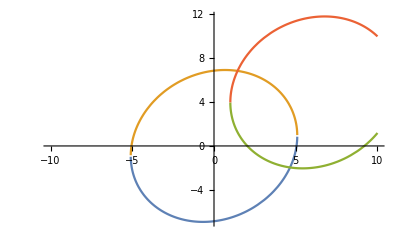

```mathematica
EllipseCoeffsFromProperties[{{0,0},{5,7},0.2}].{x^2,x y, y^2,x,y,1}==0
f1=y/.Solve[%,{x,y}]
EllipseCoeffsFromProperties[{{5,6},{5,7},0.2}].{x^2,x y, y^2,x,y,1}==0
f2=y/.Solve[%,{x,y}]
Plot[{f1,f2},{x,-10,10}]
```

```mathematica
Solve[%,{x,y}]
```

{{y→7.91597×10^-25 (-2.27511×10^23 x-2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))},{y→7.91597×10^-25 (-2.27511×10^23 x+2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))}}

### Q22.How do I determine the limits for a rotated ellipse?

The equation of the ellipse is :

```mathematica
f={Axx,Axy,Ayy,Ax,Ay,A0}.{x^2,x y, y^2,x,y,1}==0
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

The derivative for the X - axis is :

```mathematica
D[f,x]
```

Ax+2 Axx x+Axy y==0

```mathematica
dx=Ax+2 Axx x+Axy y
```

The derivative for the Y - axis is :

```mathematica
D[f,x]
```

Ax+2 Axx x+Axy y==0

```mathematica
dy=Ax+2 Axx x+Axy y
```

When dx is zero, then the current location is at the left or right limit
of the ellipse.When dy is zero, then the current location is at the bottom or top limit
of the ellipse.Calculating the limits for Y gives : General equation of the circle :

```mathematica
f
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

Expressing y in terms of x gives :

```mathematica
Solve[D[f,x],y]
Solve[D[f,y],y]
```

{{y→(-Ax-2 Axx x)/Axy}}

{{y→(-Ay-Axy x)/(2 Ayy)}}

Substituting into equation[1] gives :

```mathematica
Collect[f/.Solve[D[f,x],y][[1]],x]
Collect[f/.Solve[D[f,y],y][[1]],x]
```

A0-(Ax Ay)/Axy+(Ax^2 Ayy)/Axy^2+(-(2 Axx Ay)/Axy+(4 Ax Axx Ayy)/Axy^2) x+(-Axx+(4 Axx^2 Ayy)/Axy^2) x^2==0

A0-Ay^2/(4 Ayy)+(Ax-(Axy Ay)/(2 Ayy)) x+(Axx-Axy^2/(4 Ayy)) x^2==0

```mathematica
Ax+By+Cx+Dy+Exy+F=0

[2] dx=2Ax+C+Ey

[3] dy=2By+D+Ex

2 2
[1] Ax+By+Cx+Dy+Exy+F=0

Derivative of Y:[2] 2By+D+Ex=0


2By=-Ex-D

-Ex-D
y=------2B

Substituting into equation[1] gives:2
2|-Ex-D|               |-Ex-D|      |-Ex-D|Ax+B|------- |+Cx+D|------- |+Ex|------- |+F=0
            |2B|               |2B|      |2B|Multiplying out last two brackets gives:2 2 2
2|(-Ex-D)(-Ex-D)|-DEx-D-E x-DEx
Ax+B|--------------   |+Cx+---------+-----------+F=0
            |2|2B 2B
4B

Expanding out all brackets produces:2 2 2 2 2
2|E x+2DEx+D|2DE 2D 2E 2 2DE
Ax+B|---------------- |+Cx----x-------x----x+F=0
            |2|4B 4B 4B 4B
4B

Cancelling out terms in first bracket and breaking up last two brackets:2 2 2 2 2
2 E x+2DEx+D 2DE 2D 2E 2 2DE
Ax+-----------------+Cx----x--------x----x+F=0
4B 4B 4B 4B 4B

Breaking up first bracket produces:2 2 2 2
2 E 2 2DE D 2DE 2D 2E 2 2DE
Ax+--x+---x+--+Cx----x--------x----x+F=0
4B 4B 4B 4B 4B 4B 4B

Some rearrangement produces:2 2 2 2
2 E 2 2E 2 2DE 2DE 2DE D 2D
Ax+--x----x+Cx+---x----x----x+------+F=0
4B 4B 4B 4B 4B 4B 4B

Cancelling out and combining some terms produces:2 2 2 2
2 E 2 2E 2 2DE-4DE D-2D
Ax+--x---x+Cx+---------x+--------+F=0
4B 4B 4B 4B

Further reduction produces:2 2 2
2 E-2E 2 2DE D
Ax+--------x+Cx----x---+F=0
4B 4B 4B

Final cancellation out produces:2 2
2-E 2 DE D
Ax+---x+Cx---x---+F=0
4B 2B 4B

Expressing as a quadratic equation with parameter t produces:2
Pt+Qt+R=0


The final equation for the Y-axis:
|2|      |        |     |2|
|E|2|DE|     |D|
|A--- |t+ |C--- |t+ |F--- | =0
     |4B|      |2A|     |4B|And for the X-axis:
|2|      |        |     |2|
|E|2|CE|     |C|
|B--- |t+ |D--- |t+ |F--- | =0
     |4A|      |2B|     |4A|This produces terms:Y-axis X-axis

        |2|         |2|
|E|         |E|P= |A--- |P= |B--- |
|4B|         |4A|
|        |         |        |
|DE|         |CE|Q= |C--- |Q= |D--- |
|2A|         |2B|
|2|         |2|
|D|         |C|R= |F--- |R= |F--- |
|4B|         |4A|Multiplying out by the common denominator produces:The terms for both the X-axis and Y-axis are as follows:X-axis Y-axis
----------------------------------2 2
P=4AB-E P=4AB-E


Q=4BC-2DE Q=4AD-2CE

2 2
R=4BF-D R=4AF-C

----------------------------------
```

```mathematica
Map[FullSimplify,Map[(ArcTan[#[[1]],#[[2]]])&,ellipseBoundingPoints[{{x0,y0},{a,b},θ}]]]
```

{ArcTan[x0+((a-b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0+Cos[θ] √(b^2+a^2 Tan[θ]^2)],ArcTan[x0+((-a+b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0-Cos[θ] √(b^2+a^2 Tan[θ]^2)],ArcTan[x0-Cos[θ] √(a^2+b^2 Tan[θ]^2),y0+((-a^2+b^2) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))],ArcTan[x0+Cos[θ] √(a^2+b^2 Tan[θ]^2),y0+((a-b) (a+b) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))]}

```mathematica
If[OddQ[Quotient[θ,Pi/2]],
  aa=b;bb=a,
  aa=a;bb=b]
```

```mathematica
Piecewise[{{a,0≤ θ<Pi/2},{b,Pi/2≤ θ<Pi},{a,Pi≤ θ<3Pi/2},{b,3Pi/2≤ θ<2Pi}}]
```

Piecewise[{{a, 0≤θ<π/2}, {b, π/2≤θ<π}, {a, π≤θ<(3 π)/2}, {b, (3 π)/2≤θ<2 π}, {0, True}}]

```mathematica
Grid[{{"θ -> ","δθ"},
{"a -> ","a"},
{"b -> ","b"}}]
```

θ ->  | δθ
a ->  | a
b ->  | b

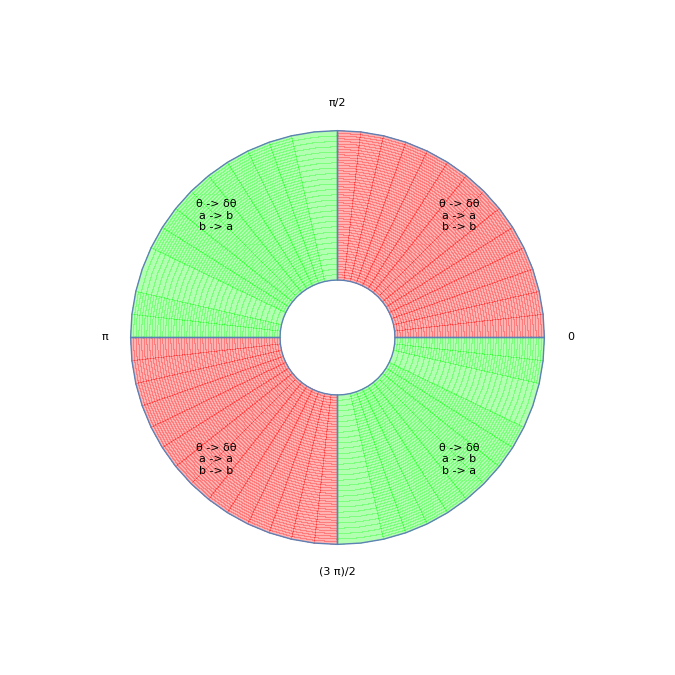

```mathematica
partShow[Piecewise[{{
Grid[{{"θ -> δθ"},{"a -> a"},{"b -> b"}}],0≤ θ<Pi/2||Pi≤ θ<3Pi/2},
{Grid[{{"θ -> δθ"},{"a -> b"},{"b -> a"}}],Pi/2≤ θ<Pi||3Pi/2≤ θ<2Pi}}]]
```

```mathematica
piecew
```

```mathematica
Block[{θ=0.2,x0=2,y0=3,a=3,b=2,aa,bb,at,bt,gfxSz=500},
If[OddQ[Quotient[θ,Pi/2]],
  aa=b;bb=a;at="b";bt="a";,
  aa=a;bb=b;at="a";bt="b";];
Θ=Quotient[θ,Pi/2]Pi/2;
δθ=Mod[θ,Pi/2];
Column[{
ellipseBoundingPoints[{{x0,y0},{aa,bb},δθ}],
ellipseBoundingBox[{{x0,y0},{aa,bb},δθ}]
}]
]
```

{{2.47519,5.04874},{1.52481,0.951257},{-0.966926,2.67187},{4.96693,3.32813}}
{{-1,5},{0,6}}

```mathematica
Manipulate[EllipticalBoundsFig=Block[{x0=2,y0=3,a=30,b=20,aa,bb,at,bt,gfxSz=500},
If[OddQ[Quotient[θ,Pi/2]],
  aa=b;bb=a;at="b";bt="a";,
  aa=a;bb=b;at="a";bt="b";];
Θ=Quotient[θ,Pi/2]Pi/2;
δθ=Mod[θ,Pi/2];
bBox=ellipseBoundingBox[{{x0,y0},{aa,bb},δθ}];
imgSz=ImageDimensions[Graphics[{EdgeForm[Red],FaceForm[None],Rectangle[Sequence@@Transpose[bBox]]},ImageSize->gfxSz]];
imgPltRng=Map[Abs[(#[[2]]-#[[1]])]&,plotRange[Graphics[{EdgeForm[Red],FaceForm[None],Rectangle[Sequence@@Transpose[bBox]]},ImageSize->gfxSz]]];
ebp=ellipseBoundingPoints[{{x0,y0},{aa,bb},δθ}];
tebp=Map[(11({x0,y0} - #)/12+{x0,y0})&,ebp];
Column[{
Graphics[{
{Dashed,Line[{{x0,y0}-bb{Cos[δθ+Pi/2],Sin[δθ+Pi/2]},{x0,y0}+bb{Cos[δθ+Pi/2],Sin[δθ+Pi/2]}}],Line[{{x0,y0}-aa{Cos[δθ],Sin[δθ]},{x0,y0}+aa{Cos[δθ],Sin[δθ]}}]},
{Black,PointSize[Large],Point[{x0,y0}],
  Text["(x0,y0)",{x0+0.1,y0-0.1},{-1,1},Background->White],
  Text["b",{x0+0.1,y0}+bb/2{Cos[δθ+Pi/2],Sin[δθ+Pi/2]},{-1,-1}],
  Text["a",{x0,y0}-aa/2 {Cos[δθ],Sin[δθ]},{-1,1}]},
{EdgeForm[Black],FaceForm[None],ellipse[{{x0,y0},{aa,bb},δθ}]},
{EdgeForm[Red],FaceForm[None],Rectangle[Sequence@@Transpose[bBox]]},
{Orange,PointSize[Large],Point[ebp],Table[{Text[Subscript[E, i],tebp[[i]]]},{i,1,4}]},
If[δθ>0,angleSymbol[{x0,y0},"δθ",{0,δθ},Green,imgSz,imgPltRng]]},ImageSize->gfxSz],
Row[{"θ = ",Θ," + ",δθ}],
Row[{"θ -> ",δθ}],
Row[{"a -> ",at}],
Row[{"b -> ",bt}]
}]
],{{θ,0.2},-2 Pi, 2 Pi}]
```

Set::setraw: Cannot assign to raw object 2.

Set::setraw: Cannot assign to raw object 3.

Set::setraw: Cannot assign to raw object 2.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 2.

Set::setraw: Cannot assign to raw object 3.

Set::setraw: Cannot assign to raw object 2.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {2,3}+{{-2,-3},{-30,-20},-1.20637} cannot be combined.

Part::partw: Part 2 of ellipseBoundingPoints[{2+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637}),3+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637})}] does not exist.

Part::partw: Part 3 of ellipseBoundingPoints[{2+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637}),3+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637})}] does not exist.

Part::partw: Part 4 of ellipseBoundingPoints[{2+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637}),3+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637})}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {2,3}+{{-2,-3},{-30,-20},-1.20637} cannot be combined.

Part::partw: Part 2 of ellipseBoundingPoints[{2+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637}),3+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637})}] does not exist.

Part::partw: Part 3 of ellipseBoundingPoints[{2+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637}),3+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637})}] does not exist.

Part::partw: Part 4 of ellipseBoundingPoints[{2+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637}),3+11/12 ({2,3}+{{-2,-3},{-30,-20},-1.20637})}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export[figPath<>"Elliptical_Bounds"<>".jpg",EllipticalBoundsFig,ImageResolution->300,ImageFormattingWidth->Infinity]
```

/Users/jaspershemilt/Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter4/Figs/Elliptical_Bounds.jpg

```mathematica
ellipseBoundingPoints[{{x0,y0},{a,b},θ}]
```

{{x0+((a-b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0+Cos[θ] √(b^2+a^2 Tan[θ]^2)},{x0-((a-b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0-Cos[θ] √(b^2+a^2 Tan[θ]^2)},{x0-Cos[θ] √(a^2+b^2 Tan[θ]^2),y0-((a-b) (a+b) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))},{x0+Cos[θ] √(a^2+b^2 Tan[θ]^2),y0+((a-b) (a+b) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))}}

```mathematica
ellipseBoundingBox[{{{x0_,y0_},{a_,b_},θ_}}]
```

```mathematica
Reduce[√(1+(b^2 Cot[θ]^2)/a^2)==1/a √(a^2+b^2 Cot[θ]^2)]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-√(Power[«2»]+Times[«2»])-a √(Power[«2»] Plus[«2»]))/a,0==-√(a^2+Power[«2»] Power[«2»])+a √((Power[«2»]+Times[«2»])/a^2),0==(√(a^2+Power[«2»] Power[«2»])-a √(Power[«2»] Plus[«2»]))/a,0==-√(a^2+Power[«2»] Power[«2»])+a √((Power[«2»]+Times[«2»])/a^2)}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(a≠0&&0==(-√(a^2+b^2 Cot[θ]^2)-a √((a^2+b^2 Cot[θ]^2)/a^2))/a&&0==-√(a^2+b^2 Cot[θ]^2)+a √((a^2+b^2 Cot[θ]^2)/a^2))||(a≠0&&0==(√(a^2+b^2 Cot[θ]^2)-a √((a^2+b^2 Cot[θ]^2)/a^2))/a&&0==-√(a^2+b^2 Cot[θ]^2)+a √((a^2+b^2 Cot[θ]^2)/a^2))

```mathematica
Manipulate[Block[{Θ,δθ},
Θ=Quotient[θ,Pi/2]Pi/2; δθ=Mod[θ,Pi/2];
Row[{"θ = ",Θ," + ",δθ}]
],{{θ,0.2},-2 Pi,2Pi}]
```

```mathematica
Θ=Quotient[θ,Pi/2]Pi/2
δθ=Mod[θ,Pi/2]
```

## Elliptical Fit to Points

```mathematica
d={(Subscript[p, {x,i}])^2,(Subscript[p, {x,i}]) (Subscript[p, {y,i}]), (Subscript[p, {y,i}])^2, (Subscript[p, {x,i}]), (Subscript[p, {y,i}]), 1};
DM=Outer[Sum[Times[#1,#2],i]&,d ,d];
Row[{"d = ",MatrixForm[d]}]
Row[{"DM = ",MatrixForm[DM]}]
```

d = (p_{x,i}^2
p_{x,i} p_{y,i}
p_{y,i}^2
p_{x,i}
p_{y,i}
1)

DM = (∑_i p_{x,i}^4 | ∑_i p_{x,i}^3 p_{y,i} | ∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i}^2
∑_i p_{x,i}^3 p_{y,i} | ∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}
∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}^3 | ∑_i p_{y,i}^4 | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3 | ∑_i p_{y,i}^2
∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{x,i}
∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2 | ∑_i p_{y,i}
∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2 | ∑_i p_{x,i} | ∑_i p_{y,i} | i)

```mathematica
Table[Format[Symbol["DM"<>ToString[i]<>ToString[j]],TraditionalForm]=Subscript["DM", ToString[i]<>","<>ToString[j]],{i,1,6},{j,1,6}];
Table[Format[Symbol["DM"<>ToString[i]<>ToString[j]],CForm]="DMd["<>ToString[i-1]<>"*6+"<>ToString[j-1]<>"]",{i,1,6},{j,1,6}];
DMsym=Table[Symbol["DM"<>ToString[i]<>ToString[j]],{i,1,6},{j,1,6}];
DMcform=Table["DMd["<>ToString[i]<>"*6+"<>ToString[j]<>"]",{i,0,5},{j,0,5}];
Row[{TraditionalForm[DMsym]," = ",TraditionalForm[DMcform]}]
```

(DM_(1,1) | DM_(1,2) | DM_(1,3) | DM_(1,4) | DM_(1,5) | DM_(1,6)
DM_(2,1) | DM_(2,2) | DM_(2,3) | DM_(2,4) | DM_(2,5) | DM_(2,6)
DM_(3,1) | DM_(3,2) | DM_(3,3) | DM_(3,4) | DM_(3,5) | DM_(3,6)
DM_(4,1) | DM_(4,2) | DM_(4,3) | DM_(4,4) | DM_(4,5) | DM_(4,6)
DM_(5,1) | DM_(5,2) | DM_(5,3) | DM_(5,4) | DM_(5,5) | DM_(5,6)
DM_(6,1) | DM_(6,2) | DM_(6,3) | DM_(6,4) | DM_(6,5) | DM_(6,6)) = (DMd[0*6+0] | DMd[0*6+1] | DMd[0*6+2] | DMd[0*6+3] | DMd[0*6+4] | DMd[0*6+5]
DMd[1*6+0] | DMd[1*6+1] | DMd[1*6+2] | DMd[1*6+3] | DMd[1*6+4] | DMd[1*6+5]
DMd[2*6+0] | DMd[2*6+1] | DMd[2*6+2] | DMd[2*6+3] | DMd[2*6+4] | DMd[2*6+5]
DMd[3*6+0] | DMd[3*6+1] | DMd[3*6+2] | DMd[3*6+3] | DMd[3*6+4] | DMd[3*6+5]
DMd[4*6+0] | DMd[4*6+1] | DMd[4*6+2] | DMd[4*6+3] | DMd[4*6+4] | DMd[4*6+5]
DMd[5*6+0] | DMd[5*6+1] | DMd[5*6+2] | DMd[5*6+3] | DMd[5*6+4] | DMd[5*6+5])

```mathematica
CForm[DMsym]
```

List(List("DM[0*6+0]","DM[0*6+1]","DM[0*6+2]","DM[0*6+3]","DM[0*6+4]","DM[0*6+5]"),
   List("DM[1*6+0]","DM[1*6+1]","DM[1*6+2]","DM[1*6+3]","DM[1*6+4]","DM[1*6+5]"),
   List("DM[2*6+0]","DM[2*6+1]","DM[2*6+2]","DM[2*6+3]","DM[2*6+4]","DM[2*6+5]"),
   List("DM[3*6+0]","DM[3*6+1]","DM[3*6+2]","DM[3*6+3]","DM[3*6+4]","DM[3*6+5]"),
   List("DM[4*6+0]","DM[4*6+1]","DM[4*6+2]","DM[4*6+3]","DM[4*6+4]","DM[4*6+5]"),
   List("DM[5*6+0]","DM[5*6+1]","DM[5*6+2]","DM[5*6+3]","DM[5*6+4]","DM[5*6+5]"))

### The AMS Method

```mathematica
Pfun=Function[{DM},{{DM[[1,1]]-DM[[1,6]]^2,DM[[1,2]]-DM[[1,6]]*DM[[2,6]],DM[[1,3]]-DM[[1,6]]*DM[[3,6]],DM[[1,4]],DM[[1,5]]},{
DM[[1,2]]-DM[[1,6]]*DM[[2,6]],DM[[2,2]]-DM[[2,6]]^2,DM[[2,3]]-DM[[2,6]]*DM[[3,6]],DM[[2,4]],DM[[2,5]]},{
DM[[1,3]]-DM[[1,6]]*DM[[3,6]],DM[[2,3]]-DM[[2,6]]*DM[[3,6]],DM[[3,3]]-DM[[3,6]]^2,DM[[3,4]],DM[[3,5]]},{
DM[[1,4]],DM[[2,4]],DM[[3,4]],DM[[4,4]],DM[[4,5]]},{
DM[[1,5]],DM[[2,5]],DM[[3,5]],DM[[4,5]],DM[[5,5]]}}];
P=Pfun[DM];
Psym=Pfun[DMsym];
```

```mathematica
Qfun=Function[{DM},{{4*DM[[1,6]],2*DM[[2,6]],0,0,0},
{ 2*DM[[2,6]],DM[[1,6]]+DM[[3,6]],2*DM[[2,6]],0,0},
{ 0,2*DM[[2,6]],4*DM[[3,6]],0,0},
{ 0,0,0,1,0},
{0,0,0,0,1}}];
Q=Qfun[DM];
Qsym=Qfun[DMsym];
```

```mathematica
Row[{"P = ",MatrixForm[Psym]," = ",MatrixForm[P]}]
Row[{"Q = ",MatrixForm[Qsym]," = ",MatrixForm[Q]}]
```

P = (DM11-DM16^2 | DM12-DM16 DM26 | DM13-DM16 DM36 | DM14 | DM15
DM12-DM16 DM26 | DM22-DM26^2 | DM23-DM26 DM36 | DM24 | DM25
DM13-DM16 DM36 | DM23-DM26 DM36 | DM33-DM36^2 | DM34 | DM35
DM14 | DM24 | DM34 | DM44 | DM45
DM15 | DM25 | DM35 | DM45 | DM55) = (-(∑_i p_{x,i}^2)^2+∑_i p_{x,i}^4 | (-∑_i p_{x,i}^2) ∑_i p_{x,i} p_{y,i}+∑_i p_{x,i}^3 p_{y,i} | (-∑_i p_{x,i}^2) ∑_i p_{y,i}^2+∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i}
(-∑_i p_{x,i}^2) ∑_i p_{x,i} p_{y,i}+∑_i p_{x,i}^3 p_{y,i} | -(∑_i p_{x,i} p_{y,i})^2+∑_i p_{x,i}^2 p_{y,i}^2 | (-∑_i p_{x,i} p_{y,i}) ∑_i p_{y,i}^2+∑_i p_{x,i} p_{y,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2
(-∑_i p_{x,i}^2) ∑_i p_{y,i}^2+∑_i p_{x,i}^2 p_{y,i}^2 | (-∑_i p_{x,i} p_{y,i}) ∑_i p_{y,i}^2+∑_i p_{x,i} p_{y,i}^3 | -(∑_i p_{y,i}^2)^2+∑_i p_{y,i}^4 | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3
∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i}
∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2)

Q = (4 DM16 | 2 DM26 | 0 | 0 | 0
2 DM26 | DM16+DM36 | 2 DM26 | 0 | 0
0 | 2 DM26 | 4 DM36 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1) = (4 ∑_i p_{x,i}^2 | 2 ∑_i p_{x,i} p_{y,i} | 0 | 0 | 0
2 ∑_i p_{x,i} p_{y,i} | ∑_i p_{x,i}^2+∑_i p_{y,i}^2 | 2 ∑_i p_{x,i} p_{y,i} | 0 | 0
0 | 2 ∑_i p_{x,i} p_{y,i} | 4 ∑_i p_{y,i}^2 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

To find the fit we solve the general eigenvalue problem.
P v = λ Q v
or
Q^-1 P v = λ v

```mathematica
Row[{"M = Q^-1 . P = ",TraditionalForm[FullSimplify[Inverse[Qsym].Psym]]}]
```

M = Q^-1 . P = ((((DM_(1,6))^2-DM_(1,1)+DM_(1,3)) (DM_(2,6))^2+(DM_(1,1)-(DM_(1,6))^2) (DM_(3,6))^2+(DM_(1,6) (-(DM_(1,6))^2+(DM_(2,6))^2+DM_(1,1))-2 DM_(1,2) DM_(2,6)) DM_(3,6))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((-DM_(1,2)+DM_(2,3)+DM_(1,6) DM_(2,6)) (DM_(2,6))^2+(DM_(1,2)-DM_(1,6) DM_(2,6)) (DM_(3,6))^2+((DM_(2,6))^3-((DM_(1,6))^2+2 DM_(2,2)) DM_(2,6)+DM_(1,2) DM_(1,6)) DM_(3,6))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((DM_(3,3)+DM_(3,6) (DM_(1,6)+DM_(3,6))) (DM_(2,6))^2-2 DM_(2,3) DM_(3,6) DM_(2,6)-DM_(1,6) (DM_(3,6))^2 (DM_(1,6)+DM_(3,6))+DM_(1,3) (DM_(3,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(2,6) (DM_(2,6) DM_(3,4)-2 DM_(2,4) DM_(3,6))+DM_(1,4) (DM_(3,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(2,6) (DM_(2,6) DM_(3,5)-2 DM_(2,5) DM_(3,6))+DM_(1,5) (DM_(3,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2))
-(DM_(1,3) DM_(1,6) DM_(2,6)+DM_(1,1) DM_(3,6) DM_(2,6)-2 DM_(1,2) DM_(1,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | -(DM_(1,6) DM_(2,3) DM_(2,6)+DM_(1,2) DM_(3,6) DM_(2,6)-2 DM_(1,6) DM_(2,2) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | -(DM_(1,6) DM_(2,6) DM_(3,3)-2 DM_(1,6) DM_(2,3) DM_(3,6)+DM_(1,3) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | -(DM_(1,6) DM_(2,6) DM_(3,4)-2 DM_(1,6) DM_(2,4) DM_(3,6)+DM_(1,4) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | -(DM_(1,6) DM_(2,6) DM_(3,5)-2 DM_(1,6) DM_(2,5) DM_(3,6)+DM_(1,5) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2))
(((DM_(1,6))^2+DM_(1,1)) (DM_(2,6))^2-2 DM_(1,2) DM_(1,6) DM_(2,6)-(DM_(1,6))^2 (DM_(3,6))^2+DM_(1,6) ((DM_(2,6))^2-(DM_(1,6))^2) DM_(3,6)+DM_(1,3) (DM_(1,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((DM_(2,3)-DM_(2,6) DM_(3,6)) (DM_(1,6))^2+((DM_(2,6))^3-(DM_(3,6))^2 DM_(2,6)-2 DM_(2,2) DM_(2,6)+DM_(2,3) DM_(3,6)) DM_(1,6)+(DM_(2,6))^2 (DM_(1,2)-DM_(2,3)+DM_(2,6) DM_(3,6)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((DM_(3,3)-(DM_(3,6))^2) (DM_(1,6))^2+(DM_(3,6) ((DM_(2,6))^2-(DM_(3,6))^2+DM_(3,3))-2 DM_(2,3) DM_(2,6)) DM_(1,6)+(DM_(2,6))^2 ((DM_(3,6))^2+DM_(1,3)-DM_(3,3)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(3,4) (DM_(1,6))^2+(DM_(3,4) DM_(3,6)-2 DM_(2,4) DM_(2,6)) DM_(1,6)+(DM_(2,6))^2 (DM_(1,4)-DM_(3,4)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(3,5) (DM_(1,6))^2+(DM_(3,5) DM_(3,6)-2 DM_(2,5) DM_(2,6)) DM_(1,6)+(DM_(2,6))^2 (DM_(1,5)-DM_(3,5)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2))
DM_(1,4) | DM_(2,4) | DM_(3,4) | DM_(4,4) | DM_(4,5)
DM_(1,5) | DM_(2,5) | DM_(3,5) | DM_(4,5) | DM_(5,5))

```mathematica
MAMSfun=Function[{Dm},{{((-Dm⟦1,1⟧+Dm⟦1,3⟧+Dm⟦1,6⟧^2) Dm⟦2,6⟧^2+(-2 Dm⟦1,2⟧ Dm⟦2,6⟧+Dm⟦1,6⟧ (Dm⟦1,1⟧-Dm⟦1,6⟧^2+Dm⟦2,6⟧^2)) Dm⟦3,6⟧+(Dm⟦1,1⟧-Dm⟦1,6⟧^2) Dm⟦3,6⟧^2)/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦2,6⟧^2 (-Dm⟦1,2⟧+Dm⟦2,3⟧+Dm⟦1,6⟧ Dm⟦2,6⟧)+(Dm⟦1,2⟧ Dm⟦1,6⟧-(Dm⟦1,6⟧^2+2 Dm⟦2,2⟧) Dm⟦2,6⟧+Dm⟦2,6⟧^3) Dm⟦3,6⟧+(Dm⟦1,2⟧-Dm⟦1,6⟧ Dm⟦2,6⟧) Dm⟦3,6⟧^2)/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(-2 Dm⟦2,3⟧ Dm⟦2,6⟧ Dm⟦3,6⟧-Dm⟦1,6⟧ Dm⟦3,6⟧^2 (Dm⟦1,6⟧+Dm⟦3,6⟧)+Dm⟦1,3⟧ (-Dm⟦2,6⟧^2+Dm⟦3,6⟧ (Dm⟦1,6⟧+Dm⟦3,6⟧))+Dm⟦2,6⟧^2 (Dm⟦3,3⟧+Dm⟦3,6⟧ (Dm⟦1,6⟧+Dm⟦3,6⟧)))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦2,6⟧ (Dm⟦2,6⟧ Dm⟦3,4⟧-2 Dm⟦2,4⟧ Dm⟦3,6⟧)+Dm⟦1,4⟧ (-Dm⟦2,6⟧^2+Dm⟦3,6⟧ (Dm⟦1,6⟧+Dm⟦3,6⟧)))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦2,6⟧ (Dm⟦2,6⟧ Dm⟦3,5⟧-2 Dm⟦2,5⟧ Dm⟦3,6⟧)+Dm⟦1,5⟧ (-Dm⟦2,6⟧^2+Dm⟦3,6⟧ (Dm⟦1,6⟧+Dm⟦3,6⟧)))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧))},{(-Dm⟦1,3⟧ Dm⟦1,6⟧ Dm⟦2,6⟧+(2 Dm⟦1,2⟧ Dm⟦1,6⟧-Dm⟦1,1⟧ Dm⟦2,6⟧) Dm⟦3,6⟧)/(2 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(-Dm⟦1,2⟧ Dm⟦2,6⟧ Dm⟦3,6⟧+Dm⟦1,6⟧ (-Dm⟦2,3⟧ Dm⟦2,6⟧+2 Dm⟦2,2⟧ Dm⟦3,6⟧))/(2 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(-Dm⟦1,3⟧ Dm⟦2,6⟧ Dm⟦3,6⟧+Dm⟦1,6⟧ (-Dm⟦2,6⟧ Dm⟦3,3⟧+2 Dm⟦2,3⟧ Dm⟦3,6⟧))/(2 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(-Dm⟦1,4⟧ Dm⟦2,6⟧ Dm⟦3,6⟧+Dm⟦1,6⟧ (-Dm⟦2,6⟧ Dm⟦3,4⟧+2 Dm⟦2,4⟧ Dm⟦3,6⟧))/(2 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(-Dm⟦1,5⟧ Dm⟦2,6⟧ Dm⟦3,6⟧+Dm⟦1,6⟧ (-Dm⟦2,6⟧ Dm⟦3,5⟧+2 Dm⟦2,5⟧ Dm⟦3,6⟧))/(2 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧))},{(-2 Dm⟦1,2⟧ Dm⟦1,6⟧ Dm⟦2,6⟧+(Dm⟦1,1⟧+Dm⟦1,6⟧^2) Dm⟦2,6⟧^2+Dm⟦1,6⟧ (-Dm⟦1,6⟧^2+Dm⟦2,6⟧^2) Dm⟦3,6⟧-Dm⟦1,6⟧^2 Dm⟦3,6⟧^2+Dm⟦1,3⟧ (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ (Dm⟦1,6⟧+Dm⟦3,6⟧)))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦1,6⟧^2 (Dm⟦2,3⟧-Dm⟦2,6⟧ Dm⟦3,6⟧)+Dm⟦2,6⟧^2 (Dm⟦1,2⟧-Dm⟦2,3⟧+Dm⟦2,6⟧ Dm⟦3,6⟧)+Dm⟦1,6⟧ (Dm⟦2,3⟧ Dm⟦3,6⟧+Dm⟦2,6⟧ (-2 Dm⟦2,2⟧+Dm⟦2,6⟧^2-Dm⟦3,6⟧^2)))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦1,6⟧^2 (Dm⟦3,3⟧-Dm⟦3,6⟧^2)+Dm⟦2,6⟧^2 (Dm⟦1,3⟧-Dm⟦3,3⟧+Dm⟦3,6⟧^2)+Dm⟦1,6⟧ (-2 Dm⟦2,3⟧ Dm⟦2,6⟧+Dm⟦3,6⟧ (Dm⟦2,6⟧^2+Dm⟦3,3⟧-Dm⟦3,6⟧^2)))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦2,6⟧^2 (Dm⟦1,4⟧-Dm⟦3,4⟧)+Dm⟦1,6⟧^2 Dm⟦3,4⟧+Dm⟦1,6⟧ (-2 Dm⟦2,4⟧ Dm⟦2,6⟧+Dm⟦3,4⟧ Dm⟦3,6⟧))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧)),(Dm⟦2,6⟧^2 (Dm⟦1,5⟧-Dm⟦3,5⟧)+Dm⟦1,6⟧^2 Dm⟦3,5⟧+Dm⟦1,6⟧ (-2 Dm⟦2,5⟧ Dm⟦2,6⟧+Dm⟦3,5⟧ Dm⟦3,6⟧))/(4 (Dm⟦1,6⟧+Dm⟦3,6⟧) (-Dm⟦2,6⟧^2+Dm⟦1,6⟧ Dm⟦3,6⟧))},{Dm⟦1,4⟧,Dm⟦2,4⟧,Dm⟦3,4⟧,Dm⟦4,4⟧,Dm⟦4,5⟧},{Dm⟦1,5⟧,Dm⟦2,5⟧,Dm⟦3,5⟧,Dm⟦4,5⟧,Dm⟦5,5⟧}}];
Row[{"M = Q^-1 . P = ",TraditionalForm[MAMSfun[DMsym]]}]
```

M = Q^-1 . P = ((((DM_(1,6))^2-DM_(1,1)+DM_(1,3)) (DM_(2,6))^2+(DM_(1,1)-(DM_(1,6))^2) (DM_(3,6))^2+(DM_(1,6) (-(DM_(1,6))^2+(DM_(2,6))^2+DM_(1,1))-2 DM_(1,2) DM_(2,6)) DM_(3,6))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((-DM_(1,2)+DM_(2,3)+DM_(1,6) DM_(2,6)) (DM_(2,6))^2+(DM_(1,2)-DM_(1,6) DM_(2,6)) (DM_(3,6))^2+((DM_(2,6))^3-((DM_(1,6))^2+2 DM_(2,2)) DM_(2,6)+DM_(1,2) DM_(1,6)) DM_(3,6))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((DM_(3,3)+DM_(3,6) (DM_(1,6)+DM_(3,6))) (DM_(2,6))^2-2 DM_(2,3) DM_(3,6) DM_(2,6)-DM_(1,6) (DM_(3,6))^2 (DM_(1,6)+DM_(3,6))+DM_(1,3) (DM_(3,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(2,6) (DM_(2,6) DM_(3,4)-2 DM_(2,4) DM_(3,6))+DM_(1,4) (DM_(3,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(2,6) (DM_(2,6) DM_(3,5)-2 DM_(2,5) DM_(3,6))+DM_(1,5) (DM_(3,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2))
((2 DM_(1,2) DM_(1,6)-DM_(1,1) DM_(2,6)) DM_(3,6)-DM_(1,3) DM_(1,6) DM_(2,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(1,6) (2 DM_(2,2) DM_(3,6)-DM_(2,3) DM_(2,6))-DM_(1,2) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(1,6) (2 DM_(2,3) DM_(3,6)-DM_(2,6) DM_(3,3))-DM_(1,3) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(1,6) (2 DM_(2,4) DM_(3,6)-DM_(2,6) DM_(3,4))-DM_(1,4) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(1,6) (2 DM_(2,5) DM_(3,6)-DM_(2,6) DM_(3,5))-DM_(1,5) DM_(2,6) DM_(3,6))/(2 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2))
(((DM_(1,6))^2+DM_(1,1)) (DM_(2,6))^2-2 DM_(1,2) DM_(1,6) DM_(2,6)-(DM_(1,6))^2 (DM_(3,6))^2+DM_(1,6) ((DM_(2,6))^2-(DM_(1,6))^2) DM_(3,6)+DM_(1,3) (DM_(1,6) (DM_(1,6)+DM_(3,6))-(DM_(2,6))^2))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((DM_(2,3)-DM_(2,6) DM_(3,6)) (DM_(1,6))^2+(DM_(2,3) DM_(3,6)+DM_(2,6) ((DM_(2,6))^2-(DM_(3,6))^2-2 DM_(2,2))) DM_(1,6)+(DM_(2,6))^2 (DM_(1,2)-DM_(2,3)+DM_(2,6) DM_(3,6)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | ((DM_(3,3)-(DM_(3,6))^2) (DM_(1,6))^2+(DM_(3,6) ((DM_(2,6))^2-(DM_(3,6))^2+DM_(3,3))-2 DM_(2,3) DM_(2,6)) DM_(1,6)+(DM_(2,6))^2 ((DM_(3,6))^2+DM_(1,3)-DM_(3,3)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(3,4) (DM_(1,6))^2+(DM_(3,4) DM_(3,6)-2 DM_(2,4) DM_(2,6)) DM_(1,6)+(DM_(2,6))^2 (DM_(1,4)-DM_(3,4)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2)) | (DM_(3,5) (DM_(1,6))^2+(DM_(3,5) DM_(3,6)-2 DM_(2,5) DM_(2,6)) DM_(1,6)+(DM_(2,6))^2 (DM_(1,5)-DM_(3,5)))/(4 (DM_(1,6)+DM_(3,6)) (DM_(1,6) DM_(3,6)-(DM_(2,6))^2))
DM_(1,4) | DM_(2,4) | DM_(3,4) | DM_(4,4) | DM_(4,5)
DM_(1,5) | DM_(2,5) | DM_(3,5) | DM_(4,5) | DM_(5,5))

```mathematica
MAMScform=MAMSfun[DMsym];
Column[Flatten[Table[Row[{"Md["<>ToString[i]<>"*5+"<>ToString[j]<>"] = ",CForm[MAMScform[[i+1,j+1]]],";"}],{i,0,4},{j,0,4}]]]
```

Md[0*6+0] = ((-"DMd[0*6+0]" + "DMd[0*6+2]" + Power("DMd[0*6+5]",2))*Power("DMd[1*6+5]",2) + (-2*"DMd[0*6+1]"*"DMd[1*6+5]" + "DMd[0*6+5]"*("DMd[0*6+0]" - Power("DMd[0*6+5]",2) + Power("DMd[1*6+5]",2)))*"DMd[2*6+5]" + ("DMd[0*6+0]" - Power("DMd[0*6+5]",2))*Power("DMd[2*6+5]",2))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[0*6+1] = (Power("DMd[1*6+5]",2)*(-"DMd[0*6+1]" + "DMd[1*6+2]" + "DMd[0*6+5]"*"DMd[1*6+5]") + ("DMd[0*6+1]"*"DMd[0*6+5]" - (Power("DMd[0*6+5]",2) + 2*"DMd[1*6+1]")*"DMd[1*6+5]" + Power("DMd[1*6+5]",3))*"DMd[2*6+5]" + ("DMd[0*6+1]" - "DMd[0*6+5]"*"DMd[1*6+5]")*Power("DMd[2*6+5]",2))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[0*6+2] = (-2*"DMd[1*6+2]"*"DMd[1*6+5]"*"DMd[2*6+5]" - "DMd[0*6+5]"*Power("DMd[2*6+5]",2)*("DMd[0*6+5]" + "DMd[2*6+5]") + "DMd[0*6+2]"*(-Power("DMd[1*6+5]",2) + "DMd[2*6+5]"*("DMd[0*6+5]" + "DMd[2*6+5]")) + Power("DMd[1*6+5]",2)*("DMd[2*6+2]" + "DMd[2*6+5]"*("DMd[0*6+5]" + "DMd[2*6+5]")))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[0*6+3] = ("DMd[1*6+5]"*("DMd[1*6+5]"*"DMd[2*6+3]" - 2*"DMd[1*6+3]"*"DMd[2*6+5]") + "DMd[0*6+3]"*(-Power("DMd[1*6+5]",2) + "DMd[2*6+5]"*("DMd[0*6+5]" + "DMd[2*6+5]")))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[0*6+4] = ("DMd[1*6+5]"*("DMd[1*6+5]"*"DMd[2*6+4]" - 2*"DMd[1*6+4]"*"DMd[2*6+5]") + "DMd[0*6+4]"*(-Power("DMd[1*6+5]",2) + "DMd[2*6+5]"*("DMd[0*6+5]" + "DMd[2*6+5]")))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[1*6+0] = (-("DMd[0*6+2]"*"DMd[0*6+5]"*"DMd[1*6+5]") + (2*"DMd[0*6+1]"*"DMd[0*6+5]" - "DMd[0*6+0]"*"DMd[1*6+5]")*"DMd[2*6+5]")/(2.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[1*6+1] = (-("DMd[0*6+1]"*"DMd[1*6+5]"*"DMd[2*6+5]") + "DMd[0*6+5]"*(-("DMd[1*6+2]"*"DMd[1*6+5]") + 2*"DMd[1*6+1]"*"DMd[2*6+5]"))/(2.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[1*6+2] = (-("DMd[0*6+2]"*"DMd[1*6+5]"*"DMd[2*6+5]") + "DMd[0*6+5]"*(-("DMd[1*6+5]"*"DMd[2*6+2]") + 2*"DMd[1*6+2]"*"DMd[2*6+5]"))/(2.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[1*6+3] = (-("DMd[0*6+3]"*"DMd[1*6+5]"*"DMd[2*6+5]") + "DMd[0*6+5]"*(-("DMd[1*6+5]"*"DMd[2*6+3]") + 2*"DMd[1*6+3]"*"DMd[2*6+5]"))/(2.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[1*6+4] = (-("DMd[0*6+4]"*"DMd[1*6+5]"*"DMd[2*6+5]") + "DMd[0*6+5]"*(-("DMd[1*6+5]"*"DMd[2*6+4]") + 2*"DMd[1*6+4]"*"DMd[2*6+5]"))/(2.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[2*6+0] = (-2*"DMd[0*6+1]"*"DMd[0*6+5]"*"DMd[1*6+5]" + ("DMd[0*6+0]" + Power("DMd[0*6+5]",2))*Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*(-Power("DMd[0*6+5]",2) + Power("DMd[1*6+5]",2))*"DMd[2*6+5]" - Power("DMd[0*6+5]",2)*Power("DMd[2*6+5]",2) + "DMd[0*6+2]"*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*("DMd[0*6+5]" + "DMd[2*6+5]")))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[2*6+1] = (Power("DMd[0*6+5]",2)*("DMd[1*6+2]" - "DMd[1*6+5]"*"DMd[2*6+5]") + Power("DMd[1*6+5]",2)*("DMd[0*6+1]" - "DMd[1*6+2]" + "DMd[1*6+5]"*"DMd[2*6+5]") + "DMd[0*6+5]"*("DMd[1*6+2]"*"DMd[2*6+5]" + "DMd[1*6+5]"*(-2*"DMd[1*6+1]" + Power("DMd[1*6+5]",2) - Power("DMd[2*6+5]",2))))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[2*6+2] = (Power("DMd[0*6+5]",2)*("DMd[2*6+2]" - Power("DMd[2*6+5]",2)) + Power("DMd[1*6+5]",2)*("DMd[0*6+2]" - "DMd[2*6+2]" + Power("DMd[2*6+5]",2)) + "DMd[0*6+5]"*(-2*"DMd[1*6+2]"*"DMd[1*6+5]" + "DMd[2*6+5]"*(Power("DMd[1*6+5]",2) + "DMd[2*6+2]" - Power("DMd[2*6+5]",2))))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[2*6+3] = (Power("DMd[1*6+5]",2)*("DMd[0*6+3]" - "DMd[2*6+3]") + Power("DMd[0*6+5]",2)*"DMd[2*6+3]" + "DMd[0*6+5]"*(-2*"DMd[1*6+3]"*"DMd[1*6+5]" + "DMd[2*6+3]"*"DMd[2*6+5]"))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[2*6+4] = (Power("DMd[1*6+5]",2)*("DMd[0*6+4]" - "DMd[2*6+4]") + Power("DMd[0*6+5]",2)*"DMd[2*6+4]" + "DMd[0*6+5]"*(-2*"DMd[1*6+4]"*"DMd[1*6+5]" + "DMd[2*6+4]"*"DMd[2*6+5]"))/(4.*("DMd[0*6+5]" + "DMd[2*6+5]")*(-Power("DMd[1*6+5]",2) + "DMd[0*6+5]"*"DMd[2*6+5]"));
Md[3*6+0] = "DMd[0*6+3]";
Md[3*6+1] = "DMd[1*6+3]";
Md[3*6+2] = "DMd[2*6+3]";
Md[3*6+3] = "DMd[3*6+3]";
Md[3*6+4] = "DMd[3*6+4]";
Md[4*6+0] = "DMd[0*6+4]";
Md[4*6+1] = "DMd[1*6+4]";
Md[4*6+2] = "DMd[2*6+4]";
Md[4*6+3] = "DMd[3*6+4]";
Md[4*6+4] = "DMd[4*6+4]";

### The Direct Method

The direct method uses a partitioning of the DM matrix

```mathematica
S1fun=Function[{DM},DM[[1;;3,1;;3]]];
S2fun=Function[{DM},DM[[1;;3,4;;6]]];
S3fun=Function[{DM},DM[[4;;6,4;;6]]];
S1=S1fun[DM]; S1sym=S1fun[DMsym];
S2=S2fun[DM]; S2sym=S2fun[DMsym];
S3=S3fun[DM]; S3sym=S3fun[DMsym];
Row[{TraditionalForm[{{"S1","S2"},{"S2^T","S3"}}]," = ",TraditionalForm[DMsym]," = ",MatrixForm[{{TraditionalForm[S1sym],TraditionalForm[S2sym]},{TraditionalForm[Transpose[S2sym]],TraditionalForm[S3sym]}}]," = ",MatrixForm[DM]," = ",MatrixForm[{{MatrixForm[S1],MatrixForm[S2]},{MatrixForm[Transpose[S2]],MatrixForm[S3]}}]}]
```

(S1 | S2
S2^T | S3) = (DM_(1,1) | DM_(1,2) | DM_(1,3) | DM_(1,4) | DM_(1,5) | DM_(1,6)
DM_(2,1) | DM_(2,2) | DM_(2,3) | DM_(2,4) | DM_(2,5) | DM_(2,6)
DM_(3,1) | DM_(3,2) | DM_(3,3) | DM_(3,4) | DM_(3,5) | DM_(3,6)
DM_(4,1) | DM_(4,2) | DM_(4,3) | DM_(4,4) | DM_(4,5) | DM_(4,6)
DM_(5,1) | DM_(5,2) | DM_(5,3) | DM_(5,4) | DM_(5,5) | DM_(5,6)
DM_(6,1) | DM_(6,2) | DM_(6,3) | DM_(6,4) | DM_(6,5) | DM_(6,6)) = ((DM_(1,1) | DM_(1,2) | DM_(1,3)
DM_(2,1) | DM_(2,2) | DM_(2,3)
DM_(3,1) | DM_(3,2) | DM_(3,3)) | (DM_(1,4) | DM_(1,5) | DM_(1,6)
DM_(2,4) | DM_(2,5) | DM_(2,6)
DM_(3,4) | DM_(3,5) | DM_(3,6))
(DM_(1,4) | DM_(2,4) | DM_(3,4)
DM_(1,5) | DM_(2,5) | DM_(3,5)
DM_(1,6) | DM_(2,6) | DM_(3,6)) | (DM_(4,4) | DM_(4,5) | DM_(4,6)
DM_(5,4) | DM_(5,5) | DM_(5,6)
DM_(6,4) | DM_(6,5) | DM_(6,6))) = (∑_i p_{x,i}^4 | ∑_i p_{x,i}^3 p_{y,i} | ∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i}^2
∑_i p_{x,i}^3 p_{y,i} | ∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}
∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}^3 | ∑_i p_{y,i}^4 | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3 | ∑_i p_{y,i}^2
∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{x,i}
∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2 | ∑_i p_{y,i}
∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2 | ∑_i p_{x,i} | ∑_i p_{y,i} | i) = ((∑_i p_{x,i}^4 | ∑_i p_{x,i}^3 p_{y,i} | ∑_i p_{x,i}^2 p_{y,i}^2
∑_i p_{x,i}^3 p_{y,i} | ∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}^3
∑_i p_{x,i}^2 p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}^3 | ∑_i p_{y,i}^4) | (∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i}^2
∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{x,i} p_{y,i}
∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3 | ∑_i p_{y,i}^2)
(∑_i p_{x,i}^3 | ∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2
∑_i p_{x,i}^2 p_{y,i} | ∑_i p_{x,i} p_{y,i}^2 | ∑_i p_{y,i}^3
∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2) | (∑_i p_{x,i}^2 | ∑_i p_{x,i} p_{y,i} | ∑_i p_{x,i}
∑_i p_{x,i} p_{y,i} | ∑_i p_{y,i}^2 | ∑_i p_{y,i}
∑_i p_{x,i} | ∑_i p_{y,i} | i))

```mathematica
S3inv=FullSimplify[Assuming[And@@Flatten[Table[Element[Symbol["DM"<>ToString[i]<>ToString[j]],Reals],{i,1,6},{j,1,6}]], Inverse[S3sym]]];
S3invM=FullSimplify[Det[S3sym] S3inv];
TsymM = FullSimplify[- Assuming[Table[Element[Symbol["DM"<>ToString[i]<>ToString[j]],Reals],{i,1,6},{j,1,6}],  S3invM . Transpose[S2sym]]];

Tsym = FullSimplify[- Assuming[Table[Element[Symbol["DM"<>ToString[i]<>ToString[j]],Reals],{i,1,6},{j,1,6}],(1/Det[S3sym])  S3invM . Transpose[S2sym]]];
MDirect = Reverse[{1/2,-1,1/2} * (S1sym + S2sym. Tsym)];
```

```mathematica
Row[{"S3^-1 = ",TraditionalForm[1/Det["S3"]],TraditionalForm[S3invM]," = ",TraditionalForm[S3inv]}]
Row[{"M = ",MatrixForm[{1/2,-1,1/2}] ," ⊗ ", ("(S1 - S2 . S3^-1. S2^T )")}]
Row[{"T = ",(1/Det[S3sym]),MatrixForm[TsymM] }]
Row[{"M = ",MatrixForm[{1/2,-1,1/2}] ," ⊗ ", ("(S1 - S2 . T )")}]
```

S3^-1 = 1/Det[S3](DM_(5,5) DM_(6,6)-DM_(5,6) DM_(6,5) | DM_(4,6) DM_(6,5)-DM_(4,5) DM_(6,6) | DM_(4,5) DM_(5,6)-DM_(4,6) DM_(5,5)
DM_(5,6) DM_(6,4)-DM_(5,4) DM_(6,6) | DM_(4,4) DM_(6,6)-DM_(4,6) DM_(6,4) | DM_(4,6) DM_(5,4)-DM_(4,4) DM_(5,6)
DM_(5,4) DM_(6,5)-DM_(5,5) DM_(6,4) | DM_(4,5) DM_(6,4)-DM_(4,4) DM_(6,5) | DM_(4,4) DM_(5,5)-DM_(4,5) DM_(5,4)) = ((DM_(5,6) DM_(6,5)-DM_(5,5) DM_(6,6))/(DM_(4,6) DM_(5,5) DM_(6,4)-DM_(4,5) DM_(5,6) DM_(6,4)-DM_(4,6) DM_(5,4) DM_(6,5)+DM_(4,4) DM_(5,6) DM_(6,5)+DM_(4,5) DM_(5,4) DM_(6,6)-DM_(4,4) DM_(5,5) DM_(6,6)) | (DM_(4,6) DM_(6,5)-DM_(4,5) DM_(6,6))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6)) | (DM_(4,6) DM_(5,5)-DM_(4,5) DM_(5,6))/(DM_(4,6) DM_(5,5) DM_(6,4)-DM_(4,5) DM_(5,6) DM_(6,4)-DM_(4,6) DM_(5,4) DM_(6,5)+DM_(4,4) DM_(5,6) DM_(6,5)+DM_(4,5) DM_(5,4) DM_(6,6)-DM_(4,4) DM_(5,5) DM_(6,6))
(DM_(5,6) DM_(6,4)-DM_(5,4) DM_(6,6))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6)) | (DM_(4,6) DM_(6,4)-DM_(4,4) DM_(6,6))/(DM_(4,6) DM_(5,5) DM_(6,4)-DM_(4,5) DM_(5,6) DM_(6,4)-DM_(4,6) DM_(5,4) DM_(6,5)+DM_(4,4) DM_(5,6) DM_(6,5)+DM_(4,5) DM_(5,4) DM_(6,6)-DM_(4,4) DM_(5,5) DM_(6,6)) | (DM_(4,6) DM_(5,4)-DM_(4,4) DM_(5,6))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))
(DM_(5,5) DM_(6,4)-DM_(5,4) DM_(6,5))/(DM_(4,6) DM_(5,5) DM_(6,4)-DM_(4,5) DM_(5,6) DM_(6,4)-DM_(4,6) DM_(5,4) DM_(6,5)+DM_(4,4) DM_(5,6) DM_(6,5)+DM_(4,5) DM_(5,4) DM_(6,6)-DM_(4,4) DM_(5,5) DM_(6,6)) | (DM_(4,5) DM_(6,4)-DM_(4,4) DM_(6,5))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6)) | (DM_(4,5) DM_(5,4)-DM_(4,4) DM_(5,5))/(DM_(4,6) DM_(5,5) DM_(6,4)-DM_(4,5) DM_(5,6) DM_(6,4)-DM_(4,6) DM_(5,4) DM_(6,5)+DM_(4,4) DM_(5,6) DM_(6,5)+DM_(4,5) DM_(5,4) DM_(6,6)-DM_(4,4) DM_(5,5) DM_(6,6)))

M = (1/2
-1
1/2) ⊗ (S1 - S2 . S3^-1. S2^T )

T = 1/(-DM46 DM55 DM64+DM45 DM56 DM64+DM46 DM54 DM65-DM44 DM56 DM65-DM45 DM54 DM66+DM44 DM55 DM66)(DM16 DM46 DM55-DM16 DM45 DM56-DM15 DM46 DM65+DM14 DM56 DM65+DM15 DM45 DM66-DM14 DM55 DM66 | DM26 DM46 DM55-DM26 DM45 DM56-DM25 DM46 DM65+DM24 DM56 DM65+DM25 DM45 DM66-DM24 DM55 DM66 | DM36 DM46 DM55-DM36 DM45 DM56-DM35 DM46 DM65+DM34 DM56 DM65+DM35 DM45 DM66-DM34 DM55 DM66
-DM16 DM46 DM54+DM16 DM44 DM56+DM15 DM46 DM64-DM14 DM56 DM64-DM15 DM44 DM66+DM14 DM54 DM66 | -DM26 DM46 DM54+DM26 DM44 DM56+DM25 DM46 DM64-DM24 DM56 DM64-DM25 DM44 DM66+DM24 DM54 DM66 | -DM36 DM46 DM54+DM36 DM44 DM56+DM35 DM46 DM64-DM34 DM56 DM64-DM35 DM44 DM66+DM34 DM54 DM66
DM16 DM45 DM54-DM16 DM44 DM55-DM15 DM45 DM64+DM14 DM55 DM64+DM15 DM44 DM65-DM14 DM54 DM65 | DM26 DM45 DM54-DM26 DM44 DM55-DM25 DM45 DM64+DM24 DM55 DM64+DM25 DM44 DM65-DM24 DM54 DM65 | DM36 DM45 DM54-DM36 DM44 DM55-DM35 DM45 DM64+DM34 DM55 DM64+DM35 DM44 DM65-DM34 DM54 DM65)

M = (1/2
-1
1/2) ⊗ (S1 - S2 . T )

```mathematica
StringReplace["DM12 DM34",RegularExpression["DM(\\d)(\\d)"]->"DM[[$1,$2]]"]
```

DM[1,2] DM[3,4]

```mathematica
TMfun=Function[{DM},{{DM⟦1,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦1,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦1,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦1,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦1,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦1,4⟧ DM⟦5,5⟧ DM⟦6,6⟧,DM⟦2,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦2,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,6⟧,DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,6⟧},{-DM⟦1,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦1,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦1,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦1,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦1,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦1,4⟧ DM⟦5,4⟧ DM⟦6,6⟧,-DM⟦2,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦2,4⟧ DM⟦5,4⟧ DM⟦6,6⟧,-DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,6⟧},{DM⟦1,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦1,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦1,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦1,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦1,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦1,4⟧ DM⟦5,4⟧ DM⟦6,5⟧,DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦2,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦2,4⟧ DM⟦5,4⟧ DM⟦6,5⟧,DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,5⟧}}];
TSfun=Function[{DM},1/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)];
MDirectFun=Function[{DM},Reverse[{1/2,-1,1/2} * (DM⟦1;;3,1;;3⟧ + TSfun[DM]  DM⟦1;;3,4;;6⟧. TMfun[DM])]];
MDirectExpandedFun=Function[{DM},{{Rational[1,2] (DM⟦3,1⟧+(DM⟦1,6⟧ (DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦3,5⟧ DM⟦4,6⟧ DM⟦5,4⟧-DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,5⟧+DM⟦3,4⟧ DM⟦4,6⟧ DM⟦5,5⟧+DM⟦3,5⟧ DM⟦4,4⟧ DM⟦5,6⟧-DM⟦3,4⟧ DM⟦4,5⟧ DM⟦5,6⟧)+DM⟦1,5⟧ (-DM⟦3,6⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,4⟧+DM⟦3,6⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦3,4⟧ DM⟦4,6⟧ DM⟦6,5⟧-DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦3,4⟧ DM⟦4,5⟧ DM⟦6,6⟧)+DM⟦1,4⟧ (DM⟦3,6⟧ DM⟦5,5⟧ DM⟦6,4⟧-DM⟦3,5⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦3,6⟧ DM⟦5,4⟧ DM⟦6,5⟧+DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦3,5⟧ DM⟦5,4⟧ DM⟦6,6⟧-DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)),Rational[1,2] (DM⟦3,2⟧+(DM⟦2,6⟧ (DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦3,5⟧ DM⟦4,6⟧ DM⟦5,4⟧-DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,5⟧+DM⟦3,4⟧ DM⟦4,6⟧ DM⟦5,5⟧+DM⟦3,5⟧ DM⟦4,4⟧ DM⟦5,6⟧-DM⟦3,4⟧ DM⟦4,5⟧ DM⟦5,6⟧)+DM⟦2,5⟧ (-DM⟦3,6⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,4⟧+DM⟦3,6⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦3,4⟧ DM⟦4,6⟧ DM⟦6,5⟧-DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦3,4⟧ DM⟦4,5⟧ DM⟦6,6⟧)+DM⟦2,4⟧ (DM⟦3,6⟧ DM⟦5,5⟧ DM⟦6,4⟧-DM⟦3,5⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦3,6⟧ DM⟦5,4⟧ DM⟦6,5⟧+DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦3,5⟧ DM⟦5,4⟧ DM⟦6,6⟧-DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)),Rational[1,2] (DM⟦3,3⟧+(DM⟦3,6⟧^2 (-DM⟦4,5⟧ DM⟦5,4⟧+DM⟦4,4⟧ DM⟦5,5⟧)-(DM⟦3,5⟧ DM⟦4,6⟧-DM⟦3,4⟧ DM⟦5,6⟧) (DM⟦3,5⟧ DM⟦6,4⟧-DM⟦3,4⟧ DM⟦6,5⟧)+DM⟦3,6⟧ (DM⟦3,4⟧ (DM⟦4,5⟧ DM⟦5,6⟧-DM⟦5,5⟧ (DM⟦4,6⟧+DM⟦6,4⟧)+DM⟦5,4⟧ DM⟦6,5⟧)+DM⟦3,5⟧ (DM⟦4,6⟧ DM⟦5,4⟧+DM⟦4,5⟧ DM⟦6,4⟧-DM⟦4,4⟧ (DM⟦5,6⟧+DM⟦6,5⟧)))+(DM⟦3,5⟧^2 DM⟦4,4⟧-DM⟦3,4⟧ DM⟦3,5⟧ (DM⟦4,5⟧+DM⟦5,4⟧)+DM⟦3,4⟧^2 DM⟦5,5⟧) DM⟦6,6⟧)/(DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧-DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧+DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧-DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))},{-DM⟦2,1⟧-(DM⟦1,6⟧ (DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦2,5⟧ DM⟦4,6⟧ DM⟦5,4⟧-DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,5⟧+DM⟦2,4⟧ DM⟦4,6⟧ DM⟦5,5⟧+DM⟦2,5⟧ DM⟦4,4⟧ DM⟦5,6⟧-DM⟦2,4⟧ DM⟦4,5⟧ DM⟦5,6⟧)+DM⟦1,5⟧ (-DM⟦2,6⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,4⟧+DM⟦2,6⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦2,4⟧ DM⟦4,6⟧ DM⟦6,5⟧-DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦2,4⟧ DM⟦4,5⟧ DM⟦6,6⟧)+DM⟦1,4⟧ (DM⟦2,6⟧ DM⟦5,5⟧ DM⟦6,4⟧-DM⟦2,5⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦2,6⟧ DM⟦5,4⟧ DM⟦6,5⟧+DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦2,5⟧ DM⟦5,4⟧ DM⟦6,6⟧-DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧),-DM⟦2,2⟧-(DM⟦2,6⟧^2 (-DM⟦4,5⟧ DM⟦5,4⟧+DM⟦4,4⟧ DM⟦5,5⟧)-(DM⟦2,5⟧ DM⟦4,6⟧-DM⟦2,4⟧ DM⟦5,6⟧) (DM⟦2,5⟧ DM⟦6,4⟧-DM⟦2,4⟧ DM⟦6,5⟧)+DM⟦2,6⟧ (DM⟦2,4⟧ (DM⟦4,5⟧ DM⟦5,6⟧-DM⟦5,5⟧ (DM⟦4,6⟧+DM⟦6,4⟧)+DM⟦5,4⟧ DM⟦6,5⟧)+DM⟦2,5⟧ (DM⟦4,6⟧ DM⟦5,4⟧+DM⟦4,5⟧ DM⟦6,4⟧-DM⟦4,4⟧ (DM⟦5,6⟧+DM⟦6,5⟧)))+(DM⟦2,5⟧^2 DM⟦4,4⟧-DM⟦2,4⟧ DM⟦2,5⟧ (DM⟦4,5⟧+DM⟦5,4⟧)+DM⟦2,4⟧^2 DM⟦5,5⟧) DM⟦6,6⟧)/(DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧-DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧+DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧-DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧),-DM⟦2,3⟧-(DM⟦2,6⟧ (DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,5⟧)+DM⟦2,5⟧ (-DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,6⟧)+DM⟦2,4⟧ (DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)},{Rational[1,2] (DM⟦1,1⟧+(DM⟦1,6⟧^2 (-DM⟦4,5⟧ DM⟦5,4⟧+DM⟦4,4⟧ DM⟦5,5⟧)-(DM⟦1,5⟧ DM⟦4,6⟧-DM⟦1,4⟧ DM⟦5,6⟧) (DM⟦1,5⟧ DM⟦6,4⟧-DM⟦1,4⟧ DM⟦6,5⟧)+DM⟦1,6⟧ (DM⟦1,4⟧ (DM⟦4,5⟧ DM⟦5,6⟧-DM⟦5,5⟧ (DM⟦4,6⟧+DM⟦6,4⟧)+DM⟦5,4⟧ DM⟦6,5⟧)+DM⟦1,5⟧ (DM⟦4,6⟧ DM⟦5,4⟧+DM⟦4,5⟧ DM⟦6,4⟧-DM⟦4,4⟧ (DM⟦5,6⟧+DM⟦6,5⟧)))+(DM⟦1,5⟧^2 DM⟦4,4⟧-DM⟦1,4⟧ DM⟦1,5⟧ (DM⟦4,5⟧+DM⟦5,4⟧)+DM⟦1,4⟧^2 DM⟦5,5⟧) DM⟦6,6⟧)/(DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧-DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧+DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧-DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)),Rational[1,2] (DM⟦1,2⟧+(DM⟦1,6⟧ (DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦2,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦2,4⟧ DM⟦5,4⟧ DM⟦6,5⟧)+DM⟦1,5⟧ (-DM⟦2,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦2,4⟧ DM⟦5,4⟧ DM⟦6,6⟧)+DM⟦1,4⟧ (DM⟦2,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦2,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)),Rational[1,2] (DM⟦1,3⟧+(DM⟦1,6⟧ (DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,5⟧)+DM⟦1,5⟧ (-DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,6⟧)+DM⟦1,4⟧ (DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧))}}];
```

```mathematica
TraditionalForm[MDirectFun[DMsym]]
```

(1/2 (DM_(3,1)+(DM_(3,6) (DM_(1,6) DM_(4,5) DM_(5,4)-DM_(1,4) DM_(6,5) DM_(5,4)-DM_(1,6) DM_(4,4) DM_(5,5)-DM_(1,5) DM_(4,5) DM_(6,4)+DM_(1,4) DM_(5,5) DM_(6,4)+DM_(1,5) DM_(4,4) DM_(6,5))+DM_(3,5) (-DM_(1,6) DM_(4,6) DM_(5,4)+DM_(1,4) DM_(6,6) DM_(5,4)+DM_(1,6) DM_(4,4) DM_(5,6)+DM_(1,5) DM_(4,6) DM_(6,4)-DM_(1,4) DM_(5,6) DM_(6,4)-DM_(1,5) DM_(4,4) DM_(6,6))+DM_(3,4) (DM_(1,6) DM_(4,6) DM_(5,5)-DM_(1,4) DM_(6,6) DM_(5,5)-DM_(1,6) DM_(4,5) DM_(5,6)-DM_(1,5) DM_(4,6) DM_(6,5)+DM_(1,4) DM_(5,6) DM_(6,5)+DM_(1,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))) | 1/2 (DM_(3,2)+(DM_(3,6) (DM_(2,6) DM_(4,5) DM_(5,4)-DM_(2,4) DM_(6,5) DM_(5,4)-DM_(2,6) DM_(4,4) DM_(5,5)-DM_(2,5) DM_(4,5) DM_(6,4)+DM_(2,4) DM_(5,5) DM_(6,4)+DM_(2,5) DM_(4,4) DM_(6,5))+DM_(3,5) (-DM_(2,6) DM_(4,6) DM_(5,4)+DM_(2,4) DM_(6,6) DM_(5,4)+DM_(2,6) DM_(4,4) DM_(5,6)+DM_(2,5) DM_(4,6) DM_(6,4)-DM_(2,4) DM_(5,6) DM_(6,4)-DM_(2,5) DM_(4,4) DM_(6,6))+DM_(3,4) (DM_(2,6) DM_(4,6) DM_(5,5)-DM_(2,4) DM_(6,6) DM_(5,5)-DM_(2,6) DM_(4,5) DM_(5,6)-DM_(2,5) DM_(4,6) DM_(6,5)+DM_(2,4) DM_(5,6) DM_(6,5)+DM_(2,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))) | 1/2 (DM_(3,3)+(DM_(3,6) (DM_(3,6) DM_(4,5) DM_(5,4)-DM_(3,4) DM_(6,5) DM_(5,4)-DM_(3,6) DM_(4,4) DM_(5,5)-DM_(3,5) DM_(4,5) DM_(6,4)+DM_(3,4) DM_(5,5) DM_(6,4)+DM_(3,5) DM_(4,4) DM_(6,5))+DM_(3,5) (-DM_(3,6) DM_(4,6) DM_(5,4)+DM_(3,4) DM_(6,6) DM_(5,4)+DM_(3,6) DM_(4,4) DM_(5,6)+DM_(3,5) DM_(4,6) DM_(6,4)-DM_(3,4) DM_(5,6) DM_(6,4)-DM_(3,5) DM_(4,4) DM_(6,6))+DM_(3,4) (DM_(3,6) DM_(4,6) DM_(5,5)-DM_(3,4) DM_(6,6) DM_(5,5)-DM_(3,6) DM_(4,5) DM_(5,6)-DM_(3,5) DM_(4,6) DM_(6,5)+DM_(3,4) DM_(5,6) DM_(6,5)+DM_(3,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6)))
-DM_(2,1)-(DM_(2,6) (DM_(1,6) DM_(4,5) DM_(5,4)-DM_(1,4) DM_(6,5) DM_(5,4)-DM_(1,6) DM_(4,4) DM_(5,5)-DM_(1,5) DM_(4,5) DM_(6,4)+DM_(1,4) DM_(5,5) DM_(6,4)+DM_(1,5) DM_(4,4) DM_(6,5))+DM_(2,5) (-DM_(1,6) DM_(4,6) DM_(5,4)+DM_(1,4) DM_(6,6) DM_(5,4)+DM_(1,6) DM_(4,4) DM_(5,6)+DM_(1,5) DM_(4,6) DM_(6,4)-DM_(1,4) DM_(5,6) DM_(6,4)-DM_(1,5) DM_(4,4) DM_(6,6))+DM_(2,4) (DM_(1,6) DM_(4,6) DM_(5,5)-DM_(1,4) DM_(6,6) DM_(5,5)-DM_(1,6) DM_(4,5) DM_(5,6)-DM_(1,5) DM_(4,6) DM_(6,5)+DM_(1,4) DM_(5,6) DM_(6,5)+DM_(1,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6)) | -DM_(2,2)-(DM_(2,6) (DM_(2,6) DM_(4,5) DM_(5,4)-DM_(2,4) DM_(6,5) DM_(5,4)-DM_(2,6) DM_(4,4) DM_(5,5)-DM_(2,5) DM_(4,5) DM_(6,4)+DM_(2,4) DM_(5,5) DM_(6,4)+DM_(2,5) DM_(4,4) DM_(6,5))+DM_(2,5) (-DM_(2,6) DM_(4,6) DM_(5,4)+DM_(2,4) DM_(6,6) DM_(5,4)+DM_(2,6) DM_(4,4) DM_(5,6)+DM_(2,5) DM_(4,6) DM_(6,4)-DM_(2,4) DM_(5,6) DM_(6,4)-DM_(2,5) DM_(4,4) DM_(6,6))+DM_(2,4) (DM_(2,6) DM_(4,6) DM_(5,5)-DM_(2,4) DM_(6,6) DM_(5,5)-DM_(2,6) DM_(4,5) DM_(5,6)-DM_(2,5) DM_(4,6) DM_(6,5)+DM_(2,4) DM_(5,6) DM_(6,5)+DM_(2,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6)) | -DM_(2,3)-(DM_(2,6) (DM_(3,6) DM_(4,5) DM_(5,4)-DM_(3,4) DM_(6,5) DM_(5,4)-DM_(3,6) DM_(4,4) DM_(5,5)-DM_(3,5) DM_(4,5) DM_(6,4)+DM_(3,4) DM_(5,5) DM_(6,4)+DM_(3,5) DM_(4,4) DM_(6,5))+DM_(2,5) (-DM_(3,6) DM_(4,6) DM_(5,4)+DM_(3,4) DM_(6,6) DM_(5,4)+DM_(3,6) DM_(4,4) DM_(5,6)+DM_(3,5) DM_(4,6) DM_(6,4)-DM_(3,4) DM_(5,6) DM_(6,4)-DM_(3,5) DM_(4,4) DM_(6,6))+DM_(2,4) (DM_(3,6) DM_(4,6) DM_(5,5)-DM_(3,4) DM_(6,6) DM_(5,5)-DM_(3,6) DM_(4,5) DM_(5,6)-DM_(3,5) DM_(4,6) DM_(6,5)+DM_(3,4) DM_(5,6) DM_(6,5)+DM_(3,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))
1/2 (DM_(1,1)+(DM_(1,6) (DM_(1,6) DM_(4,5) DM_(5,4)-DM_(1,4) DM_(6,5) DM_(5,4)-DM_(1,6) DM_(4,4) DM_(5,5)-DM_(1,5) DM_(4,5) DM_(6,4)+DM_(1,4) DM_(5,5) DM_(6,4)+DM_(1,5) DM_(4,4) DM_(6,5))+DM_(1,5) (-DM_(1,6) DM_(4,6) DM_(5,4)+DM_(1,4) DM_(6,6) DM_(5,4)+DM_(1,6) DM_(4,4) DM_(5,6)+DM_(1,5) DM_(4,6) DM_(6,4)-DM_(1,4) DM_(5,6) DM_(6,4)-DM_(1,5) DM_(4,4) DM_(6,6))+DM_(1,4) (DM_(1,6) DM_(4,6) DM_(5,5)-DM_(1,4) DM_(6,6) DM_(5,5)-DM_(1,6) DM_(4,5) DM_(5,6)-DM_(1,5) DM_(4,6) DM_(6,5)+DM_(1,4) DM_(5,6) DM_(6,5)+DM_(1,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))) | 1/2 (DM_(1,2)+(DM_(1,6) (DM_(2,6) DM_(4,5) DM_(5,4)-DM_(2,4) DM_(6,5) DM_(5,4)-DM_(2,6) DM_(4,4) DM_(5,5)-DM_(2,5) DM_(4,5) DM_(6,4)+DM_(2,4) DM_(5,5) DM_(6,4)+DM_(2,5) DM_(4,4) DM_(6,5))+DM_(1,5) (-DM_(2,6) DM_(4,6) DM_(5,4)+DM_(2,4) DM_(6,6) DM_(5,4)+DM_(2,6) DM_(4,4) DM_(5,6)+DM_(2,5) DM_(4,6) DM_(6,4)-DM_(2,4) DM_(5,6) DM_(6,4)-DM_(2,5) DM_(4,4) DM_(6,6))+DM_(1,4) (DM_(2,6) DM_(4,6) DM_(5,5)-DM_(2,4) DM_(6,6) DM_(5,5)-DM_(2,6) DM_(4,5) DM_(5,6)-DM_(2,5) DM_(4,6) DM_(6,5)+DM_(2,4) DM_(5,6) DM_(6,5)+DM_(2,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))) | 1/2 (DM_(1,3)+(DM_(1,6) (DM_(3,6) DM_(4,5) DM_(5,4)-DM_(3,4) DM_(6,5) DM_(5,4)-DM_(3,6) DM_(4,4) DM_(5,5)-DM_(3,5) DM_(4,5) DM_(6,4)+DM_(3,4) DM_(5,5) DM_(6,4)+DM_(3,5) DM_(4,4) DM_(6,5))+DM_(1,5) (-DM_(3,6) DM_(4,6) DM_(5,4)+DM_(3,4) DM_(6,6) DM_(5,4)+DM_(3,6) DM_(4,4) DM_(5,6)+DM_(3,5) DM_(4,6) DM_(6,4)-DM_(3,4) DM_(5,6) DM_(6,4)-DM_(3,5) DM_(4,4) DM_(6,6))+DM_(1,4) (DM_(3,6) DM_(4,6) DM_(5,5)-DM_(3,4) DM_(6,6) DM_(5,5)-DM_(3,6) DM_(4,5) DM_(5,6)-DM_(3,5) DM_(4,6) DM_(6,5)+DM_(3,4) DM_(5,6) DM_(6,5)+DM_(3,5) DM_(4,5) DM_(6,6)))/(-DM_(4,6) DM_(5,5) DM_(6,4)+DM_(4,5) DM_(5,6) DM_(6,4)+DM_(4,6) DM_(5,4) DM_(6,5)-DM_(4,4) DM_(5,6) DM_(6,5)-DM_(4,5) DM_(5,4) DM_(6,6)+DM_(4,4) DM_(5,5) DM_(6,6))))

```mathematica
Table[Format[Symbol["TM"<>ToString[i]<>ToString[j]],TraditionalForm]=Subscript["TM", ToString[i]<>","<>ToString[j]],{i,1,3},{j,1,3}];
Table[Format[Symbol["TM"<>ToString[i]<>ToString[j]],CForm]="TMd["<>ToString[i-1]<>"*3+"<>ToString[j-1]<>"]",{i,1,3},{j,1,3}];
TMsym=Table[Symbol["TM"<>ToString[i]<>ToString[j]],{i,1,3},{j,1,3}];
```

```mathematica
CForm[TSfun[DMsym]]
```

1/(-("DMd[3*6+5]"*"DMd[4*6+4]"*"DMd[5*6+3]") + "DMd[3*6+4]"*"DMd[4*6+5]"*"DMd[5*6+3]" + "DMd[3*6+5]"*"DMd[4*6+3]"*"DMd[5*6+4]" - 
     "DMd[3*6+3]"*"DMd[4*6+5]"*"DMd[5*6+4]" - "DMd[3*6+4]"*"DMd[4*6+3]"*"DMd[5*6+5]" + "DMd[3*6+3]"*"DMd[4*6+4]"*"DMd[5*6+5]")

```mathematica
MDirectCform=Function[{DM},Reverse[{1/2,-1,1/2} * (DM⟦1;;3,1;;3⟧ + Ts  DM⟦1;;3,4;;6⟧. TMsym)]][DMsym];
Column[Flatten[Table[Row[{"Md["<>ToString[i]<>"*3+"<>ToString[j]<>"] = ",CForm[MDirectCform[[i+1,j+1]]],";"}],{i,0,2},{j,0,2}]]]
```

Md[0*3+0] = ("DMd[2*6+0]" + ("DMd[2*6+3]"*"TMd[0*3+0]" + "DMd[2*6+4]"*"TMd[1*3+0]" + "DMd[2*6+5]"*"TMd[2*3+0]")*Ts)/2.;
Md[0*3+1] = ("DMd[2*6+1]" + ("DMd[2*6+3]"*"TMd[0*3+1]" + "DMd[2*6+4]"*"TMd[1*3+1]" + "DMd[2*6+5]"*"TMd[2*3+1]")*Ts)/2.;
Md[0*3+2] = ("DMd[2*6+2]" + ("DMd[2*6+3]"*"TMd[0*3+2]" + "DMd[2*6+4]"*"TMd[1*3+2]" + "DMd[2*6+5]"*"TMd[2*3+2]")*Ts)/2.;
Md[1*3+0] = -"DMd[1*6+0]" - ("DMd[1*6+3]"*"TMd[0*3+0]" + "DMd[1*6+4]"*"TMd[1*3+0]" + "DMd[1*6+5]"*"TMd[2*3+0]")*Ts;
Md[1*3+1] = -"DMd[1*6+1]" - ("DMd[1*6+3]"*"TMd[0*3+1]" + "DMd[1*6+4]"*"TMd[1*3+1]" + "DMd[1*6+5]"*"TMd[2*3+1]")*Ts;
Md[1*3+2] = -"DMd[1*6+2]" - ("DMd[1*6+3]"*"TMd[0*3+2]" + "DMd[1*6+4]"*"TMd[1*3+2]" + "DMd[1*6+5]"*"TMd[2*3+2]")*Ts;
Md[2*3+0] = ("DMd[0*6+0]" + ("DMd[0*6+3]"*"TMd[0*3+0]" + "DMd[0*6+4]"*"TMd[1*3+0]" + "DMd[0*6+5]"*"TMd[2*3+0]")*Ts)/2.;
Md[2*3+1] = ("DMd[0*6+1]" + ("DMd[0*6+3]"*"TMd[0*3+1]" + "DMd[0*6+4]"*"TMd[1*3+1]" + "DMd[0*6+5]"*"TMd[2*3+1]")*Ts)/2.;
Md[2*3+2] = ("DMd[0*6+2]" + ("DMd[0*6+3]"*"TMd[0*3+2]" + "DMd[0*6+4]"*"TMd[1*3+2]" + "DMd[0*6+5]"*"TMd[2*3+2]")*Ts)/2.;

```mathematica
TmCform=TMfun[DMsym];
Column[Flatten[Table[Row[{"TMd["<>ToString[i]<>"*3+"<>ToString[j]<>"] = ",CForm[TmCform[[i+1,j+1]]],";"}],{i,0,2},{j,0,2}]]]
```

TMd[0*3+0] = "DMd[0*6+5]"*"DMd[3*6+5]"*"DMd[4*6+4]" - "DMd[0*6+5]"*"DMd[3*6+4]"*"DMd[4*6+5]" - "DMd[0*6+4]"*"DMd[3*6+5]"*"DMd[5*6+4]" + "DMd[0*6+3]"*"DMd[4*6+5]"*"DMd[5*6+4]" + "DMd[0*6+4]"*"DMd[3*6+4]"*"DMd[5*6+5]" - "DMd[0*6+3]"*"DMd[4*6+4]"*"DMd[5*6+5]";
TMd[0*3+1] = "DMd[1*6+5]"*"DMd[3*6+5]"*"DMd[4*6+4]" - "DMd[1*6+5]"*"DMd[3*6+4]"*"DMd[4*6+5]" - "DMd[1*6+4]"*"DMd[3*6+5]"*"DMd[5*6+4]" + "DMd[1*6+3]"*"DMd[4*6+5]"*"DMd[5*6+4]" + "DMd[1*6+4]"*"DMd[3*6+4]"*"DMd[5*6+5]" - "DMd[1*6+3]"*"DMd[4*6+4]"*"DMd[5*6+5]";
TMd[0*3+2] = "DMd[2*6+5]"*"DMd[3*6+5]"*"DMd[4*6+4]" - "DMd[2*6+5]"*"DMd[3*6+4]"*"DMd[4*6+5]" - "DMd[2*6+4]"*"DMd[3*6+5]"*"DMd[5*6+4]" + "DMd[2*6+3]"*"DMd[4*6+5]"*"DMd[5*6+4]" + "DMd[2*6+4]"*"DMd[3*6+4]"*"DMd[5*6+5]" - "DMd[2*6+3]"*"DMd[4*6+4]"*"DMd[5*6+5]";
TMd[1*3+0] = -("DMd[0*6+5]"*"DMd[3*6+5]"*"DMd[4*6+3]") + "DMd[0*6+5]"*"DMd[3*6+3]"*"DMd[4*6+5]" + "DMd[0*6+4]"*"DMd[3*6+5]"*"DMd[5*6+3]" - "DMd[0*6+3]"*"DMd[4*6+5]"*"DMd[5*6+3]" - "DMd[0*6+4]"*"DMd[3*6+3]"*"DMd[5*6+5]" + "DMd[0*6+3]"*"DMd[4*6+3]"*"DMd[5*6+5]";
TMd[1*3+1] = -("DMd[1*6+5]"*"DMd[3*6+5]"*"DMd[4*6+3]") + "DMd[1*6+5]"*"DMd[3*6+3]"*"DMd[4*6+5]" + "DMd[1*6+4]"*"DMd[3*6+5]"*"DMd[5*6+3]" - "DMd[1*6+3]"*"DMd[4*6+5]"*"DMd[5*6+3]" - "DMd[1*6+4]"*"DMd[3*6+3]"*"DMd[5*6+5]" + "DMd[1*6+3]"*"DMd[4*6+3]"*"DMd[5*6+5]";
TMd[1*3+2] = -("DMd[2*6+5]"*"DMd[3*6+5]"*"DMd[4*6+3]") + "DMd[2*6+5]"*"DMd[3*6+3]"*"DMd[4*6+5]" + "DMd[2*6+4]"*"DMd[3*6+5]"*"DMd[5*6+3]" - "DMd[2*6+3]"*"DMd[4*6+5]"*"DMd[5*6+3]" - "DMd[2*6+4]"*"DMd[3*6+3]"*"DMd[5*6+5]" + "DMd[2*6+3]"*"DMd[4*6+3]"*"DMd[5*6+5]";
TMd[2*3+0] = "DMd[0*6+5]"*"DMd[3*6+4]"*"DMd[4*6+3]" - "DMd[0*6+5]"*"DMd[3*6+3]"*"DMd[4*6+4]" - "DMd[0*6+4]"*"DMd[3*6+4]"*"DMd[5*6+3]" + "DMd[0*6+3]"*"DMd[4*6+4]"*"DMd[5*6+3]" + "DMd[0*6+4]"*"DMd[3*6+3]"*"DMd[5*6+4]" - "DMd[0*6+3]"*"DMd[4*6+3]"*"DMd[5*6+4]";
TMd[2*3+1] = "DMd[1*6+5]"*"DMd[3*6+4]"*"DMd[4*6+3]" - "DMd[1*6+5]"*"DMd[3*6+3]"*"DMd[4*6+4]" - "DMd[1*6+4]"*"DMd[3*6+4]"*"DMd[5*6+3]" + "DMd[1*6+3]"*"DMd[4*6+4]"*"DMd[5*6+3]" + "DMd[1*6+4]"*"DMd[3*6+3]"*"DMd[5*6+4]" - "DMd[1*6+3]"*"DMd[4*6+3]"*"DMd[5*6+4]";
TMd[2*3+2] = "DMd[2*6+5]"*"DMd[3*6+4]"*"DMd[4*6+3]" - "DMd[2*6+5]"*"DMd[3*6+3]"*"DMd[4*6+4]" - "DMd[2*6+4]"*"DMd[3*6+4]"*"DMd[5*6+3]" + "DMd[2*6+3]"*"DMd[4*6+4]"*"DMd[5*6+3]" + "DMd[2*6+4]"*"DMd[3*6+3]"*"DMd[5*6+4]" - "DMd[2*6+3]"*"DMd[4*6+3]"*"DMd[5*6+4]";

## Finding the Coefficients.

```mathematica
Clear[EllipseFit]
EllipseFit[points_,method:("Direct"|"AMS")]:=Module[{Axx,Axy,Ayy,Ax,Ay,A0,x0,y0,a,b,θ},
{Axx,Axy,Ayy,Ax,Ay,A0}=EllipseFitCoeffs[points,method];
If[IsEllipse[Axx,Axy,Ayy,Ax,Ay,A0],
{{x0,y0},{a,b},θ}=EllipsePropertiesFromCoeffs[Axx,Axy,Ayy,Ax,Ay,A0];
If[a>=b,
{{x0,y0},{a,b},θ,Function[{x,y},Evaluate[{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2, x y , y^2, x, y,1}]]},
If[θ<0,
{{x0,y0},{b,a},θ+N[Pi/2],Function[{x,y},Evaluate[{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2, x y , y^2, x, y,1}]]},
{{x0,y0},{b,a},θ-N[Pi/2],Function[{x,y},Evaluate[{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2, x y , y^2, x, y,1}]]}
]],
{{},{},Null,Function[{x,y},Evaluate[{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2, x y , y^2, x, y, 1}]]}
]
]
```

```mathematica
c,DMat,DM,M,eVal,eVec,A
```

```mathematica
EllipseFitCoeffs[points_,"AMS"]:=Module[{pos,A4,A5,A6,Axx,Axy,Ayy,Ax,Ay,A0,x0,y0,a,b,θ},
c=Mean[points];
DMat = (Function[{x,y},{(x-c[[1]])^2,(x-c[[1]]) (y-c[[2]]), (y-c[[2]])^2, (x-c[[1]]), (y-c[[2]]), 1}])@@@points;
DM=(Transpose[DMat].DMat)/Length[points];
M={{((-DM⟦1,1⟧+DM⟦1,3⟧+DM⟦1,6⟧^2) DM⟦2,6⟧^2+(-2 DM⟦1,2⟧ DM⟦2,6⟧+DM⟦1,6⟧ (DM⟦1,1⟧-DM⟦1,6⟧^2+DM⟦2,6⟧^2)) DM⟦3,6⟧+(DM⟦1,1⟧-DM⟦1,6⟧^2) DM⟦3,6⟧^2)/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧^2 (-DM⟦1,2⟧+DM⟦2,3⟧+DM⟦1,6⟧ DM⟦2,6⟧)+(DM⟦1,2⟧ DM⟦1,6⟧-(DM⟦1,6⟧^2+2 DM⟦2,2⟧) DM⟦2,6⟧+DM⟦2,6⟧^3) DM⟦3,6⟧+(DM⟦1,2⟧-DM⟦1,6⟧ DM⟦2,6⟧) DM⟦3,6⟧^2)/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-2 DM⟦2,3⟧ DM⟦2,6⟧ DM⟦3,6⟧-DM⟦1,6⟧ DM⟦3,6⟧^2 (DM⟦1,6⟧+DM⟦3,6⟧)+DM⟦1,3⟧ (-DM⟦2,6⟧^2+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧))+DM⟦2,6⟧^2 (DM⟦3,3⟧+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧ (DM⟦2,6⟧ DM⟦3,4⟧-2 DM⟦2,4⟧ DM⟦3,6⟧)+DM⟦1,4⟧ (-DM⟦2,6⟧^2+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧ (DM⟦2,6⟧ DM⟦3,5⟧-2 DM⟦2,5⟧ DM⟦3,6⟧)+DM⟦1,5⟧ (-DM⟦2,6⟧^2+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧))},
{(-DM⟦1,3⟧ DM⟦1,6⟧ DM⟦2,6⟧+(2 DM⟦1,2⟧ DM⟦1,6⟧-DM⟦1,1⟧ DM⟦2,6⟧) DM⟦3,6⟧)/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,2⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,3⟧ DM⟦2,6⟧+2 DM⟦2,2⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,3⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,6⟧ DM⟦3,3⟧+2 DM⟦2,3⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,4⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,6⟧ DM⟦3,4⟧+2 DM⟦2,4⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,5⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,6⟧ DM⟦3,5⟧+2 DM⟦2,5⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧))},
{(-2 DM⟦1,2⟧ DM⟦1,6⟧ DM⟦2,6⟧+(DM⟦1,1⟧+DM⟦1,6⟧^2) DM⟦2,6⟧^2+DM⟦1,6⟧ (-DM⟦1,6⟧^2+DM⟦2,6⟧^2) DM⟦3,6⟧-DM⟦1,6⟧^2 DM⟦3,6⟧^2+DM⟦1,3⟧ (-DM⟦2,6⟧^2+DM⟦1,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦1,6⟧^2 (DM⟦2,3⟧-DM⟦2,6⟧ DM⟦3,6⟧)+DM⟦2,6⟧^2 (DM⟦1,2⟧-DM⟦2,3⟧+DM⟦2,6⟧ DM⟦3,6⟧)+DM⟦1,6⟧ (DM⟦2,3⟧ DM⟦3,6⟧+DM⟦2,6⟧ (-2 DM⟦2,2⟧+DM⟦2,6⟧^2-DM⟦3,6⟧^2)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦1,6⟧^2 (DM⟦3,3⟧-DM⟦3,6⟧^2)+DM⟦2,6⟧^2 (DM⟦1,3⟧-DM⟦3,3⟧+DM⟦3,6⟧^2)+DM⟦1,6⟧ (-2 DM⟦2,3⟧ DM⟦2,6⟧+DM⟦3,6⟧ (DM⟦2,6⟧^2+DM⟦3,3⟧-DM⟦3,6⟧^2)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧^2 (DM⟦1,4⟧-DM⟦3,4⟧)+DM⟦1,6⟧^2 DM⟦3,4⟧+DM⟦1,6⟧ (-2 DM⟦2,4⟧ DM⟦2,6⟧+DM⟦3,4⟧ DM⟦3,6⟧))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧^2 (DM⟦1,5⟧-DM⟦3,5⟧)+DM⟦1,6⟧^2 DM⟦3,5⟧+DM⟦1,6⟧ (-2 DM⟦2,5⟧ DM⟦2,6⟧+DM⟦3,5⟧ DM⟦3,6⟧))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧))},
{DM⟦1,4⟧,DM⟦2,4⟧,DM⟦3,4⟧,DM⟦4,4⟧,DM⟦4,5⟧},{DM⟦1,5⟧,DM⟦2,5⟧,DM⟦3,5⟧,DM⟦4,5⟧,DM⟦5,5⟧}};
{eVal,eVec}=Eigensystem[M];
pos=Ordering[eVal,All,Less][[1]];

A = {Sequence@@eVec[[pos]],-eVec[[pos,1;;3]].DM[[1;;3,6]]};
A4 = A[[4]]-2 A[[1]] c[[1]]-A[[2]] c[[2]];
A5 = A[[5]]-2 A[[3]] c[[2]]-A[[2]] c[[1]];
A6 = A[[6]]+A[[1]] c[[1]]^2 + A[[3]] c[[2]]^2 + A[[2]] c[[1]] c[[2]]-A[[4]] c[[1]]-A[[5]] c[[2]];

{A[[1]],A[[2]],A[[3]],A4,A5,A6}(* /Norm[{A[[1]],A[[2]],A[[3]],A4,A5,A6}]^(1/3) *)
]
```

```mathematica
EllipseFitCoeffs[points_,"Direct"]:=Module[{pos,TSfun,TMfuncond,A,A4,A5,A6,Axx,Axy,Ayy,Ax,Ay,A0,x0,y0,a,b,θ},
c=Mean[points];
cPnts=(Function[{x,y},{(x-c[[1]]), (y-c[[2]])}])@@@points;
DMat = (Function[{x,y},{(x-c[[1]])^2,(x-c[[1]]) (y-c[[2]]), (y-c[[2]])^2, (x-c[[1]]), (y-c[[2]]), 1}])@@@points;
DM=(Transpose[DMat].DMat)/Length[points];
TMfun=Function[{DM},{
{ DM⟦1,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦1,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦1,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦1,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦1,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦1,4⟧ DM⟦5,5⟧ DM⟦6,6⟧,
  DM⟦2,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦2,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,6⟧,
  DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,5⟧-DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,6⟧-DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,5⟧+DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,5⟧+DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,6⟧-DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,6⟧},
{-DM⟦1,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦1,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦1,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦1,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦1,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦1,4⟧ DM⟦5,4⟧ DM⟦6,6⟧,
 -DM⟦2,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦2,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦2,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦2,4⟧ DM⟦5,4⟧ DM⟦6,6⟧,
 -DM⟦3,6⟧ DM⟦4,6⟧ DM⟦5,4⟧+DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,6⟧+DM⟦3,5⟧ DM⟦4,6⟧ DM⟦6,4⟧-DM⟦3,4⟧ DM⟦5,6⟧ DM⟦6,4⟧-DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,6⟧+DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,6⟧},
{ DM⟦1,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦1,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦1,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦1,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦1,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦1,4⟧ DM⟦5,4⟧ DM⟦6,5⟧,
  DM⟦2,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦2,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦2,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦2,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦2,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦2,4⟧ DM⟦5,4⟧ DM⟦6,5⟧,
  DM⟦3,6⟧ DM⟦4,5⟧ DM⟦5,4⟧-DM⟦3,6⟧ DM⟦4,4⟧ DM⟦5,5⟧-DM⟦3,5⟧ DM⟦4,5⟧ DM⟦6,4⟧+DM⟦3,4⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦3,5⟧ DM⟦4,4⟧ DM⟦6,5⟧-DM⟦3,4⟧ DM⟦5,4⟧ DM⟦6,5⟧}}];
TSfun=Function[{DM},1/(-DM⟦4,6⟧ DM⟦5,5⟧ DM⟦6,4⟧+DM⟦4,5⟧ DM⟦5,6⟧ DM⟦6,4⟧+DM⟦4,6⟧ DM⟦5,4⟧ DM⟦6,5⟧-DM⟦4,4⟧ DM⟦5,6⟧ DM⟦6,5⟧-DM⟦4,5⟧ DM⟦5,4⟧ DM⟦6,6⟧+DM⟦4,4⟧ DM⟦5,5⟧ DM⟦6,6⟧)];

TM = TMfun[DM];
TS = TSfun[DM];
M=Reverse[{1/2,-1,1/2} * (DM⟦1;;3,1;;3⟧ + TS  DM⟦1;;3,4;;6⟧. TM)];
(* M=List[List[Times[Rational[1,2],Plus[DM[[3,1]],Times[Power[Plus[Times[-1,DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[-1,DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[-1,DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[DM[[1,6]],Plus[Times[DM[[3,6]],DM[[4,5]],DM[[5,4]]],Times[-1,DM[[3,5]],DM[[4,6]],DM[[5,4]]],Times[-1,DM[[3,6]],DM[[4,4]],DM[[5,5]]],Times[DM[[3,4]],DM[[4,6]],DM[[5,5]]],Times[DM[[3,5]],DM[[4,4]],DM[[5,6]]],Times[-1,DM[[3,4]],DM[[4,5]],DM[[5,6]]]]],Times[DM[[1,5]],Plus[Times[-1,DM[[3,6]],DM[[4,5]],DM[[6,4]]],Times[DM[[3,5]],DM[[4,6]],DM[[6,4]]],Times[DM[[3,6]],DM[[4,4]],DM[[6,5]]],Times[-1,DM[[3,4]],DM[[4,6]],DM[[6,5]]],Times[-1,DM[[3,5]],DM[[4,4]],DM[[6,6]]],Times[DM[[3,4]],DM[[4,5]],DM[[6,6]]]]],Times[DM[[1,4]],Plus[Times[DM[[3,6]],DM[[5,5]],DM[[6,4]]],Times[-1,DM[[3,5]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[3,6]],DM[[5,4]],DM[[6,5]]],Times[DM[[3,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[3,5]],DM[[5,4]],DM[[6,6]]],Times[-1,DM[[3,4]],DM[[5,5]],DM[[6,6]]]]]]]]],Times[Rational[1,2],Plus[DM[[3,2]],Times[Power[Plus[Times[-1,DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[-1,DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[-1,DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[DM[[2,6]],Plus[Times[DM[[3,6]],DM[[4,5]],DM[[5,4]]],Times[-1,DM[[3,5]],DM[[4,6]],DM[[5,4]]],Times[-1,DM[[3,6]],DM[[4,4]],DM[[5,5]]],Times[DM[[3,4]],DM[[4,6]],DM[[5,5]]],Times[DM[[3,5]],DM[[4,4]],DM[[5,6]]],Times[-1,DM[[3,4]],DM[[4,5]],DM[[5,6]]]]],Times[DM[[2,5]],Plus[Times[-1,DM[[3,6]],DM[[4,5]],DM[[6,4]]],Times[DM[[3,5]],DM[[4,6]],DM[[6,4]]],Times[DM[[3,6]],DM[[4,4]],DM[[6,5]]],Times[-1,DM[[3,4]],DM[[4,6]],DM[[6,5]]],Times[-1,DM[[3,5]],DM[[4,4]],DM[[6,6]]],Times[DM[[3,4]],DM[[4,5]],DM[[6,6]]]]],Times[DM[[2,4]],Plus[Times[DM[[3,6]],DM[[5,5]],DM[[6,4]]],Times[-1,DM[[3,5]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[3,6]],DM[[5,4]],DM[[6,5]]],Times[DM[[3,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[3,5]],DM[[5,4]],DM[[6,6]]],Times[-1,DM[[3,4]],DM[[5,5]],DM[[6,6]]]]]]]]],Times[Rational[1,2],Plus[DM[[3,3]],Times[Power[Plus[Times[DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[-1,DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[-1,DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[Power[DM[[3,6]],2],Plus[Times[-1,DM[[4,5]],DM[[5,4]]],Times[DM[[4,4]],DM[[5,5]]]]],Times[-1,Plus[Times[DM[[3,5]],DM[[4,6]]],Times[-1,DM[[3,4]],DM[[5,6]]]],Plus[Times[DM[[3,5]],DM[[6,4]]],Times[-1,DM[[3,4]],DM[[6,5]]]]],Times[DM[[3,6]],Plus[Times[DM[[3,4]],Plus[Times[DM[[4,5]],DM[[5,6]]],Times[-1,DM[[5,5]],Plus[DM[[4,6]],DM[[6,4]]]],Times[DM[[5,4]],DM[[6,5]]]]],Times[DM[[3,5]],Plus[Times[DM[[4,6]],DM[[5,4]]],Times[DM[[4,5]],DM[[6,4]]],Times[-1,DM[[4,4]],Plus[DM[[5,6]],DM[[6,5]]]]]]]],Times[Plus[Times[Power[DM[[3,5]],2],DM[[4,4]]],Times[-1,DM[[3,4]],DM[[3,5]],Plus[DM[[4,5]],DM[[5,4]]]],Times[Power[DM[[3,4]],2],DM[[5,5]]]],DM[[6,6]]]]]]]],List[Plus[Times[-1,DM[[2,1]]],Times[-1,Power[Plus[Times[-1,DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[-1,DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[-1,DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[DM[[1,6]],Plus[Times[DM[[2,6]],DM[[4,5]],DM[[5,4]]],Times[-1,DM[[2,5]],DM[[4,6]],DM[[5,4]]],Times[-1,DM[[2,6]],DM[[4,4]],DM[[5,5]]],Times[DM[[2,4]],DM[[4,6]],DM[[5,5]]],Times[DM[[2,5]],DM[[4,4]],DM[[5,6]]],Times[-1,DM[[2,4]],DM[[4,5]],DM[[5,6]]]]],Times[DM[[1,5]],Plus[Times[-1,DM[[2,6]],DM[[4,5]],DM[[6,4]]],Times[DM[[2,5]],DM[[4,6]],DM[[6,4]]],Times[DM[[2,6]],DM[[4,4]],DM[[6,5]]],Times[-1,DM[[2,4]],DM[[4,6]],DM[[6,5]]],Times[-1,DM[[2,5]],DM[[4,4]],DM[[6,6]]],Times[DM[[2,4]],DM[[4,5]],DM[[6,6]]]]],Times[DM[[1,4]],Plus[Times[DM[[2,6]],DM[[5,5]],DM[[6,4]]],Times[-1,DM[[2,5]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[2,6]],DM[[5,4]],DM[[6,5]]],Times[DM[[2,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[2,5]],DM[[5,4]],DM[[6,6]]],Times[-1,DM[[2,4]],DM[[5,5]],DM[[6,6]]]]]]]],Plus[Times[-1,DM[[2,2]]],Times[-1,Power[Plus[Times[DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[-1,DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[-1,DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[Power[DM[[2,6]],2],Plus[Times[-1,DM[[4,5]],DM[[5,4]]],Times[DM[[4,4]],DM[[5,5]]]]],Times[-1,Plus[Times[DM[[2,5]],DM[[4,6]]],Times[-1,DM[[2,4]],DM[[5,6]]]],Plus[Times[DM[[2,5]],DM[[6,4]]],Times[-1,DM[[2,4]],DM[[6,5]]]]],Times[DM[[2,6]],Plus[Times[DM[[2,4]],Plus[Times[DM[[4,5]],DM[[5,6]]],Times[-1,DM[[5,5]],Plus[DM[[4,6]],DM[[6,4]]]],Times[DM[[5,4]],DM[[6,5]]]]],Times[DM[[2,5]],Plus[Times[DM[[4,6]],DM[[5,4]]],Times[DM[[4,5]],DM[[6,4]]],Times[-1,DM[[4,4]],Plus[DM[[5,6]],DM[[6,5]]]]]]]],Times[Plus[Times[Power[DM[[2,5]],2],DM[[4,4]]],Times[-1,DM[[2,4]],DM[[2,5]],Plus[DM[[4,5]],DM[[5,4]]]],Times[Power[DM[[2,4]],2],DM[[5,5]]]],DM[[6,6]]]]]],Plus[Times[-1,DM[[2,3]]],Times[-1,Power[Plus[Times[-1,DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[-1,DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[-1,DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[DM[[2,6]],Plus[Times[DM[[3,6]],DM[[4,5]],DM[[5,4]]],Times[-1,DM[[3,6]],DM[[4,4]],DM[[5,5]]],Times[-1,DM[[3,5]],DM[[4,5]],DM[[6,4]]],Times[DM[[3,4]],DM[[5,5]],DM[[6,4]]],Times[DM[[3,5]],DM[[4,4]],DM[[6,5]]],Times[-1,DM[[3,4]],DM[[5,4]],DM[[6,5]]]]],Times[DM[[2,5]],Plus[Times[-1,DM[[3,6]],DM[[4,6]],DM[[5,4]]],Times[DM[[3,6]],DM[[4,4]],DM[[5,6]]],Times[DM[[3,5]],DM[[4,6]],DM[[6,4]]],Times[-1,DM[[3,4]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[3,5]],DM[[4,4]],DM[[6,6]]],Times[DM[[3,4]],DM[[5,4]],DM[[6,6]]]]],Times[DM[[2,4]],Plus[Times[DM[[3,6]],DM[[4,6]],DM[[5,5]]],Times[-1,DM[[3,6]],DM[[4,5]],DM[[5,6]]],Times[-1,DM[[3,5]],DM[[4,6]],DM[[6,5]]],Times[DM[[3,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[3,5]],DM[[4,5]],DM[[6,6]]],Times[-1,DM[[3,4]],DM[[5,5]],DM[[6,6]]]]]]]]],List[Times[Rational[1,2],Plus[DM[[1,1]],Times[Power[Plus[Times[DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[-1,DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[-1,DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[Power[DM[[1,6]],2],Plus[Times[-1,DM[[4,5]],DM[[5,4]]],Times[DM[[4,4]],DM[[5,5]]]]],Times[-1,Plus[Times[DM[[1,5]],DM[[4,6]]],Times[-1,DM[[1,4]],DM[[5,6]]]],Plus[Times[DM[[1,5]],DM[[6,4]]],Times[-1,DM[[1,4]],DM[[6,5]]]]],Times[DM[[1,6]],Plus[Times[DM[[1,4]],Plus[Times[DM[[4,5]],DM[[5,6]]],Times[-1,DM[[5,5]],Plus[DM[[4,6]],DM[[6,4]]]],Times[DM[[5,4]],DM[[6,5]]]]],Times[DM[[1,5]],Plus[Times[DM[[4,6]],DM[[5,4]]],Times[DM[[4,5]],DM[[6,4]]],Times[-1,DM[[4,4]],Plus[DM[[5,6]],DM[[6,5]]]]]]]],Times[Plus[Times[Power[DM[[1,5]],2],DM[[4,4]]],Times[-1,DM[[1,4]],DM[[1,5]],Plus[DM[[4,5]],DM[[5,4]]]],Times[Power[DM[[1,4]],2],DM[[5,5]]]],DM[[6,6]]]]]]],Times[Rational[1,2],Plus[DM[[1,2]],Times[Power[Plus[Times[-1,DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[-1,DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[-1,DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[DM[[1,6]],Plus[Times[DM[[2,6]],DM[[4,5]],DM[[5,4]]],Times[-1,DM[[2,6]],DM[[4,4]],DM[[5,5]]],Times[-1,DM[[2,5]],DM[[4,5]],DM[[6,4]]],Times[DM[[2,4]],DM[[5,5]],DM[[6,4]]],Times[DM[[2,5]],DM[[4,4]],DM[[6,5]]],Times[-1,DM[[2,4]],DM[[5,4]],DM[[6,5]]]]],Times[DM[[1,5]],Plus[Times[-1,DM[[2,6]],DM[[4,6]],DM[[5,4]]],Times[DM[[2,6]],DM[[4,4]],DM[[5,6]]],Times[DM[[2,5]],DM[[4,6]],DM[[6,4]]],Times[-1,DM[[2,4]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[2,5]],DM[[4,4]],DM[[6,6]]],Times[DM[[2,4]],DM[[5,4]],DM[[6,6]]]]],Times[DM[[1,4]],Plus[Times[DM[[2,6]],DM[[4,6]],DM[[5,5]]],Times[-1,DM[[2,6]],DM[[4,5]],DM[[5,6]]],Times[-1,DM[[2,5]],DM[[4,6]],DM[[6,5]]],Times[DM[[2,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[2,5]],DM[[4,5]],DM[[6,6]]],Times[-1,DM[[2,4]],DM[[5,5]],DM[[6,6]]]]]]]]],Times[Rational[1,2],Plus[DM[[1,3]],Times[Power[Plus[Times[-1,DM[[4,6]],DM[[5,5]],DM[[6,4]]],Times[DM[[4,5]],DM[[5,6]],DM[[6,4]]],Times[DM[[4,6]],DM[[5,4]],DM[[6,5]]],Times[-1,DM[[4,4]],DM[[5,6]],DM[[6,5]]],Times[-1,DM[[4,5]],DM[[5,4]],DM[[6,6]]],Times[DM[[4,4]],DM[[5,5]],DM[[6,6]]]],-1],Plus[Times[DM[[1,6]],Plus[Times[DM[[3,6]],DM[[4,5]],DM[[5,4]]],Times[-1,DM[[3,6]],DM[[4,4]],DM[[5,5]]],Times[-1,DM[[3,5]],DM[[4,5]],DM[[6,4]]],Times[DM[[3,4]],DM[[5,5]],DM[[6,4]]],Times[DM[[3,5]],DM[[4,4]],DM[[6,5]]],Times[-1,DM[[3,4]],DM[[5,4]],DM[[6,5]]]]],Times[DM[[1,5]],Plus[Times[-1,DM[[3,6]],DM[[4,6]],DM[[5,4]]],Times[DM[[3,6]],DM[[4,4]],DM[[5,6]]],Times[DM[[3,5]],DM[[4,6]],DM[[6,4]]],Times[-1,DM[[3,4]],DM[[5,6]],DM[[6,4]]],Times[-1,DM[[3,5]],DM[[4,4]],DM[[6,6]]],Times[DM[[3,4]],DM[[5,4]],DM[[6,6]]]]],Times[DM[[1,4]],Plus[Times[DM[[3,6]],DM[[4,6]],DM[[5,5]]],Times[-1,DM[[3,6]],DM[[4,5]],DM[[5,6]]],Times[-1,DM[[3,5]],DM[[4,6]],DM[[6,5]]],Times[DM[[3,4]],DM[[5,6]],DM[[6,5]]],Times[DM[[3,5]],DM[[4,5]],DM[[6,6]]],Times[-1,DM[[3,4]],DM[[5,5]],DM[[6,6]]]]]]]]]]];*)
{eVal,eVec}=Eigensystem[M];
cond = 4 eVec[[All,1]] * eVec[[All,3]] - eVec[[All,2]] * eVec[[All,2]];
pos = Position[cond,n_ /; n>0][[1,1]];
pVec = eVec[[pos]];
Q = TS (TM . pVec);
A4 = Q[[1]]-2 pVec[[1]] c[[1]]-pVec[[2]] c[[2]];
A5 = Q[[2]]-2 pVec[[3]] c[[2]]-pVec[[2]] c[[1]];
A6 = Q[[3]]+pVec[[1]] c[[1]]^2 + pVec[[3]] c[[2]]^2 + pVec[[2]] c[[1]] c[[2]]-Q[[1]] c[[1]]-Q[[2]] c[[2]];
A = {Sequence@@pVec,A4, A5, A6};
{ pVec[[1]], pVec[[2]],pVec[[3]], A4, A5, A6}(* /Norm[{A[[1]],A[[2]],A[[3]],A4,A5,A6}]^(1/3) *)
]
```

```mathematica
EllipseFitCoeffs[pointsCpp,"Direct"]
EllipsePropertiesFromCoeffs[Sequence@@%]
{Q[[3]],pVec[[1]] c[[1]]^2 , pVec[[3]] c[[2]]^2 , pVec[[2]] c[[1]] c[[2]],-Q[[1]] c[[1]],-Q[[2]] c[[2]]}
```

{0.948954,0.,0.315414,-224.459,-295.543,82500.2}

{{118.267,468.5},{3.4652,1.99777},π/2}

{-3.77624,13297.4,69230.9,0.,-24.3163,0.}

```mathematica
c
```

{118.375,468.5}

```mathematica
DM={{7.507080e+00,0.000000e+00,5.886719e+00,-6.914062e-01,0.000000e+00,2.234375e+00},{0.000000e+00,5.886719e+00,0.000000e+00,0.000000e+00,6.250000e-01,0.000000e+00},{5.886719e+00,0.000000e+00,4.856250e+01,6.250000e-01,0.000000e+00,5.250000e+00},{-6.914062e-01,0.000000e+00,6.250000e-01,2.234375e+00,0.000000e+00,0.000000e+00},{0.000000e+00,6.250000e-01,0.000000e+00,0.000000e+00,5.250000e+00,0.000000e+00},{2.234375e+00,0.000000e+00,5.250000e+00,0.000000e+00,0.000000e+00,1.000000e+00}}
TM={{3.629883e+00,0.000000e+00,-3.281250e+00},{0.000000e+00,-1.396484e+00,0.000000e+00},{-2.621027e+01,0.000000e+00,-6.158496e+01}}
M={{-2.825175e+00,0.000000e+00,1.041259e+01},{-0.000000e+00,-5.812314e+00,-0.000000e+00},{1.150350e+00,0.000000e+00,-2.825175e+00}}
eVal={6.357667e-01,-6.286116e+00,-5.812314e+00}
eVec={{9.489542e-01,-1.585219e+00,0.000000e+00},{0.000000e+00,0.000000e+00,1.000000e+00},{3.154139e-01,5.268958e-01,0.000000e+00}}
Ts=8.524809e-02
pVecC++={9.489542e-01,0.000000e+00,3.154139e-01}
QC++={0.000000e+00,6.953223e-310,6.953256e-310}
coeffsC++={9.489542e-01,0.000000e+00,3.154139e-01,0.000000e+00,6.953223e-310,6.953256e-310}
interC++={0.000000e+00,2.081202e-310,6.335403e-01,1.264368e+00,-1.197253e+00,0.000000e+00,1.319658e-309}
ellipse={{-0.000000e+00,-1.102238e-309},{nan,nan},6.953223e-310}
```

```mathematica
TS
```

0.0852481

```mathematica
TS TM.pVec
```

{0.205417,0.,-3.77624}

```mathematica
pVec
```

{0.948954,0.,0.315414}

```mathematica
EllipseFitCoeffs[cPnts,"Direct"]
EllipsePropertiesFromCoeffs[Sequence@@%]
{Q[[3]],pVec[[1]] c[[1]]^2 , pVec[[3]] c[[2]]^2 , pVec[[2]] c[[1]] c[[2]],-Q[[1]] c[[1]],-Q[[2]] c[[2]]}
```

{0.948954,0.,0.315414,0.205417,0.,-3.77624}

{{-0.108233,0.},{3.4652,1.99777},π/2}

{-3.77624,0.,0.,0.,0.,0.}

```mathematica
c
```

{0.,0.}

```mathematica
Q
```

{0.205417,0.,-3.77624}

```mathematica
{Q[[3]],pVec[[1]] c[[1]]^2 , pVec[[3]] c[[2]]^2 , pVec[[2]] c[[1]] c[[2]],-Q[[1]] c[[1]],-Q[[2]] c[[2]]}
```

{-3.77624,13297.4,69230.9,0.,-24.3163,0.}

```mathematica
Q
```

{0.205417,0.,-3.77624}

```mathematica
genEllipseTestData[nPts_,scale_,visable_,var_:1/20]:=Module[{x0,y0,aIn,bIn,θ,funIn,points},
Off[NumberForm::sigz];
{{x0,y0},{aIn,bIn},θ}={{RandomReal[{1,scale}],RandomReal[{1,scale}]},Sort[{RandomReal[{1,scale/2}],RandomReal[{1,scale/2}]},Greater],RandomReal[{-Pi/4,Pi/4}]};
funIn=EllipseFun[{x0,y0},{aIn,bIn},θ];
points=randomEllipse[{x0,y0},{aIn,bIn},θ,nPts,var][[1;;Floor[N[visable nPts]]]];
{{{x0,y0},{aIn,bIn},θ},funIn,points}
]
showEllipticalFitTest[{{x0_,y0_},{aIn_,bIn_},θ_},funIn_,points_]:=Module[{colorIn=Green,colorAMS=Red,colorDirect=Blue,tableGFX,fit,AMS,AMSFun,direct,directFun,table,discIn,discFitAMS,discFitDirect},
Off[NumberForm::sigz];
(* AMS Fit *)
fit=EllipseFit[points,"AMS"];
AMS=fit[[1;;3]]; AMSFun=fit[[4]];
(* Direct Fit *)
fit=EllipseFit[points,"Direct"];
direct=fit[[1;;3]]; directFun=fit[[4]];
If[Length[AMS[[1]]]==2,
table=Panel[TableForm[{{x0,AMS[[1,1]],direct[[1,1]]},{y0,AMS[[1,2]],direct[[1,2]]},{aIn,AMS[[2,1]],direct[[2,1]]},{bIn,AMS[[2,2]],direct[[2,2]]},{θ,AMS[[3]],direct[[3]]}},
TableHeadings->{{"x0","y0","a","b","θ"},{Style["Input",{Medium,Bold,colorIn}] ,Style["AMS",{Medium,Bold,colorAMS}] ,Style["Direct",{Medium,Bold,colorDirect}] }}],"Ellipse Parameters",Background->RGBColor[0.95,0.95,0.95,0.8]],
table=Panel[Column[{Style["AMS: Hyperbolic",{Medium,Bold,colorAMS}],
TableForm[{{x0,direct[[1,1]]},{y0,direct[[1,2]]},{aIn,direct[[2,1]]},{bIn,direct[[2,2]]},{θ,direct[[3]]}},
TableHeadings->{{"x0","y0","a","b","θ"},{Style["Input",{Medium,Bold,colorIn}], Style["Direct",{Medium,Bold,colorDirect}] }}]}],"Ellipse Parameters",Background->RGBColor[0.95,0.95,0.95,0.8]]
];
tableGFX=Graphics[{Inset[Framed[table],If[θ>0,Scaled[{1,0}],Scaled[{0,0}]],If[θ>0,{1,-1},{-1,-1}],Scaled[{1,1}]] }];
discIn = Graphics[{Opacity[0.4],EdgeForm[colorIn],FaceForm[None],Rotate[Disk[{x0,y0},{aIn,bIn}],θ],
Opacity[1],Darker[colorIn],PointSize[Large],Point[points] },ImageMargins->None];
If[Length[AMS[[1]]]==2,
discFitAMS=Graphics[{Opacity[0.4],EdgeForm[colorAMS], FaceForm[None],Rotate[Disk[AMS[[1]],AMS[[2]]],AMS[[3]]]},ImageMargins->None],
discFitAMS=ContourPlot[AMSFun[x,y]==0,{x,Min[points[[All,1]]],Max[points[[All,1]]]},{y,Min[points[[All,2]]],Max[points[[All,2]]]},PlotPoints->50,ColorFunction->Function[{x},colorAMS],ImageMargins->None]
];
discFitDirect=Graphics[{Opacity[0.4],EdgeForm[colorDirect], FaceForm[None],Rotate[Disk[direct[[1]],direct[[2]]],direct[[3]]]}];
Column[{TableForm[{
{Style[NumberForm[Expand[FullSimplify[AMSFun[x,y]==0]],3],{Medium,Bold,colorAMS}]},
{Style[NumberForm[Expand[FullSimplify[directFun[x,y]==0]],3],{Medium,Bold,colorDirect}]}},
TableHeadings->{{ Style["AMS",{Medium,Bold,colorAMS}] ,Style["Direct",{Medium,Bold,colorDirect}] },None}],
Overlay[{Show[{discFitAMS,discFitDirect,discIn},Frame->True,ImageSize->{Automatic,400},ImageMargins->None],
Framed[table,FrameMargins->0,ContentPadding->False,ImageMargins->{{24,4},{20,0}},Alignment->Left,FrameStyle->Opacity[0]]},Alignment->If[θ>0,{1,-1},{-1,-1}]]
 },Alignment->Center]
]
```

```mathematica
Column[Table[Row[{M . eVec[[i]]," = ",
eVal[[i]] eVec[[i]]}],{i,1,3}]]
Column[Table[4 eVec[[i,1]] * eVec[[i,3]] - eVec[[i,2]] * eVec[[i,2]],{i,1,3}]]
```

{-1513.52,-2783.83,1613.68} = {-1513.52,-2783.83,1613.68}
{48.9581,299.781,327.892} = {48.9581,299.781,327.892}
{-44.501,-161.295,-195.782} = {-44.501,-161.295,-195.782}

-1.38552
-0.128426
0.133185

This only works when the ellipse is approximately complete. For our half ellipse a different method is needed.

```mathematica
{elpse,elpsFun,points}=genEllipseTestData[80,200,1/2,1/30];
showEllipticalFitTest[elpse,elpsFun,points]
```

AMS | 16200.-245. x+1. x^2-147. y+0.514 x y+1.4 y^2==0
Direct | 17400.-253. x+1. x^2-183. y+0.716 x y+1.55 y^2==0
-Graphics- | Input | AMS | Direct
x0 | 114.507 | 114.282 | 114.727
y0 | 32.0208 | 31.6249 | 32.519
a | 11.9854 | 12.1958 | 11.8726
b | 8.6897 | 9.23648 | 8.19775
θ | -0.457662 | -0.45628 | 2.68514Ellipse Parameters

```mathematica
gen=RandomInteger[{1,100}];
fName="EllipticalFitTest";
Panel[Column[{Panel[Dynamic[ellipticalFitTest]
,Background->White,ImageSize->{Automatic,500}],
Button["Generate",
gen=gen+1;
{elpse,elpsFun,points}=genEllipseTestData[80,200,1/2,1/30];
ellipticalFitTest=Panel[showEllipticalFitTest[elpse,elpsFun,points],"Comparison of AMS and Direct Elliptical Fits",Background->White];]
Button["Export",
Export[figPath<>fName<>"_"<>ToString[gen]<>".jpg",ellipticalFitTest,ImageResolution->300];
Export[figPath<>fName<>"_"<>ToString[gen]<>".eps",ellipticalFitTest];
Export[figPath<>fName<>"_"<>ToString[gen]<>".pdf",ellipticalFitTest]]}]]
```

Export Generate

## C++ EllipsePropertiesFromCoeffs

```mathematica
EllipsePropertiesFromCoeffs[Axx_,Axy_,Ayy_,Ax_,Ay_,A0_]:=Module[{x0,y0,a,b,θ,u1,u2,l1,l2,l3,p1,p2},
u1= (A0 Axy^2-Ax Axy Ay+Axx Ay^2+Ax^2 Ayy);
u2=A0 Axx Ayy;
l1=Sqrt[Axy^2+(Axx-Ayy)^2];
l2=Axx+Ayy;
l3=(Axy^2-4 Axx Ayy);
p1=(-Axy Ay+2 Ax Ayy);
p2= (-Ax Axy+2 Axx Ay);
{x0,y0}={p1/l3,p2/l3};
{a,b}={Sqrt[2] Sqrt[(u1-4u2)/((l1-l2) l3)],Sqrt[2] Sqrt[(u1-4u2)/(-l3 (l1+l2) )]};
θ=If[Axy==0,If[Axx<Ayy,0,Pi/2],Pi/2+1/2 ArcTan[Axx-Ayy,Axy]];
{{x0,y0},{a,b},θ}
]
```

```mathematica
EllipsePropertiesFromCoeffs[Axx_,Axy_,Ayy_,Ax_,Ay_,A0_]:=Module[{},
u1= (A0 Axy^2-Ax Axy Ay+Axx Ay^2+Ax^2 Ayy);
u2=A0 Axx Ayy;
l1=Sqrt[Axy^2+(Axx-Ayy)^2];
l2=Axx+Ayy;
l3=(Axy^2-4 Axx Ayy);
p1=(-Axy Ay+2 Ax Ayy);
p2= (-Ax Axy+2 Axx Ay);
{x0,y0}={p1/l3,p2/l3};
{a,b}={Sqrt[2] Sqrt[(u1-4u2)/((l1-l2) l3)],Sqrt[2] Sqrt[(u1-4u2)/(-l3 (l1+l2) )]};
θ=If[Axy==0,If[Axx<Ayy,0,Pi/2],Pi/2+1/2 ArcTan[Axx-Ayy,Axy]];
{{x0,y0},{a,b},θ}
]
```

```mathematica
FullSimplify[1/2*ArcTan[Axx-Ayy,Axy] == 1/2 ArcCot[(Axx-Ayy)/Axy]]
```

ArcCot[(Axx-Ayy)/Axy]==ArcTan[Axx-Ayy,Axy]

```mathematica
ArcCot[a/b]==ArcTan[a,b]
```

True

```mathematica
EllipsePropertiesFromCoeffs[Axx,Axy,Ayy,Ax,Ay,A0]
```

{{(-Axy Ay+2 Ax Ayy)/(Axy^2-4 Axx Ayy),(-Ax Axy+2 Axx Ay)/(Axy^2-4 Axx Ayy)},{√2 √((A0 Axy^2-Ax Axy Ay+Axx Ay^2+Ax^2 Ayy-4 A0 Axx Ayy)/((-Axx+√(Axy^2+(Axx-Ayy)^2)-Ayy) (Axy^2-4 Axx Ayy))),√2 √((A0 Axy^2-Ax Axy Ay+Axx Ay^2+Ax^2 Ayy-4 A0 Axx Ayy)/((Axx+√(Axy^2+(Axx-Ayy)^2)+Ayy) (-Axy^2+4 Axx Ayy)))},If[Axy==0,If[Axx<Ayy,0,π/2],If[Axx<Ayy,1/2 ArcCot[(Axx-Ayy)/Axy],π/2+1/2 ArcCot[(Axx-Ayy)/Axy]]]}

```mathematica
MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]
```

{Axx→coeffs1,Axy→coeffs2,Ayy→coeffs3,Ax→coeffs4,Ay→coeffs5,A0→coeffs6}

```mathematica
Clear[u1,u2,l1,l2,l3,p1,p2,x0,y0,a,b]
Column[{
Row[{"u1 = ",CForm[ (A0 Axy^2-Ax Axy Ay+Axx Ay^2+Ax^2 Ayy)/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"u2 = ",CForm[ A0 Axx Ayy/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"l1 = ",CForm[ Sqrt[Axy^2+(Axx-Ayy)^2]/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"l2 = ",CForm[ Axx+Ayy/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"l3 = ",CForm[ (Axy^2-4 Axx Ayy)/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"p1 = ",CForm[ (-Axy Ay+2 Ax Ayy)/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"p2 = ", CForm[ (-Ax Axy+2 Axx Ay)/.MapThread[Rule,{{Axx,Axy,Ayy,Ax,Ay,A0},CoeffsSym}]]}],
Row[{"x0 = ", CForm[p1/l3]}],
Row[{"y0 = ", CForm[p2/l3]}],
Row[{"a = ", CForm[Sqrt[2] Sqrt[(u1-4u2)/((l1-l2) l3)]]}],
Row[{"b = ", CForm[Sqrt[2] Sqrt[(u1-4u2)/(-l3 (l1+l2) )]]}]
}]
{x0,y0}={p1/l3,p2/l3};
{a,b}={Sqrt[2] Sqrt[(u1-4u2)/((l1-l2) l3)],Sqrt[2] Sqrt[(u1-4u2)/(-l3 (l1+l2) )]};
```

u1 = "coeffsD[2]"*Power("coeffsD[3]",2) - "coeffsD[1]"*"coeffsD[3]"*"coeffsD[4]" + "coeffsD[0]"*Power("coeffsD[4]",2) + Power("coeffsD[1]",2)*"coeffsD[5]"
u2 = "coeffsD[0]"*"coeffsD[2]"*"coeffsD[5]"
l1 = Sqrt(Power("coeffsD[1]",2) + Power("coeffsD[0]" - "coeffsD[2]",2))
l2 = "coeffsD[0]" + "coeffsD[2]"
l3 = Power("coeffsD[1]",2) - 4*"coeffsD[0]"*"coeffsD[2]"
p1 = 2*"coeffsD[2]"*"coeffsD[3]" - "coeffsD[1]"*"coeffsD[4]"
p2 = -("coeffsD[1]"*"coeffsD[3]") + 2*"coeffsD[0]"*"coeffsD[4]"
x0 = p1/l3
y0 = p2/l3
a = Sqrt(2)*Sqrt((u1 - 4*u2)/((l1 - l2)*l3))
b = Sqrt(2)*Sqrt(-((u1 - 4*u2)/((l1 + l2)*l3)))

```mathematica
IsEllipse[Axx,Axy,Ayy,Ax,Ay,A0]
```

(Axx<0&&Ayy<Axy^2/(4 Axx)&&A0>(Ax Axy Ay-Axx Ay^2-Ax^2 Ayy)/(Axy^2-4 Axx Ayy))||(Axx>0&&Ayy>Axy^2/(4 Axx)&&A0<(Ax Axy Ay-Axx Ay^2-Ax^2 Ayy)/(Axy^2-4 Axx Ayy))

```mathematica
Table[Format[Symbol["coeffs"<>ToString[i]],CForm]="coeffsD["<>ToString[i-1]<>"]",{i,1,6}];
CoeffsSym=Table[Symbol["coeffs"<>ToString[i]],{i,1,6}];
```

```mathematica
CoeffsSym
```

{Coeffs1,Coeffs2,Coeffs3,Coeffs4,Coeffs5,Coeffs6}

```mathematica
CForm[IsEllipse[Sequence@@CoeffsSym]]
```

("coeffsD[0]" < 0 && "coeffsD[2]" < Power("coeffsD[1]",2)/(4.*"coeffsD[0]") && 
     "coeffsD[5]" > (-("coeffsD[2]"*Power("coeffsD[3]",2)) + "coeffsD[1]"*"coeffsD[3]"*"coeffsD[4]" - "coeffsD[0]"*Power("coeffsD[4]",2))/
       (Power("coeffsD[1]",2) - 4*"coeffsD[0]"*"coeffsD[2]")) || 
   ("coeffsD[0]" > 0 && "coeffsD[2]" > Power("coeffsD[1]",2)/(4.*"coeffsD[0]") && 
     "coeffsD[5]" < (-("coeffsD[2]"*Power("coeffsD[3]",2)) + "coeffsD[1]"*"coeffsD[3]"*"coeffsD[4]" - "coeffsD[0]"*Power("coeffsD[4]",2))/
       (Power("coeffsD[1]",2) - 4*"coeffsD[0]"*"coeffsD[2]"))

```mathematica
Column[{Row[{"x0=",prop[[1,1]],";"}],
Row[{"y0=",prop[[1,2]],";"}],
Row[{"a=",prop[[2,1]],";"}],
Row[{"b=",prop[[2,2]],";"}],
Row[{"theta=",prop[[3]],";"}]}]
```

x0=(2 coeffs3 coeffs4-coeffs2 coeffs5)/(coeffs2^2-4 coeffs1 coeffs3);
y0=(-coeffs2 coeffs4+2 coeffs1 coeffs5)/(coeffs2^2-4 coeffs1 coeffs3);
a=√2 √((coeffs3 coeffs4^2-coeffs2 coeffs4 coeffs5+coeffs1 coeffs5^2+coeffs2^2 coeffs6-4 coeffs1 coeffs3 coeffs6)/((-coeffs1+√(coeffs2^2+(coeffs1-coeffs3)^2)-coeffs3) (coeffs2^2-4 coeffs1 coeffs3)));
b=√2 √((coeffs3 coeffs4^2-coeffs2 coeffs4 coeffs5+coeffs1 coeffs5^2+coeffs2^2 coeffs6-4 coeffs1 coeffs3 coeffs6)/((coeffs1+√(coeffs2^2+(coeffs1-coeffs3)^2)+coeffs3) (-coeffs2^2+4 coeffs1 coeffs3)));
theta=If[coeffs2==0,If[coeffs1<coeffs3,0,π/2],If[coeffs1<coeffs3,1/2 ArcCot[(coeffs1-coeffs3)/coeffs2],π/2+1/2 ArcCot[(coeffs1-coeffs3)/coeffs2]]];

```mathematica
prop=EllipsePropertiesFromCoeffs[Sequence@@CoeffsSym];
Column[{Row[{"x0=",CForm[prop[[1,1]]],";"}],
Row[{"y0=",CForm[prop[[1,2]]],";"}],
Row[{"a=",CForm[prop[[2,1]]],";"}],
Row[{"b=",CForm[prop[[2,2]]],";"}],
Row[{"theta=",CForm[prop[[3]]],";"}]}]
```

x0=(2*"coeffsD[2]"*"coeffsD[3]" - "coeffsD[1]"*"coeffsD[4]")/(Power("coeffsD[1]",2) - 4*"coeffsD[0]"*"coeffsD[2]");
y0=(-("coeffsD[1]"*"coeffsD[3]") + 2*"coeffsD[0]"*"coeffsD[4]")/(Power("coeffsD[1]",2) - 4*"coeffsD[0]"*"coeffsD[2]");
a=Sqrt(2)*Sqrt(("coeffsD[2]"*Power("coeffsD[3]",2) - "coeffsD[1]"*"coeffsD[3]"*"coeffsD[4]" + "coeffsD[0]"*Power("coeffsD[4]",2) + Power("coeffsD[1]",2)*"coeffsD[5]" - 4*"coeffsD[0]"*"coeffsD[2]"*"coeffsD[5]")/((-"coeffsD[0]" + Sqrt(Power("coeffsD[1]",2) + Power("coeffsD[0]" - "coeffsD[2]",2)) - "coeffsD[2]")*(Power("coeffsD[1]",2) - 4*"coeffsD[0]"*"coeffsD[2]")));
b=Sqrt(2)*Sqrt(("coeffsD[2]"*Power("coeffsD[3]",2) - "coeffsD[1]"*"coeffsD[3]"*"coeffsD[4]" + "coeffsD[0]"*Power("coeffsD[4]",2) + Power("coeffsD[1]",2)*"coeffsD[5]" - 4*"coeffsD[0]"*"coeffsD[2]"*"coeffsD[5]")/(("coeffsD[0]" + Sqrt(Power("coeffsD[1]",2) + Power("coeffsD[0]" - "coeffsD[2]",2)) + "coeffsD[2]")*(-Power("coeffsD[1]",2) + 4*"coeffsD[0]"*"coeffsD[2]")));
theta=If("coeffsD[1]" == 0,If("coeffsD[0]" < "coeffsD[2]",0,Pi/2.),If("coeffsD[0]" < "coeffsD[2]",0.5*ArcCot(("coeffsD[0]" - "coeffsD[2]")/"coeffsD[1]"),Pi/2. + 0.5*ArcCot(("coeffsD[0]" - "coeffsD[2]")/"coeffsD[1]")));

```mathematica
x0=CForm[prop[[1,1]]]
```

(2*"CoeffsD[2]"*"CoeffsD[3]" - "CoeffsD[1]"*"CoeffsD[4]")/(Power("CoeffsD[1]",2) - 4*"CoeffsD[0]"*"CoeffsD[2]")

```mathematica
y0=CForm[prop[[1,2]]]
```

```mathematica
Clear[x0,y0,a,b,θ,u1,u2,l1,l2,l3,p1,p2];
CForm[
u1= (A0 Axy^2-Ax Axy Ay+Axx Ay^2+Ax^2 Ayy)]
CForm[u2=A0 Axx Ayy]
CForm[l1=Sqrt[Axy^2+(Axx-Ayy)^2]]
CForm[l2=Axx+Ayy]
CForm[l3=(Axy^2-4 Axx Ayy)]
CForm[p1=(-Axy Ay+2 Ax Ayy)]
CForm[p2= (-Ax Axy+2 Axx Ay)]
CForm[{x0,y0}={p1/l3,p2/l3}]
CForm[{a,b}={Sqrt[2] Sqrt[(u1-4u2)/((l1-l2) l3)],Sqrt[2] Sqrt[(u1-4u2)/(-l3 (l1+l2) )]}]
CForm[θ=If[Axy==0,If[Axx<Ayy,0,Pi/2],If[Axx<Ayy,1/2 ArcCot[(Axx-Ayy)/Axy],Pi/2+1/2 ArcCot[(Axx-Ayy)/Axy]]]]
CForm[{{x0,y0},{a,b},θ}]
```

List(List((-(Axy*Ay) + 2*Ax*Ayy)/(Power(Axy,2) - 4*Axx*Ayy),(-(Ax*Axy) + 2*Axx*Ay)/(Power(Axy,2) - 4*Axx*Ayy)),
   List(Sqrt(2)*Sqrt((A0*Power(Axy,2) - Ax*Axy*Ay + Axx*Power(Ay,2) + Power(Ax,2)*Ayy - 4*A0*Axx*Ayy)/
       ((-Axx + Sqrt(Power(Axy,2) + Power(Axx - Ayy,2)) - Ayy)*(Power(Axy,2) - 4*Axx*Ayy))),
    Sqrt(2)*Sqrt((A0*Power(Axy,2) - Ax*Axy*Ay + Axx*Power(Ay,2) + Power(Ax,2)*Ayy - 4*A0*Axx*Ayy)/
       ((Axx + Sqrt(Power(Axy,2) + Power(Axx - Ayy,2)) + Ayy)*(-Power(Axy,2) + 4*Axx*Ayy)))),
   If(Axy == 0,If(Axx < Ayy,0,Pi/2.),If(Axx < Ayy,0.5*ArcCot((Axx - Ayy)/Axy),Pi/2. + 0.5*ArcCot((Axx - Ayy)/Axy))))

## Checking the C++ Code

```mathematica
pointsCpp={{37.000000,435.000000},{37.000000,436.000000},{37.000000,437.000000},{38.000000,438.000000},{38.000000,439.000000},{37.000000,440.000000},{36.000000,440.000000},{37.000000,440.000000},{38.000000,439.000000},{39.000000,439.000000},{39.000000,438.000000},{39.000000,437.000000},{38.000000,438.000000},{37.000000,437.000000},{37.000000,436.000000}}
DMCpp={{1.27253450521914*10^+00,-4.52795918731857*10^-01,1.64913045716083*10^+00,1.92003540039062*10^-01,2.94233357747396*10^-01,7.73333333335662*10^-01},{-4.52795918731857*10^-01,1.64913045716083*10^+00,1.07144888594857*10^-01,2.94233357747396*10^-01,-1.26132864040799*10^+00,4.00000000217309*10^-02},{1.64913045716083*10^+00,1.07144888594857*10^-01,1.08576729146782*10^+01,-1.26132864040799*10^+00,-8.00493091724534*10^-01,2.32888888909171*10^+00},{1.92003540039062*10^-01,2.94233357747396*10^-01,-1.26132864040799*10^+00,7.73333333335662*10^-01,4.00000000217309*10^-02,1.52587890625000*10^-06},{2.94233357747396*10^-01,-1.26132864040799*10^+00,-8.00493091724534*10^-01,4.00000000217309*10^-02,2.32888888909171*10^+00,1.42415364583333*10^-05},{7.73333333335662*10^-01,4.00000000217309*10^-02,2.32888888909171*10^+00,1.52587890625000*10^-06,1.42415364583333*10^-05,1.00000000000000*10^+00}}
TMCpp={{-4.35383269133391*10^-01,-7.35689823857060*10^-01,2.90548148148148*10^+00},{-2.19851851851852*10^-01,9.87197254322193*10^-01,5.68620352285880*10^-01},{-1.39153793302894*10^+00,-7.19892329675042*10^-02,-4.19063244950081*10^+00}}
MCpp={{1.25561227290192*10^-01,4.52494648443933*10^-02,1.57216093089632*10^+00},{4.00812338767221*10^-01,-8.35237938415940*10^-01,-9.04989296887865*10^-02},{2.96042592897524*10^-01,-2.00406169383610*10^-01,1.25561227290192*10^-01}}
eValCpp={7.57852529895932*10^-01,-3.11976000300350*10^-01,-1.02999201343114*10^+00}
eVecCpp={{-9.09472579796118*10^-01,1.10634302172383*10^+00,-4.07795199056966*10^-01},{-2.08380304471204*10^-01,9.05202907734027*10^-01,9.65626596885516*10^-01},{-3.59773922495062*10^-01,-3.33951948125575*10^-01,2.71940975424538*10^-01}}
TsCpp=5.55738514737362*10^-01
pVecCpp={-9.09472579796118*10^-01,-2.08380304471204*10^-01,-3.59773922495062*10^-01}
QCpp={-2.75670786291552*10^-01,-1.16892932216839*10^-01,1.54953624995338*10^+00}
coeffsCpp={-9.09472579796118*10^-01,-2.08380304471204*10^-01,-3.59773922495062*10^-01,-2.75670786291552*10^-01,-1.16892932216839*10^-01,1.54953624995338*10^+00}
interCpp={3.42315555228434*10^-02,5.07015260913960*10^-01,5.87869853904838*10^-01,-1.26924650229118*10^+00,-1.26539571844830*10^+00,1.74000135396942*10^-01,1.55177470865113*10^-01}
ellipseCpp={{3.74624919748812*10^+01,4.37810687516075*10^+02},{1.30264557159328*10^+00,2.15056316080588*10^+00},-1.38962447447863*10^+00}
```

{{37.,435.},{37.,436.},{37.,437.},{38.,438.},{38.,439.},{37.,440.},{36.,440.},{37.,440.},{38.,439.},{39.,439.},{39.,438.},{39.,437.},{38.,438.},{37.,437.},{37.,436.}}

{{1.27253,-0.452796,1.64913,0.192004,0.294233,0.773333},{-0.452796,1.64913,0.107145,0.294233,-1.26133,0.04},{1.64913,0.107145,10.8577,-1.26133,-0.800493,2.32889},{0.192004,0.294233,-1.26133,0.773333,0.04,1.52588×10^-6},{0.294233,-1.26133,-0.800493,0.04,2.32889,0.0000142415},{0.773333,0.04,2.32889,1.52588×10^-6,0.0000142415,1.}}

{{-0.435383,-0.73569,2.90548},{-0.219852,0.987197,0.56862},{-1.39154,-0.0719892,-4.19063}}

{{0.125561,0.0452495,1.57216},{0.400812,-0.835238,-0.0904989},{0.296043,-0.200406,0.125561}}

{0.757853,-0.311976,-1.02999}

{{-0.909473,1.10634,-0.407795},{-0.20838,0.905203,0.965627},{-0.359774,-0.333952,0.271941}}

0.555739

{-0.909473,-0.20838,-0.359774}

{-0.275671,-0.116893,1.54954}

{-0.909473,-0.20838,-0.359774,-0.275671,-0.116893,1.54954}

{0.0342316,0.507015,0.58787,-1.26925,-1.2654,0.174,0.155177}

{{37.4625,437.811},{1.30265,2.15056},-1.38962}

```mathematica
pointsCpp={{37.000000,435.000000},{37.000000,436.000000},{37.000000,437.000000},{38.000000,438.000000},{38.000000,439.000000},{37.000000,440.000000},{36.000000,440.000000},{37.000000,440.000000},{38.000000,439.000000},{39.000000,439.000000},{39.000000,438.000000},{39.000000,437.000000},{38.000000,438.000000},{37.000000,437.000000},{37.000000,436.000000}};
DM={{1.27253450521914*10^+00,-4.52795918731857*10^-01,1.64913045716083*10^+00,1.92003540039062*10^-01,2.94233357747396*10^-01,7.73333333335662*10^-01},{-4.52795918731857*10^-01,1.64913045716083*10^+00,1.07144888594857*10^-01,2.94233357747396*10^-01,-1.26132864040799*10^+00,4.00000000217309*10^-02},{1.64913045716083*10^+00,1.07144888594857*10^-01,1.08576729146782*10^+01,-1.26132864040799*10^+00,-8.00493091724534*10^-01,2.32888888909171*10^+00},{1.92003540039062*10^-01,2.94233357747396*10^-01,-1.26132864040799*10^+00,7.73333333335662*10^-01,4.00000000217309*10^-02,1.52587890625000*10^-06},{2.94233357747396*10^-01,-1.26132864040799*10^+00,-8.00493091724534*10^-01,4.00000000217309*10^-02,2.32888888909171*10^+00,1.42415364583333*10^-05},{7.73333333335662*10^-01,4.00000000217309*10^-02,2.32888888909171*10^+00,1.52587890625000*10^-06,1.42415364583333*10^-05,1.00000000000000*10^+00}};
TMCpp={{-4.35383269133391*10^-01,-7.35689823857060*10^-01,2.90548148148148*10^+00},{-2.19851851851852*10^-01,9.87197254322193*10^-01,5.68620352285880*10^-01},{-1.39153793302894*10^+00,-7.19892329675042*10^-02,-4.19063244950081*10^+00}};
MCpp={{1.25561227290192*10^-01,4.52494648443933*10^-02,1.57216093089632*10^+00},{4.00812338767221*10^-01,-8.35237938415940*10^-01,-9.04989296887865*10^-02},{2.96042592897524*10^-01,-2.00406169383610*10^-01,1.25561227290192*10^-01}};
eValCpp={7.57852529895932*10^-01,-3.11976000300350*10^-01,-1.02999201343114*10^+00};
eVecCpp={{-9.09472579796118*10^-01,1.10634302172383*10^+00,-4.07795199056966*10^-01},{-2.08380304471204*10^-01,9.05202907734027*10^-01,9.65626596885516*10^-01},{-3.59773922495062*10^-01,-3.33951948125575*10^-01,2.71940975424538*10^-01}};
TsCpp=5.55738514737362*10^-01
pVecCpp={9.09472579796118*10^-01,2.08380304471204*10^-01,3.59773922495062*10^-01};
QCpp={2.75670786291552*10^-01,1.16892932216839*10^-01,-1.54953624995338*10^+00};
coeffsCpp={9.09472579796118*10^-01,2.08380304471204*10^-01,3.59773922495062*10^-01,2.75670786291552*10^-01,1.16892932216839*10^-01,-1.54953624995338*10^+00};
interCpp={-3.42315555228434*10^-02,-5.07015260913960*10^-01,5.87869853904838*10^-01,1.26924650229118*10^+00,-1.26539571844830*10^+00,1.74000135396942*10^-01,1.55177470865113*10^-01};
ellipse={{3.74624919748812*10^+01,4.37810687516075*10^+02},{2.15056316080588*10^+00,1.30264557159328*10^+00},1.75196817911116*10^+00};
```

```mathematica
pointsCpp={{37.000000,435.000000},{37.000000,436.000000},{37.000000,437.000000},{38.000000,438.000000},{38.000000,439.000000},{37.000000,440.000000},{36.000000,440.000000},{37.000000,440.000000},{38.000000,439.000000},{39.000000,439.000000},{39.000000,438.000000},{39.000000,437.000000},{38.000000,438.000000},{37.000000,437.000000},{37.000000,436.000000}};
ACpp={{3.59998168947641*10^-01,1.75998697918840*10^+00,8.60436089430004*10^+00,-5.99998474121094*10^-01,-2.93331909179688*10^+00,1.00000000000000*10^+00},{3.59998168947641*10^-01,1.15998850506730*10^+00,3.73772271070629*10^+00,-5.99998474121094*10^-01,-1.93331909179688*10^+00,1.00000000000000*10^+00},{3.59998168947641*10^-01,5.59990030946210*10^-01,8.71084527112544*10^-01,-5.99998474121094*10^-01,-9.33319091796875*10^-01,1.00000000000000*10^+00},{1.60001220705453*10^-01,2.66724650282413*10^-02,4.44634351879358*10^-03,4.00001525878906*10^-01,6.66809082031250*10^-02,1.00000000000000*10^+00},{1.60001220705453*10^-01,4.26673990907148*10^-01,1.13780815992504*10^+00,4.00001525878906*10^-01,1.06668090820312*10^+00,1.00000000000000*10^+00},{3.59998168947641*10^-01,-1.24000539141707*10^+00,4.27116997633129*10^+00,-5.99998474121094*10^-01,2.06668090820312*10^+00,1.00000000000000*10^+00},{2.55999511718983*10^+00,-3.30668629962020*10^+00,4.27116997633129*10^+00,-1.59999847412109*10^+00,2.06668090820312*10^+00,1.00000000000000*10^+00},{3.59998168947641*10^-01,-1.24000539141707*10^+00,4.27116997633129*10^+00,-5.99998474121094*10^-01,2.06668090820312*10^+00,1.00000000000000*10^+00},{1.60001220705453*10^-01,4.26673990907148*10^-01,1.13780815992504*10^+00,4.00001525878906*10^-01,1.06668090820312*10^+00,1.00000000000000*10^+00},{1.96000427246327*10^+00,1.49335489911027*10^+00,1.13780815992504*10^+00,1.40000152587891*10^+00,1.06668090820312*10^+00,1.00000000000000*10^+00},{1.96000427246327*10^+00,9.33533732313663*10^-02,4.44634351879358*10^-03,1.40000152587891*10^+00,6.66809082031250*10^-02,1.00000000000000*10^+00},{1.96000427246327*10^+00,-1.30664815264754*10^+00,8.71084527112544*10^-01,1.40000152587891*10^+00,-9.33319091796875*10^-01,1.00000000000000*10^+00},{1.60001220705453*10^-01,2.66724650282413*10^-02,4.44634351879358*10^-03,4.00001525878906*10^-01,6.66809082031250*10^-02,1.00000000000000*10^+00},{3.59998168947641*10^-01,5.59990030946210*10^-01,8.71084527112544*10^-01,-5.99998474121094*10^-01,-9.33319091796875*10^-01,1.00000000000000*10^+00},{3.59998168947641*10^-01,1.15998850506730*10^+00,3.73772271070629*10^+00,-5.99998474121094*10^-01,-1.93331909179688*10^+00,1.00000000000000*10^+00}};
DMCpp={{1.27253450521914*10^+00,-4.52795918731857*10^-01,1.64913045716083*10^+00,1.92003540039062*10^-01,2.94233357747396*10^-01,7.73333333335662*10^-01},{-4.52795918731857*10^-01,1.64913045716083*10^+00,1.07144888594857*10^-01,2.94233357747396*10^-01,-1.26132864040799*10^+00,4.00000000217309*10^-02},{1.64913045716083*10^+00,1.07144888594857*10^-01,1.08576729146782*10^+01,-1.26132864040799*10^+00,-8.00493091724534*10^-01,2.32888888909171*10^+00},{1.92003540039062*10^-01,2.94233357747396*10^-01,-1.26132864040799*10^+00,7.73333333335662*10^-01,4.00000000217309*10^-02,1.52587890625000*10^-06},{2.94233357747396*10^-01,-1.26132864040799*10^+00,-8.00493091724534*10^-01,4.00000000217309*10^-02,2.32888888909171*10^+00,1.42415364583333*10^-05},{7.73333333335662*10^-01,4.00000000217309*10^-02,2.32888888909171*10^+00,1.52587890625000*10^-06,1.42415364583333*10^-05,1.00000000000000*10^+00}};
TMCpp={{-4.35383269133391*10^-01,-7.35689823857060*10^-01,2.90548148148148*10^+00},{-2.19851851851852*10^-01,9.87197254322193*10^-01,5.68620352285880*10^-01},{-1.39153793302894*10^+00,-7.19892329675042*10^-02,-4.19063244950081*10^+00}};
MCpp={{1.25561227290192*10^-01,4.52494648443933*10^-02,1.57216093089632*10^+00},{4.00812338767221*10^-01,-8.35237938415940*10^-01,-9.04989296887865*10^-02},{2.96042592897524*10^-01,-2.00406169383610*10^-01,1.25561227290192*10^-01}};
eValCpp={7.57852529895932*10^-01,-3.11976000300350*10^-01,-1.02999201343114*10^+00};
eVecCpp={{-9.09472579796118*10^-01,1.10634302172383*10^+00,-4.07795199056966*10^-01},{-2.08380304471204*10^-01,9.05202907734027*10^-01,9.65626596885516*10^-01},{-3.59773922495062*10^-01,-3.33951948125575*10^-01,2.71940975424538*10^-01}};
TsCpp=5.55738514737362*10^-01;
pVecCpp={9.09472579796118*10^-01,2.08380304471204*10^-01,3.59773922495062*10^-01};
QCpp={2.75670786291552*10^-01,1.16892932216839*10^-01,-1.54953624995338*10^+00};
coeffsCpp={9.09472579796118*10^-01,2.08380304471204*10^-01,3.59773922495062*10^-01,2.75670786291552*10^-01,1.16892932216839*10^-01,-1.54953624995338*10^+00};
interCpp={-3.42315555228434*10^-02,-5.07015260913960*10^-01,5.87869853904838*10^-01,1.26924650229118*10^+00,-1.26539571844830*10^+00,1.74000135396942*10^-01,1.55177470865113*10^-01};
ellipseCpp={{3.74624919748812*10^+01,4.37810687516075*10^+02},{2.15056316080588*10^+00,1.30264557159328*10^+00},1.75196817911116*10^+00};
```

```mathematica
pointsCpp={{90.000000,107.000000},{91.000000,106.000000},{92.000000,106.000000},{93.000000,106.000000},{94.000000,107.000000},{94.000000,108.000000},{94.000000,109.000000},{95.000000,109.000000},{96.000000,108.000000},{97.000000,108.000000},{98.000000,109.000000},{98.000000,110.000000},{99.000000,110.000000},{100.000000,110.000000},{101.000000,110.000000},{102.000000,111.000000},{103.000000,111.000000},{104.000000,112.000000},{104.000000,113.000000},{105.000000,113.000000},{106.000000,114.000000},{107.000000,114.000000},{108.000000,114.000000},{109.000000,115.000000},{110.000000,116.000000},{111.000000,116.000000},{112.000000,117.000000},{113.000000,117.000000},{114.000000,118.000000},{115.000000,118.000000},{116.000000,119.000000},{116.000000,120.000000},{117.000000,120.000000},{118.000000,120.000000},{119.000000,121.000000},{120.000000,122.000000},{121.000000,122.000000},{122.000000,123.000000},{123.000000,123.000000},{124.000000,124.000000},{125.000000,124.000000},{126.000000,125.000000},{127.000000,125.000000},{128.000000,126.000000},{129.000000,126.000000},{130.000000,127.000000},{131.000000,128.000000},{132.000000,129.000000},{133.000000,129.000000},{134.000000,130.000000},{135.000000,130.000000},{136.000000,130.000000},{137.000000,131.000000},{138.000000,132.000000},{139.000000,132.000000},{140.000000,133.000000},{141.000000,134.000000},{142.000000,134.000000},{143.000000,135.000000},{144.000000,136.000000},{145.000000,136.000000},{146.000000,137.000000},{147.000000,137.000000},{148.000000,138.000000},{149.000000,138.000000},{150.000000,139.000000},{151.000000,139.000000},{152.000000,140.000000},{153.000000,141.000000},{154.000000,142.000000},{155.000000,142.000000},{156.000000,143.000000},{157.000000,143.000000},{158.000000,144.000000},{159.000000,144.000000},{160.000000,145.000000},{160.000000,146.000000},{161.000000,146.000000},{162.000000,146.000000},{163.000000,146.000000},{164.000000,147.000000},{165.000000,148.000000},{166.000000,148.000000},{167.000000,149.000000},{168.000000,149.000000},{169.000000,150.000000},{170.000000,151.000000},{171.000000,150.000000},{172.000000,151.000000},{172.000000,152.000000},{173.000000,153.000000},{174.000000,153.000000},{175.000000,153.000000},{176.000000,154.000000},{177.000000,154.000000},{178.000000,155.000000},{178.000000,156.000000},{179.000000,156.000000},{180.000000,156.000000},{181.000000,156.000000},{182.000000,157.000000},{182.000000,158.000000},{183.000000,158.000000},{184.000000,158.000000},{185.000000,159.000000},{184.000000,160.000000},{185.000000,159.000000},{186.000000,160.000000},{187.000000,160.000000},{188.000000,161.000000},{189.000000,162.000000},{190.000000,162.000000},{191.000000,162.000000},{192.000000,163.000000},{192.000000,164.000000},{193.000000,164.000000},{194.000000,164.000000},{195.000000,165.000000},{196.000000,166.000000},{197.000000,166.000000},{198.000000,166.000000},{199.000000,167.000000},{200.000000,168.000000},{201.000000,168.000000},{202.000000,169.000000},{202.000000,170.000000},{203.000000,170.000000},{204.000000,170.000000},{205.000000,170.000000},{206.000000,171.000000},{206.000000,172.000000},{207.000000,172.000000},{208.000000,173.000000},{209.000000,174.000000},{210.000000,174.000000},{211.000000,174.000000},{212.000000,175.000000},{212.000000,176.000000},{213.000000,176.000000},{214.000000,176.000000},{215.000000,177.000000},{216.000000,178.000000},{217.000000,178.000000},{218.000000,178.000000},{219.000000,179.000000},{219.000000,180.000000},{220.000000,179.000000},{221.000000,180.000000},{221.000000,181.000000},{220.000000,182.000000},{221.000000,181.000000},{222.000000,182.000000},{223.000000,182.000000},{224.000000,182.000000},{225.000000,182.000000},{226.000000,183.000000},{226.000000,184.000000},{227.000000,184.000000},{228.000000,185.000000},{229.000000,185.000000},{230.000000,185.000000},{231.000000,186.000000},{232.000000,187.000000},{232.000000,188.000000},{233.000000,187.000000},{234.000000,188.000000},{235.000000,188.000000},{236.000000,189.000000},{237.000000,190.000000},{237.000000,191.000000},{238.000000,190.000000},{239.000000,191.000000},{240.000000,192.000000},{241.000000,192.000000},{242.000000,193.000000},{243.000000,194.000000},{244.000000,194.000000},{245.000000,194.000000},{246.000000,195.000000},{247.000000,196.000000},{248.000000,196.000000},{249.000000,196.000000},{250.000000,197.000000},{249.000000,198.000000},{248.000000,198.000000},{249.000000,198.000000},{250.000000,198.000000},{251.000000,198.000000},{252.000000,198.000000},{253.000000,199.000000},{254.000000,200.000000},{255.000000,201.000000},{256.000000,201.000000},{257.000000,202.000000},{258.000000,202.000000},{259.000000,202.000000},{260.000000,203.000000},{260.000000,204.000000},{261.000000,204.000000},{262.000000,204.000000},{263.000000,205.000000},{264.000000,206.000000},{265.000000,206.000000},{266.000000,207.000000},{267.000000,208.000000},{268.000000,209.000000},{269.000000,208.000000},{270.000000,209.000000},{271.000000,209.000000},{272.000000,210.000000},{273.000000,211.000000},{274.000000,211.000000},{275.000000,212.000000},{276.000000,212.000000},{277.000000,213.000000},{278.000000,214.000000},{279.000000,213.000000},{280.000000,214.000000},{280.000000,215.000000},{281.000000,216.000000},{282.000000,217.000000},{283.000000,216.000000},{284.000000,217.000000},{284.000000,218.000000},{285.000000,217.000000},{286.000000,218.000000},{287.000000,219.000000},{287.000000,220.000000},{288.000000,221.000000},{289.000000,220.000000},{290.000000,221.000000},{291.000000,221.000000},{292.000000,222.000000},{293.000000,222.000000},{294.000000,223.000000},{295.000000,224.000000},{296.000000,224.000000},{297.000000,225.000000},{298.000000,225.000000},{299.000000,225.000000},{300.000000,226.000000},{301.000000,227.000000},{302.000000,228.000000},{303.000000,228.000000},{304.000000,228.000000},{305.000000,229.000000},{304.000000,230.000000},{305.000000,230.000000},{306.000000,230.000000},{307.000000,230.000000},{308.000000,231.000000},{309.000000,232.000000},{310.000000,233.000000},{311.000000,233.000000},{312.000000,234.000000},{313.000000,233.000000},{314.000000,234.000000},{314.000000,235.000000},{314.000000,236.000000},{314.000000,237.000000},{314.000000,238.000000},{313.000000,239.000000},{312.000000,239.000000},{311.000000,238.000000},{312.000000,237.000000},{311.000000,238.000000},{310.000000,238.000000},{309.000000,238.000000},{308.000000,239.000000},{309.000000,239.000000},{310.000000,239.000000},{311.000000,240.000000},{310.000000,241.000000},{309.000000,241.000000},{308.000000,241.000000},{307.000000,241.000000},{306.000000,240.000000},{305.000000,240.000000},{304.000000,239.000000},{303.000000,238.000000},{302.000000,238.000000},{301.000000,238.000000},{300.000000,237.000000},{299.000000,236.000000},{298.000000,236.000000},{297.000000,235.000000},{296.000000,235.000000},{295.000000,234.000000},{294.000000,234.000000},{293.000000,233.000000},{292.000000,232.000000},{291.000000,232.000000},{290.000000,231.000000},{289.000000,230.000000},{288.000000,230.000000},{287.000000,230.000000},{286.000000,229.000000},{285.000000,228.000000},{284.000000,228.000000},{283.000000,227.000000},{282.000000,227.000000},{281.000000,226.000000},{280.000000,226.000000},{279.000000,225.000000},{278.000000,225.000000},{277.000000,224.000000},{276.000000,223.000000},{275.000000,223.000000},{274.000000,222.000000},{273.000000,222.000000},{272.000000,221.000000},{271.000000,221.000000},{270.000000,220.000000},{269.000000,220.000000},{268.000000,219.000000},{267.000000,218.000000},{266.000000,218.000000},{265.000000,217.000000},{264.000000,217.000000},{263.000000,217.000000},{262.000000,216.000000},{263.000000,215.000000},{262.000000,215.000000},{261.000000,215.000000},{260.000000,215.000000},{259.000000,214.000000},{258.000000,213.000000},{257.000000,213.000000},{256.000000,213.000000},{255.000000,212.000000},{255.000000,211.000000},{254.000000,211.000000},{253.000000,210.000000},{252.000000,210.000000},{251.000000,209.000000},{250.000000,209.000000},{249.000000,209.000000},{248.000000,208.000000},{248.000000,207.000000},{247.000000,207.000000},{246.000000,207.000000},{245.000000,206.000000},{244.000000,206.000000},{243.000000,205.000000},{242.000000,205.000000},{241.000000,204.000000},{240.000000,203.000000},{239.000000,203.000000},{238.000000,202.000000},{237.000000,202.000000},{236.000000,201.000000},{235.000000,201.000000},{234.000000,200.000000},{233.000000,199.000000},{232.000000,199.000000},{231.000000,198.000000},{230.000000,198.000000},{229.000000,197.000000},{228.000000,197.000000},{227.000000,196.000000},{226.000000,196.000000},{225.000000,195.000000},{224.000000,194.000000},{223.000000,194.000000},{222.000000,193.000000},{221.000000,193.000000},{220.000000,192.000000},{219.000000,192.000000},{218.000000,191.000000},{217.000000,190.000000},{216.000000,190.000000},{215.000000,189.000000},{214.000000,189.000000},{213.000000,188.000000},{212.000000,187.000000},{211.000000,187.000000},{210.000000,186.000000},{209.000000,186.000000},{208.000000,186.000000},{207.000000,185.000000},{206.000000,185.000000},{205.000000,184.000000},{205.000000,183.000000},{204.000000,183.000000},{203.000000,183.000000},{202.000000,182.000000},{201.000000,181.000000},{200.000000,181.000000},{199.000000,181.000000},{198.000000,180.000000},{197.000000,179.000000},{196.000000,179.000000},{195.000000,178.000000},{194.000000,177.000000},{193.000000,177.000000},{192.000000,177.000000},{191.000000,176.000000},{190.000000,175.000000},{189.000000,175.000000},{188.000000,174.000000},{187.000000,173.000000},{186.000000,173.000000},{185.000000,173.000000},{184.000000,172.000000},{183.000000,172.000000},{182.000000,171.000000},{181.000000,170.000000},{180.000000,170.000000},{179.000000,169.000000},{178.000000,169.000000},{177.000000,168.000000},{176.000000,168.000000},{175.000000,167.000000},{174.000000,166.000000},{173.000000,166.000000},{172.000000,166.000000},{171.000000,165.000000},{170.000000,164.000000},{169.000000,164.000000},{168.000000,163.000000},{167.000000,163.000000},{166.000000,162.000000},{165.000000,161.000000},{164.000000,161.000000},{163.000000,160.000000},{162.000000,160.000000},{161.000000,159.000000},{160.000000,159.000000},{159.000000,158.000000},{158.000000,158.000000},{157.000000,157.000000},{156.000000,157.000000},{155.000000,156.000000},{154.000000,155.000000},{153.000000,155.000000},{152.000000,155.000000},{151.000000,154.000000},{151.000000,153.000000},{150.000000,153.000000},{149.000000,153.000000},{148.000000,152.000000},{147.000000,151.000000},{146.000000,150.000000},{145.000000,150.000000},{144.000000,150.000000},{143.000000,149.000000},{142.000000,149.000000},{141.000000,148.000000},{141.000000,147.000000},{140.000000,147.000000},{139.000000,147.000000},{138.000000,146.000000},{137.000000,146.000000},{136.000000,145.000000},{135.000000,145.000000},{134.000000,144.000000},{133.000000,143.000000},{132.000000,142.000000},{131.000000,142.000000},{130.000000,141.000000},{129.000000,141.000000},{128.000000,140.000000},{127.000000,140.000000},{126.000000,139.000000},{125.000000,139.000000},{124.000000,138.000000},{123.000000,138.000000},{122.000000,137.000000},{121.000000,136.000000},{120.000000,135.000000},{119.000000,135.000000},{118.000000,135.000000},{117.000000,134.000000},{116.000000,133.000000},{115.000000,133.000000},{114.000000,132.000000},{113.000000,132.000000},{112.000000,131.000000},{111.000000,131.000000},{110.000000,130.000000},{110.000000,129.000000},{109.000000,129.000000},{108.000000,129.000000},{107.000000,129.000000},{106.000000,128.000000},{106.000000,127.000000},{105.000000,127.000000},{104.000000,126.000000},{103.000000,125.000000},{102.000000,125.000000},{101.000000,125.000000},{100.000000,124.000000},{99.000000,123.000000},{98.000000,123.000000},{97.000000,122.000000},{96.000000,122.000000},{95.000000,121.000000},{94.000000,121.000000},{93.000000,120.000000},{92.000000,119.000000},{91.000000,119.000000},{90.000000,118.000000},{89.000000,118.000000},{88.000000,117.000000},{87.000000,117.000000},{86.000000,116.000000},{85.000000,115.000000},{85.000000,114.000000},{85.000000,113.000000},{85.000000,112.000000},{86.000000,111.000000},{87.000000,111.000000},{88.000000,111.000000},{89.000000,111.000000},{90.000000,111.000000},{91.000000,111.000000},{92.000000,111.000000},{92.000000,110.000000},{92.000000,109.000000},{92.000000,110.000000},{91.000000,111.000000},{90.000000,110.000000},{90.000000,109.000000},{90.000000,108.000000}};
cCpp={1.99778625488281*10^+02,1.74124038696289*10^+02};
ACpp={{1.20513466140963*10^+04,7.36878470530082*10^+03,4.50563657090091*10^+03,-1.09778625488281*10^+02,-6.71240386962891*10^+01,1.00000000000000*10^+00},{1.18327893631198*10^+04,7.41043929209281*10^+03,4.64088464829349*10^+03,-1.08778625488281*10^+02,-6.81240386962891*10^+01,1.00000000000000*10^+00},{1.16162321121432*10^+04,7.34231525339652*10^+03,4.64088464829349*10^+03,-1.07778625488281*10^+02,-6.81240386962891*10^+01,1.00000000000000*10^+00},{1.14016748611666*10^+04,7.27419121470023*10^+03,4.64088464829349*10^+03,-1.06778625488281*10^+02,-6.81240386962891*10^+01,1.00000000000000*10^+00},{1.11891176101901*10^+04,7.10028855051566*10^+03,4.50563657090091*10^+03,-1.05778625488281*10^+02,-6.71240386962891*10^+01,1.00000000000000*10^+00},{1.11891176101901*10^+04,6.99450992502738*10^+03,4.37238849350833*10^+03,-1.05778625488281*10^+02,-6.61240386962891*10^+01,1.00000000000000*10^+00},{1.11891176101901*10^+04,6.88873129953910*10^+03,4.24114041611576*10^+03,-1.05778625488281*10^+02,-6.51240386962891*10^+01,1.00000000000000*10^+00},{1.09785603592135*10^+04,6.82360726084281*10^+03,4.24114041611576*10^+03,-1.04778625488281*10^+02,-6.51240386962891*10^+01,1.00000000000000*10^+00},{1.07700031082369*10^+04,6.86226184763480*10^+03,4.37238849350833*10^+03,-1.03778625488281*10^+02,-6.61240386962891*10^+01,1.00000000000000*10^+00},{1.05634458572604*10^+04,6.79613780893851*10^+03,4.37238849350833*10^+03,-1.02778625488281*10^+02,-6.61240386962891*10^+01,1.00000000000000*10^+00},{1.03588886062838*10^+04,6.62823514475394*10^+03,4.24114041611576*10^+03,-1.01778625488281*10^+02,-6.51240386962891*10^+01,1.00000000000000*10^+00},{1.03588886062838*10^+04,6.52645651926566*10^+03,4.11189233872318*10^+03,-1.01778625488281*10^+02,-6.41240386962891*10^+01,1.00000000000000*10^+00},{1.01563313553073*10^+04,6.46233248056937*10^+03,4.11189233872318*10^+03,-1.00778625488281*10^+02,-6.41240386962891*10^+01,1.00000000000000*10^+00},{9.95577410433069*10^+03,6.39820844187308*10^+03,4.11189233872318*10^+03,-9.97786254882812*10^+01,-6.41240386962891*10^+01,1.00000000000000*10^+00},{9.75721685335413*10^+03,6.33408440317679*10^+03,4.11189233872318*10^+03,-9.87786254882812*10^+01,-6.41240386962891*10^+01,1.00000000000000*10^+00},{9.56065960237756*10^+03,6.17218173899222*10^+03,3.98464426133060*10^+03,-9.77786254882812*10^+01,-6.31240386962891*10^+01,1.00000000000000*10^+00},{9.36610235140100*10^+03,6.10905770029593*10^+03,3.98464426133060*10^+03,-9.67786254882812*10^+01,-6.31240386962891*10^+01,1.00000000000000*10^+00},{9.17354510042444*10^+03,5.95015503611136*10^+03,3.85939618393802*10^+03,-9.57786254882812*10^+01,-6.21240386962891*10^+01,1.00000000000000*10^+00},{9.17354510042444*10^+03,5.85437641062308*10^+03,3.73614810654544*10^+03,-9.57786254882812*10^+01,-6.11240386962891*10^+01,1.00000000000000*10^+00},{8.98298784944788*10^+03,5.79325237192679*10^+03,3.73614810654544*10^+03,-9.47786254882812*10^+01,-6.11240386962891*10^+01,1.00000000000000*10^+00},{8.79443059847131*10^+03,5.63834970774222*10^+03,3.61490002915286*10^+03,-9.37786254882812*10^+01,-6.01240386962891*10^+01,1.00000000000000*10^+00},{8.60787334749475*10^+03,5.57822566904593*10^+03,3.61490002915286*10^+03,-9.27786254882812*10^+01,-6.01240386962891*10^+01,1.00000000000000*10^+00},{8.42331609651819*10^+03,5.51810163034964*10^+03,3.61490002915286*10^+03,-9.17786254882812*10^+01,-6.01240386962891*10^+01,1.00000000000000*10^+00},{8.24075884554163*10^+03,5.36719896616507*10^+03,3.49565195176029*10^+03,-9.07786254882812*10^+01,-5.91240386962891*10^+01,1.00000000000000*10^+00},{8.06020159456506*10^+03,5.21829630198050*10^+03,3.37840387436771*10^+03,-8.97786254882812*10^+01,-5.81240386962891*10^+01,1.00000000000000*10^+00},{7.88164434358850*10^+03,5.16017226328421*10^+03,3.37840387436771*10^+03,-8.87786254882812*10^+01,-5.81240386962891*10^+01,1.00000000000000*10^+00},{7.70508709261194*10^+03,5.01426959909964*10^+03,3.26315579697513*10^+03,-8.77786254882812*10^+01,-5.71240386962891*10^+01,1.00000000000000*10^+00},{7.53052984163538*10^+03,4.95714556040335*10^+03,3.26315579697513*10^+03,-8.67786254882812*10^+01,-5.71240386962891*10^+01,1.00000000000000*10^+00},{7.35797259065881*10^+03,4.81424289621878*10^+03,3.14990771958255*10^+03,-8.57786254882812*10^+01,-5.61240386962891*10^+01,1.00000000000000*10^+00},{7.18741533968225*10^+03,4.75811885752250*10^+03,3.14990771958255*10^+03,-8.47786254882812*10^+01,-5.61240386962891*10^+01,1.00000000000000*10^+00},{7.01885808870569*10^+03,4.61821619333792*10^+03,3.03865964218997*10^+03,-8.37786254882812*10^+01,-5.51240386962891*10^+01,1.00000000000000*10^+00},{7.01885808870569*10^+03,4.53443756784964*10^+03,2.92941156479740*10^+03,-8.37786254882812*10^+01,-5.41240386962891*10^+01,1.00000000000000*10^+00},{6.85230083772913*10^+03,4.48031352915335*10^+03,2.92941156479740*10^+03,-8.27786254882812*10^+01,-5.41240386962891*10^+01,1.00000000000000*10^+00},{6.68774358675256*10^+03,4.42618949045707*10^+03,2.92941156479740*10^+03,-8.17786254882812*10^+01,-5.41240386962891*10^+01,1.00000000000000*10^+00},{6.52518633577600*10^+03,4.29128682627250*10^+03,2.82216348740482*10^+03,-8.07786254882812*10^+01,-5.31240386962891*10^+01,1.00000000000000*10^+00},{6.36462908479944*10^+03,4.15838416208792*10^+03,2.71691541001224*10^+03,-7.97786254882812*10^+01,-5.21240386962891*10^+01,1.00000000000000*10^+00},{6.20607183382288*10^+03,4.10626012339164*10^+03,2.71691541001224*10^+03,-7.87786254882812*10^+01,-5.21240386962891*10^+01,1.00000000000000*10^+00},{6.04951458284631*10^+03,3.97635745920707*10^+03,2.61366733261966*10^+03,-7.77786254882812*10^+01,-5.11240386962891*10^+01,1.00000000000000*10^+00},{5.89495733186975*10^+03,3.92523342051078*10^+03,2.61366733261966*10^+03,-7.67786254882812*10^+01,-5.11240386962891*10^+01,1.00000000000000*10^+00},{5.74240008089319*10^+03,3.79833075632621*10^+03,2.51241925522708*10^+03,-7.57786254882812*10^+01,-5.01240386962891*10^+01,1.00000000000000*10^+00},{5.59184282991663*10^+03,3.74820671762992*10^+03,2.51241925522708*10^+03,-7.47786254882812*10^+01,-5.01240386962891*10^+01,1.00000000000000*10^+00},{5.44328557894006*10^+03,3.62430405344535*10^+03,2.41317117783451*10^+03,-7.37786254882812*10^+01,-4.91240386962891*10^+01,1.00000000000000*10^+00},{5.29672832796350*10^+03,3.57518001474906*10^+03,2.41317117783451*10^+03,-7.27786254882812*10^+01,-4.91240386962891*10^+01,1.00000000000000*10^+00},{5.15217107698694*10^+03,3.45427735056449*10^+03,2.31592310044193*10^+03,-7.17786254882812*10^+01,-4.81240386962891*10^+01,1.00000000000000*10^+00},{5.00961382601038*10^+03,3.40615331186820*10^+03,2.31592310044193*10^+03,-7.07786254882812*10^+01,-4.81240386962891*10^+01,1.00000000000000*10^+00},{4.86905657503381*10^+03,3.28825064768363*10^+03,2.22067502304935*10^+03,-6.97786254882812*10^+01,-4.71240386962891*10^+01,1.00000000000000*10^+00},{4.73049932405725*10^+03,3.17234798349906*10^+03,2.12742694565677*10^+03,-6.87786254882812*10^+01,-4.61240386962891*10^+01,1.00000000000000*10^+00},{4.59394207308069*10^+03,3.05844531931449*10^+03,2.03617886826419*10^+03,-6.77786254882812*10^+01,-4.51240386962891*10^+01,1.00000000000000*10^+00},{4.45938482210413*10^+03,3.01332128061820*10^+03,2.03617886826419*10^+03,-6.67786254882812*10^+01,-4.51240386962891*10^+01,1.00000000000000*10^+00},{4.32682757112756*10^+03,2.90241861643363*10^+03,1.94693079087161*10^+03,-6.57786254882812*10^+01,-4.41240386962891*10^+01,1.00000000000000*10^+00},{4.19627032015100*10^+03,2.85829457773734*10^+03,1.94693079087161*10^+03,-6.47786254882812*10^+01,-4.41240386962891*10^+01,1.00000000000000*10^+00},{4.06771306917444*10^+03,2.81417053904105*10^+03,1.94693079087161*10^+03,-6.37786254882812*10^+01,-4.41240386962891*10^+01,1.00000000000000*10^+00},{3.94115581819788*10^+03,2.70726787485648*10^+03,1.85968271347904*10^+03,-6.27786254882812*10^+01,-4.31240386962891*10^+01,1.00000000000000*10^+00},{3.81659856722131*10^+03,2.60236521067191*10^+03,1.77443463608646*10^+03,-6.17786254882812*10^+01,-4.21240386962891*10^+01,1.00000000000000*10^+00},{3.69404131624475*10^+03,2.56024117197562*10^+03,1.77443463608646*10^+03,-6.07786254882812*10^+01,-4.21240386962891*10^+01,1.00000000000000*10^+00},{3.57348406526819*10^+03,2.45833850779105*10^+03,1.69118655869388*10^+03,-5.97786254882812*10^+01,-4.11240386962891*10^+01,1.00000000000000*10^+00},{3.45492681429163*10^+03,2.35843584360648*10^+03,1.60993848130130*10^+03,-5.87786254882812*10^+01,-4.01240386962891*10^+01,1.00000000000000*10^+00},{3.33836956331506*10^+03,2.31831180491019*10^+03,1.60993848130130*10^+03,-5.77786254882812*10^+01,-4.01240386962891*10^+01,1.00000000000000*10^+00},{3.22381231233850*10^+03,2.22140914072562*10^+03,1.53069040390872*10^+03,-5.67786254882812*10^+01,-3.91240386962891*10^+01,1.00000000000000*10^+00},{3.11125506136194*10^+03,2.12650647654105*10^+03,1.45344232651615*10^+03,-5.57786254882812*10^+01,-3.81240386962891*10^+01,1.00000000000000*10^+00},{3.00069781038538*10^+03,2.08838243784476*10^+03,1.45344232651615*10^+03,-5.47786254882812*10^+01,-3.81240386962891*10^+01,1.00000000000000*10^+00},{2.89214055940881*10^+03,1.99647977366019*10^+03,1.37819424912357*10^+03,-5.37786254882812*10^+01,-3.71240386962891*10^+01,1.00000000000000*10^+00},{2.78558330843225*10^+03,1.95935573496390*10^+03,1.37819424912357*10^+03,-5.27786254882812*10^+01,-3.71240386962891*10^+01,1.00000000000000*10^+00},{2.68102605745569*10^+03,1.87045307077933*10^+03,1.30494617173099*10^+03,-5.17786254882812*10^+01,-3.61240386962891*10^+01,1.00000000000000*10^+00},{2.57846880647913*10^+03,1.83432903208304*10^+03,1.30494617173099*10^+03,-5.07786254882812*10^+01,-3.61240386962891*10^+01,1.00000000000000*10^+00},{2.47791155550256*10^+03,1.74842636789847*10^+03,1.23369809433841*10^+03,-4.97786254882812*10^+01,-3.51240386962891*10^+01,1.00000000000000*10^+00},{2.37935430452600*10^+03,1.71330232920218*10^+03,1.23369809433841*10^+03,-4.87786254882812*10^+01,-3.51240386962891*10^+01,1.00000000000000*10^+00},{2.28279705354944*10^+03,1.63039966501761*10^+03,1.16445001694583*10^+03,-4.77786254882812*10^+01,-3.41240386962891*10^+01,1.00000000000000*10^+00},{2.18823980257288*10^+03,1.54949700083304*10^+03,1.09720193955326*10^+03,-4.67786254882812*10^+01,-3.31240386962891*10^+01,1.00000000000000*10^+00},{2.09568255159631*10^+03,1.47059433664847*10^+03,1.03195386216068*10^+03,-4.57786254882812*10^+01,-3.21240386962891*10^+01,1.00000000000000*10^+00},{2.00512530061975*10^+03,1.43847029795218*10^+03,1.03195386216068*10^+03,-4.47786254882812*10^+01,-3.21240386962891*10^+01,1.00000000000000*10^+00},{1.91656804964319*10^+03,1.36256763376761*10^+03,9.68705784768099*10^+02,-4.37786254882812*10^+01,-3.11240386962891*10^+01,1.00000000000000*10^+00},{1.83001079866663*10^+03,1.33144359507132*10^+03,9.68705784768099*10^+02,-4.27786254882812*10^+01,-3.11240386962891*10^+01,1.00000000000000*10^+00},{1.74545354769006*10^+03,1.25854093088675*10^+03,9.07457707375521*10^+02,-4.17786254882812*10^+01,-3.01240386962891*10^+01,1.00000000000000*10^+00},{1.66289629671350*10^+03,1.22841689219046*10^+03,9.07457707375521*10^+02,-4.07786254882812*10^+01,-3.01240386962891*10^+01,1.00000000000000*10^+00},{1.58233904573694*10^+03,1.15851422800589*10^+03,8.48209629982943*10^+02,-3.97786254882812*10^+01,-2.91240386962891*10^+01,1.00000000000000*10^+00},{1.58233904573694*10^+03,1.11873560251761*10^+03,7.90961552590365*10^+02,-3.97786254882812*10^+01,-2.81240386962891*10^+01,1.00000000000000*10^+00},{1.50378179476038*10^+03,1.09061156382132*10^+03,7.90961552590365*10^+02,-3.87786254882812*10^+01,-2.81240386962891*10^+01,1.00000000000000*10^+00},{1.42722454378381*10^+03,1.06248752512503*10^+03,7.90961552590365*10^+02,-3.77786254882812*10^+01,-2.81240386962891*10^+01,1.00000000000000*10^+00},{1.35266729280725*10^+03,1.03436348642875*10^+03,7.90961552590365*10^+02,-3.67786254882812*10^+01,-2.81240386962891*10^+01,1.00000000000000*10^+00},{1.28011004183069*10^+03,9.70460822244175*10^+02,7.35713475197786*10^+02,-3.57786254882812*10^+01,-2.71240386962891*10^+01,1.00000000000000*10^+00},{1.20955279085413*10^+03,9.08558158059604*10^+02,6.82465397805208*10^+02,-3.47786254882812*10^+01,-2.61240386962891*10^+01,1.00000000000000*10^+00},{1.14099553987756*10^+03,8.82434119363315*10^+02,6.82465397805208*10^+02,-3.37786254882812*10^+01,-2.61240386962891*10^+01,1.00000000000000*10^+00},{1.07443828890100*10^+03,8.23531455178745*10^+02,6.31217320412630*10^+02,-3.27786254882812*10^+01,-2.51240386962891*10^+01,1.00000000000000*10^+00},{1.00988103792444*10^+03,7.98407416482456*10^+02,6.31217320412630*10^+02,-3.17786254882812*10^+01,-2.51240386962891*10^+01,1.00000000000000*10^+00},{9.47323786947876*10^+02,7.42504752297886*10^+02,5.81969243020052*10^+02,-3.07786254882812*10^+01,-2.41240386962891*10^+01,1.00000000000000*10^+00},{8.86766535971314*10^+02,6.88602088113315*10^+02,5.34721165627474*10^+02,-2.97786254882812*10^+01,-2.31240386962891*10^+01,1.00000000000000*10^+00},{8.28209284994751*10^+02,6.94256674905308*10^+02,5.81969243020052*10^+02,-2.87786254882812*10^+01,-2.41240386962891*10^+01,1.00000000000000*10^+00},{7.71652034018189*10^+02,6.42354010720737*10^+02,5.34721165627474*10^+02,-2.77786254882812*10^+01,-2.31240386962891*10^+01,1.00000000000000*10^+00},{7.71652034018189*10^+02,6.14575385232456*10^+02,4.89473088234896*10^+02,-2.77786254882812*10^+01,-2.21240386962891*10^+01,1.00000000000000*10^+00},{7.17094783041626*10^+02,5.65672721047886*10^+02,4.46225010842318*10^+02,-2.67786254882812*10^+01,-2.11240386962891*10^+01,1.00000000000000*10^+00},{6.64537532065064*10^+02,5.44548682351597*10^+02,4.46225010842318*10^+02,-2.57786254882812*10^+01,-2.11240386962891*10^+01,1.00000000000000*10^+00},{6.13980281088501*10^+02,5.23424643655308*10^+02,4.46225010842318*10^+02,-2.47786254882812*10^+01,-2.11240386962891*10^+01,1.00000000000000*10^+00},{5.65423030111939*10^+02,4.78521979470737*10^+02,4.04976933449740*10^+02,-2.37786254882812*10^+01,-2.01240386962891*10^+01,1.00000000000000*10^+00},{5.18865779135376*10^+02,4.58397940774448*10^+02,4.04976933449740*10^+02,-2.27786254882812*10^+01,-2.01240386962891*10^+01,1.00000000000000*10^+00},{4.74308528158814*10^+02,4.16495276589878*10^+02,3.65728856057161*10^+02,-2.17786254882812*10^+01,-1.91240386962891*10^+01,1.00000000000000*10^+00},{4.74308528158814*10^+02,3.94716651101597*10^+02,3.28480778664583*10^+02,-2.17786254882812*10^+01,-1.81240386962891*10^+01,1.00000000000000*10^+00},{4.31751277182251*10^+02,3.76592612405308*10^+02,3.28480778664583*10^+02,-2.07786254882812*10^+01,-1.81240386962891*10^+01,1.00000000000000*10^+00},{3.91194026205689*10^+02,3.58468573709019*10^+02,3.28480778664583*10^+02,-1.97786254882812*10^+01,-1.81240386962891*10^+01,1.00000000000000*10^+00},{3.52636775229126*10^+02,3.40344535012729*10^+02,3.28480778664583*10^+02,-1.87786254882812*10^+01,-1.81240386962891*10^+01,1.00000000000000*10^+00},{3.16079524252564*10^+02,3.04441870828159*10^+02,2.93232701272005*10^+02,-1.77786254882812*10^+01,-1.71240386962891*10^+01,1.00000000000000*10^+00},{3.16079524252564*10^+02,2.86663245339878*10^+02,2.59984623879427*10^+02,-1.77786254882812*10^+01,-1.61240386962891*10^+01,1.00000000000000*10^+00},{2.81522273276001*10^+02,2.70539206643589*10^+02,2.59984623879427*10^+02,-1.67786254882812*10^+01,-1.61240386962891*10^+01,1.00000000000000*10^+00},{2.48965022299439*10^+02,2.54415167947300*10^+02,2.59984623879427*10^+02,-1.57786254882812*10^+01,-1.61240386962891*10^+01,1.00000000000000*10^+00},{2.18407771322876*10^+02,2.23512503762729*10^+02,2.28736546486849*10^+02,-1.47786254882812*10^+01,-1.51240386962891*10^+01,1.00000000000000*10^+00},{2.48965022299439*10^+02,2.22857916970737*10^+02,1.99488469094271*10^+02,-1.57786254882812*10^+01,-1.41240386962891*10^+01,1.00000000000000*10^+00},{2.18407771322876*10^+02,2.23512503762729*10^+02,2.28736546486849*10^+02,-1.47786254882812*10^+01,-1.51240386962891*10^+01,1.00000000000000*10^+00},{1.89850520346314*10^+02,1.94609839578159*10^+02,1.99488469094271*10^+02,-1.37786254882812*10^+01,-1.41240386962891*10^+01,1.00000000000000*10^+00},{1.63293269369751*10^+02,1.80485800881870*10^+02,1.99488469094271*10^+02,-1.27786254882812*10^+01,-1.41240386962891*10^+01,1.00000000000000*10^+00},{1.38736018393189*10^+02,1.54583136697300*10^+02,1.72240391701693*10^+02,-1.17786254882812*10^+01,-1.31240386962891*10^+01,1.00000000000000*10^+00},{1.16178767416626*10^+02,1.30680472512729*10^+02,1.46992314309115*10^+02,-1.07786254882812*10^+01,-1.21240386962891*10^+01,1.00000000000000*10^+00},{9.56215164400637*10^+01,1.18556433816440*10^+02,1.46992314309115*10^+02,-9.77862548828125*10^+00,-1.21240386962891*10^+01,1.00000000000000*10^+00},{7.70642654635012*10^+01,1.06432395120151*10^+02,1.46992314309115*10^+02,-8.77862548828125*10^+00,-1.21240386962891*10^+01,1.00000000000000*10^+00},{6.05070144869387*10^+01,8.65297309355810*10^+01,1.23744236916536*10^+02,-7.77862548828125*10^+00,-1.11240386962891*10^+01,1.00000000000000*10^+00},{6.05070144869387*10^+01,7.87511054472998*10^+01,1.02496159523958*10^+02,-7.77862548828125*10^+00,-1.01240386962891*10^+01,1.00000000000000*10^+00},{4.59497635103762*10^+01,6.86270667510107*10^+01,1.02496159523958*10^+02,-6.77862548828125*10^+00,-1.01240386962891*10^+01,1.00000000000000*10^+00},{3.33925125338137*10^+01,5.85030280547217*10^+01,1.02496159523958*10^+02,-5.77862548828125*10^+00,-1.01240386962891*10^+01,1.00000000000000*10^+00},{2.28352615572512*10^+01,4.36003638701513*10^+01,8.32480821313802*10^+01,-4.77862548828125*10^+00,-9.12403869628906*10^+00,1.00000000000000*10^+00},{1.42780105806887*10^+01,3.06976996855810*10^+01,6.60000047388021*10^+01,-3.77862548828125*10^+00,-8.12403869628906*10^+00,1.00000000000000*10^+00},{7.72075960412621*10^+00,2.25736609892920*10^+01,6.60000047388021*10^+01,-2.77862548828125*10^+00,-8.12403869628906*10^+00,1.00000000000000*10^+00},{3.16350862756371*10^+00,1.44496222930029*10^+01,6.60000047388021*10^+01,-1.77862548828125*10^+00,-8.12403869628906*10^+00,1.00000000000000*10^+00},{6.06257651001215e-01,5.54695810843259*10^+00,5.07519273462240*10^+01,-7.78625488281250e-01,-7.12403869628906*10^+00,1.00000000000000*10^+00},{4.90066744387150e-02,-1.35570607613772*10^+00,3.75038499536458*10^+01,2.21374511718750e-01,-6.12403869628906*10^+00,1.00000000000000*10^+00},{1.49175569787621*10^+00,-7.47974477242678*10^+00,3.75038499536458*10^+01,1.22137451171875*10^+00,-6.12403869628906*10^+00,1.00000000000000*10^+00},{4.93450472131371*10^+00,-1.13824089569971*10^+01,2.62557725610677*10^+01,2.22137451171875*10^+00,-5.12403869628906*10^+00,1.00000000000000*10^+00},{4.93450472131371*10^+00,-9.16103444527835*10^+00,1.70076951684896*10^+01,2.22137451171875*10^+00,-4.12403869628906*10^+00,1.00000000000000*10^+00},{1.03772537447512*10^+01,-1.32850731415674*10^+01,1.70076951684896*10^+01,3.22137451171875*10^+00,-4.12403869628906*10^+00,1.00000000000000*10^+00},{1.78200027681887*10^+01,-1.74091118378565*10^+01,1.70076951684896*10^+01,4.22137451171875*10^+00,-4.12403869628906*10^+00,1.00000000000000*10^+00},{2.72627517916262*10^+01,-2.15331505341455*10^+01,1.70076951684896*10^+01,5.22137451171875*10^+00,-4.12403869628906*10^+00,1.00000000000000*10^+00},{3.87055008150637*10^+01,-1.94358147187158*10^+01,9.75961777591147*10^+00,6.22137451171875*10^+00,-3.12403869628906*10^+00,1.00000000000000*10^+00},{3.87055008150637*10^+01,-1.32144402069971*10^+01,4.51154038333334*10^+00,6.22137451171875*10^+00,-2.12403869628906*10^+00,1.00000000000000*10^+00},{5.21482498385012*10^+01,-1.53384789032862*10^+01,4.51154038333334*10^+00,7.22137451171875*10^+00,-2.12403869628906*10^+00,1.00000000000000*10^+00},{6.75909988619387*10^+01,-9.24114308785647*10^+00,1.26346299075522*10^+00,8.22137451171875*10^+00,-1.12403869628906*10^+00,1.00000000000000*10^+00},{8.50337478853762*10^+01,-1.14380727242678*10^+00,1.53855981770903e-02,9.22137451171875*10^+00,-1.24038696289062e-01,1.00000000000000*10^+00},{1.04476496908814*10^+02,-1.26784596871585*10^+00,1.53855981770903e-02,1.02213745117188*10^+01,-1.24038696289062e-01,1.00000000000000*10^+00},{1.25919245932251*10^+02,-1.39188466500491*10^+00,1.53855981770903e-02,1.12213745117188*10^+01,-1.24038696289062e-01,1.00000000000000*10^+00},{1.49361994955689*10^+02,1.07054511504248*10^+01,7.67308205598965e-01,1.22213745117188*10^+01,8.75961303710938e-01,1.00000000000000*10^+00},{1.49361994955689*10^+02,2.29268256621435*10^+01,3.51923081302084*10^+00,1.22213745117188*10^+01,1.87596130371094*10^+00,1.00000000000000*10^+00},{1.74804743979126*10^+02,2.48027869658545*10^+01,3.51923081302084*10^+00,1.32213745117188*10^+01,1.87596130371094*10^+00,1.00000000000000*10^+00},{2.02247493002564*10^+02,2.66787482695654*10^+01,3.51923081302084*10^+00,1.42213745117188*10^+01,1.87596130371094*10^+00,1.00000000000000*10^+00},{2.31690242026001*10^+02,4.37760840849951*10^+01,8.27115342044272*10^+00,1.52213745117188*10^+01,2.87596130371094*10^+00,1.00000000000000*10^+00},{2.63132991049439*10^+02,6.28734199004248*10^+01,1.50230760278646*10^+01,1.62213745117188*10^+01,3.87596130371094*10^+00,1.00000000000000*10^+00},{2.96575740072876*10^+02,6.67493812041357*10^+01,1.50230760278646*10^+01,1.72213745117188*10^+01,3.87596130371094*10^+00,1.00000000000000*10^+00},{3.32018489096314*10^+02,7.06253425078467*10^+01,1.50230760278646*10^+01,1.82213745117188*10^+01,3.87596130371094*10^+00,1.00000000000000*10^+00},{3.69461238119751*10^+02,9.37226783232763*10^+01,2.37749986352865*10^+01,1.92213745117188*10^+01,4.87596130371094*10^+00,1.00000000000000*10^+00},{3.69461238119751*10^+02,1.12944052834995*10^+02,3.45269212427083*10^+01,1.92213745117188*10^+01,5.87596130371094*10^+00,1.00000000000000*10^+00},{4.08903987143189*10^+02,9.85986396269873*10^+01,2.37749986352865*10^+01,2.02213745117188*10^+01,4.87596130371094*10^+00,1.00000000000000*10^+00},{4.50346736166626*10^+02,1.24695975442417*10^+02,3.45269212427083*10^+01,2.12213745117188*10^+01,5.87596130371094*10^+00,1.00000000000000*10^+00},{4.50346736166626*10^+02,1.45917349954136*10^+02,4.72788438501302*10^+01,2.12213745117188*10^+01,6.87596130371094*10^+00,1.00000000000000*10^+00},{4.08903987143189*10^+02,1.59262763162144*10^+02,6.20307664575521*10^+01,2.02213745117188*10^+01,7.87596130371094*10^+00,1.00000000000000*10^+00},{4.50346736166626*10^+02,1.45917349954136*10^+02,4.72788438501302*10^+01,2.12213745117188*10^+01,6.87596130371094*10^+00,1.00000000000000*10^+00},{4.93789485190064*10^+02,1.75014685769565*10^+02,6.20307664575521*10^+01,2.22213745117188*10^+01,7.87596130371094*10^+00,1.00000000000000*10^+00},{5.39232234213501*10^+02,1.82890647073276*10^+02,6.20307664575521*10^+01,2.32213745117188*10^+01,7.87596130371094*10^+00,1.00000000000000*10^+00},{5.86674983236939*10^+02,1.90766608376987*10^+02,6.20307664575521*10^+01,2.42213745117188*10^+01,7.87596130371094*10^+00,1.00000000000000*10^+00},{6.36117732260376*10^+02,1.98642569680698*10^+02,6.20307664575521*10^+01,2.52213745117188*10^+01,7.87596130371094*10^+00,1.00000000000000*10^+00},{6.87560481283814*10^+02,2.32739905496128*10^+02,7.87826890649740*10^+01,2.62213745117188*10^+01,8.87596130371094*10^+00,1.00000000000000*10^+00},{6.87560481283814*10^+02,2.58961280007847*10^+02,9.75346116723958*10^+01,2.62213745117188*10^+01,9.87596130371094*10^+00,1.00000000000000*10^+00},{7.41003230307251*10^+02,2.68837241311558*10^+02,9.75346116723958*10^+01,2.72213745117188*10^+01,9.87596130371094*10^+00,1.00000000000000*10^+00},{7.96445979330689*10^+02,3.06934577126987*10^+02,1.18286534279818*10^+02,2.82213745117188*10^+01,1.08759613037109*10^+01,1.00000000000000*10^+00},{8.53888728354126*10^+02,3.17810538430698*10^+02,1.18286534279818*10^+02,2.92213745117188*10^+01,1.08759613037109*10^+01,1.00000000000000*10^+00},{9.13331477377564*10^+02,3.28686499734409*10^+02,1.18286534279818*10^+02,3.02213745117188*10^+01,1.08759613037109*10^+01,1.00000000000000*10^+00},{9.74774226401001*10^+02,3.70783835549839*10^+02,1.41038456887240*10^+02,3.12213745117188*10^+01,1.18759613037109*10^+01,1.00000000000000*10^+00},{1.03821697542444*10^+03,4.14881171365269*10^+02,1.65790379494661*10^+02,3.22213745117188*10^+01,1.28759613037109*10^+01,1.00000000000000*10^+00},{1.03821697542444*10^+03,4.47102545876987*10^+02,1.92542302102083*10^+02,3.22213745117188*10^+01,1.38759613037109*10^+01,1.00000000000000*10^+00},{1.10365972444788*10^+03,4.27757132668979*10^+02,1.65790379494661*10^+02,3.32213745117188*10^+01,1.28759613037109*10^+01,1.00000000000000*10^+00},{1.17110247347131*10^+03,4.74854468484409*10^+02,1.92542302102083*10^+02,3.42213745117188*10^+01,1.38759613037109*10^+01,1.00000000000000*10^+00},{1.24054522249475*10^+03,4.88730429788120*10^+02,1.92542302102083*10^+02,3.52213745117188*10^+01,1.38759613037109*10^+01,1.00000000000000*10^+00},{1.31198797151819*10^+03,5.38827765603550*10^+02,2.21294224709505*10^+02,3.62213745117188*10^+01,1.48759613037109*10^+01,1.00000000000000*10^+00},{1.38543072054163*10^+03,5.90925101418979*10^+02,2.52046147316927*10^+02,3.72213745117188*10^+01,1.58759613037109*10^+01,1.00000000000000*10^+00},{1.38543072054163*10^+03,6.28146475930698*10^+02,2.84798069924349*10^+02,3.72213745117188*10^+01,1.68759613037109*10^+01,1.00000000000000*10^+00},{1.46087346956506*10^+03,6.06801062722690*10^+02,2.52046147316927*10^+02,3.82213745117188*10^+01,1.58759613037109*10^+01,1.00000000000000*10^+00},{1.53831621858850*10^+03,6.61898398538120*10^+02,2.84798069924349*10^+02,3.92213745117188*10^+01,1.68759613037109*10^+01,1.00000000000000*10^+00},{1.61775896761194*10^+03,7.18995734353550*10^+02,3.19549992531771*10^+02,4.02213745117188*10^+01,1.78759613037109*10^+01,1.00000000000000*10^+00},{1.69920171663538*10^+03,7.36871695657261*10^+02,3.19549992531771*10^+02,4.12213745117188*10^+01,1.78759613037109*10^+01,1.00000000000000*10^+00},{1.78264446565881*10^+03,7.96969031472690*10^+02,3.56301915139193*10^+02,4.22213745117188*10^+01,1.88759613037109*10^+01,1.00000000000000*10^+00},{1.86808721468225*10^+03,8.59066367288120*10^+02,3.95053837746615*10^+02,4.32213745117188*10^+01,1.98759613037109*10^+01,1.00000000000000*10^+00},{1.95552996370569*10^+03,8.78942328591831*10^+02,3.95053837746615*10^+02,4.42213745117188*10^+01,1.98759613037109*10^+01,1.00000000000000*10^+00},{2.04497271272913*10^+03,8.98818289895542*10^+02,3.95053837746615*10^+02,4.52213745117188*10^+01,1.98759613037109*10^+01,1.00000000000000*10^+00},{2.13641546175256*10^+03,9.64915625710972*10^+02,4.35805760354036*10^+02,4.62213745117188*10^+01,2.08759613037109*10^+01,1.00000000000000*10^+00},{2.22985821077600*10^+03,1.03301296152640*10^+03,4.78557682961458*10^+02,4.72213745117188*10^+01,2.18759613037109*10^+01,1.00000000000000*10^+00},{2.32530095979944*10^+03,1.05488892283011*10^+03,4.78557682961458*10^+02,4.82213745117188*10^+01,2.18759613037109*10^+01,1.00000000000000*10^+00},{2.42274370882288*10^+03,1.07676488413382*10^+03,4.78557682961458*10^+02,4.92213745117188*10^+01,2.18759613037109*10^+01,1.00000000000000*10^+00},{2.52218645784631*10^+03,1.14886221994925*10^+03,5.23309605568880*10^+02,5.02213745117188*10^+01,2.28759613037109*10^+01,1.00000000000000*10^+00},{2.42274370882288*10^+03,1.17520763315726*10^+03,5.70061528176302*10^+02,4.92213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{2.32530095979944*10^+03,1.15133167185355*10^+03,5.70061528176302*10^+02,4.82213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{2.42274370882288*10^+03,1.17520763315726*10^+03,5.70061528176302*10^+02,4.92213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{2.52218645784631*10^+03,1.19908359446097*10^+03,5.70061528176302*10^+02,5.02213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{2.62362920686975*10^+03,1.22295955576468*10^+03,5.70061528176302*10^+02,5.12213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{2.72707195589319*10^+03,1.24683551706839*10^+03,5.70061528176302*10^+02,5.22213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{2.83251470491663*10^+03,1.32393285288382*10^+03,6.18813450783724*10^+02,5.32213745117188*10^+01,2.48759613037109*10^+01,1.00000000000000*10^+00},{2.93995745394006*10^+03,1.40303018869925*10^+03,6.69565373391146*10^+02,5.42213745117188*10^+01,2.58759613037109*10^+01,1.00000000000000*10^+00},{3.04940020296350*10^+03,1.48412752451468*10^+03,7.22317295998568*10^+02,5.52213745117188*10^+01,2.68759613037109*10^+01,1.00000000000000*10^+00},{3.16084295198694*10^+03,1.51100348581839*10^+03,7.22317295998568*10^+02,5.62213745117188*10^+01,2.68759613037109*10^+01,1.00000000000000*10^+00},{3.27428570101038*10^+03,1.59510082163382*10^+03,7.77069218605990*10^+02,5.72213745117188*10^+01,2.78759613037109*10^+01,1.00000000000000*10^+00},{3.38972845003381*10^+03,1.62297678293753*10^+03,7.77069218605990*10^+02,5.82213745117188*10^+01,2.78759613037109*10^+01,1.00000000000000*10^+00},{3.50717119905725*10^+03,1.65085274424125*10^+03,7.77069218605990*10^+02,5.92213745117188*10^+01,2.78759613037109*10^+01,1.00000000000000*10^+00},{3.62661394808069*10^+03,1.73895008005667*10^+03,8.33821141213411*10^+02,6.02213745117188*10^+01,2.88759613037109*10^+01,1.00000000000000*10^+00},{3.62661394808069*10^+03,1.79917145456839*10^+03,8.92573063820833*10^+02,6.02213745117188*10^+01,2.98759613037109*10^+01,1.00000000000000*10^+00},{3.74805669710413*10^+03,1.82904741587210*10^+03,8.92573063820833*10^+02,6.12213745117188*10^+01,2.98759613037109*10^+01,1.00000000000000*10^+00},{3.87149944612756*10^+03,1.85892337717582*10^+03,8.92573063820833*10^+02,6.22213745117188*10^+01,2.98759613037109*10^+01,1.00000000000000*10^+00},{3.99694219515100*10^+03,1.95202071299125*10^+03,9.53324986428255*10^+02,6.32213745117188*10^+01,3.08759613037109*10^+01,1.00000000000000*10^+00},{4.12438494417444*10^+03,2.04711804880667*10^+03,1.01607690903568*10^+03,6.42213745117188*10^+01,3.18759613037109*10^+01,1.00000000000000*10^+00},{4.25382769319788*10^+03,2.07899401011039*10^+03,1.01607690903568*10^+03,6.52213745117188*10^+01,3.18759613037109*10^+01,1.00000000000000*10^+00},{4.38527044222131*10^+03,2.17709134592582*10^+03,1.08082883164310*10^+03,6.62213745117188*10^+01,3.28759613037109*10^+01,1.00000000000000*10^+00},{4.51871319124475*10^+03,2.27718868174125*10^+03,1.14758075425052*10^+03,6.72213745117188*10^+01,3.38759613037109*10^+01,1.00000000000000*10^+00},{4.65415594026819*10^+03,2.37928601755667*10^+03,1.21633267685794*10^+03,6.82213745117188*10^+01,3.48759613037109*10^+01,1.00000000000000*10^+00},{4.79159868929163*10^+03,2.34494060434867*10^+03,1.14758075425052*10^+03,6.92213745117188*10^+01,3.38759613037109*10^+01,1.00000000000000*10^+00},{4.93104143831506*10^+03,2.44903794016410*10^+03,1.21633267685794*10^+03,7.02213745117188*10^+01,3.48759613037109*10^+01,1.00000000000000*10^+00},{5.07248418733850*10^+03,2.48391390146781*10^+03,1.21633267685794*10^+03,7.12213745117188*10^+01,3.48759613037109*10^+01,1.00000000000000*10^+00},{5.21592693636194*10^+03,2.59101123728324*10^+03,1.28708459946536*10^+03,7.22213745117188*10^+01,3.58759613037109*10^+01,1.00000000000000*10^+00},{5.36136968538538*10^+03,2.70010857309867*10^+03,1.35983652207279*10^+03,7.32213745117188*10^+01,3.68759613037109*10^+01,1.00000000000000*10^+00},{5.50881243440881*10^+03,2.73698453440238*10^+03,1.35983652207279*10^+03,7.42213745117188*10^+01,3.68759613037109*10^+01,1.00000000000000*10^+00},{5.65825518343225*10^+03,2.84908187021781*10^+03,1.43458844468021*10^+03,7.52213745117188*10^+01,3.78759613037109*10^+01,1.00000000000000*10^+00},{5.80969793245569*10^+03,2.88695783152152*10^+03,1.43458844468021*10^+03,7.62213745117188*10^+01,3.78759613037109*10^+01,1.00000000000000*10^+00},{5.96314068147913*10^+03,3.00205516733695*10^+03,1.51134036728763*10^+03,7.72213745117188*10^+01,3.88759613037109*10^+01,1.00000000000000*10^+00},{6.11858343050256*10^+03,3.11915250315238*10^+03,1.59009228989505*10^+03,7.82213745117188*10^+01,3.98759613037109*10^+01,1.00000000000000*10^+00},{6.27602617952600*10^+03,3.07980708994437*10^+03,1.51134036728763*10^+03,7.92213745117188*10^+01,3.88759613037109*10^+01,1.00000000000000*10^+00},{6.43546892854944*10^+03,3.19890442575980*10^+03,1.59009228989505*10^+03,8.02213745117188*10^+01,3.98759613037109*10^+01,1.00000000000000*10^+00},{6.43546892854944*10^+03,3.27912580027152*10^+03,1.67084421250247*10^+03,8.02213745117188*10^+01,4.08759613037109*10^+01,1.00000000000000*10^+00},{6.59691167757288*10^+03,3.40122313608695*10^+03,1.75359613510990*10^+03,8.12213745117188*10^+01,4.18759613037109*10^+01,1.00000000000000*10^+00},{6.76035442659631*10^+03,3.52532047190238*10^+03,1.83834805771732*10^+03,8.22213745117188*10^+01,4.28759613037109*10^+01,1.00000000000000*10^+00},{6.92579717561975*10^+03,3.48497505869437*10^+03,1.75359613510990*10^+03,8.32213745117188*10^+01,4.18759613037109*10^+01,1.00000000000000*10^+00},{7.09323992464319*10^+03,3.61107239450980*10^+03,1.83834805771732*10^+03,8.42213745117188*10^+01,4.28759613037109*10^+01,1.00000000000000*10^+00},{7.09323992464319*10^+03,3.69529376902152*10^+03,1.92509998032474*10^+03,8.42213745117188*10^+01,4.38759613037109*10^+01,1.00000000000000*10^+00},{7.26268267366663*10^+03,3.65394835581351*10^+03,1.83834805771732*10^+03,8.52213745117188*10^+01,4.28759613037109*10^+01,1.00000000000000*10^+00},{7.43412542269006*10^+03,3.78304569162894*10^+03,1.92509998032474*10^+03,8.62213745117188*10^+01,4.38759613037109*10^+01,1.00000000000000*10^+00},{7.60756817171350*10^+03,3.91414302744437*10^+03,2.01385190293216*10^+03,8.72213745117188*10^+01,4.48759613037109*10^+01,1.00000000000000*10^+00},{7.60756817171350*10^+03,4.00136440195609*10^+03,2.10460382553958*10^+03,8.72213745117188*10^+01,4.58759613037109*10^+01,1.00000000000000*10^+00},{7.78301092073694*10^+03,4.13546173777152*10^+03,2.19735574814701*10^+03,8.82213745117188*10^+01,4.68759613037109*10^+01,1.00000000000000*10^+00},{7.96045366976038*10^+03,4.09311632456351*10^+03,2.10460382553958*10^+03,8.92213745117188*10^+01,4.58759613037109*10^+01,1.00000000000000*10^+00},{8.13989641878381*10^+03,4.22921366037894*10^+03,2.19735574814701*10^+03,9.02213745117188*10^+01,4.68759613037109*10^+01,1.00000000000000*10^+00},{8.32133916780725*10^+03,4.27608962168265*10^+03,2.19735574814701*10^+03,9.12213745117188*10^+01,4.68759613037109*10^+01,1.00000000000000*10^+00},{8.50478191683069*10^+03,4.41518695749808*10^+03,2.29210767075443*10^+03,9.22213745117188*10^+01,4.78759613037109*10^+01,1.00000000000000*10^+00},{8.69022466585413*10^+03,4.46306291880179*10^+03,2.29210767075443*10^+03,9.32213745117188*10^+01,4.78759613037109*10^+01,1.00000000000000*10^+00},{8.87766741487756*10^+03,4.60516025461722*10^+03,2.38885959336185*10^+03,9.42213745117188*10^+01,4.88759613037109*10^+01,1.00000000000000*10^+00},{9.06711016390100*10^+03,4.74925759043265*10^+03,2.48761151596927*10^+03,9.52213745117188*10^+01,4.98759613037109*10^+01,1.00000000000000*10^+00},{9.25855291292444*10^+03,4.79913355173636*10^+03,2.48761151596927*10^+03,9.62213745117188*10^+01,4.98759613037109*10^+01,1.00000000000000*10^+00},{9.45199566194788*10^+03,4.94623088755179*10^+03,2.58836343857669*10^+03,9.72213745117188*10^+01,5.08759613037109*10^+01,1.00000000000000*10^+00},{9.64743841097131*10^+03,4.99710684885550*10^+03,2.58836343857669*10^+03,9.82213745117188*10^+01,5.08759613037109*10^+01,1.00000000000000*10^+00},{9.84488115999475*10^+03,5.04798281015921*10^+03,2.58836343857669*10^+03,9.92213745117188*10^+01,5.08759613037109*10^+01,1.00000000000000*10^+00},{1.00443239090182*10^+04,5.19908014597464*10^+03,2.69111536118411*10^+03,1.00221374511719*10^+02,5.18759613037109*10^+01,1.00000000000000*10^+00},{1.02457666580416*10^+04,5.35217748179007*10^+03,2.79586728379154*10^+03,1.01221374511719*10^+02,5.28759613037109*10^+01,1.00000000000000*10^+00},{1.04492094070651*10^+04,5.50727481760550*10^+03,2.90261920639896*10^+03,1.02221374511719*10^+02,5.38759613037109*10^+01,1.00000000000000*10^+00},{1.06546521560885*10^+04,5.56115077890921*10^+03,2.90261920639896*10^+03,1.03221374511719*10^+02,5.38759613037109*10^+01,1.00000000000000*10^+00},{1.08620949051119*10^+04,5.61502674021292*10^+03,2.90261920639896*10^+03,1.04221374511719*10^+02,5.38759613037109*10^+01,1.00000000000000*10^+00},{1.10715376541354*10^+04,5.77412407602835*10^+03,3.01137112900638*10^+03,1.05221374511719*10^+02,5.48759613037109*10^+01,1.00000000000000*10^+00},{1.08620949051119*10^+04,5.82346948923636*10^+03,3.12212305161380*10^+03,1.04221374511719*10^+02,5.58759613037109*10^+01,1.00000000000000*10^+00},{1.10715376541354*10^+04,5.87934545054007*10^+03,3.12212305161380*10^+03,1.05221374511719*10^+02,5.58759613037109*10^+01,1.00000000000000*10^+00},{1.12829804031588*10^+04,5.93522141184378*10^+03,3.12212305161380*10^+03,1.06221374511719*10^+02,5.58759613037109*10^+01,1.00000000000000*10^+00},{1.14964231521823*10^+04,5.99109737314750*10^+03,3.12212305161380*10^+03,1.07221374511719*10^+02,5.58759613037109*10^+01,1.00000000000000*10^+00},{1.17118659012057*10^+04,6.15519470896292*10^+03,3.23487497422122*10^+03,1.08221374511719*10^+02,5.68759613037109*10^+01,1.00000000000000*10^+00},{1.19293086502291*10^+04,6.32129204477835*10^+03,3.34962689682865*10^+03,1.09221374511719*10^+02,5.78759613037109*10^+01,1.00000000000000*10^+00},{1.21487513992526*10^+04,6.48938938059378*10^+03,3.46637881943607*10^+03,1.10221374511719*10^+02,5.88759613037109*10^+01,1.00000000000000*10^+00},{1.23701941482760*10^+04,6.54826534189750*10^+03,3.46637881943607*10^+03,1.11221374511719*10^+02,5.88759613037109*10^+01,1.00000000000000*10^+00},{1.25936368972994*10^+04,6.71936267771292*10^+03,3.58513074204349*10^+03,1.12221374511719*10^+02,5.98759613037109*10^+01,1.00000000000000*10^+00},{1.28190796463229*10^+04,6.66601726450492*10^+03,3.46637881943607*10^+03,1.13221374511719*10^+02,5.88759613037109*10^+01,1.00000000000000*10^+00},{1.30465223953463*10^+04,6.83911460032035*10^+03,3.58513074204349*10^+03,1.14221374511719*10^+02,5.98759613037109*10^+01,1.00000000000000*10^+00},{1.30465223953463*10^+04,6.95333597483207*10^+03,3.70588266465091*10^+03,1.14221374511719*10^+02,6.08759613037109*10^+01,1.00000000000000*10^+00},{1.30465223953463*10^+04,7.06755734934378*10^+03,3.82863458725833*10^+03,1.14221374511719*10^+02,6.18759613037109*10^+01,1.00000000000000*10^+00},{1.30465223953463*10^+04,7.18177872385550*10^+03,3.95338650986576*10^+03,1.14221374511719*10^+02,6.28759613037109*10^+01,1.00000000000000*10^+00},{1.30465223953463*10^+04,7.29600009836722*10^+03,4.08013843247318*10^+03,1.14221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.28190796463229*10^+04,7.34534551157523*10^+03,4.20889035508060*10^+03,1.13221374511719*10^+02,6.48759613037109*10^+01,1.00000000000000*10^+00},{1.25936368972994*10^+04,7.28046955027152*10^+03,4.20889035508060*10^+03,1.12221374511719*10^+02,6.48759613037109*10^+01,1.00000000000000*10^+00},{1.23701941482760*10^+04,7.10437221445609*10^+03,4.08013843247318*10^+03,1.11221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.25936368972994*10^+04,7.05602680124808*10^+03,3.95338650986576*10^+03,1.12221374511719*10^+02,6.28759613037109*10^+01,1.00000000000000*10^+00},{1.23701941482760*10^+04,7.10437221445609*10^+03,4.08013843247318*10^+03,1.11221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.21487513992526*10^+04,7.04049625315238*10^+03,4.08013843247318*10^+03,1.10221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.19293086502291*10^+04,6.97662029184867*10^+03,4.08013843247318*10^+03,1.09221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.17118659012057*10^+04,7.02096570505667*10^+03,4.20889035508060*10^+03,1.08221374511719*10^+02,6.48759613037109*10^+01,1.00000000000000*10^+00},{1.19293086502291*10^+04,7.08584166636039*10^+03,4.20889035508060*10^+03,1.09221374511719*10^+02,6.48759613037109*10^+01,1.00000000000000*10^+00},{1.21487513992526*10^+04,7.15071762766410*10^+03,4.20889035508060*10^+03,1.10221374511719*10^+02,6.48759613037109*10^+01,1.00000000000000*10^+00},{1.23701941482760*10^+04,7.32681496347953*10^+03,4.33964227768802*10^+03,1.11221374511719*10^+02,6.58759613037109*10^+01,1.00000000000000*10^+00},{1.21487513992526*10^+04,7.37116037668753*10^+03,4.47239420029544*10^+03,1.10221374511719*10^+02,6.68759613037109*10^+01,1.00000000000000*10^+00},{1.19293086502291*10^+04,7.30428441538382*10^+03,4.47239420029544*10^+03,1.09221374511719*10^+02,6.68759613037109*10^+01,1.00000000000000*10^+00},{1.17118659012057*10^+04,7.23740845408011*10^+03,4.47239420029544*10^+03,1.08221374511719*10^+02,6.68759613037109*10^+01,1.00000000000000*10^+00},{1.14964231521823*10^+04,7.17053249277640*10^+03,4.47239420029544*10^+03,1.07221374511719*10^+02,6.68759613037109*10^+01,1.00000000000000*10^+00},{1.12829804031588*10^+04,6.99743515696097*10^+03,4.33964227768802*10^+03,1.06221374511719*10^+02,6.58759613037109*10^+01,1.00000000000000*10^+00},{1.10715376541354*10^+04,6.93155919565726*10^+03,4.33964227768802*10^+03,1.05221374511719*10^+02,6.58759613037109*10^+01,1.00000000000000*10^+00},{1.08620949051119*10^+04,6.76146185984183*10^+03,4.20889035508060*10^+03,1.04221374511719*10^+02,6.48759613037109*10^+01,1.00000000000000*10^+00},{1.06546521560885*10^+04,6.59336452402640*10^+03,4.08013843247318*10^+03,1.03221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.04492094070651*10^+04,6.52948856272269*10^+03,4.08013843247318*10^+03,1.02221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.02457666580416*10^+04,6.46561260141898*10^+03,4.08013843247318*10^+03,1.01221374511719*10^+02,6.38759613037109*10^+01,1.00000000000000*10^+00},{1.00443239090182*10^+04,6.30151526560355*10^+03,3.95338650986576*10^+03,1.00221374511719*10^+02,6.28759613037109*10^+01,1.00000000000000*10^+00},{9.84488115999475*10^+03,6.13941792978812*10^+03,3.82863458725833*10^+03,9.92213745117188*10^+01,6.18759613037109*10^+01,1.00000000000000*10^+00},{9.64743841097131*10^+03,6.07754196848441*10^+03,3.82863458725833*10^+03,9.82213745117188*10^+01,6.18759613037109*10^+01,1.00000000000000*10^+00},{9.45199566194788*10^+03,5.91844463266898*10^+03,3.70588266465091*10^+03,9.72213745117188*10^+01,6.08759613037109*10^+01,1.00000000000000*10^+00},{9.25855291292444*10^+03,5.85756867136527*10^+03,3.70588266465091*10^+03,9.62213745117188*10^+01,6.08759613037109*10^+01,1.00000000000000*10^+00},{9.06711016390100*10^+03,5.70147133554984*10^+03,3.58513074204349*10^+03,9.52213745117188*10^+01,5.98759613037109*10^+01,1.00000000000000*10^+00},{8.87766741487756*10^+03,5.64159537424613*10^+03,3.58513074204349*10^+03,9.42213745117188*10^+01,5.98759613037109*10^+01,1.00000000000000*10^+00},{8.69022466585413*10^+03,5.48849803843070*10^+03,3.46637881943607*10^+03,9.32213745117188*10^+01,5.88759613037109*10^+01,1.00000000000000*10^+00},{8.50478191683069*10^+03,5.33740070261527*10^+03,3.34962689682865*10^+03,9.22213745117188*10^+01,5.78759613037109*10^+01,1.00000000000000*10^+00},{8.32133916780725*10^+03,5.27952474131156*10^+03,3.34962689682865*10^+03,9.12213745117188*10^+01,5.78759613037109*10^+01,1.00000000000000*10^+00},{8.13989641878381*10^+03,5.13142740549613*10^+03,3.23487497422122*10^+03,9.02213745117188*10^+01,5.68759613037109*10^+01,1.00000000000000*10^+00},{7.96045366976038*10^+03,4.98533006968070*10^+03,3.12212305161380*10^+03,8.92213745117188*10^+01,5.58759613037109*10^+01,1.00000000000000*10^+00},{7.78301092073694*10^+03,4.92945410837699*10^+03,3.12212305161380*10^+03,8.82213745117188*10^+01,5.58759613037109*10^+01,1.00000000000000*10^+00},{7.60756817171350*10^+03,4.87357814707328*10^+03,3.12212305161380*10^+03,8.72213745117188*10^+01,5.58759613037109*10^+01,1.00000000000000*10^+00},{7.43412542269006*10^+03,4.73148081125785*10^+03,3.01137112900638*10^+03,8.62213745117188*10^+01,5.48759613037109*10^+01,1.00000000000000*10^+00},{7.26268267366663*10^+03,4.59138347544242*10^+03,2.90261920639896*10^+03,8.52213745117188*10^+01,5.38759613037109*10^+01,1.00000000000000*10^+00},{7.09323992464319*10^+03,4.53750751413871*10^+03,2.90261920639896*10^+03,8.42213745117188*10^+01,5.38759613037109*10^+01,1.00000000000000*10^+00},{6.92579717561975*10^+03,4.40041017832328*10^+03,2.79586728379154*10^+03,8.32213745117188*10^+01,5.28759613037109*10^+01,1.00000000000000*10^+00},{6.76035442659631*10^+03,4.34753421701957*10^+03,2.79586728379154*10^+03,8.22213745117188*10^+01,5.28759613037109*10^+01,1.00000000000000*10^+00},{6.59691167757288*10^+03,4.21343688120414*10^+03,2.69111536118411*10^+03,8.12213745117188*10^+01,5.18759613037109*10^+01,1.00000000000000*10^+00},{6.43546892854944*10^+03,4.16156091990042*10^+03,2.69111536118411*10^+03,8.02213745117188*10^+01,5.18759613037109*10^+01,1.00000000000000*10^+00},{6.27602617952600*10^+03,4.03046358408500*10^+03,2.58836343857669*10^+03,7.92213745117188*10^+01,5.08759613037109*10^+01,1.00000000000000*10^+00},{6.11858343050256*10^+03,3.97958762278128*10^+03,2.58836343857669*10^+03,7.82213745117188*10^+01,5.08759613037109*10^+01,1.00000000000000*10^+00},{5.96314068147913*10^+03,3.85149028696585*10^+03,2.48761151596927*10^+03,7.72213745117188*10^+01,4.98759613037109*10^+01,1.00000000000000*10^+00},{5.80969793245569*10^+03,3.72539295115042*10^+03,2.38885959336185*10^+03,7.62213745117188*10^+01,4.88759613037109*10^+01,1.00000000000000*10^+00},{5.65825518343225*10^+03,3.67651698984671*10^+03,2.38885959336185*10^+03,7.52213745117188*10^+01,4.88759613037109*10^+01,1.00000000000000*10^+00},{5.50881243440881*10^+03,3.55341965403128*10^+03,2.29210767075443*10^+03,7.42213745117188*10^+01,4.78759613037109*10^+01,1.00000000000000*10^+00},{5.36136968538538*10^+03,3.50554369272757*10^+03,2.29210767075443*10^+03,7.32213745117188*10^+01,4.78759613037109*10^+01,1.00000000000000*10^+00},{5.21592693636194*10^+03,3.38544635691214*10^+03,2.19735574814701*10^+03,7.22213745117188*10^+01,4.68759613037109*10^+01,1.00000000000000*10^+00},{5.07248418733850*10^+03,3.33857039560843*10^+03,2.19735574814701*10^+03,7.12213745117188*10^+01,4.68759613037109*10^+01,1.00000000000000*10^+00},{4.93104143831506*10^+03,3.22147305979300*10^+03,2.10460382553958*10^+03,7.02213745117188*10^+01,4.58759613037109*10^+01,1.00000000000000*10^+00},{4.79159868929163*10^+03,3.17559709848929*10^+03,2.10460382553958*10^+03,6.92213745117188*10^+01,4.58759613037109*10^+01,1.00000000000000*10^+00},{4.65415594026819*10^+03,3.06149976267386*10^+03,2.01385190293216*10^+03,6.82213745117188*10^+01,4.48759613037109*10^+01,1.00000000000000*10^+00},{4.51871319124475*10^+03,2.94940242685843*10^+03,1.92509998032474*10^+03,6.72213745117188*10^+01,4.38759613037109*10^+01,1.00000000000000*10^+00},{4.38527044222131*10^+03,2.90552646555472*10^+03,1.92509998032474*10^+03,6.62213745117188*10^+01,4.38759613037109*10^+01,1.00000000000000*10^+00},{4.25382769319788*10^+03,2.79642912973929*10^+03,1.83834805771732*10^+03,6.52213745117188*10^+01,4.28759613037109*10^+01,1.00000000000000*10^+00},{4.12438494417444*10^+03,2.75355316843558*10^+03,1.83834805771732*10^+03,6.42213745117188*10^+01,4.28759613037109*10^+01,1.00000000000000*10^+00},{3.99694219515100*10^+03,2.71067720713187*10^+03,1.83834805771732*10^+03,6.32213745117188*10^+01,4.28759613037109*10^+01,1.00000000000000*10^+00},{3.87149944612756*10^+03,2.60557987131644*10^+03,1.75359613510990*10^+03,6.22213745117188*10^+01,4.18759613037109*10^+01,1.00000000000000*10^+00},{3.99694219515100*10^+03,2.58423445810843*10^+03,1.67084421250247*10^+03,6.32213745117188*10^+01,4.08759613037109*10^+01,1.00000000000000*10^+00},{3.87149944612756*10^+03,2.54335849680472*10^+03,1.67084421250247*10^+03,6.22213745117188*10^+01,4.08759613037109*10^+01,1.00000000000000*10^+00},{3.74805669710413*10^+03,2.50248253550101*10^+03,1.67084421250247*10^+03,6.12213745117188*10^+01,4.08759613037109*10^+01,1.00000000000000*10^+00},{3.62661394808069*10^+03,2.46160657419730*10^+03,1.67084421250247*10^+03,6.02213745117188*10^+01,4.08759613037109*10^+01,1.00000000000000*10^+00},{3.50717119905725*10^+03,2.36150923838187*10^+03,1.59009228989505*10^+03,5.92213745117188*10^+01,3.98759613037109*10^+01,1.00000000000000*10^+00},{3.38972845003381*10^+03,2.26341190256644*10^+03,1.51134036728763*10^+03,5.82213745117188*10^+01,3.88759613037109*10^+01,1.00000000000000*10^+00},{3.27428570101038*10^+03,2.22453594126273*10^+03,1.51134036728763*10^+03,5.72213745117188*10^+01,3.88759613037109*10^+01,1.00000000000000*10^+00},{3.16084295198694*10^+03,2.18565997995902*10^+03,1.51134036728763*10^+03,5.62213745117188*10^+01,3.88759613037109*10^+01,1.00000000000000*10^+00},{3.04940020296350*10^+03,2.09156264414359*10^+03,1.43458844468021*10^+03,5.52213745117188*10^+01,3.78759613037109*10^+01,1.00000000000000*10^+00},{3.04940020296350*10^+03,2.03634126963187*10^+03,1.35983652207279*10^+03,5.52213745117188*10^+01,3.68759613037109*10^+01,1.00000000000000*10^+00},{2.93995745394006*10^+03,1.99946530832816*10^+03,1.35983652207279*10^+03,5.42213745117188*10^+01,3.68759613037109*10^+01,1.00000000000000*10^+00},{2.83251470491663*10^+03,1.90936797251273*10^+03,1.28708459946536*10^+03,5.32213745117188*10^+01,3.58759613037109*10^+01,1.00000000000000*10^+00},{2.72707195589319*10^+03,1.87349201120902*10^+03,1.28708459946536*10^+03,5.22213745117188*10^+01,3.58759613037109*10^+01,1.00000000000000*10^+00},{2.62362920686975*10^+03,1.78639467539359*10^+03,1.21633267685794*10^+03,5.12213745117188*10^+01,3.48759613037109*10^+01,1.00000000000000*10^+00},{2.52218645784631*10^+03,1.75151871408988*10^+03,1.21633267685794*10^+03,5.02213745117188*10^+01,3.48759613037109*10^+01,1.00000000000000*10^+00},{2.42274370882288*10^+03,1.71664275278617*10^+03,1.21633267685794*10^+03,4.92213745117188*10^+01,3.48759613037109*10^+01,1.00000000000000*10^+00},{2.32530095979944*10^+03,1.63354541697074*10^+03,1.14758075425052*10^+03,4.82213745117188*10^+01,3.38759613037109*10^+01,1.00000000000000*10^+00},{2.32530095979944*10^+03,1.58532404245902*10^+03,1.08082883164310*10^+03,4.82213745117188*10^+01,3.28759613037109*10^+01,1.00000000000000*10^+00},{2.22985821077600*10^+03,1.55244808115531*10^+03,1.08082883164310*10^+03,4.72213745117188*10^+01,3.28759613037109*10^+01,1.00000000000000*10^+00},{2.13641546175256*10^+03,1.51957211985160*10^+03,1.08082883164310*10^+03,4.62213745117188*10^+01,3.28759613037109*10^+01,1.00000000000000*10^+00},{2.04497271272913*10^+03,1.44147478403617*10^+03,1.01607690903568*10^+03,4.52213745117188*10^+01,3.18759613037109*10^+01,1.00000000000000*10^+00},{1.95552996370569*10^+03,1.40959882273246*10^+03,1.01607690903568*10^+03,4.42213745117188*10^+01,3.18759613037109*10^+01,1.00000000000000*10^+00},{1.86808721468225*10^+03,1.33450148691703*10^+03,9.53324986428255*10^+02,4.32213745117188*10^+01,3.08759613037109*10^+01,1.00000000000000*10^+00},{1.78264446565881*10^+03,1.30362552561332*10^+03,9.53324986428255*10^+02,4.22213745117188*10^+01,3.08759613037109*10^+01,1.00000000000000*10^+00},{1.69920171663538*10^+03,1.23152818979789*10^+03,8.92573063820833*10^+02,4.12213745117188*10^+01,2.98759613037109*10^+01,1.00000000000000*10^+00},{1.61775896761194*10^+03,1.16143085398246*10^+03,8.33821141213411*10^+02,4.02213745117188*10^+01,2.88759613037109*10^+01,1.00000000000000*10^+00},{1.53831621858850*10^+03,1.13255489267875*10^+03,8.33821141213411*10^+02,3.92213745117188*10^+01,2.88759613037109*10^+01,1.00000000000000*10^+00},{1.46087346956506*10^+03,1.06545755686332*10^+03,7.77069218605990*10^+02,3.82213745117188*10^+01,2.78759613037109*10^+01,1.00000000000000*10^+00},{1.38543072054163*10^+03,1.03758159555960*10^+03,7.77069218605990*10^+02,3.72213745117188*10^+01,2.78759613037109*10^+01,1.00000000000000*10^+00},{1.31198797151819*10^+03,9.73484259744175*10^+02,7.22317295998568*10^+02,3.62213745117188*10^+01,2.68759613037109*10^+01,1.00000000000000*10^+00},{1.24054522249475*10^+03,9.46608298440464*10^+02,7.22317295998568*10^+02,3.52213745117188*10^+01,2.68759613037109*10^+01,1.00000000000000*10^+00},{1.17110247347131*10^+03,8.85510962625034*10^+02,6.69565373391146*10^+02,3.42213745117188*10^+01,2.58759613037109*10^+01,1.00000000000000*10^+00},{1.10365972444788*10^+03,8.26413626809604*10^+02,6.18813450783724*10^+02,3.32213745117188*10^+01,2.48759613037109*10^+01,1.00000000000000*10^+00},{1.03821697542444*10^+03,8.01537665505894*10^+02,6.18813450783724*10^+02,3.22213745117188*10^+01,2.48759613037109*10^+01,1.00000000000000*10^+00},{9.74774226401001*10^+02,7.45440329690464*10^+02,5.70061528176302*10^+02,3.12213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{9.13331477377564*10^+02,7.21564368386753*10^+02,5.70061528176302*10^+02,3.02213745117188*10^+01,2.38759613037109*10^+01,1.00000000000000*10^+00},{8.53888728354126*10^+02,6.68467032571323*10^+02,5.23309605568880*10^+02,2.92213745117188*10^+01,2.28759613037109*10^+01,1.00000000000000*10^+00},{7.96445979330689*10^+02,6.45591071267612*10^+02,5.23309605568880*10^+02,2.82213745117188*10^+01,2.28759613037109*10^+01,1.00000000000000*10^+00},{7.41003230307251*10^+02,5.95493735452183*10^+02,4.78557682961458*10^+02,2.72213745117188*10^+01,2.18759613037109*10^+01,1.00000000000000*10^+00},{6.87560481283814*10^+02,5.73617774148472*10^+02,4.78557682961458*10^+02,2.62213745117188*10^+01,2.18759613037109*10^+01,1.00000000000000*10^+00},{6.36117732260376*10^+02,5.26520438333042*10^+02,4.35805760354036*10^+02,2.52213745117188*10^+01,2.08759613037109*10^+01,1.00000000000000*10^+00},{5.86674983236939*10^+02,4.81423102517612*10^+02,3.95053837746615*10^+02,2.42213745117188*10^+01,1.98759613037109*10^+01,1.00000000000000*10^+00},{5.39232234213501*10^+02,4.61547141213901*10^+02,3.95053837746615*10^+02,2.32213745117188*10^+01,1.98759613037109*10^+01,1.00000000000000*10^+00},{4.93789485190064*10^+02,4.19449805398472*10^+02,3.56301915139193*10^+02,2.22213745117188*10^+01,1.88759613037109*10^+01,1.00000000000000*10^+00},{4.50346736166626*10^+02,4.00573844094761*10^+02,3.56301915139193*10^+02,2.12213745117188*10^+01,1.88759613037109*10^+01,1.00000000000000*10^+00},{4.08903987143189*10^+02,3.61476508279331*10^+02,3.19549992531771*10^+02,2.02213745117188*10^+01,1.78759613037109*10^+01,1.00000000000000*10^+00},{3.69461238119751*10^+02,3.43600546975620*10^+02,3.19549992531771*10^+02,1.92213745117188*10^+01,1.78759613037109*10^+01,1.00000000000000*10^+00},{3.32018489096314*10^+02,3.07503211160190*10^+02,2.84798069924349*10^+02,1.82213745117188*10^+01,1.68759613037109*10^+01,1.00000000000000*10^+00},{2.96575740072876*10^+02,2.73405875344761*10^+02,2.52046147316927*10^+02,1.72213745117188*10^+01,1.58759613037109*10^+01,1.00000000000000*10^+00},{2.63132991049439*10^+02,2.57529914041050*10^+02,2.52046147316927*10^+02,1.62213745117188*10^+01,1.58759613037109*10^+01,1.00000000000000*10^+00},{2.31690242026001*10^+02,2.26432578225620*10^+02,2.21294224709505*10^+02,1.52213745117188*10^+01,1.48759613037109*10^+01,1.00000000000000*10^+00},{2.02247493002564*10^+02,2.11556616921909*10^+02,2.21294224709505*10^+02,1.42213745117188*10^+01,1.48759613037109*10^+01,1.00000000000000*10^+00},{1.74804743979126*10^+02,1.83459281106479*10^+02,1.92542302102083*10^+02,1.32213745117188*10^+01,1.38759613037109*10^+01,1.00000000000000*10^+00},{1.49361994955689*10^+02,1.57361945291050*10^+02,1.65790379494661*10^+02,1.22213745117188*10^+01,1.28759613037109*10^+01,1.00000000000000*10^+00},{1.25919245932251*10^+02,1.44485983987339*10^+02,1.65790379494661*10^+02,1.12213745117188*10^+01,1.28759613037109*10^+01,1.00000000000000*10^+00},{1.04476496908814*10^+02,1.21388648171909*10^+02,1.41038456887240*10^+02,1.02213745117188*10^+01,1.18759613037109*10^+01,1.00000000000000*10^+00},{8.50337478853762*10^+01,1.09512686868198*10^+02,1.41038456887240*10^+02,9.22137451171875*10^+00,1.18759613037109*10^+01,1.00000000000000*10^+00},{6.75909988619387*10^+01,9.76367255644873*10^+01,1.41038456887240*10^+02,8.22137451171875*10^+00,1.18759613037109*10^+01,1.00000000000000*10^+00},{5.21482498385012*10^+01,7.85393897490576*10^+01,1.18286534279818*10^+02,7.22137451171875*10^+00,1.08759613037109*10^+01,1.00000000000000*10^+00},{3.87055008150637*10^+01,6.76634284453467*10^+01,1.18286534279818*10^+02,6.22137451171875*10^+00,1.08759613037109*10^+01,1.00000000000000*10^+00},{2.72627517916262*10^+01,5.15660926299170*10^+01,9.75346116723958*10^+01,5.22137451171875*10^+00,9.87596130371094*10^+00,1.00000000000000*10^+00},{2.72627517916262*10^+01,4.63447181181982*10^+01,7.87826890649740*10^+01,5.22137451171875*10^+00,8.87596130371094*10^+00,1.00000000000000*10^+00},{1.78200027681887*10^+01,3.74687568144873*10^+01,7.87826890649740*10^+01,4.22137451171875*10^+00,8.87596130371094*10^+00,1.00000000000000*10^+00},{1.03772537447512*10^+01,2.85927955107763*10^+01,7.87826890649740*10^+01,3.22137451171875*10^+00,8.87596130371094*10^+00,1.00000000000000*10^+00},{4.93450472131371*10^+00,1.74954596953467*10^+01,6.20307664575521*10^+01,2.22137451171875*10^+00,7.87596130371094*10^+00,1.00000000000000*10^+00},{1.49175569787621*10^+00,8.39812387991697*10^+00,4.72788438501302*10^+01,1.22137451171875*10^+00,6.87596130371094*10^+00,1.00000000000000*10^+00},{4.90066744387150e-02,1.52216257620603*10^+00,4.72788438501302*10^+01,2.21374511718750e-01,6.87596130371094*10^+00,1.00000000000000*10^+00},{6.06257651001215e-01,-5.35379872750491*10^+00,4.72788438501302*10^+01,-7.78625488281250e-01,6.87596130371094*10^+00,1.00000000000000*10^+00},{3.16350862756371*10^+00,-1.04511345429346*10^+01,3.45269212427083*10^+01,-1.77862548828125*10^+00,5.87596130371094*10^+00,1.00000000000000*10^+00},{7.72075960412621*10^+00,-1.35484703583643*10^+01,2.37749986352865*10^+01,-2.77862548828125*10^+00,4.87596130371094*10^+00,1.00000000000000*10^+00},{1.42780105806887*10^+01,-1.84244316620752*10^+01,2.37749986352865*10^+01,-3.77862548828125*10^+00,4.87596130371094*10^+00,1.00000000000000*10^+00},{2.28352615572512*10^+01,-1.85217674775049*10^+01,1.50230760278646*10^+01,-4.77862548828125*10^+00,3.87596130371094*10^+00,1.00000000000000*10^+00},{3.33925125338137*10^+01,-1.66191032929346*10^+01,8.27115342044272*10^+00,-5.77862548828125*10^+00,2.87596130371094*10^+00,1.00000000000000*10^+00},{4.59497635103762*10^+01,-1.94950645966455*10^+01,8.27115342044272*10^+00,-6.77862548828125*10^+00,2.87596130371094*10^+00,1.00000000000000*10^+00},{6.05070144869387*10^+01,-2.23710259003565*10^+01,8.27115342044272*10^+00,-7.77862548828125*10^+00,2.87596130371094*10^+00,1.00000000000000*10^+00},{7.70642654635012*10^+01,-1.64683617157862*10^+01,3.51923081302084*10^+00,-8.77862548828125*10^+00,1.87596130371094*10^+00,1.00000000000000*10^+00},{9.56215164400637*10^+01,-8.56569753121585*10^+00,7.67308205598965e-01,-9.77862548828125*10^+00,8.75961303710938e-01,1.00000000000000*10^+00},{1.16178767416626*10^+02,-9.44165883492678*10^+00,7.67308205598965e-01,-1.07786254882812*10^+01,8.75961303710938e-01,1.00000000000000*10^+00},{1.38736018393189*10^+02,1.46100534964353*10^+00,1.53855981770903e-02,-1.17786254882812*10^+01,-1.24038696289062e-01,1.00000000000000*10^+00},{1.63293269369751*10^+02,1.43636695342138*10^+01,1.26346299075522*10^+00,-1.27786254882812*10^+01,-1.12403869628906*10^+00,1.00000000000000*10^+00},{1.89850520346314*10^+02,1.54877082305029*10^+01,1.26346299075522*10^+00,-1.37786254882812*10^+01,-1.12403869628906*10^+00,1.00000000000000*10^+00},{2.18407771322876*10^+02,1.66117469267920*10^+01,1.26346299075522*10^+00,-1.47786254882812*10^+01,-1.12403869628906*10^+00,1.00000000000000*10^+00},{2.48965022299439*10^+02,3.35144111113623*10^+01,4.51154038333334*10^+00,-1.57786254882812*10^+01,-2.12403869628906*10^+00,1.00000000000000*10^+00},{2.81522273276001*10^+02,3.56384498076513*10^+01,4.51154038333334*10^+00,-1.67786254882812*10^+01,-2.12403869628906*10^+00,1.00000000000000*10^+00},{3.16079524252564*10^+02,5.55411139922217*10^+01,9.75961777591147*10^+00,-1.77786254882812*10^+01,-3.12403869628906*10^+00,1.00000000000000*10^+00},{3.52636775229126*10^+02,7.74437781767920*10^+01,1.70076951684896*10^+01,-1.87786254882812*10^+01,-4.12403869628906*10^+00,1.00000000000000*10^+00},{3.91194026205689*10^+02,8.15678168730810*10^+01,1.70076951684896*10^+01,-1.97786254882812*10^+01,-4.12403869628906*10^+00,1.00000000000000*10^+00},{4.31751277182251*10^+02,1.06470481057651*10^+02,2.62557725610677*10^+01,-2.07786254882812*10^+01,-5.12403869628906*10^+00,1.00000000000000*10^+00},{4.74308528158814*10^+02,1.11594519753940*10^+02,2.62557725610677*10^+01,-2.17786254882812*10^+01,-5.12403869628906*10^+00,1.00000000000000*10^+00},{5.18865779135376*10^+02,1.39497183938511*10^+02,3.75038499536458*10^+01,-2.27786254882812*10^+01,-6.12403869628906*10^+00,1.00000000000000*10^+00},{5.65423030111939*10^+02,1.45621222634800*10^+02,3.75038499536458*10^+01,-2.37786254882812*10^+01,-6.12403869628906*10^+00,1.00000000000000*10^+00},{6.13980281088501*10^+02,1.76523886819370*10^+02,5.07519273462240*10^+01,-2.47786254882812*10^+01,-7.12403869628906*10^+00,1.00000000000000*10^+00},{6.64537532065064*10^+02,2.09426551003940*10^+02,6.60000047388021*10^+01,-2.57786254882812*10^+01,-8.12403869628906*10^+00,1.00000000000000*10^+00},{7.17094783041626*10^+02,2.17550589700229*10^+02,6.60000047388021*10^+01,-2.67786254882812*10^+01,-8.12403869628906*10^+00,1.00000000000000*10^+00},{7.71652034018189*10^+02,2.25674628396519*10^+02,6.60000047388021*10^+01,-2.77786254882812*10^+01,-8.12403869628906*10^+00,1.00000000000000*10^+00},{8.28209284994751*10^+02,2.62577292581089*10^+02,8.32480821313802*10^+01,-2.87786254882812*10^+01,-9.12403869628906*10^+00,1.00000000000000*10^+00},{8.86766535971314*10^+02,3.01479956765659*10^+02,1.02496159523958*10^+02,-2.97786254882812*10^+01,-1.01240386962891*10^+01,1.00000000000000*10^+00},{9.47323786947876*10^+02,3.11603995461948*10^+02,1.02496159523958*10^+02,-3.07786254882812*10^+01,-1.01240386962891*10^+01,1.00000000000000*10^+00},{1.00988103792444*10^+03,3.53506659646519*10^+02,1.23744236916536*10^+02,-3.17786254882812*10^+01,-1.11240386962891*10^+01,1.00000000000000*10^+00},{1.07443828890100*10^+03,3.64630698342808*10^+02,1.23744236916536*10^+02,-3.27786254882812*10^+01,-1.11240386962891*10^+01,1.00000000000000*10^+00},{1.14099553987756*10^+03,4.09533362527378*10^+02,1.46992314309115*10^+02,-3.37786254882812*10^+01,-1.21240386962891*10^+01,1.00000000000000*10^+00},{1.20955279085413*10^+03,4.56436026711948*10^+02,1.72240391701693*10^+02,-3.47786254882812*10^+01,-1.31240386962891*10^+01,1.00000000000000*10^+00},{1.28011004183069*10^+03,4.69560065408237*10^+02,1.72240391701693*10^+02,-3.57786254882812*10^+01,-1.31240386962891*10^+01,1.00000000000000*10^+00},{1.35266729280725*10^+03,5.19462729592808*10^+02,1.99488469094271*10^+02,-3.67786254882812*10^+01,-1.41240386962891*10^+01,1.00000000000000*10^+00},{1.42722454378381*10^+03,5.33586768289097*10^+02,1.99488469094271*10^+02,-3.77786254882812*10^+01,-1.41240386962891*10^+01,1.00000000000000*10^+00},{1.50378179476038*10^+03,5.86489432473667*10^+02,2.28736546486849*10^+02,-3.87786254882812*10^+01,-1.51240386962891*10^+01,1.00000000000000*10^+00},{1.58233904573694*10^+03,6.01613471169956*10^+02,2.28736546486849*10^+02,-3.97786254882812*10^+01,-1.51240386962891*10^+01,1.00000000000000*10^+00},{1.66289629671350*10^+03,6.57516135354526*10^+02,2.59984623879427*10^+02,-4.07786254882812*10^+01,-1.61240386962891*10^+01,1.00000000000000*10^+00},{1.74545354769006*10^+03,6.73640174050815*10^+02,2.59984623879427*10^+02,-4.17786254882812*10^+01,-1.61240386962891*10^+01,1.00000000000000*10^+00},{1.83001079866663*10^+03,7.32542838235386*10^+02,2.93232701272005*10^+02,-4.27786254882812*10^+01,-1.71240386962891*10^+01,1.00000000000000*10^+00},{1.91656804964319*10^+03,7.49666876931675*10^+02,2.93232701272005*10^+02,-4.37786254882812*10^+01,-1.71240386962891*10^+01,1.00000000000000*10^+00},{2.00512530061975*10^+03,8.11569541116245*10^+02,3.28480778664583*10^+02,-4.47786254882812*10^+01,-1.81240386962891*10^+01,1.00000000000000*10^+00},{2.09568255159631*10^+03,8.75472205300815*10^+02,3.65728856057161*10^+02,-4.57786254882812*10^+01,-1.91240386962891*10^+01,1.00000000000000*10^+00},{2.18823980257288*10^+03,8.94596243997104*10^+02,3.65728856057161*10^+02,-4.67786254882812*10^+01,-1.91240386962891*10^+01,1.00000000000000*10^+00},{2.28279705354944*10^+03,9.13720282693394*10^+02,3.65728856057161*10^+02,-4.77786254882812*10^+01,-1.91240386962891*10^+01,1.00000000000000*10^+00},{2.37935430452600*10^+03,9.81622946877964*10^+02,4.04976933449740*10^+02,-4.87786254882812*10^+01,-2.01240386962891*10^+01,1.00000000000000*10^+00},{2.37935430452600*10^+03,1.03040157236625*10^+03,4.46225010842318*10^+02,-4.87786254882812*10^+01,-2.11240386962891*10^+01,1.00000000000000*10^+00},{2.47791155550256*10^+03,1.05152561106253*10^+03,4.46225010842318*10^+02,-4.97786254882812*10^+01,-2.11240386962891*10^+01,1.00000000000000*10^+00},{2.57846880647913*10^+03,1.07264964975882*10^+03,4.46225010842318*10^+02,-5.07786254882812*10^+01,-2.11240386962891*10^+01,1.00000000000000*10^+00},{2.68102605745569*10^+03,1.14555231394339*10^+03,4.89473088234896*10^+02,-5.17786254882812*10^+01,-2.21240386962891*10^+01,1.00000000000000*10^+00},{2.78558330843225*10^+03,1.22045497812796*10^+03,5.34721165627474*10^+02,-5.27786254882812*10^+01,-2.31240386962891*10^+01,1.00000000000000*10^+00},{2.89214055940881*10^+03,1.29735764231253*10^+03,5.81969243020052*10^+02,-5.37786254882812*10^+01,-2.41240386962891*10^+01,1.00000000000000*10^+00},{3.00069781038538*10^+03,1.32148168100882*10^+03,5.81969243020052*10^+02,-5.47786254882812*10^+01,-2.41240386962891*10^+01,1.00000000000000*10^+00},{3.11125506136194*10^+03,1.34560571970511*10^+03,5.81969243020052*10^+02,-5.57786254882812*10^+01,-2.41240386962891*10^+01,1.00000000000000*10^+00},{3.22381231233850*10^+03,1.42650838388968*10^+03,6.31217320412630*10^+02,-5.67786254882812*10^+01,-2.51240386962891*10^+01,1.00000000000000*10^+00},{3.33836956331506*10^+03,1.45163242258597*10^+03,6.31217320412630*10^+02,-5.77786254882812*10^+01,-2.51240386962891*10^+01,1.00000000000000*10^+00},{3.45492681429163*10^+03,1.53553508677054*10^+03,6.82465397805208*10^+02,-5.87786254882812*10^+01,-2.61240386962891*10^+01,1.00000000000000*10^+00},{3.45492681429163*10^+03,1.59431371225882*10^+03,7.35713475197786*10^+02,-5.87786254882812*10^+01,-2.71240386962891*10^+01,1.00000000000000*10^+00},{3.57348406526819*10^+03,1.62143775095511*10^+03,7.35713475197786*10^+02,-5.97786254882812*10^+01,-2.71240386962891*10^+01,1.00000000000000*10^+00},{3.69404131624475*10^+03,1.64856178965140*10^+03,7.35713475197786*10^+02,-6.07786254882812*10^+01,-2.71240386962891*10^+01,1.00000000000000*10^+00},{3.81659856722131*10^+03,1.73746445383597*10^+03,7.90961552590365*10^+02,-6.17786254882812*10^+01,-2.81240386962891*10^+01,1.00000000000000*10^+00},{3.94115581819788*10^+03,1.76558849253226*10^+03,7.90961552590365*10^+02,-6.27786254882812*10^+01,-2.81240386962891*10^+01,1.00000000000000*10^+00},{4.06771306917444*10^+03,1.85749115671683*10^+03,8.48209629982943*10^+02,-6.37786254882812*10^+01,-2.91240386962891*10^+01,1.00000000000000*10^+00},{4.19627032015100*10^+03,1.88661519541312*10^+03,8.48209629982943*10^+02,-6.47786254882812*10^+01,-2.91240386962891*10^+01,1.00000000000000*10^+00},{4.32682757112756*10^+03,1.98151785959769*10^+03,9.07457707375521*10^+02,-6.57786254882812*10^+01,-3.01240386962891*10^+01,1.00000000000000*10^+00},{4.45938482210413*10^+03,2.07842052378226*10^+03,9.68705784768099*10^+02,-6.67786254882812*10^+01,-3.11240386962891*10^+01,1.00000000000000*10^+00},{4.59394207308069*10^+03,2.17732318796683*10^+03,1.03195386216068*10^+03,-6.77786254882812*10^+01,-3.21240386962891*10^+01,1.00000000000000*10^+00},{4.73049932405725*10^+03,2.20944722666312*10^+03,1.03195386216068*10^+03,-6.87786254882812*10^+01,-3.21240386962891*10^+01,1.00000000000000*10^+00},{4.86905657503381*10^+03,2.31134989084769*10^+03,1.09720193955326*10^+03,-6.97786254882812*10^+01,-3.31240386962891*10^+01,1.00000000000000*10^+00},{5.00961382601038*10^+03,2.34447392954398*10^+03,1.09720193955326*10^+03,-7.07786254882812*10^+01,-3.31240386962891*10^+01,1.00000000000000*10^+00},{5.15217107698694*10^+03,2.44937659372855*10^+03,1.16445001694583*10^+03,-7.17786254882812*10^+01,-3.41240386962891*10^+01,1.00000000000000*10^+00},{5.29672832796350*10^+03,2.48350063242484*10^+03,1.16445001694583*10^+03,-7.27786254882812*10^+01,-3.41240386962891*10^+01,1.00000000000000*10^+00},{5.44328557894006*10^+03,2.59140329660941*10^+03,1.23369809433841*10^+03,-7.37786254882812*10^+01,-3.51240386962891*10^+01,1.00000000000000*10^+00},{5.59184282991663*10^+03,2.62652733530570*10^+03,1.23369809433841*10^+03,-7.47786254882812*10^+01,-3.51240386962891*10^+01,1.00000000000000*10^+00},{5.74240008089319*10^+03,2.73742999949027*10^+03,1.30494617173099*10^+03,-7.57786254882812*10^+01,-3.61240386962891*10^+01,1.00000000000000*10^+00},{5.89495733186975*10^+03,2.77355403818656*10^+03,1.30494617173099*10^+03,-7.67786254882812*10^+01,-3.61240386962891*10^+01,1.00000000000000*10^+00},{6.04951458284631*10^+03,2.88745670237113*10^+03,1.37819424912357*10^+03,-7.77786254882812*10^+01,-3.71240386962891*10^+01,1.00000000000000*10^+00},{6.20607183382288*10^+03,3.00335936655570*10^+03,1.45344232651615*10^+03,-7.87786254882812*10^+01,-3.81240386962891*10^+01,1.00000000000000*10^+00},{6.36462908479944*10^+03,3.12126203074027*10^+03,1.53069040390872*10^+03,-7.97786254882812*10^+01,-3.91240386962891*10^+01,1.00000000000000*10^+00},{6.52518633577600*10^+03,3.16038606943656*10^+03,1.53069040390872*10^+03,-8.07786254882812*10^+01,-3.91240386962891*10^+01,1.00000000000000*10^+00},{6.68774358675256*10^+03,3.19951010813285*10^+03,1.53069040390872*10^+03,-8.17786254882812*10^+01,-3.91240386962891*10^+01,1.00000000000000*10^+00},{6.85230083772913*10^+03,3.32141277231742*10^+03,1.60993848130130*10^+03,-8.27786254882812*10^+01,-4.01240386962891*10^+01,1.00000000000000*10^+00},{7.01885808870569*10^+03,3.44531543650199*10^+03,1.69118655869388*10^+03,-8.37786254882812*10^+01,-4.11240386962891*10^+01,1.00000000000000*10^+00},{7.18741533968225*10^+03,3.48643947519828*10^+03,1.69118655869388*10^+03,-8.47786254882812*10^+01,-4.11240386962891*10^+01,1.00000000000000*10^+00},{7.35797259065881*10^+03,3.61334213938285*10^+03,1.77443463608646*10^+03,-8.57786254882812*10^+01,-4.21240386962891*10^+01,1.00000000000000*10^+00},{7.53052984163538*10^+03,3.65546617807914*10^+03,1.77443463608646*10^+03,-8.67786254882812*10^+01,-4.21240386962891*10^+01,1.00000000000000*10^+00},{7.70508709261194*10^+03,3.78536884226371*10^+03,1.85968271347904*10^+03,-8.77786254882812*10^+01,-4.31240386962891*10^+01,1.00000000000000*10^+00},{7.88164434358850*10^+03,3.82849288096000*10^+03,1.85968271347904*10^+03,-8.87786254882812*10^+01,-4.31240386962891*10^+01,1.00000000000000*10^+00},{8.06020159456506*10^+03,3.96139554514457*10^+03,1.94693079087161*10^+03,-8.97786254882812*10^+01,-4.41240386962891*10^+01,1.00000000000000*10^+00},{8.06020159456506*10^+03,4.05117417063285*10^+03,2.03617886826419*10^+03,-8.97786254882812*10^+01,-4.51240386962891*10^+01,1.00000000000000*10^+00},{8.24075884554163*10^+03,4.09629820932914*10^+03,2.03617886826419*10^+03,-9.07786254882812*10^+01,-4.51240386962891*10^+01,1.00000000000000*10^+00},{8.42331609651819*10^+03,4.14142224802542*10^+03,2.03617886826419*10^+03,-9.17786254882812*10^+01,-4.51240386962891*10^+01,1.00000000000000*10^+00},{8.60787334749475*10^+03,4.18654628672171*10^+03,2.03617886826419*10^+03,-9.27786254882812*10^+01,-4.51240386962891*10^+01,1.00000000000000*10^+00},{8.79443059847131*10^+03,4.32544895090628*10^+03,2.12742694565677*10^+03,-9.37786254882812*10^+01,-4.61240386962891*10^+01,1.00000000000000*10^+00},{8.79443059847131*10^+03,4.41922757639457*10^+03,2.22067502304935*10^+03,-9.37786254882812*10^+01,-4.71240386962891*10^+01,1.00000000000000*10^+00},{8.98298784944788*10^+03,4.46635161509085*10^+03,2.22067502304935*10^+03,-9.47786254882812*10^+01,-4.71240386962891*10^+01,1.00000000000000*10^+00},{9.17354510042444*10^+03,4.60925427927542*10^+03,2.31592310044193*10^+03,-9.57786254882812*10^+01,-4.81240386962891*10^+01,1.00000000000000*10^+00},{9.36610235140100*10^+03,4.75415694346000*10^+03,2.41317117783451*10^+03,-9.67786254882812*10^+01,-4.91240386962891*10^+01,1.00000000000000*10^+00},{9.56065960237756*10^+03,4.80328098215628*10^+03,2.41317117783451*10^+03,-9.77786254882812*10^+01,-4.91240386962891*10^+01,1.00000000000000*10^+00},{9.75721685335413*10^+03,4.85240502085257*10^+03,2.41317117783451*10^+03,-9.87786254882812*10^+01,-4.91240386962891*10^+01,1.00000000000000*10^+00},{9.95577410433069*10^+03,5.00130768503714*10^+03,2.51241925522708*10^+03,-9.97786254882812*10^+01,-5.01240386962891*10^+01,1.00000000000000*10^+00},{1.01563313553073*10^+04,5.15221034922171*10^+03,2.61366733261966*10^+03,-1.00778625488281*10^+02,-5.11240386962891*10^+01,1.00000000000000*10^+00},{1.03588886062838*10^+04,5.20333438791800*10^+03,2.61366733261966*10^+03,-1.01778625488281*10^+02,-5.11240386962891*10^+01,1.00000000000000*10^+00},{1.05634458572604*10^+04,5.35723705210257*10^+03,2.71691541001224*10^+03,-1.02778625488281*10^+02,-5.21240386962891*10^+01,1.00000000000000*10^+00},{1.07700031082369*10^+04,5.40936109079886*10^+03,2.71691541001224*10^+03,-1.03778625488281*10^+02,-5.21240386962891*10^+01,1.00000000000000*10^+00},{1.09785603592135*10^+04,5.56626375498343*10^+03,2.82216348740482*10^+03,-1.04778625488281*10^+02,-5.31240386962891*10^+01,1.00000000000000*10^+00},{1.11891176101901*10^+04,5.61938779367972*10^+03,2.82216348740482*10^+03,-1.05778625488281*10^+02,-5.31240386962891*10^+01,1.00000000000000*10^+00},{1.14016748611666*10^+04,5.77929045786429*10^+03,2.92941156479740*10^+03,-1.06778625488281*10^+02,-5.41240386962891*10^+01,1.00000000000000*10^+00},{1.16162321121432*10^+04,5.94119312204886*10^+03,3.03865964218997*10^+03,-1.07778625488281*10^+02,-5.51240386962891*10^+01,1.00000000000000*10^+00},{1.18327893631198*10^+04,5.99631716074515*10^+03,3.03865964218997*10^+03,-1.08778625488281*10^+02,-5.51240386962891*10^+01,1.00000000000000*10^+00},{1.20513466140963*10^+04,6.16121982492972*10^+03,3.14990771958255*10^+03,-1.09778625488281*10^+02,-5.61240386962891*10^+01,1.00000000000000*10^+00},{1.22719038650729*10^+04,6.21734386362601*10^+03,3.14990771958255*10^+03,-1.10778625488281*10^+02,-5.61240386962891*10^+01,1.00000000000000*10^+00},{1.24944611160494*10^+04,6.38524652781058*10^+03,3.26315579697513*10^+03,-1.11778625488281*10^+02,-5.71240386962891*10^+01,1.00000000000000*10^+00},{1.27190183670260*10^+04,6.44237056650687*10^+03,3.26315579697513*10^+03,-1.12778625488281*10^+02,-5.71240386962891*10^+01,1.00000000000000*10^+00},{1.29455756180026*10^+04,6.61327323069144*10^+03,3.37840387436771*10^+03,-1.13778625488281*10^+02,-5.81240386962891*10^+01,1.00000000000000*10^+00},{1.31741328689791*10^+04,6.78617589487601*10^+03,3.49565195176029*10^+03,-1.14778625488281*10^+02,-5.91240386962891*10^+01,1.00000000000000*10^+00},{1.31741328689791*10^+04,6.90095452036429*10^+03,3.61490002915286*10^+03,-1.14778625488281*10^+02,-6.01240386962891*10^+01,1.00000000000000*10^+00},{1.31741328689791*10^+04,7.01573314585257*10^+03,3.73614810654544*10^+03,-1.14778625488281*10^+02,-6.11240386962891*10^+01,1.00000000000000*10^+00},{1.31741328689791*10^+04,7.13051177134085*10^+03,3.85939618393802*10^+03,-1.14778625488281*10^+02,-6.21240386962891*10^+01,1.00000000000000*10^+00},{1.29455756180026*10^+04,7.18216635813285*10^+03,3.98464426133060*10^+03,-1.13778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.27190183670260*10^+04,7.11904231943656*10^+03,3.98464426133060*10^+03,-1.12778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.24944611160494*10^+04,7.05591828074027*10^+03,3.98464426133060*10^+03,-1.11778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.22719038650729*10^+04,6.99279424204398*10^+03,3.98464426133060*10^+03,-1.10778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.20513466140963*10^+04,6.92967020334769*10^+03,3.98464426133060*10^+03,-1.09778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.18327893631198*10^+04,6.86654616465140*10^+03,3.98464426133060*10^+03,-1.08778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.16162321121432*10^+04,6.80342212595511*10^+03,3.98464426133060*10^+03,-1.07778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.16162321121432*10^+04,6.91120075144339*10^+03,4.11189233872318*10^+03,-1.07778625488281*10^+02,-6.41240386962891*10^+01,1.00000000000000*10^+00},{1.16162321121432*10^+04,7.01897937693167*10^+03,4.24114041611576*10^+03,-1.07778625488281*10^+02,-6.51240386962891*10^+01,1.00000000000000*10^+00},{1.16162321121432*10^+04,6.91120075144339*10^+03,4.11189233872318*10^+03,-1.07778625488281*10^+02,-6.41240386962891*10^+01,1.00000000000000*10^+00},{1.18327893631198*10^+04,6.86654616465140*10^+03,3.98464426133060*10^+03,-1.08778625488281*10^+02,-6.31240386962891*10^+01,1.00000000000000*10^+00},{1.20513466140963*10^+04,7.03944882883597*10^+03,4.11189233872318*10^+03,-1.09778625488281*10^+02,-6.41240386962891*10^+01,1.00000000000000*10^+00},{1.20513466140963*10^+04,7.14922745432425*10^+03,4.24114041611576*10^+03,-1.09778625488281*10^+02,-6.51240386962891*10^+01,1.00000000000000*10^+00},{1.20513466140963*10^+04,7.25900607981253*10^+03,4.37238849350833*10^+03,-1.09778625488281*10^+02,-6.61240386962891*10^+01,1.00000000000000*10^+00}};
DMCpp={{3.94315500268903*10^+07,2.23961091336759*10^+07,1.28753788618693*10^+07,-6.84387747197998*10^+03,-3.63427795537326*10^+03,4.69234794009673*10^+03},{2.23961091336759*10^+07,1.28753788618693*10^+07,7.49012356154727*10^+06,-3.63427795537326*10^+03,-2.40132959117449*10^+03,2.67089387273469*10^+03},{1.28753788618693*10^+07,7.49012356154727*10^+06,4.40785813872658*10^+06,-2.40132959117449*10^+03,-1.81507512999302*10^+03,1.55821934546360*10^+03},{-6.84387747197998*10^+03,-3.63427795537326*10^+03,-2.40132959117449*10^+03,4.69234794009673*10^+03,2.67089387273469*10^+03,4.65917223282443*10^-07},{-3.63427795537326*10^+03,-2.40132959117449*10^+03,-1.81507512999302*10^+03,2.67089387273469*10^+03,1.55821934546360*10^+03,7.10523765505725*10^-06},{4.69234794009673*10^+03,2.67089387273469*10^+03,1.55821934546360*10^+03,4.65917223282443*10^-07,7.10523765505725*10^-06,1.00000000000000*10^+00}};
TMCpp={{9.57405910388401*10^+05,-7.50743022007551*10^+05,-1.10610325903178*10^+06},{-1.22582312321329*10^+06,1.56118896238028*10^+06,2.10331756820515*10^+06},{-8.35393976110254*10^+08,-4.75507944653163*10^+08,-2.77414878832596*10^+08}};
MCpp={{2.78162773105741*10^+06,1.66124725443029*10^+06,9.86643039842749*10^+05},{-9.86033593079437*10^+06,-5.73597243137427*10^+06,-3.32249450886057*10^+06},{8.70082009149572*10^+06,4.93016796539722*10^+06,2.78162773105741*10^+06}};
eValCpp={1.16269936435667*10^+04,-3.49790458013380*10^+04,-1.49364917101677*10^+05};
eVecCpp={{2.11903527332227*10^-01,7.23874679015311*10^+01,-5.87277896714352*10^-01},{-7.35523091602962*10^-01,-2.54530500649724*10^+02,7.50024797504225*10^-01},{6.43508101598559*10^-01,2.21915174871067*10^+02,4.81765484468754*10^-01}};
TsCpp=5.61692809365061*10^-06;
pVecCpp={2.11903527332227*10^-01,-7.35523091602962*10^-01,6.43508101598559*10^-01};
QCpp={2.43101263816607*10^-01,-3.06374671679386*10^-01,-3.25477321692175*10^+01};
coeffsCpp={2.11903527332227*10^-01,-7.35523091602962*10^-01,6.43508101598559*10^-01,2.43101263816607*10^-01,-3.06374671679386*10^-01,-3.25477321692175*10^+01};
interCpp={-1.76049961290275*10^+01,-4.43826202606974*10^+00,8.52805210355097*10^-01,8.55411628930786*10^-01,-4.45232810121954*10^-03,8.75296198472059*10^-02,4.89628459067483*10^-02};
ellipseCpp={{1.80119333123186*10^+02,1.63126905332884*10^+02},{1.59737336743444*10^+02,6.23960390193476*10^+00},-1.05072651056606*10^+00};
```

```mathematica
pointsCpp={{223.000000,21.000000},{224.000000,20.000000},{225.000000,20.000000},{226.000000,20.000000},{227.000000,20.000000},{228.000000,20.000000},{229.000000,20.000000},{230.000000,20.000000},{231.000000,20.000000},{232.000000,20.000000},{233.000000,21.000000},{234.000000,21.000000},{235.000000,21.000000},{236.000000,22.000000},{237.000000,22.000000},{238.000000,23.000000},{239.000000,24.000000},{240.000000,24.000000},{241.000000,25.000000},{242.000000,24.000000},{243.000000,25.000000},{244.000000,26.000000},{245.000000,26.000000},{246.000000,27.000000},{247.000000,27.000000},{248.000000,28.000000},{247.000000,29.000000},{246.000000,29.000000},{246.000000,30.000000},{247.000000,29.000000},{248.000000,30.000000},{249.000000,31.000000},{250.000000,30.000000},{251.000000,30.000000},{252.000000,31.000000},{253.000000,32.000000},{253.000000,33.000000},{254.000000,34.000000},{255.000000,34.000000},{256.000000,35.000000},{256.000000,36.000000},{256.000000,37.000000},{257.000000,37.000000},{258.000000,38.000000},{258.000000,39.000000},{258.000000,40.000000},{258.000000,41.000000},{259.000000,41.000000},{260.000000,42.000000},{260.000000,43.000000},{260.000000,44.000000},{260.000000,45.000000},{261.000000,45.000000},{262.000000,46.000000},{262.000000,47.000000},{262.000000,48.000000},{262.000000,49.000000},{262.000000,50.000000},{262.000000,51.000000},{262.000000,52.000000},{262.000000,53.000000},{262.000000,54.000000},{262.000000,55.000000},{262.000000,56.000000},{262.000000,57.000000},{262.000000,58.000000},{262.000000,59.000000},{262.000000,60.000000},{262.000000,61.000000},{262.000000,62.000000},{262.000000,63.000000},{262.000000,64.000000},{262.000000,65.000000},{262.000000,66.000000},{262.000000,67.000000},{262.000000,68.000000},{262.000000,69.000000},{261.000000,70.000000},{260.000000,71.000000},{261.000000,72.000000},{260.000000,73.000000},{260.000000,74.000000},{260.000000,75.000000},{260.000000,76.000000},{259.000000,77.000000},{258.000000,76.000000},{258.000000,75.000000},{258.000000,74.000000},{258.000000,73.000000},{258.000000,74.000000},{258.000000,75.000000},{258.000000,76.000000},{258.000000,77.000000},{258.000000,78.000000},{258.000000,79.000000},{257.000000,80.000000},{257.000000,81.000000},{257.000000,82.000000},{256.000000,83.000000},{255.000000,84.000000},{254.000000,85.000000},{253.000000,86.000000},{252.000000,87.000000},{251.000000,88.000000},{250.000000,89.000000},{249.000000,90.000000},{248.000000,90.000000},{247.000000,91.000000},{246.000000,91.000000},{245.000000,92.000000},{244.000000,92.000000},{243.000000,92.000000},{242.000000,93.000000},{241.000000,93.000000},{240.000000,94.000000},{239.000000,94.000000},{238.000000,94.000000},{237.000000,94.000000},{236.000000,94.000000},{235.000000,94.000000},{234.000000,94.000000},{233.000000,94.000000},{232.000000,94.000000},{231.000000,94.000000},{230.000000,94.000000},{229.000000,94.000000},{228.000000,94.000000},{227.000000,94.000000},{226.000000,94.000000},{225.000000,93.000000},{224.000000,93.000000},{223.000000,92.000000},{223.000000,91.000000},{222.000000,91.000000},{221.000000,91.000000},{220.000000,91.000000},{219.000000,90.000000},{218.000000,90.000000},{217.000000,89.000000},{217.000000,88.000000},{216.000000,89.000000},{215.000000,90.000000},{214.000000,89.000000},{214.000000,88.000000},{213.000000,87.000000},{213.000000,86.000000},{212.000000,86.000000},{211.000000,86.000000},{210.000000,85.000000},{209.000000,84.000000},{209.000000,83.000000},{208.000000,82.000000},{207.000000,81.000000},{206.000000,80.000000},{205.000000,79.000000},{204.000000,78.000000},{203.000000,77.000000},{202.000000,76.000000},{201.000000,75.000000},{201.000000,74.000000},{200.000000,73.000000},{199.000000,72.000000},{198.000000,71.000000},{198.000000,70.000000},{197.000000,69.000000},{196.000000,68.000000},{196.000000,67.000000},{195.000000,66.000000},{195.000000,65.000000},{196.000000,64.000000},{197.000000,65.000000},{198.000000,66.000000},{198.000000,67.000000},{199.000000,68.000000},{200.000000,69.000000},{200.000000,70.000000},{201.000000,70.000000},{202.000000,71.000000},{202.000000,72.000000},{203.000000,72.000000},{204.000000,72.000000},{205.000000,72.000000},{206.000000,73.000000},{207.000000,73.000000},{208.000000,73.000000},{207.000000,73.000000},{206.000000,73.000000},{205.000000,72.000000},{205.000000,71.000000},{204.000000,71.000000},{203.000000,70.000000},{204.000000,69.000000},{203.000000,69.000000},{202.000000,68.000000},{202.000000,67.000000},{202.000000,66.000000},{201.000000,65.000000},{200.000000,64.000000},{199.000000,63.000000},{200.000000,62.000000},{201.000000,62.000000},{202.000000,62.000000},{203.000000,62.000000},{203.000000,61.000000},{202.000000,61.000000},{201.000000,60.000000},{201.000000,59.000000},{202.000000,58.000000},{203.000000,58.000000},{204.000000,57.000000},{203.000000,57.000000},{202.000000,57.000000},{201.000000,57.000000},{200.000000,56.000000},{199.000000,56.000000},{198.000000,55.000000},{198.000000,54.000000},{197.000000,53.000000},{197.000000,52.000000},{197.000000,51.000000},{197.000000,50.000000},{197.000000,49.000000},{197.000000,48.000000},{197.000000,47.000000},{197.000000,46.000000},{198.000000,45.000000},{198.000000,44.000000},{199.000000,43.000000},{198.000000,42.000000},{198.000000,41.000000},{198.000000,40.000000},{199.000000,39.000000},{200.000000,40.000000},{200.000000,41.000000},{201.000000,41.000000},{200.000000,40.000000},{201.000000,39.000000},{202.000000,39.000000},{203.000000,39.000000},{204.000000,39.000000},{205.000000,39.000000},{206.000000,38.000000},{206.000000,37.000000},{206.000000,36.000000},{206.000000,35.000000},{206.000000,34.000000},{207.000000,33.000000},{206.000000,32.000000},{207.000000,31.000000},{208.000000,30.000000},{208.000000,29.000000},{208.000000,30.000000},{207.000000,31.000000},{206.000000,30.000000},{206.000000,29.000000},{206.000000,28.000000},{206.000000,27.000000},{207.000000,26.000000},{208.000000,26.000000},{209.000000,26.000000},{210.000000,26.000000},{211.000000,26.000000},{212.000000,26.000000},{213.000000,27.000000},{214.000000,28.000000},{215.000000,28.000000},{215.000000,27.000000},{214.000000,26.000000},{214.000000,25.000000},{215.000000,24.000000},{216.000000,23.000000},{217.000000,24.000000},{217.000000,25.000000},{217.000000,26.000000},{218.000000,25.000000},{218.000000,24.000000},{219.000000,23.000000},{219.000000,22.000000},{220.000000,21.000000},{221.000000,21.000000},{222.000000,21.000000}};
cTotal={6.34960000000000*10^+04,1.59160000000000*10^+04};
cCpp={2.25964416503906*10^+02,5.66405677795410*10^+01};
ACpp={{8.78776520863175*10^+00,1.05653487334261*10^+02,1.27025007164806*10^+03,-2.96441650390625*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00},{3.85893220081925*10^+00,7.19773360586260*10^+01,1.34253120720714*10^+03,-1.96441650390625*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{9.30099193006754*10^-01,3.53367682790849*10^+01,1.34253120720714*10^+03,-9.64416503906250*10^-01,-3.66405677795410*10^+01,1.00000000000000*10^+00},{1.26618519425392*10^-03,-1.30379950045608*10^+00,1.34253120720714*10^+03,3.55834960937500*10^-02,-3.66405677795410*10^+01,1.00000000000000*10^+00},{1.07243317738175*10^+00,-3.79443672799971*10^+01,1.34253120720714*10^+03,1.03558349609375*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{4.14360016956925*10^+00,-7.45849350595381*10^+01,1.34253120720714*10^+03,2.03558349609375*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{9.21476716175675*10^+00,-1.11225502839079*10^+02,1.34253120720714*10^+03,3.03558349609375*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{1.62859341539443*10^+01,-1.47866070618620*10^+02,1.34253120720714*10^+03,4.03558349609375*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{2.53571011461318*10^+01,-1.84506638398161*10^+02,1.34253120720714*10^+03,5.03558349609375*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{3.64282681383193*10^+01,-2.21147206177702*10^+02,1.34253120720714*10^+03,6.03558349609375*10^+00,-3.66405677795410*10^+01,1.00000000000000*10^+00},{4.94994351305068*10^+01,-2.50752190461149*10^+02,1.27025007164806*10^+03,7.03558349609375*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00},{6.45706021226943*10^+01,-2.86392758240690*10^+02,1.27025007164806*10^+03,8.03558349609375*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00},{8.16417691148818*10^+01,-3.22033326020231*10^+02,1.27025007164806*10^+03,9.03558349609375*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00},{1.00712936107069*10^+02,-3.47638310303679*10^+02,1.19996893608898*10^+03,1.00355834960938*10^+01,-3.46405677795410*10^+01,1.00000000000000*10^+00},{1.21784103099257*10^+02,-3.82278878083220*10^+02,1.19996893608898*10^+03,1.10355834960938*10^+01,-3.46405677795410*10^+01,1.00000000000000*10^+00},{1.44855270091444*10^+02,-4.04883862366667*10^+02,1.13168780052989*10^+03,1.20355834960938*10^+01,-3.36405677795410*10^+01,1.00000000000000*10^+00},{1.69926437083632*10^+02,-4.25488846650114*10^+02,1.06540666497081*10^+03,1.30355834960938*10^+01,-3.26405677795410*10^+01,1.00000000000000*10^+00},{1.96997604075819*10^+02,-4.58129414429655*10^+02,1.06540666497081*10^+03,1.40355834960938*10^+01,-3.26405677795410*10^+01,1.00000000000000*10^+00},{2.26068771068007*10^+02,-4.75734398713103*10^+02,1.00112552941173*10^+03,1.50355834960938*10^+01,-3.16405677795410*10^+01,1.00000000000000*10^+00},{2.57139938060194*10^+02,-5.23410549988737*10^+02,1.06540666497081*10^+03,1.60355834960938*10^+01,-3.26405677795410*10^+01,1.00000000000000*10^+00},{2.90211105052382*10^+02,-5.39015534272185*10^+02,1.00112552941173*10^+03,1.70355834960938*10^+01,-3.16405677795410*10^+01,1.00000000000000*10^+00},{3.25282272044569*10^+02,-5.52620518555632*10^+02,9.38844393852647*10^+02,1.80355834960938*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{3.62353439036757*10^+02,-5.83261086335173*10^+02,9.38844393852647*10^+02,1.90355834960938*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{4.01424606028944*10^+02,-5.93866070618620*10^+02,8.78563258293565*10^+02,2.00355834960938*10^+01,-2.96405677795410*10^+01,1.00000000000000*10^+00},{4.42495773021132*10^+02,-6.23506638398161*10^+02,8.78563258293565*10^+02,2.10355834960938*10^+01,-2.96405677795410*10^+01,1.00000000000000*10^+00},{4.85566940013319*10^+02,-6.31111622681608*10^+02,8.20282122734483*10^+02,2.20355834960938*10^+01,-2.86405677795410*10^+01,1.00000000000000*10^+00},{4.42495773021132*10^+02,-5.81435471405974*10^+02,7.64000987175401*10^+02,2.10355834960938*10^+01,-2.76405677795410*10^+01,1.00000000000000*10^+00},{4.01424606028944*10^+02,-5.53794903626433*10^+02,7.64000987175401*10^+02,2.00355834960938*10^+01,-2.76405677795410*10^+01,1.00000000000000*10^+00},{4.01424606028944*10^+02,-5.33759320130339*10^+02,7.09719851616319*10^+02,2.00355834960938*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{4.42495773021132*10^+02,-5.81435471405974*10^+02,7.64000987175401*10^+02,2.10355834960938*10^+01,-2.76405677795410*10^+01,1.00000000000000*10^+00},{4.85566940013319*10^+02,-5.87040455689421*10^+02,7.09719851616319*10^+02,2.20355834960938*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{5.30638107005507*10^+02,-5.90645439972868*10^+02,6.57438716057237*10^+02,2.30355834960938*10^+01,-2.56405677795410*10^+01,1.00000000000000*10^+00},{5.77709273997694*10^+02,-6.40321591248503*10^+02,7.09719851616319*10^+02,2.40355834960938*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{6.26780440989882*10^+02,-6.66962159028044*10^+02,7.09719851616319*10^+02,2.50355834960938*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{6.77851607982069*10^+02,-6.67567143311491*10^+02,6.57438716057237*10^+02,2.60355834960938*10^+01,-2.56405677795410*10^+01,1.00000000000000*10^+00},{7.30922774974257*10^+02,-6.66172127594939*10^+02,6.07157580498155*10^+02,2.70355834960938*10^+01,-2.46405677795410*10^+01,1.00000000000000*10^+00},{7.30922774974257*10^+02,-6.39136544098845*10^+02,5.58876444939073*10^+02,2.70355834960938*10^+01,-2.36405677795410*10^+01,1.00000000000000*10^+00},{7.85993941966444*10^+02,-6.34741528382292*10^+02,5.12595309379991*10^+02,2.80355834960938*10^+01,-2.26405677795410*10^+01,1.00000000000000*10^+00},{8.43065108958632*10^+02,-6.57382096161833*10^+02,5.12595309379991*10^+02,2.90355834960938*10^+01,-2.26405677795410*10^+01,1.00000000000000*10^+00},{9.02136275950819*10^+02,-6.49987080445280*10^+02,4.68314173820909*10^+02,3.00355834960938*10^+01,-2.16405677795410*10^+01,1.00000000000000*10^+00},{9.02136275950819*10^+02,-6.19951496949187*10^+02,4.26033038261827*10^+02,3.00355834960938*10^+01,-2.06405677795410*10^+01,1.00000000000000*10^+00},{9.02136275950819*10^+02,-5.89915913453093*10^+02,3.85751902702745*10^+02,3.00355834960938*10^+01,-1.96405677795410*10^+01,1.00000000000000*10^+00},{9.63207442943007*10^+02,-6.09556481232634*10^+02,3.85751902702745*10^+02,3.10355834960938*10^+01,-1.96405677795410*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,-5.97161465516081*10^+02,3.47470767143663*10^+02,3.20355834960938*10^+01,-1.86405677795410*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,-5.65125882019987*10^+02,3.11189631584581*10^+02,3.20355834960938*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,-5.33090298523894*10^+02,2.76908496025499*10^+02,3.20355834960938*10^+01,-1.66405677795410*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,-5.01054715027800*10^+02,2.44627360466417*10^+02,3.20355834960938*10^+01,-1.56405677795410*10^+01,1.00000000000000*10^+00},{1.09134977692738*10^+03,-5.16695282807341*10^+02,2.44627360466417*10^+02,3.30355834960938*10^+01,-1.56405677795410*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,-4.98300267090788*10^+02,2.14346224907335*10^+02,3.40355834960938*10^+01,-1.46405677795410*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,-4.64264683594694*10^+02,1.86065089348253*10^+02,3.40355834960938*10^+01,-1.36405677795410*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,-4.30229100098601*10^+02,1.59783953789170*10^+02,3.40355834960938*10^+01,-1.26405677795410*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,-3.96193516602507*10^+02,1.35502818230088*10^+02,3.40355834960938*10^+01,-1.16405677795410*10^+01,1.00000000000000*10^+00},{1.22749211091176*10^+03,-4.07834084382048*10^+02,1.35502818230088*10^+02,3.50355834960938*10^+01,-1.16405677795410*10^+01,1.00000000000000*10^+00},{1.29856327790394*10^+03,-3.83439068665495*10^+02,1.13221682671006*10^+02,3.60355834960938*10^+01,-1.06405677795410*10^+01,1.00000000000000*10^+00},{1.29856327790394*10^+03,-3.47403485169401*10^+02,9.29405471119244*10^+01,3.60355834960938*10^+01,-9.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-3.11367901673308*10^+02,7.46594115528424*10^+01,3.60355834960938*10^+01,-8.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-2.75332318177214*10^+02,5.83782759937603*10^+01,3.60355834960938*10^+01,-7.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-2.39296734681120*10^+02,4.40971404346783*10^+01,3.60355834960938*10^+01,-6.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-2.03261151185026*10^+02,3.18160048755963*10^+01,3.60355834960938*10^+01,-5.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-1.67225567688933*10^+02,2.15348693165142*10^+01,3.60355834960938*10^+01,-4.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-1.31189984192839*10^+02,1.32537337574322*10^+01,3.60355834960938*10^+01,-3.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-9.51544006967451*10^+01,6.97259819835017*10^+00,3.60355834960938*10^+01,-2.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-5.91188172006514*10^+01,2.69146263926814*10^+00,3.60355834960938*10^+01,-1.64056777954102*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,-2.30832337045576*10^+01,4.10327080186107*10^-01,3.60355834960938*10^+01,-6.40567779541016*10^-01,1.00000000000000*10^+00},{1.29856327790394*10^+03,1.29523497915361*10^+01,1.29191521104076*10^-01,3.60355834960938*10^+01,3.59432220458984*10^-01,1.00000000000000*10^+00},{1.29856327790394*10^+03,4.89879332876299*10^+01,1.84805596202204*10^+00,3.60355834960938*10^+01,1.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,8.50235167837236*10^+01,5.56692040294001*10^+00,3.60355834960938*10^+01,2.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,1.21059100279817*10^+02,1.12857848438580*10^+01,3.60355834960938*10^+01,3.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,1.57094683775911*10^+02,1.90046492847760*10^+01,3.60355834960938*10^+01,4.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,1.93130267272005*10^+02,2.87235137256939*10^+01,3.60355834960938*10^+01,5.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,2.29165850768099*10^+02,4.04423781666119*10^+01,3.60355834960938*10^+01,6.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,2.65201434264192*10^+02,5.41612426075299*10^+01,3.60355834960938*10^+01,7.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,3.01237017760286*10^+02,6.98801070484478*10^+01,3.60355834960938*10^+01,8.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,3.37272601256380*10^+02,8.75989714893658*10^+01,3.60355834960938*10^+01,9.35943222045898*10^+00,1.00000000000000*10^+00},{1.29856327790394*10^+03,3.73308184752474*10^+02,1.07317835930284*10^+02,3.60355834960938*10^+01,1.03594322204590*10^+01,1.00000000000000*10^+00},{1.29856327790394*10^+03,4.09343768248567*10^+02,1.29036700371202*10^+02,3.60355834960938*10^+01,1.13594322204590*10^+01,1.00000000000000*10^+00},{1.29856327790394*10^+03,4.45379351744661*10^+02,1.52755564812120*10^+02,3.60355834960938*10^+01,1.23594322204590*10^+01,1.00000000000000*10^+00},{1.22749211091176*10^+03,4.68055503020296*10^+02,1.78474429253038*10^+02,3.50355834960938*10^+01,1.33594322204590*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,4.88731654295931*10^+02,2.06193293693956*10^+02,3.40355834960938*10^+01,1.43594322204590*10^+01,1.00000000000000*10^+00},{1.22749211091176*10^+03,5.38126670012483*10^+02,2.35912158134874*10^+02,3.50355834960938*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,5.56802821288118*10^+02,2.67631022575792*10^+02,3.40355834960938*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,5.90838404784212*10^+02,3.01349887016710*10^+02,3.40355834960938*10^+01,1.73594322204590*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,6.24873988280306*10^+02,3.37068751457628*10^+02,3.40355834960938*10^+01,1.83594322204590*10^+01,1.00000000000000*10^+00},{1.15842094391957*10^+03,6.58909571776399*10^+02,3.74787615898545*10^+02,3.40355834960938*10^+01,1.93594322204590*10^+01,1.00000000000000*10^+00},{1.09134977692738*10^+03,6.72585723052034*10^+02,4.14506480339463*10^+02,3.30355834960938*10^+01,2.03594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,6.20190707335481*10^+02,3.74787615898545*10^+02,3.20355834960938*10^+01,1.93594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,5.88155123839388*10^+02,3.37068751457628*10^+02,3.20355834960938*10^+01,1.83594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,5.56119540343294*10^+02,3.01349887016710*10^+02,3.20355834960938*10^+01,1.73594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,5.24083956847200*10^+02,2.67631022575792*10^+02,3.20355834960938*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,5.56119540343294*10^+02,3.01349887016710*10^+02,3.20355834960938*10^+01,1.73594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,5.88155123839388*10^+02,3.37068751457628*10^+02,3.20355834960938*10^+01,1.83594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,6.20190707335481*10^+02,3.74787615898545*10^+02,3.20355834960938*10^+01,1.93594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,6.52226290831575*10^+02,4.14506480339463*10^+02,3.20355834960938*10^+01,2.03594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,6.84261874327669*10^+02,4.56225344780381*10^+02,3.20355834960938*10^+01,2.13594322204590*10^+01,1.00000000000000*10^+00},{1.02627860993519*10^+03,7.16297457823763*10^+02,4.99944209221299*10^+02,3.20355834960938*10^+01,2.23594322204590*10^+01,1.00000000000000*10^+00},{9.63207442943007*10^+02,7.24973609099397*10^+02,5.45663073662217*10^+02,3.10355834960938*10^+01,2.33594322204590*10^+01,1.00000000000000*10^+00},{9.63207442943007*10^+02,7.56009192595491*10^+02,5.93381938103135*10^+02,3.10355834960938*10^+01,2.43594322204590*10^+01,1.00000000000000*10^+00},{9.63207442943007*10^+02,7.87044776091585*10^+02,6.43100802544053*10^+02,3.10355834960938*10^+01,2.53594322204590*10^+01,1.00000000000000*10^+00},{9.02136275950819*10^+02,7.91720927367220*10^+02,6.94819666984971*10^+02,3.00355834960938*10^+01,2.63594322204590*10^+01,1.00000000000000*10^+00},{8.43065108958632*10^+02,7.94397078642854*10^+02,7.48538531425889*10^+02,2.90355834960938*10^+01,2.73594322204590*10^+01,1.00000000000000*10^+00},{7.85993941966444*10^+02,7.95073229918489*10^+02,8.04257395866807*10^+02,2.80355834960938*10^+01,2.83594322204590*10^+01,1.00000000000000*10^+00},{7.30922774974257*10^+02,7.93749381194124*10^+02,8.61976260307725*10^+02,2.70355834960938*10^+01,2.93594322204590*10^+01,1.00000000000000*10^+00},{6.77851607982069*10^+02,7.90425532469759*10^+02,9.21695124748643*10^+02,2.60355834960938*10^+01,3.03594322204590*10^+01,1.00000000000000*10^+00},{6.26780440989882*10^+02,7.85101683745394*10^+02,9.83413989189561*10^+02,2.50355834960938*10^+01,3.13594322204590*10^+01,1.00000000000000*10^+00},{5.77709273997694*10^+02,7.77777835021028*10^+02,1.04713285363048*10^+03,2.40355834960938*10^+01,3.23594322204590*10^+01,1.00000000000000*10^+00},{5.30638107005507*10^+02,7.68453986296663*10^+02,1.11285171807140*10^+03,2.30355834960938*10^+01,3.33594322204590*10^+01,1.00000000000000*10^+00},{4.85566940013319*10^+02,7.35094554076204*10^+02,1.11285171807140*10^+03,2.20355834960938*10^+01,3.33594322204590*10^+01,1.00000000000000*10^+00},{4.42495773021132*10^+02,7.22770705351839*10^+02,1.18057058251232*10^+03,2.10355834960938*10^+01,3.43594322204590*10^+01,1.00000000000000*10^+00},{4.01424606028944*10^+02,6.88411273131380*10^+02,1.18057058251232*10^+03,2.00355834960938*10^+01,3.43594322204590*10^+01,1.00000000000000*10^+00},{3.62353439036757*10^+02,6.73087424407015*10^+02,1.25028944695323*10^+03,1.90355834960938*10^+01,3.53594322204590*10^+01,1.00000000000000*10^+00},{3.25282272044569*10^+02,6.37727992186556*10^+02,1.25028944695323*10^+03,1.80355834960938*10^+01,3.53594322204590*10^+01,1.00000000000000*10^+00},{2.90211105052382*10^+02,6.02368559966097*10^+02,1.25028944695323*10^+03,1.70355834960938*10^+01,3.53594322204590*10^+01,1.00000000000000*10^+00},{2.57139938060194*10^+02,5.83044711241731*10^+02,1.32200831139415*10^+03,1.60355834960938*10^+01,3.63594322204590*10^+01,1.00000000000000*10^+00},{2.26068771068007*10^+02,5.46685279021272*10^+02,1.32200831139415*10^+03,1.50355834960938*10^+01,3.63594322204590*10^+01,1.00000000000000*10^+00},{1.96997604075819*10^+02,5.24361430296907*10^+02,1.39572717583507*10^+03,1.40355834960938*10^+01,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.69926437083632*10^+02,4.87001998076448*10^+02,1.39572717583507*10^+03,1.30355834960938*10^+01,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.44855270091444*10^+02,4.49642565855989*10^+02,1.39572717583507*10^+03,1.20355834960938*10^+01,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.21784103099257*10^+02,4.12283133635530*10^+02,1.39572717583507*10^+03,1.10355834960938*10^+01,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.00712936107069*10^+02,3.74923701415071*10^+02,1.39572717583507*10^+03,1.00355834960938*10^+01,3.73594322204590*10^+01,1.00000000000000*10^+00},{8.16417691148818*10^+01,3.37564269194612*10^+02,1.39572717583507*10^+03,9.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{6.45706021226943*10^+01,3.00204836974153*10^+02,1.39572717583507*10^+03,8.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{4.94994351305068*10^+01,2.62845404753694*10^+02,1.39572717583507*10^+03,7.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{3.64282681383193*10^+01,2.25485972533235*10^+02,1.39572717583507*10^+03,6.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{2.53571011461318*10^+01,1.88126540312776*10^+02,1.39572717583507*10^+03,5.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.62859341539443*10^+01,1.50767108092317*10^+02,1.39572717583507*10^+03,4.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{9.21476716175675*10^+00,1.13407675871858*10^+02,1.39572717583507*10^+03,3.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{4.14360016956925*10^+00,7.60482436513994*10^+01,1.39572717583507*10^+03,2.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.07243317738175*10^+00,3.86888114309404*10^+01,1.39572717583507*10^+03,1.03558349609375*10^+00,3.73594322204590*10^+01,1.00000000000000*10^+00},{1.26618519425392*10^-03,1.32937921048142*10^+00,1.39572717583507*10^+03,3.55834960937500*10^-02,3.73594322204590*10^+01,1.00000000000000*10^+00},{9.30099193006754*10^-01,-3.50656365060713*10^+01,1.32200831139415*10^+03,-9.64416503906250*10^-01,3.63594322204590*10^+01,1.00000000000000*10^+00},{3.85893220081925*10^+00,-7.14250687265303*10^+01,1.32200831139415*10^+03,-1.96441650390625*10^+00,3.63594322204590*10^+01,1.00000000000000*10^+00},{8.78776520863175*10^+00,-1.04820084443083*10^+02,1.25028944695323*10^+03,-2.96441650390625*10^+00,3.53594322204590*10^+01,1.00000000000000*10^+00},{8.78776520863175*10^+00,-1.01855667939177*10^+02,1.18057058251232*10^+03,-2.96441650390625*10^+00,3.43594322204590*10^+01,1.00000000000000*10^+00},{1.57165982164443*10^+01,-1.36215100159636*10^+02,1.18057058251232*10^+03,-3.96441650390625*10^+00,3.43594322204590*10^+01,1.00000000000000*10^+00},{2.46454312242568*10^+01,-1.70574532380095*10^+02,1.18057058251232*10^+03,-4.96441650390625*10^+00,3.43594322204590*10^+01,1.00000000000000*10^+00},{3.55742642320693*10^+01,-2.04933964600554*10^+02,1.18057058251232*10^+03,-5.96441650390625*10^+00,3.43594322204590*10^+01,1.00000000000000*10^+00},{4.85030972398818*10^+01,-2.32328980317106*10^+02,1.11285171807140*10^+03,-6.96441650390625*10^+00,3.33594322204590*10^+01,1.00000000000000*10^+00},{6.34319302476943*10^+01,-2.65688412537565*10^+02,1.11285171807140*10^+03,-7.96441650390625*10^+00,3.33594322204590*10^+01,1.00000000000000*10^+00},{8.03607632555068*10^+01,-2.90083428254118*10^+02,1.04713285363048*10^+03,-8.96441650390625*10^+00,3.23594322204590*10^+01,1.00000000000000*10^+00},{8.03607632555068*10^+01,-2.81119011750212*10^+02,9.83413989189561*10^+02,-8.96441650390625*10^+00,3.13594322204590*10^+01,1.00000000000000*10^+00},{9.92895962633193*10^+01,-3.22442860474577*10^+02,1.04713285363048*10^+03,-9.96441650390625*10^+00,3.23594322204590*10^+01,1.00000000000000*10^+00},{1.20218429271132*10^+02,-3.65766709198942*10^+02,1.11285171807140*10^+03,-1.09644165039062*10^+01,3.33594322204590*10^+01,1.00000000000000*10^+00},{1.43147262278944*10^+02,-3.87161724915495*10^+02,1.04713285363048*10^+03,-1.19644165039062*10^+01,3.23594322204590*10^+01,1.00000000000000*10^+00},{1.43147262278944*10^+02,-3.75197308411589*10^+02,9.83413989189561*10^+02,-1.19644165039062*10^+01,3.13594322204590*10^+01,1.00000000000000*10^+00},{1.68076095286757*10^+02,-3.93592324128142*10^+02,9.21695124748643*10^+02,-1.29644165039062*10^+01,3.03594322204590*10^+01,1.00000000000000*10^+00},{1.68076095286757*10^+02,-3.80627907624235*10^+02,8.61976260307725*10^+02,-1.29644165039062*10^+01,2.93594322204590*10^+01,1.00000000000000*10^+00},{1.95004928294569*10^+02,-4.09987339844694*10^+02,8.61976260307725*10^+02,-1.39644165039062*10^+01,2.93594322204590*10^+01,1.00000000000000*10^+00},{2.23933761302382*10^+02,-4.39346772065153*10^+02,8.61976260307725*10^+02,-1.49644165039062*10^+01,2.93594322204590*10^+01,1.00000000000000*10^+00},{2.54862594310194*10^+02,-4.52741787781706*10^+02,8.04257395866807*10^+02,-1.59644165039062*10^+01,2.83594322204590*10^+01,1.00000000000000*10^+00},{2.87791427318007*10^+02,-4.64136803498259*10^+02,7.48538531425889*10^+02,-1.69644165039062*10^+01,2.73594322204590*10^+01,1.00000000000000*10^+00},{2.87791427318007*10^+02,-4.47172386994353*10^+02,6.94819666984971*10^+02,-1.69644165039062*10^+01,2.63594322204590*10^+01,1.00000000000000*10^+00},{3.22720260325819*10^+02,-4.55567402710905*10^+02,6.43100802544053*10^+02,-1.79644165039062*10^+01,2.53594322204590*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,-4.61962418427458*10^+02,5.93381938103135*10^+02,-1.89644165039062*10^+01,2.43594322204590*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,-4.66357434144011*10^+02,5.45663073662217*10^+02,-1.99644165039062*10^+01,2.33594322204590*10^+01,1.00000000000000*10^+00},{4.39506759349257*10^+02,-4.68752449860564*10^+02,4.99944209221299*10^+02,-2.09644165039062*10^+01,2.23594322204590*10^+01,1.00000000000000*10^+00},{4.82435592357069*10^+02,-4.69147465577116*10^+02,4.56225344780381*10^+02,-2.19644165039062*10^+01,2.13594322204590*10^+01,1.00000000000000*10^+00},{5.27364425364882*10^+02,-4.67542481293669*10^+02,4.14506480339463*10^+02,-2.29644165039062*10^+01,2.03594322204590*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-4.63937497010222*10^+02,3.74787615898545*10^+02,-2.39644165039062*10^+01,1.93594322204590*10^+01,1.00000000000000*10^+00},{6.23222091380507*10^+02,-4.58332512726774*10^+02,3.37068751457628*10^+02,-2.49644165039062*10^+01,1.83594322204590*10^+01,1.00000000000000*10^+00},{6.23222091380507*10^+02,-4.33368096222868*10^+02,3.01349887016710*10^+02,-2.49644165039062*10^+01,1.73594322204590*10^+01,1.00000000000000*10^+00},{6.74150924388319*10^+02,-4.24763111939421*10^+02,2.67631022575792*10^+02,-2.59644165039062*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{7.27079757396132*10^+02,-4.14158127655974*10^+02,2.35912158134874*10^+02,-2.69644165039062*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,-4.01553143372526*10^+02,2.06193293693956*10^+02,-2.79644165039062*10^+01,1.43594322204590*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,-3.73588726868620*10^+02,1.78474429253038*10^+02,-2.79644165039062*10^+01,1.33594322204590*10^+01,1.00000000000000*10^+00},{8.38937423411757*10^+02,-3.57983742585173*10^+02,1.52755564812120*10^+02,-2.89644165039062*10^+01,1.23594322204590*10^+01,1.00000000000000*10^+00},{8.97866256419569*10^+02,-3.40378758301726*10^+02,1.29036700371202*10^+02,-2.99644165039062*10^+01,1.13594322204590*10^+01,1.00000000000000*10^+00},{8.97866256419569*10^+02,-3.10414341797819*10^+02,1.07317835930284*10^+02,-2.99644165039062*10^+01,1.03594322204590*10^+01,1.00000000000000*10^+00},{9.58795089427382*10^+02,-2.89809357514372*10^+02,8.75989714893658*10^+01,-3.09644165039062*10^+01,9.35943222045898*10^+00,1.00000000000000*10^+00},{9.58795089427382*10^+02,-2.58844941010466*10^+02,6.98801070484478*10^+01,-3.09644165039062*10^+01,8.35943222045898*10^+00,1.00000000000000*10^+00},{8.97866256419569*10^+02,-2.20521092286101*10^+02,5.41612426075299*10^+01,-2.99644165039062*10^+01,7.35943222045898*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,-2.42126076569548*10^+02,6.98801070484478*10^+01,-2.89644165039062*10^+01,8.35943222045898*10^+00,1.00000000000000*10^+00},{7.82008590403944*10^+02,-2.61731060852995*10^+02,8.75989714893658*10^+01,-2.79644165039062*10^+01,9.35943222045898*10^+00,1.00000000000000*10^+00},{7.82008590403944*10^+02,-2.89695477356901*10^+02,1.07317835930284*10^+02,-2.79644165039062*10^+01,1.03594322204590*10^+01,1.00000000000000*10^+00},{7.27079757396132*10^+02,-3.06300461640349*10^+02,1.29036700371202*10^+02,-2.69644165039062*10^+01,1.13594322204590*10^+01,1.00000000000000*10^+00},{6.74150924388319*10^+02,-3.20905445923796*10^+02,1.52755564812120*10^+02,-2.59644165039062*10^+01,1.23594322204590*10^+01,1.00000000000000*10^+00},{6.74150924388319*10^+02,-3.46869862427702*10^+02,1.78474429253038*10^+02,-2.59644165039062*10^+01,1.33594322204590*10^+01,1.00000000000000*10^+00},{6.23222091380507*10^+02,-3.33510430207243*10^+02,1.78474429253038*10^+02,-2.49644165039062*10^+01,1.33594322204590*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-3.44115414490690*10^+02,2.06193293693956*10^+02,-2.39644165039062*10^+01,1.43594322204590*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-3.68079830994597*10^+02,2.35912158134874*10^+02,-2.39644165039062*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{5.27364425364882*10^+02,-3.52720398774138*10^+02,2.35912158134874*10^+02,-2.29644165039062*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{4.82435592357069*10^+02,-3.37360966553679*10^+02,2.35912158134874*10^+02,-2.19644165039062*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{4.39506759349257*10^+02,-3.22001534333220*10^+02,2.35912158134874*10^+02,-2.09644165039062*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,-3.26606518616667*10^+02,2.67631022575792*10^+02,-1.99644165039062*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,-3.10247086396208*10^+02,2.67631022575792*10^+02,-1.89644165039062*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{3.22720260325819*10^+02,-2.93887654175749*10^+02,2.67631022575792*10^+02,-1.79644165039062*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,-3.10247086396208*10^+02,2.67631022575792*10^+02,-1.89644165039062*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,-3.26606518616667*10^+02,2.67631022575792*10^+02,-1.99644165039062*10^+01,1.63594322204590*10^+01,1.00000000000000*10^+00},{4.39506759349257*10^+02,-3.22001534333220*10^+02,2.35912158134874*10^+02,-2.09644165039062*10^+01,1.53594322204590*10^+01,1.00000000000000*10^+00},{4.39506759349257*10^+02,-3.01037117829314*10^+02,2.06193293693956*10^+02,-2.09644165039062*10^+01,1.43594322204590*10^+01,1.00000000000000*10^+00},{4.82435592357069*10^+02,-3.15396550049772*10^+02,2.06193293693956*10^+02,-2.19644165039062*10^+01,1.43594322204590*10^+01,1.00000000000000*10^+00},{5.27364425364882*10^+02,-3.06791565766325*10^+02,1.78474429253038*10^+02,-2.29644165039062*10^+01,1.33594322204590*10^+01,1.00000000000000*10^+00},{4.82435592357069*10^+02,-2.71467717041960*10^+02,1.52755564812120*10^+02,-2.19644165039062*10^+01,1.23594322204590*10^+01,1.00000000000000*10^+00},{5.27364425364882*10^+02,-2.83827149262419*10^+02,1.52755564812120*10^+02,-2.29644165039062*10^+01,1.23594322204590*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-2.72222164978972*10^+02,1.29036700371202*10^+02,-2.39644165039062*10^+01,1.13594322204590*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-2.48257748475065*10^+02,1.07317835930284*10^+02,-2.39644165039062*10^+01,1.03594322204590*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-2.24293331971159*10^+02,8.75989714893658*10^+01,-2.39644165039062*10^+01,9.35943222045898*10^+00,1.00000000000000*10^+00},{6.23222091380507*10^+02,-2.08688347687712*10^+02,6.98801070484478*10^+01,-2.49644165039062*10^+01,8.35943222045898*10^+00,1.00000000000000*10^+00},{6.74150924388319*10^+02,-1.91083363404265*10^+02,5.41612426075299*10^+01,-2.59644165039062*10^+01,7.35943222045898*10^+00,1.00000000000000*10^+00},{7.27079757396132*10^+02,-1.71478379120817*10^+02,4.04423781666119*10^+01,-2.69644165039062*10^+01,6.35943222045898*10^+00,1.00000000000000*10^+00},{6.74150924388319*10^+02,-1.39154530396452*10^+02,2.87235137256939*10^+01,-2.59644165039062*10^+01,5.35943222045898*10^+00,1.00000000000000*10^+00},{6.23222091380507*10^+02,-1.33795098175993*10^+02,2.87235137256939*10^+01,-2.49644165039062*10^+01,5.35943222045898*10^+00,1.00000000000000*10^+00},{5.74293258372694*10^+02,-1.28435665955534*10^+02,2.87235137256939*10^+01,-2.39644165039062*10^+01,5.35943222045898*10^+00,1.00000000000000*10^+00},{5.27364425364882*10^+02,-1.23076233735075*10^+02,2.87235137256939*10^+01,-2.29644165039062*10^+01,5.35943222045898*10^+00,1.00000000000000*10^+00},{5.27364425364882*10^+02,-1.00111817231169*10^+02,1.90046492847760*10^+01,-2.29644165039062*10^+01,4.35943222045898*10^+00,1.00000000000000*10^+00},{5.74293258372694*10^+02,-1.04471249451628*10^+02,1.90046492847760*10^+01,-2.39644165039062*10^+01,4.35943222045898*10^+00,1.00000000000000*10^+00},{6.23222091380507*10^+02,-8.38662651681807*10^+01,1.12857848438580*10^+01,-2.49644165039062*10^+01,3.35943222045898*10^+00,1.00000000000000*10^+00},{6.23222091380507*10^+02,-5.89018486642744*10^+01,5.56692040294001*10^+00,-2.49644165039062*10^+01,2.35943222045898*10^+00,1.00000000000000*10^+00},{5.74293258372694*10^+02,-3.25779999399092*10^+01,1.84805596202204*10^+00,-2.39644165039062*10^+01,1.35943222045898*10^+00,1.00000000000000*10^+00},{5.27364425364882*10^+02,-3.12185677194502*10^+01,1.84805596202204*10^+00,-2.29644165039062*10^+01,1.35943222045898*10^+00,1.00000000000000*10^+00},{4.82435592357069*10^+02,-7.89471899508499*10^+00,1.29191521104076*10^-01,-2.19644165039062*10^+01,3.59432220458984*10^-01,1.00000000000000*10^+00},{5.27364425364882*10^+02,-8.25415121554397*10^+00,1.29191521104076*10^-01,-2.29644165039062*10^+01,3.59432220458984*10^-01,1.00000000000000*10^+00},{5.74293258372694*10^+02,-8.61358343600295*10^+00,1.29191521104076*10^-01,-2.39644165039062*10^+01,3.59432220458984*10^-01,1.00000000000000*10^+00},{6.23222091380507*10^+02,-8.97301565646194*10^+00,1.29191521104076*10^-01,-2.49644165039062*10^+01,3.59432220458984*10^-01,1.00000000000000*10^+00},{6.74150924388319*10^+02,1.66319686269853*10^+01,4.10327080186107*10^-01,-2.59644165039062*10^+01,-6.40567779541016*10^-01,1.00000000000000*10^+00},{7.27079757396132*10^+02,1.72725364065263*10^+01,4.10327080186107*10^-01,-2.69644165039062*10^+01,-6.40567779541016*10^-01,1.00000000000000*10^+00},{7.82008590403944*10^+02,4.58775206899736*10^+01,2.69146263926814*10^+00,-2.79644165039062*10^+01,-1.64056777954102*10^+00,1.00000000000000*10^+00},{7.82008590403944*10^+02,7.38419371938799*10^+01,6.97259819835017*10^+00,-2.79644165039062*10^+01,-2.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,1.05446921477327*10^+02,1.32537337574322*10^+01,-2.89644165039062*10^+01,-3.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,1.34411337981233*10^+02,2.15348693165142*10^+01,-2.89644165039062*10^+01,-4.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,1.63375754485140*10^+02,3.18160048755963*10^+01,-2.89644165039062*10^+01,-5.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,1.92340170989046*10^+02,4.40971404346783*10^+01,-2.89644165039062*10^+01,-6.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,2.21304587492952*10^+02,5.83782759937603*10^+01,-2.89644165039062*10^+01,-7.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,2.50269003996858*10^+02,7.46594115528424*10^+01,-2.89644165039062*10^+01,-8.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,2.79233420500765*10^+02,9.29405471119244*10^+01,-2.89644165039062*10^+01,-9.64056777954102*10^+00,1.00000000000000*10^+00},{8.38937423411757*10^+02,3.08197837004671*10^+02,1.13221682671006*10^+02,-2.89644165039062*10^+01,-1.06405677795410*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,3.25521685729036*10^+02,1.35502818230088*10^+02,-2.79644165039062*10^+01,-1.16405677795410*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,3.53486102232942*10^+02,1.59783953789170*10^+02,-2.79644165039062*10^+01,-1.26405677795410*10^+01,1.00000000000000*10^+00},{7.27079757396132*10^+02,3.67809950957308*10^+02,1.86065089348253*10^+02,-2.69644165039062*10^+01,-1.36405677795410*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,4.09414935240755*10^+02,2.14346224907335*10^+02,-2.79644165039062*10^+01,-1.46405677795410*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,4.37379351744661*10^+02,2.44627360466417*10^+02,-2.79644165039062*10^+01,-1.56405677795410*10^+01,1.00000000000000*10^+00},{7.82008590403944*10^+02,4.65343768248567*10^+02,2.76908496025499*10^+02,-2.79644165039062*10^+01,-1.66405677795410*10^+01,1.00000000000000*10^+00},{7.27079757396132*10^+02,4.75667616972933*10^+02,3.11189631584581*10^+02,-2.69644165039062*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{6.74150924388319*10^+02,4.32062632689485*10^+02,2.76908496025499*10^+02,-2.59644165039062*10^+01,-1.66405677795410*10^+01,1.00000000000000*10^+00},{6.74150924388319*10^+02,4.06098216185579*10^+02,2.44627360466417*10^+02,-2.59644165039062*10^+01,-1.56405677795410*10^+01,1.00000000000000*10^+00},{6.23222091380507*10^+02,3.90457648406038*10^+02,2.44627360466417*10^+02,-2.49644165039062*10^+01,-1.56405677795410*10^+01,1.00000000000000*10^+00},{6.74150924388319*10^+02,4.32062632689485*10^+02,2.76908496025499*10^+02,-2.59644165039062*10^+01,-1.66405677795410*10^+01,1.00000000000000*10^+00},{6.23222091380507*10^+02,4.40386481413851*10^+02,3.11189631584581*10^+02,-2.49644165039062*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{5.74293258372694*10^+02,4.22745913634310*10^+02,3.11189631584581*10^+02,-2.39644165039062*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{5.27364425364882*10^+02,4.05105345854769*10^+02,3.11189631584581*10^+02,-2.29644165039062*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{4.82435592357069*10^+02,3.87464778075228*10^+02,3.11189631584581*10^+02,-2.19644165039062*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{4.39506759349257*10^+02,3.69824210295686*10^+02,3.11189631584581*10^+02,-2.09644165039062*10^+01,-1.76405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,3.72148059020052*10^+02,3.47470767143663*10^+02,-1.99644165039062*10^+01,-1.86405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,3.92112475523958*10^+02,3.85751902702745*10^+02,-1.99644165039062*10^+01,-1.96405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,4.12076892027864*10^+02,4.26033038261827*10^+02,-1.99644165039062*10^+01,-2.06405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,4.32041308531770*10^+02,4.68314173820909*10^+02,-1.99644165039062*10^+01,-2.16405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,4.52005725035677*10^+02,5.12595309379991*10^+02,-1.99644165039062*10^+01,-2.26405677795410*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,4.48329573760042*10^+02,5.58876444939073*10^+02,-1.89644165039062*10^+01,-2.36405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,4.91934558043489*10^+02,6.07157580498155*10^+02,-1.99644165039062*10^+01,-2.46405677795410*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,4.86258406767854*10^+02,6.57438716057237*10^+02,-1.89644165039062*10^+01,-2.56405677795410*10^+01,1.00000000000000*10^+00},{3.22720260325819*10^+02,4.78582255492220*10^+02,7.09719851616319*10^+02,-1.79644165039062*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{3.22720260325819*10^+02,4.96546671996126*10^+02,7.64000987175401*10^+02,-1.79644165039062*10^+01,-2.76405677795410*10^+01,1.00000000000000*10^+00},{3.22720260325819*10^+02,4.78582255492220*10^+02,7.09719851616319*10^+02,-1.79644165039062*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,4.86258406767854*10^+02,6.57438716057237*10^+02,-1.89644165039062*10^+01,-2.56405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,5.31863391051302*10^+02,7.09719851616319*10^+02,-1.99644165039062*10^+01,-2.66405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,5.51827807555208*10^+02,7.64000987175401*10^+02,-1.99644165039062*10^+01,-2.76405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,5.71792224059114*10^+02,8.20282122734483*10^+02,-1.99644165039062*10^+01,-2.86405677795410*10^+01,1.00000000000000*10^+00},{3.98577926341444*10^+02,5.91756640563020*10^+02,8.78563258293565*10^+02,-1.99644165039062*10^+01,-2.96405677795410*10^+01,1.00000000000000*10^+00},{3.59649093333632*10^+02,5.81080489287386*10^+02,9.38844393852647*10^+02,-1.89644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{3.22720260325819*10^+02,5.50439921507845*10^+02,9.38844393852647*10^+02,-1.79644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{2.87791427318007*10^+02,5.19799353728304*10^+02,9.38844393852647*10^+02,-1.69644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{2.54862594310194*10^+02,4.89158785948763*10^+02,9.38844393852647*10^+02,-1.59644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{2.23933761302382*10^+02,4.58518218169222*10^+02,9.38844393852647*10^+02,-1.49644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{1.95004928294569*10^+02,4.27877650389681*10^+02,9.38844393852647*10^+02,-1.39644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{1.68076095286757*10^+02,3.84272666106233*10^+02,8.78563258293565*10^+02,-1.29644165039062*10^+01,-2.96405677795410*10^+01,1.00000000000000*10^+00},{1.43147262278944*10^+02,3.42667681822786*10^+02,8.20282122734483*10^+02,-1.19644165039062*10^+01,-2.86405677795410*10^+01,1.00000000000000*10^+00},{1.20218429271132*10^+02,3.14027114043245*10^+02,8.20282122734483*10^+02,-1.09644165039062*10^+01,-2.86405677795410*10^+01,1.00000000000000*10^+00},{1.20218429271132*10^+02,3.24991530547151*10^+02,8.78563258293565*10^+02,-1.09644165039062*10^+01,-2.96405677795410*10^+01,1.00000000000000*10^+00},{1.43147262278944*10^+02,3.66596514830599*10^+02,9.38844393852647*10^+02,-1.19644165039062*10^+01,-3.06405677795410*10^+01,1.00000000000000*10^+00},{1.43147262278944*10^+02,3.78560931334505*10^+02,1.00112552941173*10^+03,-1.19644165039062*10^+01,-3.16405677795410*10^+01,1.00000000000000*10^+00},{1.20218429271132*10^+02,3.57884780058870*10^+02,1.06540666497081*10^+03,-1.09644165039062*10^+01,-3.26405677795410*10^+01,1.00000000000000*10^+00},{9.92895962633193*10^+01,3.35208628783235*10^+02,1.13168780052989*10^+03,-9.96441650390625*10^+00,-3.36405677795410*10^+01,1.00000000000000*10^+00},{8.03607632555068*10^+01,2.92603644499788*10^+02,1.06540666497081*10^+03,-8.96441650390625*10^+00,-3.26405677795410*10^+01,1.00000000000000*10^+00},{8.03607632555068*10^+01,2.83639227995882*10^+02,1.00112552941173*10^+03,-8.96441650390625*10^+00,-3.16405677795410*10^+01,1.00000000000000*10^+00},{8.03607632555068*10^+01,2.74674811491976*10^+02,9.38844393852647*10^+02,-8.96441650390625*10^+00,-3.06405677795410*10^+01,1.00000000000000*10^+00},{6.34319302476943*10^+01,2.51998660216341*10^+02,1.00112552941173*10^+03,-7.96441650390625*10^+00,-3.16405677795410*10^+01,1.00000000000000*10^+00},{6.34319302476943*10^+01,2.59963076720247*10^+02,1.06540666497081*10^+03,-7.96441650390625*10^+00,-3.26405677795410*10^+01,1.00000000000000*10^+00},{4.85030972398818*10^+01,2.34286925444612*10^+02,1.13168780052989*10^+03,-6.96441650390625*10^+00,-3.36405677795410*10^+01,1.00000000000000*10^+00},{4.85030972398818*10^+01,2.41251341948519*10^+02,1.19996893608898*10^+03,-6.96441650390625*10^+00,-3.46405677795410*10^+01,1.00000000000000*10^+00},{3.55742642320693*10^+01,2.12575190672884*10^+02,1.27025007164806*10^+03,-5.96441650390625*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00},{2.46454312242568*10^+01,1.76934622893343*10^+02,1.27025007164806*10^+03,-4.96441650390625*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00},{1.57165982164443*10^+01,1.41294055113802*10^+02,1.27025007164806*10^+03,-3.96441650390625*10^+00,-3.56405677795410*10^+01,1.00000000000000*10^+00}}
DMCpp={{4.76016279052881*10^+05,2.19636376569220*10^+04,1.78213354087964*10^+05,4.04992532578336*10^+03,7.61911199637256*10^+02,5.63891971986184*10^+02},{2.19636376569220*10^+04,1.78213354087964*10^+05,4.09022260489138*10^+04,7.61911199637256*10^+02,1.37408023530873*10^+03,2.36811590531975*10^+01},{1.78213354087964*10^+05,4.09022260489138*10^+04,5.52400123505397*10^+05,1.37408023530873*10^+03,-6.53022872763572*10^+01,5.78023834551235*10^+02},{4.04992532578336*10^+03,7.61911199637256*10^+02,1.37408023530873*10^+03,5.63891971986184*10^+02,2.36811590531975*10^+01,-3.69251834964413*10^-06},{7.61911199637256*10^+02,1.37408023530873*10^+03,-6.53022872763572*10^+01,2.36811590531975*10^+01,5.78023834551235*10^+02,1.61547677796931*10^-06},{5.63891971986184*10^+02,2.36811590531975*10^+01,5.78023834551235*10^+02,-3.69251834964413*10^-06,1.61547677796931*10^-06,1.00000000000000*10^+00}};
TMCpp={{-2.32291165127538*10^+06,-4.07863072047806*10^+05,-7.95798816271875*10^+05},{-3.33728120059993*10^+05,-7.56789849609226*10^+05,6.93638252492335*10^+04},{-1.83480419926247*10^+08,-7.70542797693148*10^+06,-1.88078671507164*10^+08}};
MCpp={{-7.87361379412067*10^+04,1.28217198617994*10^+04,1.07457003501818*10^+05},{-1.76139373889080*10^+03,-1.73501606271815*10^+05,-2.56434397235987*10^+04},{6.41740686730669*10^+04,8.80696869445403*10^+02,-7.87361379412067*10^+04}};
eValCpp={3.45140179389014*10^+03,-1.78854991916627*10^+05,-1.55570292031491*10^+05};
eVecCpp={{7.85010392233648*10^-01,-3.56581523169864*10^-01,6.14854995048091*10^-01},{-9.64916464399255*10^-02,9.37991442001008*10^-01,6.85251513996507*10^-01},{6.11921601393910*10^-01,2.20310162902262*10^-01,-5.21398927517046*10^-01}};
TsCpp=3.07330884089386*10^-06
pVecCpp={-7.85010392233648*10^-01,9.64916464399254*10^-02,-6.11921601393910*10^-01};
QCpp={6.97985591977443*10^+00,4.50273308196144*10^-01,7.94081319607911*10^+02};
coeffsCpp={-7.85010392233648*10^-01,9.64916464399254*10^-02,-6.11921601393910*10^-01,6.97985591977443*10^+00,4.50273308196144*10^-01,7.94081319607911*10^+02};
interCpp={-2.28808466657359*10^+01,3.81448727241739*10^+02,1.98167523441784*10^-01,-1.39693199362756*10^+00,-1.91214862747321*10^+00,-8.58569683671006*10^+00,-1.38043624217129*10^+00};
ellipseCpp={{2.30454494687868*10^+02,5.73624971433664*10^+01},{3.18669524839774*10^+01,3.67593220651079*10^+01},1.31651656341100*10^+00};
```

```mathematica
pointsCpp={{32.000000,439.000000},{31.000000,440.000000},{32.000000,441.000000},{32.000000,442.000000},{31.000000,443.000000},{30.000000,444.000000},{29.000000,443.000000},{30.000000,444.000000},{31.000000,443.000000},{32.000000,442.000000},{33.000000,443.000000},{34.000000,444.000000},{35.000000,444.000000},{34.000000,443.000000},{33.000000,442.000000},{32.000000,441.000000},{31.000000,440.000000}};
cTotal={5.42000000000000*10^+02,7.51800000000000*10^+03};
cCpp={3.18823528289795*10^+01,4.42235290527344*10^+02};
ACpp={{1.38408568491286*10^-02,-3.80622777971439*10^-01,1.04671047963202*10^+01,1.17647171020508*10^-01,-3.23529052734375*10^+00,1.00000000000000*10^+00},{7.78546514808113*10^-01,1.97231492039282*10^+00,4.99652374163270*10^+00,-8.82352828979492*10^-01,-2.23529052734375*10^+00,1.00000000000000*10^+00},{1.38408568491286*10^-02,-1.45328435930423*10^-01,1.52594268694520*10^+00,1.17647171020508*10^-01,-1.23529052734375*10^+00,1.00000000000000*10^+00},{1.38408568491286*10^-02,-2.76812649099156*10^-02,5.53616322577000*10^-02,1.17647171020508*10^-01,-2.35290527343750*10^-01,1.00000000000000*10^+00},{7.78546514808113*10^-01,-6.74743566545658*10^-01,5.84780577570200*10^-01,-8.82352828979492*10^-01,7.64709472656250*10^-01,1.00000000000000*10^+00},{3.54325217276710*10^+00,-3.32180586818140*10^+00,3.11419952288270*10^+00,-1.88235282897949*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{8.30795783072608*10^+00,-2.20416251185816*10^+00,5.84780577570200*10^-01,-2.88235282897949*10^+00,7.64709472656250*10^-01,1.00000000000000*10^+00},{3.54325217276710*10^+00,-3.32180586818140*10^+00,3.11419952288270*10^+00,-1.88235282897949*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{7.78546514808113*10^-01,-6.74743566545658*10^-01,5.84780577570200*10^-01,-8.82352828979492*10^-01,7.64709472656250*10^-01,1.00000000000000*10^+00},{1.38408568491286*10^-02,-2.76812649099156*10^-02,5.53616322577000*10^-02,1.17647171020508*10^-01,-2.35290527343750*10^-01,1.00000000000000*10^+00},{1.24913519889014*10^+00,8.54675378766842*10^-01,5.84780577570200*10^-01,1.11764717102051*10^+00,7.64709472656250*10^-01,1.00000000000000*10^+00},{4.48442954093116*10^+00,3.73703202244360*10^+00,3.11419952288270*10^+00,2.11764717102051*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{9.71972388297218*10^+00,5.50174149509985*10^+00,3.11419952288270*10^+00,3.11764717102051*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{4.48442954093116*10^+00,1.61938485142309*10^+00,5.84780577570200*10^-01,2.11764717102051*10^+00,7.64709472656250*10^-01,1.00000000000000*10^+00},{1.24913519889014*10^+00,-2.62971792253666*10^-01,5.53616322577000*10^-02,1.11764717102051*10^+00,-2.35290527343750*10^-01,1.00000000000000*10^+00},{1.38408568491286*10^-02,-1.45328435930423*10^-01,1.52594268694520*10^+00,1.17647171020508*10^-01,-1.23529052734375*10^+00,1.00000000000000*10^+00},{7.78546514808113*10^-01,1.97231492039282*10^+00,4.99652374163270*10^+00,-8.82352828979492*10^-01,-2.23529052734375*10^+00,1.00000000000000*10^+00}};
DMCpp={{1.37865210736950*10^+01,2.25842947573158*10^+00,4.90958688669850*10^+00,7.09546889497868*10^-01,2.68472248110780*10^+00,2.33910034602077*10^+00},{2.25842947573158*10^+00,4.90958688669850*10^+00,1.33616456294700*10^+00,2.68472248110780*10^+00,-1.99875728918534*10^-01,2.62975778547116*10^-01},{4.90958688669850*10^+00,1.33616456294700*10^+00,1.20388102947069*10^+01,-1.99875728918534*10^-01,-2.10540981436368*10^+00,2.29757785468417*10^+00},{7.09546889497868*10^-01,2.68472248110780*10^+00,-1.99875728918534*10^-01,2.33910034602077*10^+00,2.62975778547116*10^-01,1.12196978400735*10^-07},{2.68472248110780*10^+00,-1.99875728918534*10^-01,-2.10540981436368*10^+00,2.62975778547116*10^-01,2.29757785468417*10^+00,3.59030330882353*10^-06},{2.33910034602077*10^+00,2.62975778547116*10^-01,2.29757785468417*10^+00,1.12196978400735*10^-07,3.59030330882353*10^-06,1.00000000000000*10^+00}};
TMCpp={{-9.24223841025245*10^-01,-6.22092157445807*10^+00,-9.44433136576430*10^-02},{-6.09322206391207*10^+00,1.17354857205811*10^+00,4.87222157732038*10^+00},{-1.24091600712215*10^+01,-1.39511865730582*10^+00,-1.21889181954662*10^+01}};
MCpp={{9.94168201350522*10^-01,2.50297909218936*10^-01,2.41494240421767*10^+00},{-1.40515653775322*10^+00,-1.64803379915502*10^+00,-5.00595818437873*10^-01},{2.55398476149207*10^+00,7.02578268876612*10^-01,9.94168201350522*10^-01}};
eValCpp={3.29487389899205*10^+00,-1.92474384382666*10^+00,-1.02982745161937*10^+00};
eVecCpp={{6.84660994344112*10^-01,3.50040371660289*10^-01,5.22920727052834*10^-01},{-2.63458445110188*10^-01,8.52310622453265*10^-01,-9.10067154919708*10^-01},{6.79579995676634*10^-01,-5.11427776408092*10^-01,-3.43942518391713*10^-01}};
TsCpp=1.88497544505832*10^-01
pVecCpp={-6.84660994344112*10^-01,2.63458445110188*10^-01,-6.79579995676634*10^-01};
QCpp={-1.77563277807163*10^-01,2.20524868357711*10^-01,3.09359475578347*10^+00};
coeffsCpp={-6.84660994344112*10^-01,2.63458445110188*10^-01,-6.79579995676634*10^-01,-1.77563277807163*10^-01,2.20524868357711*10^-01,3.09359475578347*10^+00};
interCpp={1.70321591856026*10^-01,1.43939369398783*10^+00,2.63507436038030*10^-01,-1.36424099002075*10^+00,-1.79171731000545*10^+00,1.83237764203390*10^-01,-2.55189006215047*10^-01};
ellipseCpp={{3.17800834792444*10^+01,4.42377717574730*10^+02},{1.95742795720435*10^+00,2.38033633619421*10^+00},7.95039852549212*10^-01};
```

```mathematica
pointsCpp={{32.000000,439.000000},{31.000000,440.000000},{32.000000,441.000000},{32.000000,442.000000},{31.000000,443.000000},{30.000000,444.000000},{29.000000,443.000000},{30.000000,444.000000},{31.000000,443.000000},{32.000000,442.000000},{33.000000,443.000000},{34.000000,444.000000},{35.000000,444.000000},{34.000000,443.000000},{33.000000,442.000000},{32.000000,441.000000},{31.000000,440.000000}};
cTotal={5.42000000000000*10^+02,7.51800000000000*10^+03};
cCpp={3.18823528289795*10^+01,4.42235290527344*10^+02};
ACpp={{1.38408568491286*10^-02,-3.80622777971439*10^-01,1.04671047963202*10^+01,1.17647171020508*10^-01,-3.23529052734375*10^+00,1.00000000000000*10^+00},{7.78546514808113*10^-01,1.97231492039282*10^+00,4.99652374163270*10^+00,-8.82352828979492*10^-01,-2.23529052734375*10^+00,1.00000000000000*10^+00},{1.38408568491286*10^-02,-1.45328435930423*10^-01,1.52594268694520*10^+00,1.17647171020508*10^-01,-1.23529052734375*10^+00,1.00000000000000*10^+00},{1.38408568491286*10^-02,-2.76812649099156*10^-02,5.53616322577000*10^-02,1.17647171020508*10^-01,-2.35290527343750*10^-01,1.00000000000000*10^+00},{7.78546514808113*10^-01,-6.74743566545658*10^-01,5.84780577570200*10^-01,-8.82352828979492*10^-01,7.64709472656250*10^-01,1.00000000000000*10^+00},{3.54325217276710*10^+00,-3.32180586818140*10^+00,3.11419952288270*10^+00,-1.88235282897949*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{8.30795783072608*10^+00,-2.20416251185816*10^+00,5.84780577570200*10^-01,-2.88235282897949*10^+00,7.64709472656250*10^-01,1.00000000000000*10^+00},{3.54325217276710*10^+00,-3.32180586818140*10^+00,3.11419952288270*10^+00,-1.88235282897949*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{7.78546514808113*10^-01,-6.74743566545658*10^-01,5.84780577570200*10^-01,-8.82352828979492*10^-01,7.64709472656250*10^-01,1.00000000000000*10^+00},{1.38408568491286*10^-02,-2.76812649099156*10^-02,5.53616322577000*10^-02,1.17647171020508*10^-01,-2.35290527343750*10^-01,1.00000000000000*10^+00},{1.24913519889014*10^+00,8.54675378766842*10^-01,5.84780577570200*10^-01,1.11764717102051*10^+00,7.64709472656250*10^-01,1.00000000000000*10^+00},{4.48442954093116*10^+00,3.73703202244360*10^+00,3.11419952288270*10^+00,2.11764717102051*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{9.71972388297218*10^+00,5.50174149509985*10^+00,3.11419952288270*10^+00,3.11764717102051*10^+00,1.76470947265625*10^+00,1.00000000000000*10^+00},{4.48442954093116*10^+00,1.61938485142309*10^+00,5.84780577570200*10^-01,2.11764717102051*10^+00,7.64709472656250*10^-01,1.00000000000000*10^+00},{1.24913519889014*10^+00,-2.62971792253666*10^-01,5.53616322577000*10^-02,1.11764717102051*10^+00,-2.35290527343750*10^-01,1.00000000000000*10^+00},{1.38408568491286*10^-02,-1.45328435930423*10^-01,1.52594268694520*10^+00,1.17647171020508*10^-01,-1.23529052734375*10^+00,1.00000000000000*10^+00},{7.78546514808113*10^-01,1.97231492039282*10^+00,4.99652374163270*10^+00,-8.82352828979492*10^-01,-2.23529052734375*10^+00,1.00000000000000*10^+00}};
DMCpp={{1.37865210736950*10^+01,2.25842947573158*10^+00,4.90958688669850*10^+00,7.09546889497868*10^-01,2.68472248110780*10^+00,2.33910034602077*10^+00},{2.25842947573158*10^+00,4.90958688669850*10^+00,1.33616456294700*10^+00,2.68472248110780*10^+00,-1.99875728918534*10^-01,2.62975778547116*10^-01},{4.90958688669850*10^+00,1.33616456294700*10^+00,1.20388102947069*10^+01,-1.99875728918534*10^-01,-2.10540981436368*10^+00,2.29757785468417*10^+00},{7.09546889497868*10^-01,2.68472248110780*10^+00,-1.99875728918534*10^-01,2.33910034602077*10^+00,2.62975778547116*10^-01,1.12196978400735*10^-07},{2.68472248110780*10^+00,-1.99875728918534*10^-01,-2.10540981436368*10^+00,2.62975778547116*10^-01,2.29757785468417*10^+00,3.59030330882353*10^-06},{2.33910034602077*10^+00,2.62975778547116*10^-01,2.29757785468417*10^+00,1.12196978400735*10^-07,3.59030330882353*10^-06,1.00000000000000*10^+00}};
TMCpp={{-9.24223841025245*10^-01,-6.22092157445807*10^+00,-9.44433136576430*10^-02},{-6.09322206391207*10^+00,1.17354857205811*10^+00,4.87222157732038*10^+00},{-1.24091600712215*10^+01,-1.39511865730582*10^+00,-1.21889181954662*10^+01}};
MCpp={{9.94168201350522*10^-01,2.50297909218936*10^-01,2.41494240421767*10^+00},{-1.40515653775322*10^+00,-1.64803379915502*10^+00,-5.00595818437873*10^-01},{2.55398476149207*10^+00,7.02578268876612*10^-01,9.94168201350522*10^-01}};
eValCpp={3.29487389899205*10^+00,-1.92474384382666*10^+00,-1.02982745161937*10^+00};
eVecCpp={{6.84660994344112*10^-01,3.50040371660289*10^-01,5.22920727052834*10^-01},{-2.63458445110188*10^-01,8.52310622453265*10^-01,-9.10067154919708*10^-01},{6.79579995676634*10^-01,-5.11427776408092*10^-01,-3.43942518391713*10^-01}};
TsCpp=1.88497544505832*10^-01
pVecCpp={-6.84660994344112*10^-01,2.63458445110188*10^-01,-6.79579995676634*10^-01};
QCpp={-1.77563277807163*10^-01,2.20524868357711*10^-01,3.09359475578347*10^+00};
coeffsCpp={-6.84660994344112*10^-01,2.63458445110188*10^-01,-6.79579995676634*10^-01,-1.77563277807163*10^-01,2.20524868357711*10^-01,3.09359475578347*10^+00};
interCpp={1.70321591856026*10^-01,1.43939369398783*10^+00,2.63507436038030*10^-01,-1.36424099002075*10^+00,-1.79171731000545*10^+00,1.83237764203390*10^-01,-2.55189006215047*10^-01};
ellipseCpp={{3.17800834792444*10^+01,4.42377717574730*10^+02},{1.95742795720435*10^+00,2.38033633619421*10^+00},7.95039852549212*10^-01};
```

```mathematica
pointsCpp={{234.000000,64.000000},{234.000000,65.000000},{234.000000,66.000000},{234.000000,67.000000},{234.000000,68.000000},{234.000000,69.000000},{234.000000,70.000000},{233.000000,71.000000},{234.000000,72.000000},{234.000000,73.000000},{235.000000,73.000000},{236.000000,74.000000},{237.000000,74.000000},{238.000000,75.000000},{239.000000,75.000000},{238.000000,75.000000},{237.000000,74.000000},{237.000000,73.000000},{237.000000,72.000000},{237.000000,71.000000},{236.000000,70.000000},{236.000000,69.000000},{236.000000,68.000000},{236.000000,67.000000},{236.000000,66.000000},{235.000000,65.000000},{235.000000,64.000000}};
cTotal={6.36000000000000*10^+03,1.89000000000000*10^+03};
cCpp={2.35555557250977*10^+02,7.00000000000000*10^+01};
ACpp={{2.41975836106576*10^+00,9.33334350585938*10^+00,3.60000000000000*10^+01,-1.55555725097656*10^+00,-6.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,7.77778625488281*10^+00,2.50000000000000*10^+01,-1.55555725097656*10^+00,-5.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,6.22222900390625*10^+00,1.60000000000000*10^+01,-1.55555725097656*10^+00,-4.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,4.66667175292969*10^+00,9.00000000000000*10^+00,-1.55555725097656*10^+00,-3.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,3.11111450195312*10^+00,4.00000000000000*10^+00,-1.55555725097656*10^+00,-2.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,1.55555725097656*10^+00,1.00000000000000*10^+00,-1.55555725097656*10^+00,-1.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,-0.00000000000000*10^+00,0.00000000000000*10^+00,-1.55555725097656*10^+00,0.00000000000000*10^+00,1.00000000000000*10^+00},{6.53087286301889*10^+00,-2.55555725097656*10^+00,1.00000000000000*10^+00,-2.55555725097656*10^+00,1.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,-3.11111450195312*10^+00,4.00000000000000*10^+00,-1.55555725097656*10^+00,2.00000000000000*10^+00,1.00000000000000*10^+00},{2.41975836106576*10^+00,-4.66667175292969*10^+00,9.00000000000000*10^+00,-1.55555725097656*10^+00,3.00000000000000*10^+00,1.00000000000000*10^+00},{3.08643859112635*10^-01,-1.66667175292969*10^+00,9.00000000000000*10^+00,-5.55557250976562*10^-01,3.00000000000000*10^+00,1.00000000000000*10^+00},{1.97529357159510*10^-01,1.77777099609375*10^+00,1.60000000000000*10^+01,4.44442749023438*10^-01,4.00000000000000*10^+00,1.00000000000000*10^+00},{2.08641485520639*10^+00,5.77777099609375*10^+00,1.60000000000000*10^+01,1.44444274902344*10^+00,4.00000000000000*10^+00,1.00000000000000*10^+00},{5.97530035325326*10^+00,1.22222137451172*10^+01,2.50000000000000*10^+01,2.44444274902344*10^+00,5.00000000000000*10^+00,1.00000000000000*10^+00},{1.18641858513001*10^+01,1.72222137451172*10^+01,2.50000000000000*10^+01,3.44444274902344*10^+00,5.00000000000000*10^+00,1.00000000000000*10^+00},{5.97530035325326*10^+00,1.22222137451172*10^+01,2.50000000000000*10^+01,2.44444274902344*10^+00,5.00000000000000*10^+00,1.00000000000000*10^+00},{2.08641485520639*10^+00,5.77777099609375*10^+00,1.60000000000000*10^+01,1.44444274902344*10^+00,4.00000000000000*10^+00,1.00000000000000*10^+00},{2.08641485520639*10^+00,4.33332824707031*10^+00,9.00000000000000*10^+00,1.44444274902344*10^+00,3.00000000000000*10^+00,1.00000000000000*10^+00},{2.08641485520639*10^+00,2.88888549804688*10^+00,4.00000000000000*10^+00,1.44444274902344*10^+00,2.00000000000000*10^+00,1.00000000000000*10^+00},{2.08641485520639*10^+00,1.44444274902344*10^+00,1.00000000000000*10^+00,1.44444274902344*10^+00,1.00000000000000*10^+00,1.00000000000000*10^+00},{1.97529357159510*10^-01,0.00000000000000*10^+00,0.00000000000000*10^+00,4.44442749023438*10^-01,0.00000000000000*10^+00,1.00000000000000*10^+00},{1.97529357159510*10^-01,-4.44442749023438*10^-01,1.00000000000000*10^+00,4.44442749023438*10^-01,-1.00000000000000*10^+00,1.00000000000000*10^+00},{1.97529357159510*10^-01,-8.88885498046875*10^-01,4.00000000000000*10^+00,4.44442749023438*10^-01,-2.00000000000000*10^+00,1.00000000000000*10^+00},{1.97529357159510*10^-01,-1.33332824707031*10^+00,9.00000000000000*10^+00,4.44442749023438*10^-01,-3.00000000000000*10^+00,1.00000000000000*10^+00},{1.97529357159510*10^-01,-1.77777099609375*10^+00,1.60000000000000*10^+01,4.44442749023438*10^-01,-4.00000000000000*10^+00,1.00000000000000*10^+00},{3.08643859112635*10^-01,2.77778625488281*10^+00,2.50000000000000*10^+01,-5.55557250976562*10^-01,-5.00000000000000*10^+00,1.00000000000000*10^+00},{3.08643859112635*10^-01,3.33334350585938*10^+00,3.60000000000000*10^+01,-5.55557250976562*10^-01,-6.00000000000000*10^+00,1.00000000000000*10^+00}};
DMCpp={{1.22148975755883*10^+01,1.61837922608031*10^+01,3.63045151950274*10^+01,1.28119495114509*10^+00,4.16459825303819*10^+00,2.39506172839794*10^+00},{1.61837922608031*10^+01,3.63045151950274*10^+01,7.65185320818866*10^+01,4.16459825303819*10^+00,3.40738593207465*10^+00,3.18518518518519*10^+00},{3.63045151950274*10^+01,7.65185320818866*10^+01,2.76666666666667*10^+02,3.40738593207465*10^+00,-8.00000000000000*10^+00,1.26666666666667*10^+01},{1.28119495114509*10^+00,4.16459825303819*10^+00,3.40738593207465*10^+00,2.39506172839794*10^+00,3.18518518518519*10^+00,-1.69542100694444*10^-06},{4.16459825303819*10^+00,3.40738593207465*10^+00,-8.00000000000000*10^+00,3.18518518518519*10^+00,1.26666666666667*10^+01,0.00000000000000*10^+00},{2.39506172839794*10^+00,3.18518518518519*10^+00,1.26666666666667*10^+01,-1.69542100694444*10^-06,0.00000000000000*10^+00,1.00000000000000*10^+00}};
TMCpp={{-2.96350415809330*10^+00,-4.18984910836763*10^+01,-6.86419753086420*10^+01},{-5.89361377838743*10^+00,5.10413421877382*10^+00,3.00137174211248*10^+01},{-4.83611965772234*10^+01,-6.43154701109261*10^+01,-2.55766005723183*10^+02}};
MCpp={{3.90099973161567*10^+00,1.35401234567901*10^+01,4.63737922705314*10^+01},{-6.94931412894376*10^+00,-1.83788751714678*10^+01,-2.70802469135802*10^+01},{2.53749291763583*10^+00,3.47465706447188*10^+00,3.90099973161567*10^+00}};
eValCpp={7.43485013342061*10^+00,-6.80375326260162*10^+00,-1.12079725790554*10^+01};
eVecCpp={{-8.76002668997272*10^-01,2.18168885202866*10^+00,-6.94877415640826*10^-01},{4.40911144762417*10^-01,-4.15256231020055*10^-01,1.76913586247045*10^+00},{-1.95490885552115*10^-01,-3.82367254624099*10^-01,-2.90151693416871*10^-01}};
TsCpp=4.95244565217391*10^-02;
pVecCpp={-8.76002668997272*10^-01,4.40911144762417*10^-01,-1.95490885552115*10^-01};
QCpp={-1.21760510674818*10^-01,7.65590086839108*10^-02,3.16991449743431*10^+00};
coeffsCpp={-8.76002668997272*10^-01,4.40911144762417*10^-01,-1.95490885552115*10^-01,-1.21760510674818*10^-01,7.65590086839108*10^-02,3.16991449743431*10^+00};
interCpp={6.12317080439994*10^-01,5.42849561540957*10^-01,8.10863074127447*10^-01,-1.07149355454939*10^+00,-4.90599512457467*10^-01,1.38504199534968*10^-02,-8.04462257372919*10^-02};
ellipseCpp={{2.35527325629049*10^+02,7.01639753479051*10^+01},{1.83753174396347*10^+00,4.93825147330375*10^+00},1.28334364956375*10^+00};
```

```mathematica
pointsCpp={{160.000000,400.000000},{159.000000,401.000000},{159.000000,402.000000},{159.000000,403.000000},{159.000000,404.000000},{159.000000,405.000000},{159.000000,404.000000},{159.000000,403.000000},{159.000000,402.000000},{159.000000,401.000000}};
cTotal={1.59100000000000*10^+03,4.02500000000000*10^+03};
cCpp={1.59100006103516*10^+02,4.02500000000000*10^+02};
ACpp={{8.09989013709128*10^-01,-2.24998474121094*10^+00,6.25000000000000*10^+00,8.99993896484375*10^-01,-2.50000000000000*10^+00,1.00000000000000*10^+00},{1.00012207403779*10^-02,1.50009155273438*10^-01,2.25000000000000*10^+00,-1.00006103515625*10^-01,-1.50000000000000*10^+00,1.00000000000000*10^+00},{1.00012207403779*10^-02,5.00030517578125*10^-02,2.50000000000000*10^-01,-1.00006103515625*10^-01,-5.00000000000000*10^-01,1.00000000000000*10^+00},{1.00012207403779*10^-02,-5.00030517578125*10^-02,2.50000000000000*10^-01,-1.00006103515625*10^-01,5.00000000000000*10^-01,1.00000000000000*10^+00},{1.00012207403779*10^-02,-1.50009155273438*10^-01,2.25000000000000*10^+00,-1.00006103515625*10^-01,1.50000000000000*10^+00,1.00000000000000*10^+00},{1.00012207403779*10^-02,-2.50015258789062*10^-01,6.25000000000000*10^+00,-1.00006103515625*10^-01,2.50000000000000*10^+00,1.00000000000000*10^+00},{1.00012207403779*10^-02,-1.50009155273438*10^-01,2.25000000000000*10^+00,-1.00006103515625*10^-01,1.50000000000000*10^+00,1.00000000000000*10^+00},{1.00012207403779*10^-02,-5.00030517578125*10^-02,2.50000000000000*10^-01,-1.00006103515625*10^-01,5.00000000000000*10^-01,1.00000000000000*10^+00},{1.00012207403779*10^-02,5.00030517578125*10^-02,2.50000000000000*10^-01,-1.00006103515625*10^-01,-5.00000000000000*10^-01,1.00000000000000*10^+00},{1.00012207403779*10^-02,1.50009155273438*10^-01,2.25000000000000*10^+00,-1.00006103515625*10^-01,-1.50000000000000*10^+00,1.00000000000000*10^+00}};
DMCpp={{6.56982422076166*10^-02,-1.82496337918565*10^-01,5.22495117271319*10^-01,7.19983520507810*10^-02,-1.99996948242188*10^-01,9.00000000372529*10^-02},{-1.82496337918565*10^-01,5.22495117271319*10^-01,-1.56250000000000*10^+00,-1.99996948242188*10^-01,3.99986267089844*10^-01,-2.50000000000000*10^-01},{5.22495117271319*10^-01,-1.56250000000000*10^+00,9.86250000000000*10^+00,3.99986267089844*10^-01,0.00000000000000*10^+00,2.25000000000000*10^+00},{7.19983520507810*10^-02,-1.99996948242188*10^-01,3.99986267089844*10^-01,9.00000000372529*10^-02,-2.50000000000000*10^-01,-6.10351562500000*10^-06},{-1.99996948242188*10^-01,3.99986267089844*10^-01,0.00000000000000*10^+00,-2.50000000000000*10^-01,2.25000000000000*10^+00,0.00000000000000*10^+00},{9.00000000372529*10^-02,-2.50000000000000*10^-01,2.25000000000000*10^+00,-6.10351562500000*10^-06,0.00000000000000*10^+00,1.00000000000000*10^+00}};
TMCpp={{-1.11998291015625*10^-01,3.50000000000000*10^-01,-9.00000000000000*10^-01},{3.46944695195361*10^-18,1.40008544921875*10^-02,-1.00000000000000*10^-01},{-1.26006835885346*10^-02,3.50021362304688*10^-02,-3.15005493164063*10^-01}};
MCpp={{5.55111512312578*10^-17,-1.11022302462516*10^-16,1.11428571428571*10^+00},{2.77555756156289*10^-17,0.00000000000000*10^+00,0.00000000000000*10^+00},{0.00000000000000*10^+00,-1.38777878078145*10^-17,-5.55111512312578*10^-17}};
eValCpp={4.16333634234434*10^-17,4.16333634234434*10^-17,-5.68576064965935*10^-17};
eVecCpp={{-2.66426073734242*10^-08,-1.40876377885556*10^+00,-8.06225774829854*10^+00},{-2.66426073734242*10^-08,2.22044604925031*10^-16,8.06225774829854*10^+00},{3.33032592167802*10^-09,-2.77555756156289*10^-17,1.66533453693773*10^-15}};
TsCpp=7.14285714285714*10^+00
pVecCpp={-1.00000000000000*10^+00,1.57616634000496*10^-16,-1.97020792500620*10^-17};
QCpp={7.99987792968750*10^-01,5.05377522315639*10^-18,9.00048827752472*10^-02};
coeffsCpp={-1.00000000000000*10^+00,1.57616634000496*10^-16,-1.97020792500620*10^-17,7.99987792968750*10^-01,5.05377522315639*10^-18,9.00048827752472*10^-02};
interCpp={-1.26089459167401*10^-17,1.77328333333046*10^-18,1.00000000000000*10^+00,-1.00000000000000*10^+00,-7.88083170002478*10^-17,-3.15228457923050*10^-17,-1.36198933615533*10^-16};
ellipseCpp={{1.59500000000000*10^+02,4.04228230455868*10^+02},{5.00000000000000*10^-01,nan},1.57079632679490*10^+00};
(*contour 86 of 235*)
(*Angle Wrong:17.875324-90.000000=-72.124680*)
```

```mathematica
cTotal={6.84000000000000*10^+02,6.18100000000000*10^+03};
cCpp={4.88571434020996*10^+01,4.41500000000000*10^+02};
DMatCpp ={{3.44898161596211*10^+00,2.78571510314941*10^+00,2.25000000000000*10^+00,-1.85714340209961*10^+00,-1.50000000000000*10^+00,1.00000000000000*10^+00},{7.34694811762893*10^-01,2.14285850524902*10^+00,6.25000000000000*10^+00,-8.57143402099609*10^-01,-2.50000000000000*10^+00,1.00000000000000*10^+00},{2.04080075636739*10^-02,-3.57141494750977*10^-01,6.25000000000000*10^+00,1.42856597900391*10^-01,-2.50000000000000*10^+00,1.00000000000000*10^+00},{1.30612120336446*10^+00,-2.85714149475098*10^+00,6.25000000000000*10^+00,1.14285659790039*10^+00,-2.50000000000000*10^+00,1.00000000000000*10^+00},{4.59183439916524*10^+00,-3.21428489685059*10^+00,2.25000000000000*10^+00,2.14285659790039*10^+00,-1.50000000000000*10^+00,1.00000000000000*10^+00},{4.59183439916524*10^+00,-1.07142829895020*10^+00,2.50000000000000*10^-01,2.14285659790039*10^+00,-5.00000000000000*10^-01,1.00000000000000*10^+00},{4.59183439916524*10^+00,1.07142829895020*10^+00,2.50000000000000*10^-01,2.14285659790039*10^+00,5.00000000000000*10^-01,1.00000000000000*10^+00},{4.59183439916524*10^+00,3.21428489685059*10^+00,2.25000000000000*10^+00,2.14285659790039*10^+00,1.50000000000000*10^+00,1.00000000000000*10^+00},{1.30612120336446*10^+00,2.85714149475098*10^+00,6.25000000000000*10^+00,1.14285659790039*10^+00,2.50000000000000*10^+00,1.00000000000000*10^+00},{2.04080075636739*10^-02,3.57141494750977*10^-01,6.25000000000000*10^+00,1.42856597900391*10^-01,2.50000000000000*10^+00,1.00000000000000*10^+00},{7.34694811762893*10^-01,-2.14285850524902*10^+00,6.25000000000000*10^+00,-8.57143402099609*10^-01,2.50000000000000*10^+00,1.00000000000000*10^+00},{3.44898161596211*10^+00,-2.78571510314941*10^+00,2.25000000000000*10^+00,-1.85714340209961*10^+00,1.50000000000000*10^+00,1.00000000000000*10^+00},{8.16326842016133*10^+00,-1.42857170104980*10^+00,2.50000000000000*10^-01,-2.85714340209961*10^+00,5.00000000000000*10^-01,1.00000000000000*10^+00},{8.16326842016133*10^+00,1.42857170104980*10^+00,2.50000000000000*10^-01,-2.85714340209961*10^+00,-5.00000000000000*10^-01,1.00000000000000*10^+00}};
DMCpp={{1.75643510480921*10^+01,1.26882631385732*10^-16,4.88046598295529*10^+00,-1.31195869112154*10^+00,0.00000000000000*10^+00,3.26530612244928*10^+00},{1.26882631385732*10^-16,4.88046598295529*10^+00,0.00000000000000*10^+00,0.00000000000000*10^+00,4.48977742876325*10^-01,0.00000000000000*10^+00},{4.88046598295529*10^+00,0.00000000000000*10^+00,1.82053571428571*10^+01,4.48977742876325*10^-01,0.00000000000000*10^+00,3.39285714285714*10^+00},{-1.31195869112154*10^+00,0.00000000000000*10^+00,4.48977742876325*10^-01,3.26530612244928*10^+00,0.00000000000000*10^+00,-5.44956752232143*10^-07},{0.00000000000000*10^+00,4.48977742876325*10^-01,0.00000000000000*10^+00,0.00000000000000*10^+00,3.39285714285714*10^+00,0.00000000000000*10^+00},{3.26530612244928*10^+00,0.00000000000000*10^+00,3.39285714285714*10^+00,-5.44956752232143*10^-07,0.00000000000000*10^+00,1.00000000000000*10^+00}};
MCpp={{5.28444096507107*10^-01,9.71445146546924*10^-18,-4.74553608894305*10^-01},{-1.00446837288984*10^-01,0.00000000000000*10^+00,1.90567017253658*10^-17},{7.33004852612410*10^-01,0.00000000000000*10^+00,0.00000000000000*10^+00}};
eValCpp={3.62860052489272*10^-02,9.26189275746650*10^-01,3.32450802066757*10^+00,3.40419134553165*10^+00,7.21670649937900*10^-01};
eVecCpp={{7.01309468203006*10^-01,6.27988768964397*10^-01,4.36965544111355*10^-02,8.74805542001681*10^-18,-3.49060039078365*10^-16},{6.83889653499441*10^-17,-3.16926346735412*10^-18,-1.04320932691479*10^-16,-2.52364243713435*10^-02,-9.96092038580600*10^-01},{6.87239149318234*10^-01,-6.26347413589036*10^-01,-2.01490537064609*10^-02,3.57776477394274*10^-18,8.51410120499878*10^-17}};

(* USING:cv::fitEllipse(points); *)
(*-------------------------------------------------------*)
(*contour 34 of 111*)
AppendTo[dataSets,34];
(*Angle Wrong:0.000000-0.000000=0.000000*)
pointsCpp={{47.000000,440.000000},{48.000000,439.000000},{49.000000,439.000000},{50.000000,439.000000},{51.000000,440.000000},{51.000000,441.000000},{51.000000,442.000000},{51.000000,443.000000},{50.000000,444.000000},{49.000000,444.000000},{48.000000,444.000000},{47.000000,443.000000},{46.000000,442.000000},{46.000000,441.000000}};
ellipse34Cpp={{4.87237014770508*10^+01,4.41500000000000*10^+02},{2.59903740882874*10^+00,2.62419056892395*10^+00},0.00000000000000*10^+00};
ellipseAMS34Cpp={{0.00000000000000*10^+00,0.00000000000000*10^+00},{0.00000000000000*10^+00,0.00000000000000*10^+00},0.00000000000000*10^+00};
ellipseDirect34Cpp={{4.87236557006836*10^+01,4.41500000000000*10^+02},{2.57090616226196*10^+00,2.59644794464111*10^+00},0.00000000000000*10^+00};
(*-------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------*)cTotal={6.84000000000000*10^+02,6.18100000000000*10^+03};
cCpp={4.88571434020996*10^+01,4.41500000000000*10^+02};
DMatCpp={{3.44898161596211*10^+00,2.78571510314941*10^+00,2.25000000000000*10^+00,-1.85714340209961*10^+00,-1.50000000000000*10^+00,1.00000000000000*10^+00},{7.34694811762893*10^-01,2.14285850524902*10^+00,6.25000000000000*10^+00,-8.57143402099609*10^-01,-2.50000000000000*10^+00,1.00000000000000*10^+00},{2.04080075636739*10^-02,-3.57141494750977*10^-01,6.25000000000000*10^+00,1.42856597900391*10^-01,-2.50000000000000*10^+00,1.00000000000000*10^+00},{1.30612120336446*10^+00,-2.85714149475098*10^+00,6.25000000000000*10^+00,1.14285659790039*10^+00,-2.50000000000000*10^+00,1.00000000000000*10^+00},{4.59183439916524*10^+00,-3.21428489685059*10^+00,2.25000000000000*10^+00,2.14285659790039*10^+00,-1.50000000000000*10^+00,1.00000000000000*10^+00},{4.59183439916524*10^+00,-1.07142829895020*10^+00,2.50000000000000*10^-01,2.14285659790039*10^+00,-5.00000000000000*10^-01,1.00000000000000*10^+00},{4.59183439916524*10^+00,1.07142829895020*10^+00,2.50000000000000*10^-01,2.14285659790039*10^+00,5.00000000000000*10^-01,1.00000000000000*10^+00},{4.59183439916524*10^+00,3.21428489685059*10^+00,2.25000000000000*10^+00,2.14285659790039*10^+00,1.50000000000000*10^+00,1.00000000000000*10^+00},{1.30612120336446*10^+00,2.85714149475098*10^+00,6.25000000000000*10^+00,1.14285659790039*10^+00,2.50000000000000*10^+00,1.00000000000000*10^+00},{2.04080075636739*10^-02,3.57141494750977*10^-01,6.25000000000000*10^+00,1.42856597900391*10^-01,2.50000000000000*10^+00,1.00000000000000*10^+00},{7.34694811762893*10^-01,-2.14285850524902*10^+00,6.25000000000000*10^+00,-8.57143402099609*10^-01,2.50000000000000*10^+00,1.00000000000000*10^+00},{3.44898161596211*10^+00,-2.78571510314941*10^+00,2.25000000000000*10^+00,-1.85714340209961*10^+00,1.50000000000000*10^+00,1.00000000000000*10^+00},{8.16326842016133*10^+00,-1.42857170104980*10^+00,2.50000000000000*10^-01,-2.85714340209961*10^+00,5.00000000000000*10^-01,1.00000000000000*10^+00},{8.16326842016133*10^+00,1.42857170104980*10^+00,2.50000000000000*10^-01,-2.85714340209961*10^+00,-5.00000000000000*10^-01,1.00000000000000*10^+00}};
DMCpp={{1.75643510480921*10^+01,1.26882631385732*10^-16,4.88046598295529*10^+00,-1.31195869112154*10^+00,0.00000000000000*10^+00,3.26530612244928*10^+00},{1.26882631385732*10^-16,4.88046598295529*10^+00,0.00000000000000*10^+00,0.00000000000000*10^+00,4.48977742876325*10^-01,0.00000000000000*10^+00},{4.88046598295529*10^+00,0.00000000000000*10^+00,1.82053571428571*10^+01,4.48977742876325*10^-01,0.00000000000000*10^+00,3.39285714285714*10^+00},{-1.31195869112154*10^+00,0.00000000000000*10^+00,4.48977742876325*10^-01,3.26530612244928*10^+00,0.00000000000000*10^+00,-5.44956752232143*10^-07},{0.00000000000000*10^+00,4.48977742876325*10^-01,0.00000000000000*10^+00,0.00000000000000*10^+00,3.39285714285714*10^+00,0.00000000000000*10^+00},{3.26530612244928*10^+00,0.00000000000000*10^+00,3.39285714285714*10^+00,-5.44956752232143*10^-07,0.00000000000000*10^+00,1.00000000000000*10^+00}};
MCpp={{5.28444096507107*10^-01,9.71445146546924*10^-18,-4.74553608894305*10^-01,-1.00446837288984*10^-01,0.00000000000000*10^+00},{-1.00446837288984*10^-01,0.00000000000000*10^+00,1.90567017253658*10^-17,7.33004852612410*10^-01,0.00000000000000*10^+00},{7.33004852612410*10^-01,0.00000000000000*10^+00,0.00000000000000*10^+00,6.74326724932995*10^-02,-4.56713247657718*10^-01},{6.74326724932995*10^-02,-4.56713247657718*10^-01,0.00000000000000*10^+00,4.93233082706767*10^-01,3.30825705277292*10^-02},{4.93233082706767*10^-01,3.30825705277292*10^-02,0.00000000000000*10^+00,-1.31195869112154*10^+00,0.00000000000000*10^+00}};
eValCpp={3.62860052489272*10^-02,9.26189275746650*10^-01,3.32450802066757*10^+00,3.40419134553165*10^+00,7.21670649937900*10^-01};
eVecCpp={{7.01309468203006*10^-01,6.27988768964397*10^-01,4.36965544111355*10^-02,8.74805542001681*10^-18,-3.49060039078365*10^-16},{6.83889653499441*10^-17,-3.16926346735412*10^-18,-1.04320932691479*10^-16,-2.52364243713435*10^-02,-9.96092038580600*10^-01},{6.87239149318234*10^-01,-6.26347413589036*10^-01,-2.01490537064609*10^-02,3.57776477394274*10^-18,8.51410120499878*10^-17}};

(* Not an Ellipse USING:cv::fitEllipse(points); *)
(*-------------------------------------------------------*)
(*contour 34 of 111*)
AppendTo[dataSets,34];
(*Angle Wrong:0.000000-0.000000=0.000000*)
pointsCpp={{47.000000,440.000000},{48.000000,439.000000},{49.000000,439.000000},{50.000000,439.000000},{51.000000,440.000000},{51.000000,441.000000},{51.000000,442.000000},{51.000000,443.000000},{50.000000,444.000000},{49.000000,444.000000},{48.000000,444.000000},{47.000000,443.000000},{46.000000,442.000000},{46.000000,441.000000}};
ellipse34Cpp={{4.87237014770508*10^+01,4.41500000000000*10^+02},{2.59903740882874*10^+00,2.62419056892395*10^+00},0.00000000000000*10^+00};
ellipseAMS34Cpp={{4.87237014770508*10^+01,4.41500000000000*10^+02},{2.59903740882874*10^+00,2.62419056892395*10^+00},0.00000000000000*10^+00};
ellipseDirect34Cpp={{4.87236557006836*10^+01,4.41500000000000*10^+02},{2.57090616226196*10^+00,2.59644794464111*10^+00},0.00000000000000*10^+00};
```

```mathematica
(*-------------------------------------------------------*)
cTotal = { 6.84000000000000*10^+02, 6.18100000000000*10^+03 };
cCpp = { 4.88571434020996*10^+01, 4.41500000000000*10^+02 };
DMatCpp ={
     { 3.44898161596211*10^+00, 2.78571510314941*10^+00, 2.25000000000000*10^+00, -1.85714340209961*10^+00, -1.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 7.34694811762893*10^-01, 2.14285850524902*10^+00, 6.25000000000000*10^+00, -8.57143402099609*10^-01, -2.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 2.04080075636739*10^-02, -3.57141494750977*10^-01, 6.25000000000000*10^+00, 1.42856597900391*10^-01, -2.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 1.30612120336446*10^+00, -2.85714149475098*10^+00, 6.25000000000000*10^+00, 1.14285659790039*10^+00, -2.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 4.59183439916524*10^+00, -3.21428489685059*10^+00, 2.25000000000000*10^+00, 2.14285659790039*10^+00, -1.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 4.59183439916524*10^+00, -1.07142829895020*10^+00, 2.50000000000000*10^-01, 2.14285659790039*10^+00, -5.00000000000000*10^-01, 1.00000000000000*10^+00 },
     { 4.59183439916524*10^+00, 1.07142829895020*10^+00, 2.50000000000000*10^-01, 2.14285659790039*10^+00, 5.00000000000000*10^-01, 1.00000000000000*10^+00 },
     { 4.59183439916524*10^+00, 3.21428489685059*10^+00, 2.25000000000000*10^+00, 2.14285659790039*10^+00, 1.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 1.30612120336446*10^+00, 2.85714149475098*10^+00, 6.25000000000000*10^+00, 1.14285659790039*10^+00, 2.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 2.04080075636739*10^-02, 3.57141494750977*10^-01, 6.25000000000000*10^+00, 1.42856597900391*10^-01, 2.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 7.34694811762893*10^-01, -2.14285850524902*10^+00, 6.25000000000000*10^+00, -8.57143402099609*10^-01, 2.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 3.44898161596211*10^+00, -2.78571510314941*10^+00, 2.25000000000000*10^+00, -1.85714340209961*10^+00, 1.50000000000000*10^+00, 1.00000000000000*10^+00 },
     { 8.16326842016133*10^+00, -1.42857170104980*10^+00, 2.50000000000000*10^-01, -2.85714340209961*10^+00, 5.00000000000000*10^-01, 1.00000000000000*10^+00 },
     { 8.16326842016133*10^+00, 1.42857170104980*10^+00, 2.50000000000000*10^-01, -2.85714340209961*10^+00, -5.00000000000000*10^-01, 1.00000000000000*10^+00 }};
DMCpp ={{ 1.75643510480921*10^+01, 1.26882631385732*10^-16, 4.88046598295529*10^+00, -1.31195869112154*10^+00, 0.00000000000000*10^+00, 3.26530612244928*10^+00 },
        { 1.26882631385732*10^-16, 4.88046598295529*10^+00, 0.00000000000000*10^+00, 0.00000000000000*10^+00, 4.48977742876325*10^-01, 0.00000000000000*10^+00 },
        { 4.88046598295529*10^+00, 0.00000000000000*10^+00, 1.82053571428571*10^+01, 4.48977742876325*10^-01, 0.00000000000000*10^+00, 3.39285714285714*10^+00 },
        { -1.31195869112154*10^+00, 0.00000000000000*10^+00, 4.48977742876325*10^-01, 3.26530612244928*10^+00, 0.00000000000000*10^+00, -5.44956752232143*10^-07 },
        { 0.00000000000000*10^+00, 4.48977742876325*10^-01, 0.00000000000000*10^+00, 0.00000000000000*10^+00, 3.39285714285714*10^+00, 0.00000000000000*10^+00 },
        { 3.26530612244928*10^+00, 0.00000000000000*10^+00, 3.39285714285714*10^+00, -5.44956752232143*10^-07, 0.00000000000000*10^+00, 1.00000000000000*10^+00 }};
MCpp = {{ 5.28444096507107*10^-01, 9.71445146546924*10^-18, -4.74553608894305*10^-01, -1.00446837288984*10^-01, 0.00000000000000*10^+00  }, 
        { 1.90567017253658*10^-17, 7.33004852612410*10^-01, 0.00000000000000*10^+00, 0.00000000000000*10^+00, 6.74326724932995*10^-02  }, 
        { -4.56713247657718*10^-01, 0.00000000000000*10^+00, 4.93233082706767*10^-01, 3.30825705277292*10^-02, 0.00000000000000*10^+00  }, 
        { -1.31195869112154*10^+00, 0.00000000000000*10^+00, 4.48977742876325*10^-01, 3.26530612244928*10^+00, 0.00000000000000*10^+00  }, 
        { 0.00000000000000*10^+00, 4.48977742876325*10^-01, 0.00000000000000*10^+00, 0.00000000000000*10^+00, 3.39285714285714*10^+00  }};
eValCpp={  3.62860052489272*10^-02, 9.26189275746650*10^-01, 3.32450802066757*10^+00, 3.40419134553165*10^+00, 7.21670649937900*10^-01 };
eVecCpp={{ 7.01309468203006*10^-01, 6.27988768964397*10^-01, 4.36965544111355*10^-02, 8.74805542001681*10^-18, -3.49060039078365*10^-16 },
         { 6.83889653499441*10^-17, -3.16926346735412*10^-18, -1.04320932691479*10^-16, -2.52364243713435*10^-02, -9.96092038580600*10^-01 },
         { 6.87239149318234*10^-01, -6.26347413589036*10^-01, -2.01490537064609*10^-02, 3.57776477394274*10^-18, 8.51410120499878*10^-17 },
         { 1.89386856600890*10^-01, 4.72448126281945*10^-01, -1.12115579033007*10^+00, -1.99955620761638*10^-16, -7.71567735411280*10^-17 },
         { -3.70259358789709*10^-17, 4.71271943180368*10^-17, -2.20580178785023*10^-17, -9.99681510724766*10^-01, 1.67424908880189*10^-01 }};
(* normi(14)={  1.00000000000000*10^+00 };
eVal(14)={  3.62860052489272*10^-02 };
eVecCpp(14)={ 7.01309468203006*10^-01, 6.83889653499441*10^-17, 6.87239149318234*10^-01, 1.89386856600890*10^-01, -3.70259358789709*10^-17 };
normi(1)={  1.00493194221420*10^+00 };
eVal(1)={  9.26189275746650*10^-01 };
eVecCpp(1)={ 6.27988768964397*10^-01, -3.16926346735412*10^-18, -6.26347413589036*10^-01, 4.72448126281945*10^-01, 4.71271943180368*10^-17 };
normi(2)={  1.12218789844808*10^+00 };
eVal(2)={  3.32450802066757*10^+00 };
eVecCpp(2)={ 4.36965544111355*10^-02, -1.04320932691479*10^-16, -2.01490537064609*10^-02, -1.12115579033007*10^+00, -2.20580178785023*10^-17 };
normi(3)={  1.00000000000000*10^+00 };
eVal(3)={  3.40419134553165*10^+00 };
eVecCpp(3)={ 8.74805542001681*10^-18, -2.52364243713435*10^-02, 3.57776477394274*10^-18, -1.99955620761638*10^-16, -9.99681510724766*10^-01 };
normi(4)={  1.01006457686486*10^+00 };
eVal(4)={  7.21670649937900*10^-01 };
eVecCpp(4)={ -3.49060039078365*10^-16, -9.96092038580600*10^-01, 8.51410120499878*10^-17, -7.71567735411280*10^-17, 1.67424908880189*10^-01 }; *)
 pos = 0;
 pVecCpp = { 7.01309468203007*10^-01, 6.83889653499442*10^-17, 6.87239149318234*10^-01, 1.89386856600890*10^-01, -3.70259358789709*10^-17, 2.13320349375975*10^-314 };
 coeffsCpp = { 7.01309468203007*10^-01, 6.83889653499442*10^-17, 6.87239149318234*10^-01, 1.89386856600890*10^-01, -3.70259358789709*10^-17, -4.62169435687036*10^+00 };
 coeffsACpp = { 7.01309468203007*10^-01, 6.83889653499442*10^-17, 6.87239149318234*10^-01, 1.89386856600890*10^-01, -3.70259358789709*10^-17, -4.62169435687036*10^+00 };
interCpp={ 2.46494687181465*10^-02, -2.22750565383925*10^+00, 1.40703188847724*10^-02, 1.38854861752124*10^+00, -1.92786928934663*10^+00, 2.60308124444900*10^-01, -6.48852499758126*10^-17 };
ellipseCpp={ {4.87221196606648*10^+01, 4.41500000000000*10^+02},{ 2.59684824240476*10^+00, 2.57066606923017*10^+00}, 1.57079632679490*10^+00 };
(*-------------------------------------------------------*)
(*contour 34 of 111 *)
AppendTo[dataSets, 34 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points34Cpp={
{ 47.000000, 440.000000 },
{ 48.000000, 439.000000 },
{ 49.000000, 439.000000 },
{ 50.000000, 439.000000 },
{ 51.000000, 440.000000 },
{ 51.000000, 441.000000 },
{ 51.000000, 442.000000 },
{ 51.000000, 443.000000 },
{ 50.000000, 444.000000 },
{ 49.000000, 444.000000 },
{ 48.000000, 444.000000 },
{ 47.000000, 443.000000 },
{ 46.000000, 442.000000 },
{ 46.000000, 441.000000 }};
ellipse34Cpp={ {4.87237014770508*10^+01, 4.41500000000000*10^+02},{ 2.59903740882874*10^+00, 2.62419056892395*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS34Cpp={ {4.87221183776855*10^+01, 4.41500000000000*10^+02},{ 2.57066607475281*10^+00, 2.59684824943542*10^+00}, 1.80000000000000*10^+02 };
ellipseDirect34Cpp={ {4.87236557006836*10^+01, 4.41500000000000*10^+02},{ 2.57090616226196*10^+00, 2.59644794464111*10^+00}, 0.00000000000000*10^+00 };
```

```mathematica
pointsCpp=points94Cpp;
```

```mathematica
(* Direct *)
cDirect=Mean[pointsCpp];
coeffsDirect=EllipseFitCoeffs[Map[(#-cDirect)&,pointsCpp],"Direct"];
DMDirect=DM;
TMDirect=TM;
TSDirect=TS;
MDirect=M;
eValDirect=eVal;
eVecDirect=eVec;
pVecDirect=pVec;
QDirect=Q;
ellipseDirect=Function[{pos,sz,θ},{{pos[[1]]+cDirect[[1]],pos[[2]]+cDirect[[2]]},sz,θ}][Sequence@@EllipsePropertiesFromCoeffs[Sequence@@coeffsDirect]];

interDirect={u1,u2,l1,l2,l3,p1,p2};
```

```mathematica
Panel[Column[{Show[{Graphics[{Opacity[1],Darker[Green],PointSize[Medium],Point[pointsCpp] }],showEllipse[ {ellipseDirect[[1]],ellipseDirect[[2]],180ellipseDirect[[3]]/Pi}]
}],
tableEllipse[{ellipseDirect},{"Direct"},{Green}]}],"Data set : "<>ToString[n]]
```

```mathematica
(* AMS *)
cAMS=Mean[pointsCpp];
coeffsAMS=EllipseFitCoeffs[Map[(#-cAMS)&,pointsCpp],"AMS"];
DMatAMS=DMat;
DMAMS=DM;
MAMS=M;
eValAMS=eVal;
eVecAMS=eVec;
AAMS=A;
ellipseAMS=Function[{pos,sz,θ},{{pos[[1]]+cAMS[[1]],pos[[2]]+cAMS[[2]]},sz,θ}][Sequence@@EllipsePropertiesFromCoeffs[Sequence@@coeffsAMS]];
interAMS={u1,u2,l1,l2,l3,p1,p2};
```

```mathematica
Panel[Column[{Show[{Graphics[{Opacity[1],Darker[Green],PointSize[Medium],Point[pointsCpp] }],
showEllipse[ ellipseAMS34Cpp,Green],showEllipse[ {ellipseAMS[[1]],ellipseAMS[[2]],180ellipseAMS[[3]]/Pi},Red]
}],
tableEllipse[{ellipseAMS},{"AMS"},{Red}]}],"Data set : "<>ToString[n]]
```

-Graphics-
 | AMS
x0 | 48.7221
y0 | 441.5
a | 2.59685
b | 2.57067
θ | 1.5708Ellipse ParametersData set : 109

```mathematica
Transpose[eVecCpp]
```

{{0.701309,6.8389×10^-17,0.687239,0.189387,-3.70259×10^-17},{0.627989,-3.16926×10^-18,-0.626347,0.472448,4.71272×10^-17},{0.0436966,-1.04321×10^-16,-0.0201491,-1.12116,-2.2058×10^-17},{8.74806×10^-18,-0.0252364,3.57776×10^-18,-1.99956×10^-16,-0.999682},{-3.4906×10^-16,-0.996092,8.5141×10^-17,-7.71568×10^-17,0.167425}}

```mathematica
eVecNormCpp
```

{{0.701309,6.8389×10^-17,0.687239,0.189387,-3.70259×10^-17},{-3.45582×10^-16,-0.986167,8.42926×10^-17,-7.6388×10^-17,0.165757},{0.624907,-3.15371×10^-18,-0.623273,0.470129,4.68959×10^-17},{0.0389387,-9.29621×10^-17,-0.0179552,-0.99908,-1.96563×10^-17},{8.74806×10^-18,-0.0252364,3.57776×10^-18,-1.99956×10^-16,-0.999682}}

```mathematica
ordering
```

{1,5,2,3,4}

```mathematica
Row[{"eVec : ",MatrixForm[Chop[Transpose[eVecAMS]]]," - ",MatrixForm[Chop[eVecCpp]],"  =  ",MatrixForm[eVecAMS-eVecNormCpp]}]
```

eVec : (0 | -0.0389386 | 0.624907 | 0 | 0.70131
-0.0252365 | 0 | 0 | -0.986167 | 0
0 | 0.0179552 | -0.623274 | 0 | 0.687239
0 | 0.99908 | 0.470129 | 0 | 0.189385
-0.999682 | 0 | 0 | 0.165757 | 0) - (0.701309 | 0.627989 | 0.0436966 | 0 | 0
0 | 0 | 0 | -0.0252364 | -0.996092
0.687239 | -0.626347 | -0.0201491 | 0 | 0
0.189387 | 0.472448 | -1.12116 | 0 | 0
0 | 0 | 0 | -0.999682 | 0.167425)  =  (-0.701309 | -0.0252365 | -0.687239 | -0.189387 | -0.999682
-0.0389386 | 0.986167 | 0.0179552 | 0.99908 | -0.165757
3.61192×10^-7 | 1.3056×10^-16 | -1.58318×10^-7 | -6.89995×10^-7 | -5.15117×10^-17
-0.0389387 | -0.986167 | 0.0179552 | 0.99908 | 0.165757
0.70131 | 0.0252364 | 0.687239 | 0.189385 | 0.999682)

```mathematica
checkEigen[MCpp,eValCpp,Transpose[eVecCpp]]
checkEigen[MAMS,eValAMS,eVecAMS]
Row[{"DM : ",MatrixForm[DMatAMS]," - ",MatrixForm[DMatCpp],"  =  ",MatrixForm[DMatAMS-DMatCpp]}]
Row[{"DM : ",MatrixForm[DMAMS]," - ",MatrixForm[DMCpp],"  =  ",MatrixForm[DMAMS-DMCpp]}]
```

(0.528444 | 9.71445×10^-18 | -0.474554
-0.100447 | 0. | 1.90567×10^-17
0.733005 | 0. | 0.).(0.701309
6.8389×10^-17
0.687239) = 0.036286(0.701309
6.8389×10^-17
0.687239) : (0.044471
-0.0704443
0.514063) = (0.0254477
2.48156×10^-18
0.0249372) : 0.494539
(0.528444 | 9.71445×10^-18 | -0.474554
-0.100447 | 0. | 1.90567×10^-17
0.733005 | 0. | 0.).(0.627989
-3.16926×10^-18
-0.626347) = 0.926189(0.627989
-3.16926×10^-18
-0.626347) : (0.629092
-0.0630795
0.460319) = (0.581636
-2.93534×10^-18
-0.580116) : 1.04343
(0.528444 | 9.71445×10^-18 | -0.474554
-0.100447 | 0. | 1.90567×10^-17
0.733005 | 0. | 0.).(0.0436966
-1.04321×10^-16
-0.0201491) = 3.32451(0.0436966
-1.04321×10^-16
-0.0201491) : (0.032653
-0.00438918
0.0320298) = (0.14527
-3.46816×10^-16
-0.0669857) : 0.150019
(0.528444 | 9.71445×10^-18 | -0.474554
-0.100447 | 0. | 1.90567×10^-17
0.733005 | 0. | 0.).(8.74806×10^-18
-0.0252364
3.57776×10^-18) = 3.40419(8.74806×10^-18
-0.0252364
3.57776×10^-18) : (2.67986×10^-18
-8.78714×10^-19
6.41237×10^-18) = (2.97801×10^-17
-0.0859096
1.21794×10^-17) : 0.0859096
(0.528444 | 9.71445×10^-18 | -0.474554
-0.100447 | 0. | 1.90567×10^-17
0.733005 | 0. | 0.).(-3.4906×10^-16
-0.996092
8.5141×10^-17) = 0.721671(-3.4906×10^-16
-0.996092
8.5141×10^-17) : (-2.34539×10^-16
3.5062×10^-17
-2.55863×10^-16) = (-2.51906×10^-16
-0.71885
6.14438×10^-17) : 0.71885

(0.528444 | -2.1205×10^-17 | -0.474554 | -0.100446 | 4.52969×10^-18
-3.52967×10^-17 | 0.733005 | -1.63422×10^-17 | 1.96986×10^-17 | 0.067433
-0.456713 | -1.13567×10^-17 | 0.493233 | 0.0330827 | -3.15224×10^-19
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286).(6.7157×10^-17
-0.0252365
-4.94488×10^-17
-1.73467×10^-15
-0.999682) = 3.40419(6.7157×10^-17
-0.0252365
-4.94488×10^-17
-1.73467×10^-15
-0.999682) : (2.29203×10^-16
-0.08591
-1.11847×10^-16
-5.80944×10^-15
-3.40311) = (2.28615×10^-16
-0.08591
-1.68333×10^-16
-5.90514×10^-15
-3.40311) : 1.38862×10^-16
(0.528444 | -2.1205×10^-17 | -0.474554 | -0.100446 | 4.52969×10^-18
-3.52967×10^-17 | 0.733005 | -1.63422×10^-17 | 1.96986×10^-17 | 0.067433
-0.456713 | -1.13567×10^-17 | 0.493233 | 0.0330827 | -3.15224×10^-19
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286).(-0.0389386
5.34021×10^-17
0.0179552
0.99908
-4.07178×10^-17) = 3.32451(-0.0389386
5.34021×10^-17
0.0179552
0.99908
-4.07178×10^-17) : (-0.129452
5.71597×10^-17
0.0596921
3.32145
-8.49521×10^-17) = (-0.129452
1.77536×10^-16
0.0596921
3.32145
-1.35367×10^-16) : 1.35012×10^-15
(0.528444 | -2.1205×10^-17 | -0.474554 | -0.100446 | 4.52969×10^-18
-3.52967×10^-17 | 0.733005 | -1.63422×10^-17 | 1.96986×10^-17 | 0.067433
-0.456713 | -1.13567×10^-17 | 0.493233 | 0.0330827 | -3.15224×10^-19
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286).(0.624907
1.27406×10^-16
-0.623274
0.470129
-4.61582×10^-18) = 0.926189(0.624907
1.27406×10^-16
-0.623274
0.470129
-4.61582×10^-18) : (0.578782
9.04675×10^-17
-0.577269
0.435428
9.60997×10^-17) = (0.578782
1.18002×10^-16
-0.577269
0.435428
-4.27512×10^-18) : 1.17037×10^-15
(0.528444 | -2.1205×10^-17 | -0.474554 | -0.100446 | 4.52969×10^-18
-3.52967×10^-17 | 0.733005 | -1.63422×10^-17 | 1.96986×10^-17 | 0.067433
-0.456713 | -1.13567×10^-17 | 0.493233 | 0.0330827 | -3.15224×10^-19
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286).(1.775×10^-16
-0.986167
-2.45542×10^-16
9.49181×10^-16
0.165757) = 0.721671(1.775×10^-16
-0.986167
-2.45542×10^-16
9.49181×10^-16
0.165757) : (1.36642×10^-16
-0.711687
-1.59627×10^-16
2.63638×10^-15
0.119622) = (1.28097×10^-16
-0.711687
-1.772×10^-16
6.84996×10^-16
0.119622) : 1.97975×10^-15
(0.528444 | -2.1205×10^-17 | -0.474554 | -0.100446 | 4.52969×10^-18
-3.52967×10^-17 | 0.733005 | -1.63422×10^-17 | 1.96986×10^-17 | 0.067433
-0.456713 | -1.13567×10^-17 | 0.493233 | 0.0330827 | -3.15224×10^-19
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286).(0.70131
-1.00592×10^-16
0.687239
0.189385
-2.34627×10^-17) = 0.0362861(0.70131
-1.00592×10^-16
0.687239
0.189385
-2.34627×10^-17) : (0.0254478
-1.07571×10^-16
0.0249372
0.00687205
-7.42698×10^-17) = (0.0254478
-3.65008×10^-18
0.0249372
0.00687205
-8.51369×10^-19) : 9.02123×10^-16

DM : (3.44898 | 2.78571 | 2.25 | -1.85714 | -1.5 | 1
0.734694 | 2.14286 | 6.25 | -0.857143 | -2.5 | 1
0.0204082 | -0.357143 | 6.25 | 0.142857 | -2.5 | 1
1.30612 | -2.85714 | 6.25 | 1.14286 | -2.5 | 1
4.59184 | -3.21429 | 2.25 | 2.14286 | -1.5 | 1
4.59184 | -1.07143 | 0.25 | 2.14286 | -0.5 | 1
4.59184 | 1.07143 | 0.25 | 2.14286 | 0.5 | 1
4.59184 | 3.21429 | 2.25 | 2.14286 | 1.5 | 1
1.30612 | 2.85714 | 6.25 | 1.14286 | 2.5 | 1
0.0204082 | 0.357143 | 6.25 | 0.142857 | 2.5 | 1
0.734694 | -2.14286 | 6.25 | -0.857143 | 2.5 | 1
3.44898 | -2.78571 | 2.25 | -1.85714 | 1.5 | 1
8.16327 | -1.42857 | 0.25 | -2.85714 | 0.5 | 1
8.16327 | 1.42857 | 0.25 | -2.85714 | -0.5 | 1) - (3.44898 | 2.78572 | 2.25 | -1.85714 | -1.5 | 1.
0.734695 | 2.14286 | 6.25 | -0.857143 | -2.5 | 1.
0.020408 | -0.357141 | 6.25 | 0.142857 | -2.5 | 1.
1.30612 | -2.85714 | 6.25 | 1.14286 | -2.5 | 1.
4.59183 | -3.21428 | 2.25 | 2.14286 | -1.5 | 1.
4.59183 | -1.07143 | 0.25 | 2.14286 | -0.5 | 1.
4.59183 | 1.07143 | 0.25 | 2.14286 | 0.5 | 1.
4.59183 | 3.21428 | 2.25 | 2.14286 | 1.5 | 1.
1.30612 | 2.85714 | 6.25 | 1.14286 | 2.5 | 1.
0.020408 | 0.357141 | 6.25 | 0.142857 | 2.5 | 1.
0.734695 | -2.14286 | 6.25 | -0.857143 | 2.5 | 1.
3.44898 | -2.78572 | 2.25 | -1.85714 | 1.5 | 1.
8.16327 | -1.42857 | 0.25 | -2.85714 | 0.5 | 1.
8.16327 | 1.42857 | 0.25 | -2.85714 | -0.5 | 1.)  =  (-2.02413×10^-6 | -8.17435×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
-9.34212×10^-7 | -1.36239×10^-6 | 0. | 5.44957×10^-7 | 0. | 0.
1.55702×10^-7 | -1.36239×10^-6 | 0. | 5.44957×10^-7 | 0. | 0.
1.24562×10^-6 | -1.36239×10^-6 | 0. | 5.44957×10^-7 | 0. | 0.
2.33553×10^-6 | -8.17435×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
2.33553×10^-6 | -2.72478×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
2.33553×10^-6 | 2.72478×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
2.33553×10^-6 | 8.17435×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
1.24562×10^-6 | 1.36239×10^-6 | 0. | 5.44957×10^-7 | 0. | 0.
1.55702×10^-7 | 1.36239×10^-6 | 0. | 5.44957×10^-7 | 0. | 0.
-9.34212×10^-7 | 1.36239×10^-6 | 0. | 5.44957×10^-7 | 0. | 0.
-2.02413×10^-6 | 8.17435×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
-3.11404×10^-6 | 2.72478×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.
-3.11404×10^-6 | -2.72478×10^-7 | 0. | 5.44957×10^-7 | 0. | 0.)

DM : (17.5643 | -1.26883×10^-16 | 4.88047 | -1.31195 | 6.34413×10^-17 | 3.26531
-1.26883×10^-16 | 4.88047 | 0. | 1.26883×10^-16 | 0.44898 | 3.17207×10^-17
4.88047 | 0. | 18.2054 | 0.44898 | 0. | 3.39286
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17 | -6.34413×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286 | 0.
3.26531 | 3.17207×10^-17 | 3.39286 | -6.34413×10^-17 | 0. | 1.) - (17.5644 | 1.26883×10^-16 | 4.88047 | -1.31196 | 0. | 3.26531
1.26883×10^-16 | 4.88047 | 0. | 0. | 0.448978 | 0.
4.88047 | 0. | 18.2054 | 0.448978 | 0. | 3.39286
-1.31196 | 0. | 0.448978 | 3.26531 | 0. | -5.44957×10^-7
0. | 0.448978 | 0. | 0. | 3.39286 | 0.
3.26531 | 0. | 3.39286 | -5.44957×10^-7 | 0. | 1.)  =  (-2.85984×10^-6 | -2.53765×10^-16 | 4.89348×10^-7 | 5.33835×10^-6 | 6.34413×10^-17 | -3.00204×10^-13
-2.53765×10^-16 | 4.89348×10^-7 | 0. | 1.26883×10^-16 | 1.84896×10^-6 | 3.17207×10^-17
4.89348×10^-7 | 0. | 4.26326×10^-14 | 1.84896×10^-6 | 0. | 2.66454×10^-15
5.33835×10^-6 | 1.26883×10^-16 | 1.84896×10^-6 | -3.00204×10^-13 | 3.17207×10^-17 | 5.44957×10^-7
6.34413×10^-17 | 1.84896×10^-6 | 0. | 3.17207×10^-17 | 2.66454×10^-15 | 0.
-3.00204×10^-13 | 3.17207×10^-17 | 2.66454×10^-15 | 5.44957×10^-7 | 0. | 0.)

```mathematica
Row[{"DM : ",MatrixForm[DMAMS]," - ",MatrixForm[DMCpp],"  =  ",MatrixForm[DMAMS-DMCpp]}]
Row[{"MC : ",MatrixForm[MAMS]," - ",MatrixForm[MCpp],"  =  ",MatrixForm[MAMS-MCpp]}]
ordering=Ordering[eValCpp];
Row[{"Det[M] = ",Det[MAMS]," = ",Det[MCpp]}]
eVecNormCpp = (Transpose[eVecCpp]/Map[Norm,Transpose[eVecCpp]])[[ordering]];
Row[{"eVal : ",MatrixForm[eValAMS]," - ",MatrixForm[eValCpp[[ordering]]],"  =  ",MatrixForm[eValAMS-eValCpp[[ordering]]]}]
Row[{"eVec : ",MatrixForm[eVecAMS]," - ",MatrixForm[eVecNormCpp],"  =  ",MatrixForm[eVecAMS-eVecNormCpp]}]
Row[{"AAMS : ",MatrixForm[AAMS]," - ",MatrixForm[coeffsCpp],"  =  ",Chop[MatrixForm[AAMS-coeffsCpp]]}]
Row[{"coeffs : ",MatrixForm[coeffsAMS]," - ",MatrixForm[coeffsACpp],"  =  ",Chop[MatrixForm[coeffsAMS-coeffsACpp]]}]
Row[{"inter : ",MatrixForm[interAMS]," - ",MatrixForm[interCpp],"  =  ",Chop[MatrixForm[interAMS-interCpp]]}]
Row[{"ellipse : ",MatrixForm[ellipseAMS]," - ",MatrixForm[ellipseCpp],"  =  ",Chop[MatrixForm[ellipseAMS-ellipseCpp]]}]
```

DM : (17.5643 | -1.26883×10^-16 | 4.88047 | -1.31195 | 6.34413×10^-17 | 3.26531
-1.26883×10^-16 | 4.88047 | 0. | 1.26883×10^-16 | 0.44898 | 3.17207×10^-17
4.88047 | 0. | 18.2054 | 0.44898 | 0. | 3.39286
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17 | -6.34413×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286 | 0.
3.26531 | 3.17207×10^-17 | 3.39286 | -6.34413×10^-17 | 0. | 1.) - (17.5644 | 1.26883×10^-16 | 4.88047 | -1.31196 | 0. | 3.26531
1.26883×10^-16 | 4.88047 | 0. | 0. | 0.448978 | 0.
4.88047 | 0. | 18.2054 | 0.448978 | 0. | 3.39286
-1.31196 | 0. | 0.448978 | 3.26531 | 0. | -5.44957×10^-7
0. | 0.448978 | 0. | 0. | 3.39286 | 0.
3.26531 | 0. | 3.39286 | -5.44957×10^-7 | 0. | 1.)  =  (-2.85984×10^-6 | -2.53765×10^-16 | 4.89348×10^-7 | 5.33835×10^-6 | 6.34413×10^-17 | -3.00204×10^-13
-2.53765×10^-16 | 4.89348×10^-7 | 0. | 1.26883×10^-16 | 1.84896×10^-6 | 3.17207×10^-17
4.89348×10^-7 | 0. | 4.26326×10^-14 | 1.84896×10^-6 | 0. | 2.66454×10^-15
5.33835×10^-6 | 1.26883×10^-16 | 1.84896×10^-6 | -3.00204×10^-13 | 3.17207×10^-17 | 5.44957×10^-7
6.34413×10^-17 | 1.84896×10^-6 | 0. | 3.17207×10^-17 | 2.66454×10^-15 | 0.
-3.00204×10^-13 | 3.17207×10^-17 | 2.66454×10^-15 | 5.44957×10^-7 | 0. | 0.)

MC : (0.528444 | -2.1205×10^-17 | -0.474554 | -0.100446 | 4.52969×10^-18
-3.52967×10^-17 | 0.733005 | -1.63422×10^-17 | 1.96986×10^-17 | 0.067433
-0.456713 | -1.13567×10^-17 | 0.493233 | 0.0330827 | -3.15224×10^-19
-1.31195 | 1.26883×10^-16 | 0.44898 | 3.26531 | 3.17207×10^-17
6.34413×10^-17 | 0.44898 | 0. | 3.17207×10^-17 | 3.39286) - (0.528444 | 9.71445×10^-18 | -0.474554 | -0.100447 | 0.
1.90567×10^-17 | 0.733005 | 0. | 0. | 0.0674327
-0.456713 | 0. | 0.493233 | 0.0330826 | 0.
-1.31196 | 0. | 0.448978 | 3.26531 | 0.
0. | 0.448978 | 0. | 0. | 3.39286)  =  (-2.18956×10^-7 | -3.09194×10^-17 | 3.74657×10^-8 | 4.08718×10^-7 | 4.52969×10^-18
-5.43534×10^-17 | 7.3496×10^-8 | -1.63422×10^-17 | 1.96986×10^-17 | 2.77698×10^-7
3.60573×10^-8 | -1.13567×10^-17 | -1.11022×10^-16 | 1.36239×10^-7 | -3.15224×10^-19
5.33835×10^-6 | 1.26883×10^-16 | 1.84896×10^-6 | -3.00204×10^-13 | 3.17207×10^-17
6.34413×10^-17 | 1.84896×10^-6 | 0. | 3.17207×10^-17 | 2.66454×10^-15)

Det[M] = 0.274486 = 0.274485

eVal : (3.40419
3.32451
0.926189
0.721671
0.0362861) - (0.036286
0.721671
0.926189
3.32451
3.40419)  =  (3.36791
2.60284
5.24026×10^-8
-2.60284
-3.36791)

eVec : (6.7157×10^-17 | -0.0252365 | -4.94488×10^-17 | -1.73467×10^-15 | -0.999682
-0.0389386 | 5.34021×10^-17 | 0.0179552 | 0.99908 | -4.07178×10^-17
0.624907 | 1.27406×10^-16 | -0.623274 | 0.470129 | -4.61582×10^-18
1.775×10^-16 | -0.986167 | -2.45542×10^-16 | 9.49181×10^-16 | 0.165757
0.70131 | -1.00592×10^-16 | 0.687239 | 0.189385 | -2.34627×10^-17) - (0.701309 | 6.8389×10^-17 | 0.687239 | 0.189387 | -3.70259×10^-17
-3.45582×10^-16 | -0.986167 | 8.42926×10^-17 | -7.6388×10^-17 | 0.165757
0.624907 | -3.15371×10^-18 | -0.623273 | 0.470129 | 4.68959×10^-17
0.0389387 | -9.29621×10^-17 | -0.0179552 | -0.99908 | -1.96563×10^-17
8.74806×10^-18 | -0.0252364 | 3.57776×10^-18 | -1.99956×10^-16 | -0.999682)  =  (-0.701309 | -0.0252365 | -0.687239 | -0.189387 | -0.999682
-0.0389386 | 0.986167 | 0.0179552 | 0.99908 | -0.165757
3.61192×10^-7 | 1.3056×10^-16 | -1.58318×10^-7 | -6.89995×10^-7 | -5.15117×10^-17
-0.0389387 | -0.986167 | 0.0179552 | 0.99908 | 0.165757
0.70131 | 0.0252364 | 0.687239 | 0.189385 | 0.999682)

AAMS : (0.70131
-1.00592×10^-16
0.687239
0.189385
-2.34627×10^-17
-4.6217) - (0.701309
6.8389×10^-17
0.687239
0.189387
-3.70259×10^-17
-4.62169)  =  (1.52758×10^-7
0
2.63865×10^-7
-1.52318×10^-6
0
-1.39406×10^-6)

coeffs : (0.70131
-1.00592×10^-16
0.687239
0.189385
-2.34627×10^-17
-4.6217) - (0.701309
6.8389×10^-17
0.687239
0.189387
-3.70259×10^-17
-4.62169)  =  (1.52758×10^-7
0
2.63865×10^-7
-1.52318×10^-6
0
-1.39406×10^-6)

inter : (6712.3
984.959
0.57461
1.29221
-1.33964
-113.122
-68.7925) - (0.0246495
-2.22751
0.0140703
1.38855
-1.92787
0.260308
-6.48852×10^-17)  =  (6712.27
987.187
0.560539
-0.0963337
0.588226
-113.382
-68.7925)

ellipse : ({48.7221,441.5}
{2.59685,2.57067}
1.5708) - ({48.7221,441.5}
{2.59685,2.57067}
1.5708)  =  ({5.70408×10^-7,0}
{-1.66362×10^-7,4.88493×10^-8}
0)

```mathematica
checkEigen[M_,eVal_,eVec_]:=Module[{n},
n=Length[eVal];Column[Table[Row[{MatrixForm[M],".",MatrixForm[eVec[[i]]]," = ",eVal[[i]],MatrixForm[ eVec[[i]]]," : ",MatrixForm[M.eVec[[i]]]," = ",
MatrixForm[eVal[[i]] eVec[[i]]]," : ",Norm[M.eVec[[i]]-eVal[[i]] eVec[[i]]]
}],{i,1,n}]]]
```

```mathematica
checkEigen[MCpp,eValCpp,Transpose[eVecCpp]]
checkEigen[MDirect,eValDirect,eVecDirect]
```

(5.55112×10^-17 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | 0. | 0.
0. | -1.38778×10^-17 | -5.55112×10^-17).(-2.66426×10^-8
-2.66426×10^-8
3.33033×10^-9) = 4.16334×10^-17(-2.66426×10^-8
-2.66426×10^-8
3.33033×10^-9) : (3.71093×10^-9
-7.39481×10^-25
1.8487×10^-25) = (-1.10922×10^-24
-1.10922×10^-24
1.38653×10^-25)
(5.55112×10^-17 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | 0. | 0.
0. | -1.38778×10^-17 | -5.55112×10^-17).(-1.40876
2.22045×10^-16
-2.77556×10^-17) = 4.16334×10^-17(-1.40876
2.22045×10^-16
-2.77556×10^-17) : (-1.0913×10^-16
-3.9101×10^-17
-1.54074×10^-33) = (-5.86516×10^-17
9.24446×10^-33
-1.15556×10^-33)
(5.55112×10^-17 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | 0. | 0.
0. | -1.38778×10^-17 | -5.55112×10^-17).(-8.06226
8.06226
1.66533×10^-15) = -5.68576×10^-17(-8.06226
8.06226
1.66533×10^-15) : (5.13023×10^-16
-2.23773×10^-16
-1.11886×10^-16) = (4.58401×10^-16
-4.58401×10^-16
-9.46869×10^-32)

(1.11022×10^-16 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | -2.22045×10^-16 | 4.44089×10^-16
0. | -4.16334×10^-17 | 1.11022×10^-16).(-1.+0. ⅈ
2.55131×10^-6+0. ⅈ
9.76346×10^-12+0. ⅈ) = -1.08792×10^-11(-1.+0. ⅈ
2.55131×10^-6+0. ⅈ
9.76346×10^-12+0. ⅈ) : (1.08792×10^-11+0. ⅈ
-2.77561×10^-17+0. ⅈ
-1.06218×10^-22+0. ⅈ) = (1.08792×10^-11+0. ⅈ
-2.77561×10^-17+0. ⅈ
-1.06218×10^-22+0. ⅈ)
(1.11022×10^-16 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | -2.22045×10^-16 | 4.44089×10^-16
0. | -4.16334×10^-17 | 1.11022×10^-16).(1.+0. ⅈ
1.27565×10^-6-2.20941×10^-6 ⅈ
4.88158×10^-12+8.45532×10^-12 ⅈ) = 5.43959×10^-12+9.42164×10^-12 ⅈ(1.+0. ⅈ
1.27565×10^-6-2.20941×10^-6 ⅈ
4.88158×10^-12+8.45532×10^-12 ⅈ) : (5.43959×10^-12+9.42164×10^-12 ⅈ
2.77553×10^-17+4.90591×10^-22 ⅈ
-5.31092×10^-23+9.1986×10^-23 ⅈ) = (5.43959×10^-12+9.42164×10^-12 ⅈ
2.77553×10^-17+4.90591×10^-22 ⅈ
-5.31092×10^-23+9.1986×10^-23 ⅈ)
(1.11022×10^-16 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | -2.22045×10^-16 | 4.44089×10^-16
0. | -4.16334×10^-17 | 1.11022×10^-16).(1.+0. ⅈ
1.27565×10^-6+2.20941×10^-6 ⅈ
4.88158×10^-12-8.45532×10^-12 ⅈ) = 5.43959×10^-12-9.42164×10^-12 ⅈ(1.+0. ⅈ
1.27565×10^-6+2.20941×10^-6 ⅈ
4.88158×10^-12-8.45532×10^-12 ⅈ) : (5.43959×10^-12-9.42164×10^-12 ⅈ
2.77553×10^-17-4.90591×10^-22 ⅈ
-5.31092×10^-23-9.1986×10^-23 ⅈ) = (5.43959×10^-12-9.42164×10^-12 ⅈ
2.77553×10^-17-4.90591×10^-22 ⅈ
-5.31092×10^-23-9.1986×10^-23 ⅈ)

```mathematica
Row[{"DM : ",MatrixForm[DMDirect]," - ",MatrixForm[DMCpp],"  =  ",MatrixForm[DMDirect-DMCpp]}]
Row[{"TM : ",MatrixForm[TMDirect]," - ",MatrixForm[TMCpp],"  =  ",MatrixForm[TMDirect-TMCpp]}]
Row[{"MC : ",MatrixForm[MDirect]," - ",MatrixForm[MCpp],"  =  ",MatrixForm[MDirect-MCpp]}]
ordering=Ordering[eValCpp];
Row[{"Det[M] = ",Det[MDirect]," = ",Det[MCpp]}]
eVecNormCpp = (Transpose[eVecCpp]/Map[Norm,Transpose[eVecCpp]])[[ordering]];
Row[{"eVal : ",MatrixForm[eValDirect]," - ",MatrixForm[eValCpp[[ordering]]],"  =  ",MatrixForm[eValDirect-eValCpp[[ordering]]]}]
Row[{"eVec : ",MatrixForm[eVecDirect]," - ",MatrixForm[eVecNormCpp],"  =  ",MatrixForm[eVecDirect-eVecNormCpp]}]
Row[{"pVec : ",MatrixForm[pVecDirect]," - ",MatrixForm[pVecCpp],"  =  ",MatrixForm[pVecDirect-pVecCpp]}]
Row[{"Ts : ",MatrixForm[TSDirect]," - ",MatrixForm[TsCpp],"  =  ",MatrixForm[TSDirect-TsCpp]}]
Row[{"Q : ",MatrixForm[QDirect]," - ",MatrixForm[QCpp],"  =  ",MatrixForm[QDirect-QCpp]}]
Row[{"coeffs : ",MatrixForm[coeffsDirect]," - ",MatrixForm[coeffsCpp],"  =  ",MatrixForm[coeffsDirect-coeffsCpp]}]
Row[{"inter : ",MatrixForm[interDirect]," - ",MatrixForm[interCpp],"  =  ",MatrixForm[interDirect-interCpp]}]
Row[{"ellipse : ",MatrixForm[ellipseDirect]," - ",MatrixForm[ellipseCpp],"  =  ",MatrixForm[ellipseDirect-ellipseCpp]}]
```

DM : (0.0657 | -0.1825 | 0.5225 | 0.072 | -0.2 | 0.09
-0.1825 | 0.5225 | -1.5625 | -0.2 | 0.4 | -0.25
0.5225 | -1.5625 | 9.8625 | 0.4 | 0. | 2.25
0.072 | -0.2 | 0.4 | 0.09 | -0.25 | 1.38778×10^-17
-0.2 | 0.4 | 0. | -0.25 | 2.25 | 0.
0.09 | -0.25 | 2.25 | 1.38778×10^-17 | 0. | 1.) - (0.0656982 | -0.182496 | 0.522495 | 0.0719984 | -0.199997 | 0.09
-0.182496 | 0.522495 | -1.5625 | -0.199997 | 0.399986 | -0.25
0.522495 | -1.5625 | 9.8625 | 0.399986 | 0. | 2.25
0.0719984 | -0.199997 | 0.399986 | 0.09 | -0.25 | -6.10352×10^-6
-0.199997 | 0.399986 | 0. | -0.25 | 2.25 | 0.
0.09 | -0.25 | 2.25 | -6.10352×10^-6 | 0. | 1.)  =  (1.75779×10^-6 | -3.66208×10^-6 | 4.88273×10^-6 | 1.64795×10^-6 | -3.05176×10^-6 | -3.72529×10^-11
-3.66208×10^-6 | 4.88273×10^-6 | 0. | -3.05176×10^-6 | 0.0000137329 | 0.
4.88273×10^-6 | 0. | 0. | 0.0000137329 | 0. | 0.
1.64795×10^-6 | -3.05176×10^-6 | 0.0000137329 | -3.72529×10^-11 | 0. | 6.10352×10^-6
-3.05176×10^-6 | 0.0000137329 | 0. | 0. | 0. | 0.
-3.72529×10^-11 | 0. | 0. | 6.10352×10^-6 | 0. | 0.)

TM : (-0.112 | 0.35 | -0.9
1.07206×10^-17 | 0.014 | -0.1
-0.0126 | 0.035 | -0.315) - (-0.111998 | 0.35 | -0.9
3.46945×10^-18 | 0.0140009 | -0.1
-0.0126007 | 0.0350021 | -0.315005)  =  (-1.70898×10^-6 | 0. | 2.22045×10^-16
7.25114×10^-18 | -8.54492×10^-7 | 2.77556×10^-17
6.83589×10^-7 | -2.13623×10^-6 | 5.49316×10^-6)

MC : (1.11022×10^-16 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | -2.22045×10^-16 | 4.44089×10^-16
0. | -4.16334×10^-17 | 1.11022×10^-16) - (5.55112×10^-17 | -1.11022×10^-16 | 1.11429
2.77556×10^-17 | 0. | 0.
0. | -1.38778×10^-17 | -5.55112×10^-17)  =  (5.55112×10^-17 | 3.45127×10^-31 | 5.10703×10^-15
1.2326×10^-32 | -2.22045×10^-16 | 4.44089×10^-16
0. | -2.77556×10^-17 | 1.66533×10^-16)

eVal : (-1.08792×10^-11
5.43959×10^-12+9.42164×10^-12 ⅈ
5.43959×10^-12-9.42164×10^-12 ⅈ) - (-5.68576×10^-17
4.16334×10^-17
4.16334×10^-17)  =  (-1.08791×10^-11
5.43955×10^-12+9.42164×10^-12 ⅈ
5.43955×10^-12-9.42164×10^-12 ⅈ)

eVec : (-1.+0. ⅈ | 2.55131×10^-6+0. ⅈ | 9.76346×10^-12+0. ⅈ
1.+0. ⅈ | 1.27565×10^-6-2.20941×10^-6 ⅈ | 4.88158×10^-12+8.45532×10^-12 ⅈ
1.+0. ⅈ | 1.27565×10^-6+2.20941×10^-6 ⅈ | 4.88158×10^-12-8.45532×10^-12 ⅈ) - (-0.707107 | 0.707107 | 1.4606×10^-16
-0.704361 | -0.704361 | 0.0880451
-1. | 1.57617×10^-16 | -1.97021×10^-17)  =  (-0.292893+0. ⅈ | -0.707104+0. ⅈ | 9.76332×10^-12+0. ⅈ
1.70436+0. ⅈ | 0.704362-2.20941×10^-6 ⅈ | -0.0880451+8.45532×10^-12 ⅈ
2.+0. ⅈ | 1.27565×10^-6+2.20941×10^-6 ⅈ | 4.8816×10^-12-8.45532×10^-12 ⅈ)

pVec : {{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧ - (-1.
1.57617×10^-16
-1.97021×10^-17)  =  (1.+{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧
-1.57617×10^-16+{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧
1.97021×10^-17+{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)

Ts : 7.14286 - 7.14286  =  0.

Q : 7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧ - (0.799988
5.05378×10^-18
0.0900049)  =  (-0.799988+7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧
-5.05378×10^-18+7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧
-0.0900049+7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)

coeffs : ({{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}
{}⟦1,1⟧
{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧⟦3⟧
{{7.14286+0. ⅈ,7.14286+0. ⅈ,7.14286+0. ⅈ},{7.14286+0. ⅈ,7.14286+2.51181×10^-20 ⅈ,7.14286-9.61259×10^-26 ⅈ},{7.14286+0. ⅈ,7.14286-2.51181×10^-20 ⅈ,7.14286+9.61259×10^-26 ⅈ}}
0.+{{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧-5.68434×10^-15 {}⟦1,1⟧
{{(-4.06024×10^-14+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-4.06024×10^-14+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-4.06024×10^-14+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧},{(-4.06024×10^-14+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-4.06024×10^-14-7.13898×10^-35 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-4.06024×10^-14+2.73206×10^-40 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧},{(-4.06024×10^-14+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-4.06024×10^-14+7.13898×10^-35 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-4.06024×10^-14-2.73206×10^-40 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧}}) - (-1.
1.57617×10^-16
-1.97021×10^-17
0.799988
5.05378×10^-18
0.0900049)  =  ({{3.2544×10^-12+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ},{2.+0. ⅈ,1.-2.20941×10^-6 ⅈ,1.+8.45532×10^-12 ⅈ},{2.+0. ⅈ,1.+2.20941×10^-6 ⅈ,1.-8.45532×10^-12 ⅈ}}
-1.57617×10^-16+{}⟦1,1⟧
1.97021×10^-17+{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧⟦3⟧
{{6.34287+0. ⅈ,6.34287+0. ⅈ,6.34287+0. ⅈ},{6.34287+0. ⅈ,6.34287+2.51181×10^-20 ⅈ,6.34287-9.61259×10^-26 ⅈ},{6.34287+0. ⅈ,6.34287-2.51181×10^-20 ⅈ,6.34287+9.61259×10^-26 ⅈ}}
-5.05378×10^-18+{{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧-5.68434×10^-15 {}⟦1,1⟧
{{(-0.0900049+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-0.0900049+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-0.0900049+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧},{(-0.0900049+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-0.0900049-7.13898×10^-35 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-0.0900049+2.73206×10^-40 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧},{(-0.0900049+0. ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-0.0900049+7.13898×10^-35 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧,(-0.0900049-2.73206×10^-40 ⅈ)+(7.14286 {{-0.112,0.35,-0.9},{1.07206×10^-17,0.014,-0.1},{-0.0126,0.035,-0.315}}.{{-1.+0. ⅈ,2.55131×10^-6+0. ⅈ,9.76346×10^-12+0. ⅈ},{1.+0. ⅈ,1.27565×10^-6-2.20941×10^-6 ⅈ,4.88158×10^-12+8.45532×10^-12 ⅈ},{1.+0. ⅈ,1.27565×10^-6+2.20941×10^-6 ⅈ,4.88158×10^-12-8.45532×10^-12 ⅈ}}⟦{}⟦1,1⟧⟧)⟦3⟧}})

```mathematica
TableForm[{coeffsDirect,
coeffsAMS,coeffs},TableHeadings->{{"Direct","AMS","C++"},{"Axx","Axy","Ayy","Ax","Ay","A0"}}]
TableForm[{interDirect,
interAMS,inter},TableHeadings->{{"Direct","AMS","C++"},{"u1","u2","l1","l2","l3","p1","p2"}}]
TableForm[{Flatten[ellipseDirect],
Flatten[ellipseAMS],Flatten[ellipse]},TableHeadings->{{"Direct","AMS","C++"},{"x0","y0","a","b","θ"}}]
```

| Axx | Axy | Ayy | Ax | Ay | A0
Direct | 0.948954 | 0. | 0.315414 | -224.459 | -295.543 | 82500.2
AMS | 0.936258 | -8.67204×10^-17 | 0.273693 | -221.439 | -256.45 | 73163.3
C++ | 0.707107 | 0. | 0.707107 | -167.408 | -662.559 | 165113.

| u1 | u2 | l1 | l2 | l3 | p1 | p2
Direct | 98778.1 | 24693.4 | 0.63354 | 1.26437 | -1.19725 | -141.595 | -560.913
AMS | 74995.2 | 18747.9 | 0.662565 | 1.20995 | -1.02499 | -121.212 | -480.207
C++ | 330226. | 82556.5 | 0. | 1.41421 | -2. | -236.75 | -937.

| x0 | y0 | a | b | θ
Direct | 118.267 | 468.5 | 3.4652 | 1.99777 | π/2
AMS | 118.257 | 468.5 | 3.59733 | 1.94497 | 1.5708
C++ | 118.375 | 468.5 | 0. | 0. | 6.953223×10^-310

#### AMS M matrix formulation in C++

```mathematica
AMSMFun=Function[{DM},{{((-DM⟦1,1⟧+DM⟦1,3⟧+DM⟦1,6⟧^2) DM⟦2,6⟧^2+(-2 DM⟦1,2⟧ DM⟦2,6⟧+DM⟦1,6⟧ (DM⟦1,1⟧-DM⟦1,6⟧^2+DM⟦2,6⟧^2)) DM⟦3,6⟧+(DM⟦1,1⟧-DM⟦1,6⟧^2) DM⟦3,6⟧^2)/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧^2 (-DM⟦1,2⟧+DM⟦2,3⟧+DM⟦1,6⟧ DM⟦2,6⟧)+(DM⟦1,2⟧ DM⟦1,6⟧-(DM⟦1,6⟧^2+2 DM⟦2,2⟧) DM⟦2,6⟧+DM⟦2,6⟧^3) DM⟦3,6⟧+(DM⟦1,2⟧-DM⟦1,6⟧ DM⟦2,6⟧) DM⟦3,6⟧^2)/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-2 DM⟦2,3⟧ DM⟦2,6⟧ DM⟦3,6⟧-DM⟦1,6⟧ DM⟦3,6⟧^2 (DM⟦1,6⟧+DM⟦3,6⟧)+DM⟦1,3⟧ (-DM⟦2,6⟧^2+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧))+DM⟦2,6⟧^2 (DM⟦3,3⟧+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧ (DM⟦2,6⟧ DM⟦3,4⟧-2 DM⟦2,4⟧ DM⟦3,6⟧)+DM⟦1,4⟧ (-DM⟦2,6⟧^2+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧ (DM⟦2,6⟧ DM⟦3,5⟧-2 DM⟦2,5⟧ DM⟦3,6⟧)+DM⟦1,5⟧ (-DM⟦2,6⟧^2+DM⟦3,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧))},
{(-DM⟦1,3⟧ DM⟦1,6⟧ DM⟦2,6⟧+(2 DM⟦1,2⟧ DM⟦1,6⟧-DM⟦1,1⟧ DM⟦2,6⟧) DM⟦3,6⟧)/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,2⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,3⟧ DM⟦2,6⟧+2 DM⟦2,2⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,3⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,6⟧ DM⟦3,3⟧+2 DM⟦2,3⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,4⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,6⟧ DM⟦3,4⟧+2 DM⟦2,4⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(-DM⟦1,5⟧ DM⟦2,6⟧ DM⟦3,6⟧+DM⟦1,6⟧ (-DM⟦2,6⟧ DM⟦3,5⟧+2 DM⟦2,5⟧ DM⟦3,6⟧))/(2 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧))},
{(-2 DM⟦1,2⟧ DM⟦1,6⟧ DM⟦2,6⟧+(DM⟦1,1⟧+DM⟦1,6⟧^2) DM⟦2,6⟧^2+DM⟦1,6⟧ (-DM⟦1,6⟧^2+DM⟦2,6⟧^2) DM⟦3,6⟧-DM⟦1,6⟧^2 DM⟦3,6⟧^2+DM⟦1,3⟧ (-DM⟦2,6⟧^2+DM⟦1,6⟧ (DM⟦1,6⟧+DM⟦3,6⟧)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦1,6⟧^2 (DM⟦2,3⟧-DM⟦2,6⟧ DM⟦3,6⟧)+DM⟦2,6⟧^2 (DM⟦1,2⟧-DM⟦2,3⟧+DM⟦2,6⟧ DM⟦3,6⟧)+DM⟦1,6⟧ (DM⟦2,3⟧ DM⟦3,6⟧+DM⟦2,6⟧ (-2 DM⟦2,2⟧+DM⟦2,6⟧^2-DM⟦3,6⟧^2)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦1,6⟧^2 (DM⟦3,3⟧-DM⟦3,6⟧^2)+DM⟦2,6⟧^2 (DM⟦1,3⟧-DM⟦3,3⟧+DM⟦3,6⟧^2)+DM⟦1,6⟧ (-2 DM⟦2,3⟧ DM⟦2,6⟧+DM⟦3,6⟧ (DM⟦2,6⟧^2+DM⟦3,3⟧-DM⟦3,6⟧^2)))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧^2 (DM⟦1,4⟧-DM⟦3,4⟧)+DM⟦1,6⟧^2 DM⟦3,4⟧+DM⟦1,6⟧ (-2 DM⟦2,4⟧ DM⟦2,6⟧+DM⟦3,4⟧ DM⟦3,6⟧))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧)),
(DM⟦2,6⟧^2 (DM⟦1,5⟧-DM⟦3,5⟧)+DM⟦1,6⟧^2 DM⟦3,5⟧+DM⟦1,6⟧ (-2 DM⟦2,5⟧ DM⟦2,6⟧+DM⟦3,5⟧ DM⟦3,6⟧))/(4 (DM⟦1,6⟧+DM⟦3,6⟧) (-DM⟦2,6⟧^2+DM⟦1,6⟧ DM⟦3,6⟧))},
{DM⟦1,4⟧,DM⟦2,4⟧,DM⟦3,4⟧,DM⟦4,4⟧,DM⟦4,5⟧},{DM⟦1,5⟧,DM⟦2,5⟧,DM⟦3,5⟧,DM⟦4,5⟧,DM⟦5,5⟧}}];
```

```mathematica
Table[Format[Symbol["M"<>ToString[i]<>ToString[j]],TraditionalForm]=Subscript["M", ToString[i]<>","<>ToString[j]],{i,1,5},{j,1,5}];
Table[Format[Symbol["M"<>ToString[i]<>ToString[j]],CForm]="Md["<>ToString[i-1]<>"*5+"<>ToString[j-1]<>"]",{i,1,5},{j,1,5}];
Msym=Table[Symbol["M"<>ToString[i]<>ToString[j]],{i,1,5},{j,1,5}];
Mcform=Table["Md["<>ToString[i]<>"*5+"<>ToString[j]<>"]",{i,0,4},{j,0,4}];
Row[{TraditionalForm[Msym]," = ",TraditionalForm[Mcform]}]
```

(M_(1,1) | M_(1,2) | M_(1,3) | M_(1,4) | M_(1,5)
M_(2,1) | M_(2,2) | M_(2,3) | M_(2,4) | M_(2,5)
M_(3,1) | M_(3,2) | M_(3,3) | M_(3,4) | M_(3,5)
M_(4,1) | M_(4,2) | M_(4,3) | M_(4,4) | M_(4,5)
M_(5,1) | M_(5,2) | M_(5,3) | M_(5,4) | M_(5,5)) = (Md[0*5+0] | Md[0*5+1] | Md[0*5+2] | Md[0*5+3] | Md[0*5+4]
Md[1*5+0] | Md[1*5+1] | Md[1*5+2] | Md[1*5+3] | Md[1*5+4]
Md[2*5+0] | Md[2*5+1] | Md[2*5+2] | Md[2*5+3] | Md[2*5+4]
Md[3*5+0] | Md[3*5+1] | Md[3*5+2] | Md[3*5+3] | Md[3*5+4]
Md[4*5+0] | Md[4*5+1] | Md[4*5+2] | Md[4*5+3] | Md[4*5+4])

```mathematica
Column[Flatten[Table[StringReplace[ToString[Mcform[[i,j]]==Evaluate[CForm[AMSMFun[DMsym][[i,j]]]]],{"\""->""}],{i,1,5},{j,1,5}]]]
```

Md[0*5+0] == ((-DMd[0*6+0] + DMd[0*6+2] + Power(DMd[0*6+5],2))*Power(DMd[1*6+5],2) + (-2*DMd[0*6+1]*DMd[1*6+5] + DMd[0*6+5]*(DMd[0*6+0] - Power(DMd[0*6+5],2) + Power(DMd[1*6+5],2)))*DMd[2*6+5] + (DMd[0*6+0] - Power(DMd[0*6+5],2))*Power(DMd[2*6+5],2))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[0*5+1] == (Power(DMd[1*6+5],2)*(-DMd[0*6+1] + DMd[1*6+2] + DMd[0*6+5]*DMd[1*6+5]) + (DMd[0*6+1]*DMd[0*6+5] - (Power(DMd[0*6+5],2) + 2*DMd[1*6+1])*DMd[1*6+5] + Power(DMd[1*6+5],3))*DMd[2*6+5] + (DMd[0*6+1] - DMd[0*6+5]*DMd[1*6+5])*Power(DMd[2*6+5],2))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[0*5+2] == (-2*DMd[1*6+2]*DMd[1*6+5]*DMd[2*6+5] - DMd[0*6+5]*Power(DMd[2*6+5],2)*(DMd[0*6+5] + DMd[2*6+5]) + DMd[0*6+2]*(-Power(DMd[1*6+5],2) + DMd[2*6+5]*(DMd[0*6+5] + DMd[2*6+5])) + Power(DMd[1*6+5],2)*(DMd[2*6+2] + DMd[2*6+5]*(DMd[0*6+5] + DMd[2*6+5])))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[0*5+3] == (DMd[1*6+5]*(DMd[1*6+5]*DMd[2*6+3] - 2*DMd[1*6+3]*DMd[2*6+5]) + DMd[0*6+3]*(-Power(DMd[1*6+5],2) + DMd[2*6+5]*(DMd[0*6+5] + DMd[2*6+5])))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[0*5+4] == (DMd[1*6+5]*(DMd[1*6+5]*DMd[2*6+4] - 2*DMd[1*6+4]*DMd[2*6+5]) + DMd[0*6+4]*(-Power(DMd[1*6+5],2) + DMd[2*6+5]*(DMd[0*6+5] + DMd[2*6+5])))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[1*5+0] == (-(DMd[0*6+2]*DMd[0*6+5]*DMd[1*6+5]) + (2*DMd[0*6+1]*DMd[0*6+5] - DMd[0*6+0]*DMd[1*6+5])*DMd[2*6+5])/(2.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[1*5+1] == (-(DMd[0*6+1]*DMd[1*6+5]*DMd[2*6+5]) + DMd[0*6+5]*(-(DMd[1*6+2]*DMd[1*6+5]) + 2*DMd[1*6+1]*DMd[2*6+5]))/(2.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[1*5+2] == (-(DMd[0*6+2]*DMd[1*6+5]*DMd[2*6+5]) + DMd[0*6+5]*(-(DMd[1*6+5]*DMd[2*6+2]) + 2*DMd[1*6+2]*DMd[2*6+5]))/(2.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[1*5+3] == (-(DMd[0*6+3]*DMd[1*6+5]*DMd[2*6+5]) + DMd[0*6+5]*(-(DMd[1*6+5]*DMd[2*6+3]) + 2*DMd[1*6+3]*DMd[2*6+5]))/(2.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[1*5+4] == (-(DMd[0*6+4]*DMd[1*6+5]*DMd[2*6+5]) + DMd[0*6+5]*(-(DMd[1*6+5]*DMd[2*6+4]) + 2*DMd[1*6+4]*DMd[2*6+5]))/(2.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[2*5+0] == (-2*DMd[0*6+1]*DMd[0*6+5]*DMd[1*6+5] + (DMd[0*6+0] + Power(DMd[0*6+5],2))*Power(DMd[1*6+5],2) + DMd[0*6+5]*(-Power(DMd[0*6+5],2) + Power(DMd[1*6+5],2))*DMd[2*6+5] - Power(DMd[0*6+5],2)*Power(DMd[2*6+5],2) + DMd[0*6+2]*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*(DMd[0*6+5] + DMd[2*6+5])))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[2*5+1] == (Power(DMd[0*6+5],2)*(DMd[1*6+2] - DMd[1*6+5]*DMd[2*6+5]) + Power(DMd[1*6+5],2)*(DMd[0*6+1] - DMd[1*6+2] + DMd[1*6+5]*DMd[2*6+5]) + DMd[0*6+5]*(DMd[1*6+2]*DMd[2*6+5] + DMd[1*6+5]*(-2*DMd[1*6+1] + Power(DMd[1*6+5],2) - Power(DMd[2*6+5],2))))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[2*5+2] == (Power(DMd[0*6+5],2)*(DMd[2*6+2] - Power(DMd[2*6+5],2)) + Power(DMd[1*6+5],2)*(DMd[0*6+2] - DMd[2*6+2] + Power(DMd[2*6+5],2)) + DMd[0*6+5]*(-2*DMd[1*6+2]*DMd[1*6+5] + DMd[2*6+5]*(Power(DMd[1*6+5],2) + DMd[2*6+2] - Power(DMd[2*6+5],2))))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[2*5+3] == (Power(DMd[1*6+5],2)*(DMd[0*6+3] - DMd[2*6+3]) + Power(DMd[0*6+5],2)*DMd[2*6+3] + DMd[0*6+5]*(-2*DMd[1*6+3]*DMd[1*6+5] + DMd[2*6+3]*DMd[2*6+5]))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[2*5+4] == (Power(DMd[1*6+5],2)*(DMd[0*6+4] - DMd[2*6+4]) + Power(DMd[0*6+5],2)*DMd[2*6+4] + DMd[0*6+5]*(-2*DMd[1*6+4]*DMd[1*6+5] + DMd[2*6+4]*DMd[2*6+5]))/(4.*(DMd[0*6+5] + DMd[2*6+5])*(-Power(DMd[1*6+5],2) + DMd[0*6+5]*DMd[2*6+5]))
Md[3*5+0] == DMd[0*6+3]
Md[3*5+1] == DMd[1*6+3]
Md[3*5+2] == DMd[2*6+3]
Md[3*5+3] == DMd[3*6+3]
Md[3*5+4] == DMd[3*6+4]
Md[4*5+0] == DMd[0*6+4]
Md[4*5+1] == DMd[1*6+4]
Md[4*5+2] == DMd[2*6+4]
Md[4*5+3] == DMd[3*6+4]
Md[4*5+4] == DMd[4*6+4]

## C++ data

```mathematica
dataSets = {};
(*-------------------------------------------------------*)
(*contour 4 of 111 *)
AppendTo[dataSets, 4 ];
(*Angle Wrong : 115.670097 - 115.670097  = 0.000000 *)
points4Cpp={
{ 56.000000, 472.000000 },{ 55.000000, 473.000000 },{ 56.000000, 472.000000 },{ 57.000000, 473.000000 },{ 57.000000, 474.000000 },{ 57.000000, 473.000000 },{ 57.000000, 472.000000 }};
ellipse4Cpp={ {5.70000000000000*10^+01, 4.71000000000000*10^+02},{ 2.36376380920410*10^+00, 3.87377953529358*10^+00}, 1.15670097351074*10^+02 };
ellipseAMS4Cpp={ {5.70000000000000*10^+01, 4.71000000000000*10^+02},{ 2.36376380920410*10^+00, 3.87377953529358*10^+00}, 1.15670097351074*10^+02 };
ellipseDirect4Cpp={ {5.70000000000000*10^+01, 4.71000000000000*10^+02},{ 2.36376380920410*10^+00, 3.87377953529358*10^+00}, 1.15670097351074*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 5 of 111 *)
AppendTo[dataSets, 5 ];
(*Angle Wrong : 135.000000 - 135.000000  = 0.000000 *)
points5Cpp={
{ 66.000000, 470.000000 },{ 67.000000, 469.000000 },{ 68.000000, 470.000000 },{ 69.000000, 471.000000 },{ 68.000000, 472.000000 },{ 67.000000, 472.000000 },{ 66.000000, 471.000000 }};
ellipse5Cpp={ {6.73393020629883*10^+01, 4.70660705566406*10^+02},{ 1.25812327861786*10^+00, 1.76080107688904*10^+00}, 1.35000000000000*10^+02 };
ellipseAMS5Cpp={ {6.73349914550781*10^+01, 4.70665008544922*10^+02},{ 1.18487358093262*10^+00, 1.79162657260895*10^+00}, 1.34999923706055*10^+02 };
ellipseDirect5Cpp={ {6.73410415649414*10^+01, 4.70658966064453*10^+02},{ 1.23623979091644*10^+00, 1.69313919544220*10^+00}, 1.35000000000000*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 6 of 111 *)
AppendTo[dataSets, 6 ];
(*Angle Wrong : 93.624191 - 92.526443  = 1.097748 *)
points6Cpp={
{ 54.000000, 468.000000 },
{ 54.000000, 469.000000 },
{ 55.000000, 469.000000 },
{ 56.000000, 470.000000 },
{ 57.000000, 470.000000 },
{ 58.000000, 470.000000 },
{ 58.000000, 469.000000 },
{ 59.000000, 468.000000 },
{ 60.000000, 469.000000 },
{ 60.000000, 470.000000 },
{ 60.000000, 469.000000 },
{ 61.000000, 468.000000 },
{ 62.000000, 469.000000 },
{ 62.000000, 470.000000 },
{ 62.000000, 469.000000 },
{ 61.000000, 468.000000 },
{ 60.000000, 469.000000 },
{ 59.000000, 468.000000 },
{ 58.000000, 469.000000 },
{ 57.000000, 468.000000 },
{ 58.000000, 469.000000 },
{ 57.000000, 470.000000 },
{ 56.000000, 470.000000 },
{ 55.000000, 469.000000 },
{ 55.000000, 468.000000 }
};
ellipse6Cpp={ {5.80445594787598*10^+01, 4.68948028564453*10^+02},{ 1.22997617721558*10^+00, 4.07168292999268*10^+00}, 9.36241912841797*10^+01 };
ellipseAMS6Cpp={ {5.76845016479492*10^+01, 4.68985717773438*10^+02},{ 8.13216924667358*10^-01, 6.46745395660400*10^+00}, 9.06359710693359*10^+01 };
ellipseDirect6Cpp={ {5.80328407287598*10^+01, 4.68948974609375*10^+02},{ 1.05989742279053*10^+00, 3.53982639312744*10^+00}, 9.25264434814453*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 14 of 111 *)
AppendTo[dataSets, 14 ];
(*Angle Wrong : 90.000000 - 90.000000  = 0.000000 *)
points14Cpp={
{ 50.000000, 457.000000 },{ 51.000000, 456.000000 },{ 52.000000, 456.000000 },{ 53.000000, 457.000000 },{ 52.000000, 458.000000 },{ 51.000000, 458.000000 }};
ellipse14Cpp={ {5.15000000000000*10^+01, 4.57000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
ellipseAMS14Cpp={ {5.15000000000000*10^+01, 4.57000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
ellipseDirect14Cpp={ {5.15000000000000*10^+01, 4.57000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 20 of 111 *)
AppendTo[dataSets, 20 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points20Cpp={
{ 52.000000, 452.000000 },{ 53.000000, 451.000000 },{ 54.000000, 452.000000 },{ 54.000000, 453.000000 },{ 54.000000, 454.000000 },{ 53.000000, 455.000000 },{ 52.000000, 454.000000 },{ 52.000000, 453.000000 }};
ellipse20Cpp={ {5.30000000000000*10^+01, 4.53000000000000*10^+02},{ 1.09108948707581*10^+00, 2.04124140739441*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS20Cpp={ {5.30000000000000*10^+01, 4.53000000000000*10^+02},{ 1.08220362663269*10^+00, 2.04234290122986*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect20Cpp={ {5.30000000000000*10^+01, 4.53000000000000*10^+02},{ 1.08766388893127*10^+00, 2.02437067031860*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 30 of 111 *)
AppendTo[dataSets, 30 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points30Cpp={
{ 41.000000, 444.000000 },{ 42.000000, 443.000000 },{ 43.000000, 444.000000 },{ 43.000000, 445.000000 },{ 42.000000, 446.000000 },{ 41.000000, 445.000000 }};
ellipse30Cpp={ {4.20000000000000*10^+01, 4.44500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS30Cpp={ {4.20000000000000*10^+01, 4.44500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect30Cpp={ {4.20000000000000*10^+01, 4.44500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 32 of 111 *)
AppendTo[dataSets, 32 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points32Cpp={
{ 44.000000, 442.000000 },{ 45.000000, 441.000000 },{ 46.000000, 442.000000 },{ 46.000000, 443.000000 },{ 45.000000, 444.000000 },{ 44.000000, 443.000000 }};
ellipse32Cpp={ {4.50000000000000*10^+01, 4.42500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS32Cpp={ {4.50000000000000*10^+01, 4.42500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect32Cpp={ {4.50000000000000*10^+01, 4.42500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 34 of 111 *)
AppendTo[dataSets, 34 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points34Cpp={
{ 47.000000, 440.000000 },{ 48.000000, 439.000000 },{ 49.000000, 439.000000 },{ 50.000000, 439.000000 },{ 51.000000, 440.000000 },{ 51.000000, 441.000000 },{ 51.000000, 442.000000 },{ 51.000000, 443.000000 },{ 50.000000, 444.000000 },{ 49.000000, 444.000000 },{ 48.000000, 444.000000 },{ 47.000000, 443.000000 },{ 46.000000, 442.000000 },{ 46.000000, 441.000000 }};
ellipse34Cpp={ {4.87237014770508*10^+01, 4.41500000000000*10^+02},{ 2.59903740882874*10^+00, 2.62419056892395*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS34Cpp={ {4.87221183776855*10^+01, 4.41500000000000*10^+02},{ 2.57066607475281*10^+00, 2.59684824943542*10^+00}, 1.80000000000000*10^+02 };
ellipseDirect34Cpp={ {4.87236557006836*10^+01, 4.41500000000000*10^+02},{ 2.57090616226196*10^+00, 2.59644794464111*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 37 of 111 *)
AppendTo[dataSets, 37 ];
(*Angle Wrong : 141.687286 - 135.552429  = 6.134857 *)
points37Cpp={
{ 32.000000, 439.000000 },{ 31.000000, 440.000000 },{ 32.000000, 441.000000 },{ 32.000000, 442.000000 },{ 31.000000, 443.000000 },{ 30.000000, 444.000000 },{ 29.000000, 443.000000 },{ 30.000000, 444.000000 },{ 31.000000, 443.000000 },{ 32.000000, 442.000000 },{ 33.000000, 443.000000 },{ 34.000000, 444.000000 },{ 35.000000, 444.000000 },{ 34.000000, 443.000000 },{ 33.000000, 442.000000 },{ 32.000000, 441.000000 },{ 31.000000, 440.000000 }};
ellipse37Cpp={ {3.16366996765137*10^+01, 4.42453491210938*10^+02},{ 2.24271512031555*10^+00, 3.53104639053345*10^+00}, 1.41687286376953*10^+02 };
ellipseAMS37Cpp={ {3.16366996765137*10^+01, 4.42453491210938*10^+02},{ 2.24271512031555*10^+00, 3.53104639053345*10^+00}, 1.41687286376953*10^+02 };
ellipseDirect37Cpp={ {3.17800827026367*10^+01, 4.42377716064453*10^+02},{ 1.95742797851562*10^+00, 2.38033628463745*10^+00}, 1.35552429199219*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 39 of 111 *)
AppendTo[dataSets, 39 ];
(*Angle Wrong : 19.262993 - 10.380383  = 8.882610 *)
points39Cpp={
{ 37.000000, 435.000000 },
{ 37.000000, 436.000000 },
{ 37.000000, 437.000000 },
{ 38.000000, 438.000000 },
{ 38.000000, 439.000000 },
{ 37.000000, 440.000000 },
{ 36.000000, 440.000000 },
{ 37.000000, 440.000000 },
{ 38.000000, 439.000000 },
{ 39.000000, 439.000000 },
{ 39.000000, 438.000000 },
{ 39.000000, 437.000000 },
{ 38.000000, 438.000000 },
{ 37.000000, 437.000000 },
{ 37.000000, 436.000000 }
};
ellipse39Cpp={ {3.75798645019531*10^+01, 4.37612762451172*10^+02},{ 1.49071121215820*10^+00, 2.76465630531311*10^+00}, 1.92629928588867*10^+01 };
ellipseAMS39Cpp={ {3.75798645019531*10^+01, 4.37612762451172*10^+02},{ 1.49071121215820*10^+00, 2.76465630531311*10^+00}, 1.92629928588867*10^+01 };
ellipseDirect39Cpp={ {3.74624900817871*10^+01, 4.37810699462891*10^+02},{ 1.30264556407928*10^+00, 2.15056324005127*10^+00}, 1.03803825378418*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 42 of 111 *)
AppendTo[dataSets, 42 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points42Cpp={
{ 40.000000, 424.000000 },{ 41.000000, 423.000000 },{ 42.000000, 424.000000 },{ 42.000000, 425.000000 },{ 42.000000, 426.000000 },{ 42.000000, 427.000000 },{ 42.000000, 428.000000 },{ 42.000000, 429.000000 },{ 42.000000, 430.000000 },{ 42.000000, 431.000000 },{ 41.000000, 432.000000 },{ 40.000000, 431.000000 },{ 40.000000, 430.000000 },{ 40.000000, 429.000000 },{ 40.000000, 428.000000 },{ 40.000000, 427.000000 },{ 40.000000, 426.000000 },{ 40.000000, 425.000000 }};
ellipse42Cpp={ {4.10000000000000*10^+01, 4.27500000000000*10^+02},{ 1.10695874691010*10^+00, 5.34287357330322*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS42Cpp={ {4.10000000000000*10^+01, 4.27500000000000*10^+02},{ 1.06847524642944*10^+00, 5.58942222595215*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect42Cpp={ {4.10000000000000*10^+01, 4.27500000000000*10^+02},{ 1.10852360725403*10^+00, 5.00028800964355*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 43 of 111 *)
AppendTo[dataSets, 43 ];
(*Angle Wrong : 111.049171 - 111.141617  = -0.092445 *)
points43Cpp={
{ 25.000000, 424.000000 },{ 26.000000, 423.000000 },{ 27.000000, 423.000000 },{ 28.000000, 423.000000 },{ 29.000000, 424.000000 },{ 29.000000, 425.000000 },{ 28.000000, 426.000000 },{ 27.000000, 426.000000 },{ 26.000000, 425.000000 }};
ellipse43Cpp={ {2.71956558227539*10^+01, 4.24401824951172*10^+02},{ 1.50650501251221*10^+00, 2.07009840011597*10^+00}, 1.11049171447754*10^+02 };
ellipseAMS43Cpp={ {2.71996459960938*10^+01, 4.24403350830078*10^+02},{ 1.46783721446991*10^+00, 2.06081962585449*10^+00}, 1.11557685852051*10^+02 };
ellipseDirect43Cpp={ {2.71946678161621*10^+01, 4.24401550292969*10^+02},{ 1.48609030246735*10^+00, 2.02944612503052*10^+00}, 1.11141616821289*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 48 of 111 *)
AppendTo[dataSets, 48 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points48Cpp={
{ 8.000000, 400.000000 },{ 9.000000, 399.000000 },{ 10.000000, 400.000000 },{ 10.000000, 401.000000 },{ 9.000000, 402.000000 },{ 8.000000, 401.000000 }};
ellipse48Cpp={ {9.00000000000000*10^+00, 4.00500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS48Cpp={ {9.00000000000000*10^+00, 4.00500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect48Cpp={ {9.00000000000000*10^+00, 4.00500000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 50 of 111 *)
AppendTo[dataSets, 50 ];
(*Angle Wrong : 90.000000 - 90.000000  = 0.000000 *)
points50Cpp={
{ 2.000000, 392.000000 },{ 3.000000, 391.000000 },{ 4.000000, 391.000000 },{ 5.000000, 392.000000 },{ 4.000000, 393.000000 },{ 3.000000, 393.000000 }};
ellipse50Cpp={ {3.50000000000000*10^+00, 3.92000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
ellipseAMS50Cpp={ {3.50000000000000*10^+00, 3.92000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
ellipseDirect50Cpp={ {3.50000000000000*10^+00, 3.92000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 51 of 111 *)
AppendTo[dataSets, 51 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points51Cpp={
{ 5.000000, 390.000000 },{ 6.000000, 389.000000 },{ 7.000000, 389.000000 },{ 8.000000, 390.000000 },{ 8.000000, 391.000000 },{ 7.000000, 392.000000 },{ 6.000000, 392.000000 },{ 5.000000, 391.000000 }};
ellipse51Cpp={ {6.50000000000000*10^+00, 3.90500000000000*10^+02},{ 1.58113884925842*10^+00, 1.58113884925842*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS51Cpp={ {6.50000000000000*10^+00, 3.90500000000000*10^+02},{ 1.58113884925842*10^+00, 1.58113884925842*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect51Cpp={ {6.50000000000000*10^+00, 3.90500000000000*10^+02},{ 1.58113884925842*10^+00, 1.58113884925842*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 53 of 111 *)
AppendTo[dataSets, 53 ];
(*Angle Wrong : 140.408401 - 140.166428  = 0.241974 *)
points53Cpp={
{ 1.000000, 387.000000 },{ 2.000000, 386.000000 },{ 3.000000, 386.000000 },{ 4.000000, 386.000000 },{ 5.000000, 386.000000 },{ 6.000000, 387.000000 },{ 6.000000, 388.000000 },{ 6.000000, 389.000000 },{ 5.000000, 390.000000 },{ 4.000000, 391.000000 },{ 3.000000, 390.000000 },{ 2.000000, 389.000000 },{ 2.000000, 388.000000 }};
ellipse53Cpp={ {3.79769682884216*10^+00, 3.88075683593750*10^+02},{ 2.22989106178284*10^+00, 2.69811534881592*10^+00}, 1.40408401489258*10^+02 };
ellipseAMS53Cpp={ {3.81121134757996*10^+00, 3.88082153320312*10^+02},{ 2.11859416961670*10^+00, 2.66024422645569*10^+00}, 1.40422409057617*10^+02 };
ellipseDirect53Cpp={ {3.79487156867981*10^+00, 3.88076049804688*10^+02},{ 2.16345024108887*10^+00, 2.59555888175964*10^+00}, 1.40166427612305*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 56 of 111 *)
AppendTo[dataSets, 56 ];
(*Angle Wrong : 62.123444 - 110.039139  = -47.915695 *)
points56Cpp={
{ 324.000000, 334.000000 },{ 323.000000, 335.000000 },{ 324.000000, 336.000000 },{ 325.000000, 336.000000 },{ 326.000000, 336.000000 },{ 325.000000, 336.000000 },{ 324.000000, 335.000000 }};
ellipse56Cpp={ {3.23454559326172*10^+02, 3.35640045166016*10^+02},{ 8.68220508098602*10^-01, 1.54276394844055*10^+00}, 6.21234436035156*10^+01 };
ellipseAMS56Cpp={ {3.23454559326172*10^+02, 3.35640045166016*10^+02},{ 8.68220508098602*10^-01, 1.54276394844055*10^+00}, 6.21234436035156*10^+01 };
ellipseDirect56Cpp={ {3.24583374023438*10^+02, 3.35116821289062*10^+02},{ 8.96389901638031*10^-01, 1.49978101253510*10^+00}, 1.10039138793945*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 58 of 111 *)
AppendTo[dataSets, 58 ];
(*Angle Wrong : 97.100227 - 102.741173  = -5.640945 *)
points58Cpp={
{ 319.000000, 323.000000 },{ 320.000000, 322.000000 },{ 321.000000, 323.000000 },{ 322.000000, 324.000000 },{ 322.000000, 325.000000 },{ 323.000000, 326.000000 },{ 324.000000, 326.000000 },{ 325.000000, 326.000000 },{ 326.000000, 326.000000 },{ 327.000000, 326.000000 },{ 328.000000, 327.000000 },{ 328.000000, 328.000000 },{ 328.000000, 329.000000 },{ 328.000000, 330.000000 },{ 328.000000, 331.000000 },{ 328.000000, 332.000000 },{ 328.000000, 333.000000 },{ 328.000000, 334.000000 },{ 329.000000, 334.000000 },{ 330.000000, 335.000000 },{ 329.000000, 336.000000 },{ 328.000000, 336.000000 },{ 329.000000, 336.000000 },{ 330.000000, 336.000000 },{ 331.000000, 336.000000 },{ 332.000000, 336.000000 },{ 333.000000, 336.000000 },{ 334.000000, 336.000000 },{ 335.000000, 337.000000 },{ 336.000000, 337.000000 },{ 337.000000, 337.000000 },{ 338.000000, 337.000000 },{ 339.000000, 336.000000 },{ 340.000000, 337.000000 },{ 341.000000, 337.000000 },{ 342.000000, 337.000000 },{ 343.000000, 336.000000 },{ 344.000000, 336.000000 },{ 345.000000, 336.000000 },{ 346.000000, 337.000000 },{ 347.000000, 336.000000 },{ 348.000000, 337.000000 },{ 349.000000, 337.000000 },{ 350.000000, 337.000000 },{ 351.000000, 338.000000 },{ 352.000000, 337.000000 },{ 353.000000, 337.000000 },{ 354.000000, 338.000000 },{ 354.000000, 339.000000 },{ 354.000000, 340.000000 },{ 354.000000, 341.000000 },{ 353.000000, 342.000000 },{ 352.000000, 342.000000 },{ 351.000000, 341.000000 },{ 350.000000, 342.000000 },{ 349.000000, 341.000000 },{ 348.000000, 342.000000 },{ 347.000000, 342.000000 },{ 346.000000, 342.000000 },{ 345.000000, 342.000000 },{ 344.000000, 342.000000 },{ 343.000000, 341.000000 },{ 342.000000, 341.000000 },{ 341.000000, 342.000000 },{ 340.000000, 341.000000 },{ 339.000000, 342.000000 },{ 338.000000, 342.000000 },{ 337.000000, 342.000000 },{ 336.000000, 341.000000 },{ 335.000000, 341.000000 },{ 334.000000, 342.000000 },{ 333.000000, 342.000000 },{ 332.000000, 341.000000 },{ 331.000000, 341.000000 },{ 330.000000, 341.000000 },{ 329.000000, 341.000000 },{ 328.000000, 341.000000 },{ 327.000000, 341.000000 },{ 326.000000, 340.000000 },{ 325.000000, 340.000000 },{ 324.000000, 340.000000 },{ 323.000000, 341.000000 },{ 322.000000, 341.000000 },{ 321.000000, 341.000000 },{ 320.000000, 342.000000 },{ 319.000000, 342.000000 },{ 318.000000, 342.000000 },{ 317.000000, 341.000000 },{ 317.000000, 340.000000 },{ 317.000000, 339.000000 },{ 317.000000, 338.000000 },{ 317.000000, 337.000000 },{ 318.000000, 336.000000 },{ 319.000000, 335.000000 },{ 320.000000, 335.000000 },{ 321.000000, 334.000000 },{ 322.000000, 333.000000 },{ 322.000000, 332.000000 },{ 321.000000, 331.000000 },{ 320.000000, 331.000000 },{ 319.000000, 330.000000 },{ 319.000000, 329.000000 },{ 319.000000, 328.000000 },{ 319.000000, 327.000000 },{ 319.000000, 326.000000 },{ 319.000000, 325.000000 },{ 319.000000, 324.000000 }};
ellipse58Cpp={ {3.33209930419922*10^+02, 3.34146728515625*10^+02},{ 9.31393814086914*10^+00, 1.91928329467773*10^+01}, 9.71002273559570*10^+01 };
ellipseAMS58Cpp={ {3.33209930419922*10^+02, 3.34146728515625*10^+02},{ 9.31393814086914*10^+00, 1.91928329467773*10^+01}, 9.71002273559570*10^+01 };
ellipseDirect58Cpp={ {3.31705566406250*10^+02, 3.34705596923828*10^+02},{ 7.23013448715210*10^+00, 1.63345928192139*10^+01}, 1.02741172790527*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 59 of 111 *)
AppendTo[dataSets, 59 ];
(*Angle Wrong : 90.000000 - 90.000000  = 0.000000 *)
points59Cpp={
{ 309.000000, 242.000000 },{ 310.000000, 241.000000 },{ 311.000000, 241.000000 },{ 312.000000, 242.000000 },{ 311.000000, 243.000000 },{ 310.000000, 243.000000 }};
ellipse59Cpp={ {3.10500000000000*10^+02, 2.42000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
ellipseAMS59Cpp={ {3.10500000000000*10^+02, 2.42000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
ellipseDirect59Cpp={ {3.10500000000000*10^+02, 2.42000000000000*10^+02},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 9.00000000000000*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 60 of 111 *)
AppendTo[dataSets, 60 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points60Cpp={
{ 314.000000, 235.000000 },{ 315.000000, 234.000000 },{ 316.000000, 235.000000 },{ 316.000000, 236.000000 },{ 316.000000, 237.000000 },{ 315.000000, 238.000000 },{ 314.000000, 237.000000 },{ 314.000000, 236.000000 }};
ellipse60Cpp={ {3.15000000000000*10^+02, 2.36000000000000*10^+02},{ 1.09108948707581*10^+00, 2.04124140739441*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS60Cpp={ {3.15000000000000*10^+02, 2.36000000000000*10^+02},{ 1.08220362663269*10^+00, 2.04234290122986*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect60Cpp={ {3.15000000000000*10^+02, 2.36000000000000*10^+02},{ 1.08766388893127*10^+00, 2.02437067031860*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 70 of 111 *)
AppendTo[dataSets, 70 ];
(*Angle Wrong : 119.797867 - 119.797806  = 0.000061 *)
points70Cpp={
{ 90.000000, 107.000000 },{ 91.000000, 106.000000 },{ 92.000000, 106.000000 },{ 93.000000, 106.000000 },{ 94.000000, 107.000000 },{ 94.000000, 108.000000 },{ 94.000000, 109.000000 },{ 95.000000, 109.000000 },{ 96.000000, 108.000000 },{ 97.000000, 108.000000 },{ 98.000000, 109.000000 },{ 98.000000, 110.000000 },{ 99.000000, 110.000000 },{ 100.000000, 110.000000 },{ 101.000000, 110.000000 },{ 102.000000, 111.000000 },{ 103.000000, 111.000000 },{ 104.000000, 112.000000 },{ 104.000000, 113.000000 },{ 105.000000, 113.000000 },{ 106.000000, 114.000000 },{ 107.000000, 114.000000 },{ 108.000000, 114.000000 },{ 109.000000, 115.000000 },{ 110.000000, 116.000000 },{ 111.000000, 116.000000 },{ 112.000000, 117.000000 },{ 113.000000, 117.000000 },{ 114.000000, 118.000000 },{ 115.000000, 118.000000 },{ 116.000000, 119.000000 },{ 116.000000, 120.000000 },{ 117.000000, 120.000000 },{ 118.000000, 120.000000 },{ 119.000000, 121.000000 },{ 120.000000, 122.000000 },{ 121.000000, 122.000000 },{ 122.000000, 123.000000 },{ 123.000000, 123.000000 },{ 124.000000, 124.000000 },{ 125.000000, 124.000000 },{ 126.000000, 125.000000 },{ 127.000000, 125.000000 },{ 128.000000, 126.000000 },{ 129.000000, 126.000000 },{ 130.000000, 127.000000 },{ 131.000000, 128.000000 },{ 132.000000, 129.000000 },{ 133.000000, 129.000000 },{ 134.000000, 130.000000 },{ 135.000000, 130.000000 },{ 136.000000, 130.000000 },{ 137.000000, 131.000000 },{ 138.000000, 132.000000 },{ 139.000000, 132.000000 },{ 140.000000, 133.000000 },{ 141.000000, 134.000000 },{ 142.000000, 134.000000 },{ 143.000000, 135.000000 },{ 144.000000, 136.000000 },{ 145.000000, 136.000000 },{ 146.000000, 137.000000 },{ 147.000000, 137.000000 },{ 148.000000, 138.000000 },{ 149.000000, 138.000000 },{ 150.000000, 139.000000 },{ 151.000000, 139.000000 },{ 152.000000, 140.000000 },{ 153.000000, 141.000000 },{ 154.000000, 142.000000 },{ 155.000000, 142.000000 },{ 156.000000, 143.000000 },{ 157.000000, 143.000000 },{ 158.000000, 144.000000 },{ 159.000000, 144.000000 },{ 160.000000, 145.000000 },{ 160.000000, 146.000000 },{ 161.000000, 146.000000 },{ 162.000000, 146.000000 },{ 163.000000, 146.000000 },{ 164.000000, 147.000000 },{ 165.000000, 148.000000 },{ 166.000000, 148.000000 },{ 167.000000, 149.000000 },{ 168.000000, 149.000000 },{ 169.000000, 150.000000 },{ 170.000000, 151.000000 },{ 171.000000, 150.000000 },{ 172.000000, 151.000000 },{ 172.000000, 152.000000 },{ 173.000000, 153.000000 },{ 174.000000, 153.000000 },{ 175.000000, 153.000000 },{ 176.000000, 154.000000 },{ 177.000000, 154.000000 },{ 178.000000, 155.000000 },{ 178.000000, 156.000000 },{ 179.000000, 156.000000 },{ 180.000000, 156.000000 },{ 181.000000, 156.000000 },{ 182.000000, 157.000000 },{ 182.000000, 158.000000 },{ 183.000000, 158.000000 },{ 184.000000, 158.000000 },{ 185.000000, 159.000000 },{ 184.000000, 160.000000 },{ 185.000000, 159.000000 },{ 186.000000, 160.000000 },{ 187.000000, 160.000000 },{ 188.000000, 161.000000 },{ 189.000000, 162.000000 },{ 190.000000, 162.000000 },{ 191.000000, 162.000000 },{ 192.000000, 163.000000 },{ 192.000000, 164.000000 },{ 193.000000, 164.000000 },{ 194.000000, 164.000000 },{ 195.000000, 165.000000 },{ 196.000000, 166.000000 },{ 197.000000, 166.000000 },{ 198.000000, 166.000000 },{ 199.000000, 167.000000 },{ 200.000000, 168.000000 },{ 201.000000, 168.000000 },{ 202.000000, 169.000000 },{ 202.000000, 170.000000 },{ 203.000000, 170.000000 },{ 204.000000, 170.000000 },{ 205.000000, 170.000000 },{ 206.000000, 171.000000 },{ 206.000000, 172.000000 },{ 207.000000, 172.000000 },{ 208.000000, 173.000000 },{ 209.000000, 174.000000 },{ 210.000000, 174.000000 },{ 211.000000, 174.000000 },{ 212.000000, 175.000000 },{ 212.000000, 176.000000 },{ 213.000000, 176.000000 },{ 214.000000, 176.000000 },{ 215.000000, 177.000000 },{ 216.000000, 178.000000 },{ 217.000000, 178.000000 },{ 218.000000, 178.000000 },{ 219.000000, 179.000000 },{ 219.000000, 180.000000 },{ 220.000000, 179.000000 },{ 221.000000, 180.000000 },{ 221.000000, 181.000000 },{ 220.000000, 182.000000 },{ 221.000000, 181.000000 },{ 222.000000, 182.000000 },{ 223.000000, 182.000000 },{ 224.000000, 182.000000 },{ 225.000000, 182.000000 },{ 226.000000, 183.000000 },{ 226.000000, 184.000000 },{ 227.000000, 184.000000 },{ 228.000000, 185.000000 },{ 229.000000, 185.000000 },{ 230.000000, 185.000000 },{ 231.000000, 186.000000 },{ 232.000000, 187.000000 },{ 232.000000, 188.000000 },{ 233.000000, 187.000000 },{ 234.000000, 188.000000 },{ 235.000000, 188.000000 },{ 236.000000, 189.000000 },{ 237.000000, 190.000000 },{ 237.000000, 191.000000 },{ 238.000000, 190.000000 },{ 239.000000, 191.000000 },{ 240.000000, 192.000000 },{ 241.000000, 192.000000 },{ 242.000000, 193.000000 },{ 243.000000, 194.000000 },{ 244.000000, 194.000000 },{ 245.000000, 194.000000 },{ 246.000000, 195.000000 },{ 247.000000, 196.000000 },{ 248.000000, 196.000000 },{ 249.000000, 196.000000 },{ 250.000000, 197.000000 },{ 249.000000, 198.000000 },{ 248.000000, 198.000000 },{ 249.000000, 198.000000 },{ 250.000000, 198.000000 },{ 251.000000, 198.000000 },{ 252.000000, 198.000000 },{ 253.000000, 199.000000 },{ 254.000000, 200.000000 },{ 255.000000, 201.000000 },{ 256.000000, 201.000000 },{ 257.000000, 202.000000 },{ 258.000000, 202.000000 },{ 259.000000, 202.000000 },{ 260.000000, 203.000000 },{ 260.000000, 204.000000 },{ 261.000000, 204.000000 },{ 262.000000, 204.000000 },{ 263.000000, 205.000000 },{ 264.000000, 206.000000 },{ 265.000000, 206.000000 },{ 266.000000, 207.000000 },{ 267.000000, 208.000000 },{ 268.000000, 209.000000 },{ 269.000000, 208.000000 },{ 270.000000, 209.000000 },{ 271.000000, 209.000000 },{ 272.000000, 210.000000 },{ 273.000000, 211.000000 },{ 274.000000, 211.000000 },{ 275.000000, 212.000000 },{ 276.000000, 212.000000 },{ 277.000000, 213.000000 },{ 278.000000, 214.000000 },{ 279.000000, 213.000000 },{ 280.000000, 214.000000 },{ 280.000000, 215.000000 },{ 281.000000, 216.000000 },{ 282.000000, 217.000000 },{ 283.000000, 216.000000 },{ 284.000000, 217.000000 },{ 284.000000, 218.000000 },{ 285.000000, 217.000000 },{ 286.000000, 218.000000 },{ 287.000000, 219.000000 },{ 287.000000, 220.000000 },{ 288.000000, 221.000000 },{ 289.000000, 220.000000 },{ 290.000000, 221.000000 },{ 291.000000, 221.000000 },{ 292.000000, 222.000000 },{ 293.000000, 222.000000 },{ 294.000000, 223.000000 },{ 295.000000, 224.000000 },{ 296.000000, 224.000000 },{ 297.000000, 225.000000 },{ 298.000000, 225.000000 },{ 299.000000, 225.000000 },{ 300.000000, 226.000000 },{ 301.000000, 227.000000 },{ 302.000000, 228.000000 },{ 303.000000, 228.000000 },{ 304.000000, 228.000000 },{ 305.000000, 229.000000 },{ 304.000000, 230.000000 },{ 305.000000, 230.000000 },{ 306.000000, 230.000000 },{ 307.000000, 230.000000 },{ 308.000000, 231.000000 },{ 309.000000, 232.000000 },{ 310.000000, 233.000000 },{ 311.000000, 233.000000 },{ 312.000000, 234.000000 },{ 313.000000, 233.000000 },{ 314.000000, 234.000000 },{ 314.000000, 235.000000 },{ 314.000000, 236.000000 },{ 314.000000, 237.000000 },{ 314.000000, 238.000000 },{ 313.000000, 239.000000 },{ 312.000000, 239.000000 },{ 311.000000, 238.000000 },{ 312.000000, 237.000000 },{ 311.000000, 238.000000 },{ 310.000000, 238.000000 },{ 309.000000, 238.000000 },{ 308.000000, 239.000000 },{ 309.000000, 239.000000 },{ 310.000000, 239.000000 },{ 311.000000, 240.000000 },{ 310.000000, 241.000000 },{ 309.000000, 241.000000 },{ 308.000000, 241.000000 },{ 307.000000, 241.000000 },{ 306.000000, 240.000000 },{ 305.000000, 240.000000 },{ 304.000000, 239.000000 },{ 303.000000, 238.000000 },{ 302.000000, 238.000000 },{ 301.000000, 238.000000 },{ 300.000000, 237.000000 },{ 299.000000, 236.000000 },{ 298.000000, 236.000000 },{ 297.000000, 235.000000 },{ 296.000000, 235.000000 },{ 295.000000, 234.000000 },{ 294.000000, 234.000000 },{ 293.000000, 233.000000 },{ 292.000000, 232.000000 },{ 291.000000, 232.000000 },{ 290.000000, 231.000000 },{ 289.000000, 230.000000 },{ 288.000000, 230.000000 },{ 287.000000, 230.000000 },{ 286.000000, 229.000000 },{ 285.000000, 228.000000 },{ 284.000000, 228.000000 },{ 283.000000, 227.000000 },{ 282.000000, 227.000000 },{ 281.000000, 226.000000 },{ 280.000000, 226.000000 },{ 279.000000, 225.000000 },{ 278.000000, 225.000000 },{ 277.000000, 224.000000 },{ 276.000000, 223.000000 },{ 275.000000, 223.000000 },{ 274.000000, 222.000000 },{ 273.000000, 222.000000 },{ 272.000000, 221.000000 },{ 271.000000, 221.000000 },{ 270.000000, 220.000000 },{ 269.000000, 220.000000 },{ 268.000000, 219.000000 },{ 267.000000, 218.000000 },{ 266.000000, 218.000000 },{ 265.000000, 217.000000 },{ 264.000000, 217.000000 },{ 263.000000, 217.000000 },{ 262.000000, 216.000000 },{ 263.000000, 215.000000 },{ 262.000000, 215.000000 },{ 261.000000, 215.000000 },{ 260.000000, 215.000000 },{ 259.000000, 214.000000 },{ 258.000000, 213.000000 },{ 257.000000, 213.000000 },{ 256.000000, 213.000000 },{ 255.000000, 212.000000 },{ 255.000000, 211.000000 },{ 254.000000, 211.000000 },{ 253.000000, 210.000000 },{ 252.000000, 210.000000 },{ 251.000000, 209.000000 },{ 250.000000, 209.000000 },{ 249.000000, 209.000000 },{ 248.000000, 208.000000 },{ 248.000000, 207.000000 },{ 247.000000, 207.000000 },{ 246.000000, 207.000000 },{ 245.000000, 206.000000 },{ 244.000000, 206.000000 },{ 243.000000, 205.000000 },{ 242.000000, 205.000000 },{ 241.000000, 204.000000 },{ 240.000000, 203.000000 },{ 239.000000, 203.000000 },{ 238.000000, 202.000000 },{ 237.000000, 202.000000 },{ 236.000000, 201.000000 },{ 235.000000, 201.000000 },{ 234.000000, 200.000000 },{ 233.000000, 199.000000 },{ 232.000000, 199.000000 },{ 231.000000, 198.000000 },{ 230.000000, 198.000000 },{ 229.000000, 197.000000 },{ 228.000000, 197.000000 },{ 227.000000, 196.000000 },{ 226.000000, 196.000000 },{ 225.000000, 195.000000 },{ 224.000000, 194.000000 },{ 223.000000, 194.000000 },{ 222.000000, 193.000000 },{ 221.000000, 193.000000 },{ 220.000000, 192.000000 },{ 219.000000, 192.000000 },{ 218.000000, 191.000000 },{ 217.000000, 190.000000 },{ 216.000000, 190.000000 },{ 215.000000, 189.000000 },{ 214.000000, 189.000000 },{ 213.000000, 188.000000 },{ 212.000000, 187.000000 },{ 211.000000, 187.000000 },{ 210.000000, 186.000000 },{ 209.000000, 186.000000 },{ 208.000000, 186.000000 },{ 207.000000, 185.000000 },{ 206.000000, 185.000000 },{ 205.000000, 184.000000 },{ 205.000000, 183.000000 },{ 204.000000, 183.000000 },{ 203.000000, 183.000000 },{ 202.000000, 182.000000 },{ 201.000000, 181.000000 },{ 200.000000, 181.000000 },{ 199.000000, 181.000000 },{ 198.000000, 180.000000 },{ 197.000000, 179.000000 },{ 196.000000, 179.000000 },{ 195.000000, 178.000000 },{ 194.000000, 177.000000 },{ 193.000000, 177.000000 },{ 192.000000, 177.000000 },{ 191.000000, 176.000000 },{ 190.000000, 175.000000 },{ 189.000000, 175.000000 },{ 188.000000, 174.000000 },{ 187.000000, 173.000000 },{ 186.000000, 173.000000 },{ 185.000000, 173.000000 },{ 184.000000, 172.000000 },{ 183.000000, 172.000000 },{ 182.000000, 171.000000 },{ 181.000000, 170.000000 },{ 180.000000, 170.000000 },{ 179.000000, 169.000000 },{ 178.000000, 169.000000 },{ 177.000000, 168.000000 },{ 176.000000, 168.000000 },{ 175.000000, 167.000000 },{ 174.000000, 166.000000 },{ 173.000000, 166.000000 },{ 172.000000, 166.000000 },{ 171.000000, 165.000000 },{ 170.000000, 164.000000 },{ 169.000000, 164.000000 },{ 168.000000, 163.000000 },{ 167.000000, 163.000000 },{ 166.000000, 162.000000 },{ 165.000000, 161.000000 },{ 164.000000, 161.000000 },{ 163.000000, 160.000000 },{ 162.000000, 160.000000 },{ 161.000000, 159.000000 },{ 160.000000, 159.000000 },{ 159.000000, 158.000000 },{ 158.000000, 158.000000 },{ 157.000000, 157.000000 },{ 156.000000, 157.000000 },{ 155.000000, 156.000000 },{ 154.000000, 155.000000 },{ 153.000000, 155.000000 },{ 152.000000, 155.000000 },{ 151.000000, 154.000000 },{ 151.000000, 153.000000 },{ 150.000000, 153.000000 },{ 149.000000, 153.000000 },{ 148.000000, 152.000000 },{ 147.000000, 151.000000 },{ 146.000000, 150.000000 },{ 145.000000, 150.000000 },{ 144.000000, 150.000000 },{ 143.000000, 149.000000 },{ 142.000000, 149.000000 },{ 141.000000, 148.000000 },{ 141.000000, 147.000000 },{ 140.000000, 147.000000 },{ 139.000000, 147.000000 },{ 138.000000, 146.000000 },{ 137.000000, 146.000000 },{ 136.000000, 145.000000 },{ 135.000000, 145.000000 },{ 134.000000, 144.000000 },{ 133.000000, 143.000000 },{ 132.000000, 142.000000 },{ 131.000000, 142.000000 },{ 130.000000, 141.000000 },{ 129.000000, 141.000000 },{ 128.000000, 140.000000 },{ 127.000000, 140.000000 },{ 126.000000, 139.000000 },{ 125.000000, 139.000000 },{ 124.000000, 138.000000 },{ 123.000000, 138.000000 },{ 122.000000, 137.000000 },{ 121.000000, 136.000000 },{ 120.000000, 135.000000 },{ 119.000000, 135.000000 },{ 118.000000, 135.000000 },{ 117.000000, 134.000000 },{ 116.000000, 133.000000 },{ 115.000000, 133.000000 },{ 114.000000, 132.000000 },{ 113.000000, 132.000000 },{ 112.000000, 131.000000 },{ 111.000000, 131.000000 },{ 110.000000, 130.000000 },{ 110.000000, 129.000000 },{ 109.000000, 129.000000 },{ 108.000000, 129.000000 },{ 107.000000, 129.000000 },{ 106.000000, 128.000000 },{ 106.000000, 127.000000 },{ 105.000000, 127.000000 },{ 104.000000, 126.000000 },{ 103.000000, 125.000000 },{ 102.000000, 125.000000 },{ 101.000000, 125.000000 },{ 100.000000, 124.000000 },{ 99.000000, 123.000000 },{ 98.000000, 123.000000 },{ 97.000000, 122.000000 },{ 96.000000, 122.000000 },{ 95.000000, 121.000000 },{ 94.000000, 121.000000 },{ 93.000000, 120.000000 },{ 92.000000, 119.000000 },{ 91.000000, 119.000000 },{ 90.000000, 118.000000 },{ 89.000000, 118.000000 },{ 88.000000, 117.000000 },{ 87.000000, 117.000000 },{ 86.000000, 116.000000 },{ 85.000000, 115.000000 },{ 85.000000, 114.000000 },{ 85.000000, 113.000000 },{ 85.000000, 112.000000 },{ 86.000000, 111.000000 },{ 87.000000, 111.000000 },{ 88.000000, 111.000000 },{ 89.000000, 111.000000 },{ 90.000000, 111.000000 },{ 91.000000, 111.000000 },{ 92.000000, 111.000000 },{ 92.000000, 110.000000 },{ 92.000000, 109.000000 },{ 92.000000, 110.000000 },{ 91.000000, 111.000000 },{ 90.000000, 110.000000 },{ 90.000000, 109.000000 },{ 90.000000, 108.000000 }};
ellipse70Cpp={ {1.72576110839844*10^+02, 1.58809082031250*10^+02},{ 6.18289995193481*10^+00, 1.85338058471680*10^+02}, 1.19797866821289*10^+02 };
ellipseAMS70Cpp={ {1.61367553710938*10^+02, 1.52396514892578*10^+02},{ 5.90891361236572*10^+00, 2.13666015625000*10^+02}, 1.19795608520508*10^+02 };
ellipseDirect70Cpp={ {1.80119338989258*10^+02, 1.63126907348633*10^+02},{ 6.23960399627686*10^+00, 1.59737335205078*10^+02}, 1.19797805786133*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 71 of 111 *)
AppendTo[dataSets, 71 ];
(*Angle Wrong : 62.114319 - 66.521805  = -4.407486 *)
points71Cpp={
{ 232.000000, 78.000000 },{ 231.000000, 79.000000 },{ 230.000000, 80.000000 },{ 230.000000, 81.000000 },{ 230.000000, 82.000000 },{ 230.000000, 81.000000 },{ 230.000000, 80.000000 },{ 231.000000, 79.000000 },{ 232.000000, 79.000000 },{ 233.000000, 79.000000 },{ 234.000000, 80.000000 },{ 233.000000, 81.000000 },{ 232.000000, 81.000000 },{ 232.000000, 82.000000 },{ 233.000000, 81.000000 },{ 234.000000, 80.000000 },{ 235.000000, 80.000000 },{ 234.000000, 80.000000 },{ 233.000000, 79.000000 }};
ellipse71Cpp={ {2.32025482177734*10^+02, 8.01428833007812*10^+01},{ 1.60632693767548*10^+00, 2.54223036766052*10^+00}, 6.21143188476562*10^+01 };
ellipseAMS71Cpp={ {2.32242935180664*10^+02, 7.99330062866211*10^+01},{ 1.29502880573273*10^+00, 3.07032251358032*10^+00}, 5.73000450134277*10^+01 };
ellipseDirect71Cpp={ {2.31998489379883*10^+02, 8.01621017456055*10^+01},{ 1.48456227779388*10^+00, 2.25816893577576*10^+00}, 6.65218048095703*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 72 of 111 *)
AppendTo[dataSets, 72 ];
(*Angle Wrong : 145.161194 - 148.723907  = -3.562714 *)
points72Cpp={
{ 223.000000, 78.000000 },{ 224.000000, 79.000000 },{ 223.000000, 80.000000 },{ 222.000000, 80.000000 },{ 223.000000, 81.000000 },{ 224.000000, 82.000000 },{ 225.000000, 82.000000 },{ 225.000000, 81.000000 },{ 225.000000, 80.000000 },{ 225.000000, 79.000000 },{ 224.000000, 79.000000 }};
ellipse72Cpp={ {2.23761917114258*10^+02, 8.00980377197266*10^+01},{ 1.37641131877899*10^+00, 2.15565252304077*10^+00}, 1.45161193847656*10^+02 };
ellipseAMS72Cpp={ {2.23703979492188*10^+02, 8.00161590576172*10^+01},{ 1.17417848110199*10^+00, 2.28870368003845*10^+00}, 1.40216461181641*10^+02 };
ellipseDirect72Cpp={ {2.23764450073242*10^+02, 8.01171569824219*10^+01},{ 1.28214848041534*10^+00, 1.91567420959473*10^+00}, 1.48723907470703*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 74 of 111 *)
AppendTo[dataSets, 74 ];
(*Angle Wrong : 4.440391 - 12.272756  = -7.832365 *)
points74Cpp={
{ 216.000000, 76.000000 },{ 217.000000, 77.000000 },{ 216.000000, 78.000000 },{ 216.000000, 79.000000 },{ 217.000000, 79.000000 },{ 216.000000, 78.000000 },{ 217.000000, 77.000000 },{ 218.000000, 76.000000 },{ 217.000000, 76.000000 }};
ellipse74Cpp={ {2.16921875000000*10^+02, 7.74368438720703*10^+01},{ 1.32677042484283*10^+00, 1.72915804386139*10^+00}, 4.44039058685303*10^+00 };
ellipseAMS74Cpp={ {2.16921875000000*10^+02, 7.74368438720703*10^+01},{ 1.32677042484283*10^+00, 1.72915804386139*10^+00}, 4.44039058685303*10^+00 };
ellipseDirect74Cpp={ {2.16800277709961*10^+02, 7.73064880371094*10^+01},{ 9.18509066104889*10^-01, 1.58474040031433*10^+00}, 1.22727556228638*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 78 of 111 *)
AppendTo[dataSets, 78 ];
(*Angle Wrong : 162.240097 - 163.530182  = -1.290085 *)
points78Cpp={
{ 234.000000, 64.000000 },{ 234.000000, 65.000000 },{ 234.000000, 66.000000 },{ 234.000000, 67.000000 },{ 234.000000, 68.000000 },{ 234.000000, 69.000000 },{ 234.000000, 70.000000 },{ 233.000000, 71.000000 },{ 234.000000, 72.000000 },{ 234.000000, 73.000000 },{ 235.000000, 73.000000 },{ 236.000000, 74.000000 },{ 237.000000, 74.000000 },{ 238.000000, 75.000000 },{ 239.000000, 75.000000 },{ 238.000000, 75.000000 },{ 237.000000, 74.000000 },{ 237.000000, 73.000000 },{ 237.000000, 72.000000 },{ 237.000000, 71.000000 },{ 236.000000, 70.000000 },{ 236.000000, 69.000000 },{ 236.000000, 68.000000 },{ 236.000000, 67.000000 },{ 236.000000, 66.000000 },{ 235.000000, 65.000000 },{ 235.000000, 64.000000 }};
ellipse78Cpp={ {2.35563430786133*10^+02, 7.00417327880859*10^+01},{ 2.29127120971680*10^+00, 5.48528528213501*10^+00}, 1.62240097045898*10^+02 };
ellipseAMS78Cpp={ {2.35563430786133*10^+02, 7.00417327880859*10^+01},{ 2.29127120971680*10^+00, 5.48528528213501*10^+00}, 1.62240097045898*10^+02 };
ellipseDirect78Cpp={ {2.35527328491211*10^+02, 7.01639785766602*10^+01},{ 1.83753168582916*10^+00, 4.93825149536133*10^+00}, 1.63530181884766*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 82 of 111 *)
AppendTo[dataSets, 82 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points82Cpp={
{ 194.000000, 62.000000 },{ 195.000000, 61.000000 },{ 196.000000, 62.000000 },{ 196.000000, 63.000000 },{ 196.000000, 64.000000 },{ 195.000000, 65.000000 },{ 194.000000, 64.000000 },{ 194.000000, 63.000000 }};
ellipse82Cpp={ {1.95000000000000*10^+02, 6.30000000000000*10^+01},{ 1.09108948707581*10^+00, 2.04124140739441*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS82Cpp={ {1.95000000000000*10^+02, 6.30000000000000*10^+01},{ 1.08220362663269*10^+00, 2.04234290122986*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect82Cpp={ {1.95000000000000*10^+02, 6.30000000000000*10^+01},{ 1.08766388893127*10^+00, 2.02437067031860*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 84 of 111 *)
AppendTo[dataSets, 84 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points84Cpp={
{ 198.000000, 57.000000 },
{ 199.000000, 56.000000 },
{ 200.000000, 57.000000 },
{ 200.000000, 58.000000 },
{ 200.000000, 59.000000 },
{ 200.000000, 60.000000 },
{ 199.000000, 61.000000 },
{ 198.000000, 60.000000 },
{ 198.000000, 59.000000 },
{ 198.000000, 58.000000 }
};
ellipse84Cpp={ {1.99000000000000*10^+02, 5.85000000000000*10^+01},{ 1.10527431964874*10^+00, 2.62488102912903*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS84Cpp={ {1.99000000000000*10^+02, 5.85000000000000*10^+01},{ 1.08651220798492*10^+00, 2.64206528663635*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect84Cpp={ {1.99000000000000*10^+02, 5.85000000000000*10^+01},{ 1.10035991668701*10^+00, 2.57522439956665*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 88 of 111 *)
AppendTo[dataSets, 88 ];
(*Angle Wrong : 90.000000 - 90.000000  = 0.000000 *)
points88Cpp={
{ 204.000000, 55.000000 },{ 205.000000, 55.000000 },{ 206.000000, 55.000000 },{ 207.000000, 56.000000 },{ 207.000000, 57.000000 },{ 207.000000, 56.000000 },{ 207.000000, 55.000000 },{ 206.000000, 55.000000 },{ 205.000000, 55.000000 }};
ellipse88Cpp={ {2.07000000000000*10^+02, 5.50000000000000*10^+01},{ 1.73205077648163*10^+00, 2.46020960807800*10^+00}, 9.00000000000000*10^+01 };
ellipseAMS88Cpp={ {2.07000000000000*10^+02, 5.50000000000000*10^+01},{ 1.73205077648163*10^+00, 2.46020960807800*10^+00}, 9.00000000000000*10^+01 };
ellipseDirect88Cpp={ {2.07000000000000*10^+02, 5.50000000000000*10^+01},{ 1.73205077648163*10^+00, 2.46020960807800*10^+00}, 9.00000000000000*10^+01 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 94 of 111 *)
AppendTo[dataSets, 94 ];
(*Angle Wrong : 178.514450 - 178.582047  = -0.067596 *)
points94Cpp={
{ 192.000000, 46.000000 },{ 193.000000, 45.000000 },{ 194.000000, 46.000000 },{ 194.000000, 47.000000 },{ 194.000000, 48.000000 },{ 194.000000, 49.000000 },{ 194.000000, 50.000000 },{ 194.000000, 51.000000 },{ 194.000000, 52.000000 },{ 194.000000, 53.000000 },{ 194.000000, 54.000000 },{ 194.000000, 55.000000 },{ 194.000000, 56.000000 },{ 194.000000, 57.000000 },{ 193.000000, 58.000000 },{ 192.000000, 57.000000 },{ 192.000000, 56.000000 },{ 192.000000, 55.000000 },{ 192.000000, 54.000000 },{ 191.000000, 53.000000 },{ 191.000000, 52.000000 },{ 191.000000, 51.000000 },{ 191.000000, 50.000000 },{ 191.000000, 49.000000 },{ 191.000000, 48.000000 },{ 192.000000, 47.000000 }};
ellipse94Cpp={ {1.92650833129883*10^+02, 5.10748481750488*10^+01},{ 1.61803162097931*10^+00, 6.59557771682739*10^+00}, 1.78514450073242*10^+02 };
ellipseAMS94Cpp={ {1.92630264282227*10^+02, 5.09148292541504*10^+01},{ 1.49460029602051*10^+00, 7.03142404556274*10^+00}, 1.78385375976562*10^+02 };
ellipseDirect94Cpp={ {1.92656616210938*10^+02, 5.11212081909180*10^+01},{ 1.58861804008484*10^+00, 6.16997957229614*10^+00}, 1.78582046508789*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 96 of 111 *)
AppendTo[dataSets, 96 ];
(*Angle Wrong : 6.003184 - 7.086227  = -1.083043 *)
points96Cpp={
{ 231.000000, 44.000000 },{ 230.000000, 45.000000 },{ 230.000000, 46.000000 },{ 230.000000, 47.000000 },{ 230.000000, 48.000000 },{ 230.000000, 49.000000 },{ 231.000000, 49.000000 },{ 232.000000, 48.000000 },{ 233.000000, 48.000000 },{ 233.000000, 47.000000 },{ 233.000000, 46.000000 },{ 233.000000, 45.000000 },{ 232.000000, 45.000000 }};
ellipse96Cpp={ {2.31400863647461*10^+02, 4.66305160522461*10^+01},{ 1.68330729007721*10^+00, 2.66652369499207*10^+00}, 6.00318384170532*10^+00 };
ellipseAMS96Cpp={ {2.31419265747070*10^+02, 4.66297149658203*10^+01},{ 1.54806292057037*10^+00, 2.74669075012207*10^+00}, 5.19050455093384*10^+00 };
ellipseDirect96Cpp={ {2.31393463134766*10^+02, 4.66265602111816*10^+01},{ 1.63971304893494*10^+00, 2.48830866813660*10^+00}, 7.08622694015503*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 98 of 111 *)
AppendTo[dataSets, 98 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points98Cpp={
{ 196.000000, 40.000000 },{ 197.000000, 39.000000 },{ 198.000000, 40.000000 },{ 198.000000, 41.000000 },{ 198.000000, 42.000000 },{ 198.000000, 43.000000 },{ 198.000000, 44.000000 },{ 197.000000, 45.000000 },{ 196.000000, 44.000000 },{ 196.000000, 43.000000 },{ 196.000000, 42.000000 },{ 196.000000, 41.000000 }};
ellipse98Cpp={ {1.97000000000000*10^+02, 4.20000000000000*10^+01},{ 1.11075031757355*10^+00, 3.24893140792847*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS98Cpp={ {1.97000000000000*10^+02, 4.20000000000000*10^+01},{ 1.08399283885956*10^+00, 3.29989790916443*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect98Cpp={ {1.97000000000000*10^+02, 4.20000000000000*10^+01},{ 1.10621654987335*10^+00, 3.15062427520752*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 99 of 111 *)
AppendTo[dataSets, 99 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points99Cpp={
{ 193.000000, 40.000000 },
{ 194.000000, 39.000000 },
{ 195.000000, 40.000000 },
{ 195.000000, 41.000000 },
{ 195.000000, 42.000000 },
{ 195.000000, 43.000000 },
{ 194.000000, 44.000000 },
{ 193.000000, 43.000000 },
{ 193.000000, 42.000000 },
{ 193.000000, 41.000000 }
};
ellipse99Cpp={ {1.94000000000000*10^+02, 4.15000000000000*10^+01},{ 1.10527431964874*10^+00, 2.62488102912903*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS99Cpp={ {1.94000000000000*10^+02, 4.15000000000000*10^+01},{ 1.08651220798492*10^+00, 2.64206528663635*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect99Cpp={ {1.94000000000000*10^+02, 4.15000000000000*10^+01},{ 1.10035991668701*10^+00, 2.57522439956665*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 105 of 111 *)
AppendTo[dataSets, 105 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points105Cpp={
{ 204.000000, 30.000000 },{ 205.000000, 29.000000 },{ 206.000000, 30.000000 },{ 206.000000, 31.000000 },{ 205.000000, 32.000000 },{ 204.000000, 31.000000 }};
ellipse105Cpp={ {2.05000000000000*10^+02, 3.05000000000000*10^+01},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS105Cpp={ {2.05000000000000*10^+02, 3.05000000000000*10^+01},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect105Cpp={ {2.05000000000000*10^+02, 3.05000000000000*10^+01},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 106 of 111 *)
AppendTo[dataSets, 106 ];
(*Angle Wrong : 0.000000 - 0.000000  = 0.000000 *)
points106Cpp={
{ 202.000000, 30.000000 },{ 203.000000, 29.000000 },{ 204.000000, 30.000000 },{ 204.000000, 31.000000 },{ 203.000000, 32.000000 },{ 202.000000, 31.000000 }};
ellipse106Cpp={ {2.03000000000000*10^+02, 3.05000000000000*10^+01},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseAMS106Cpp={ {2.03000000000000*10^+02, 3.05000000000000*10^+01},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
ellipseDirect106Cpp={ {2.03000000000000*10^+02, 3.05000000000000*10^+01},{ 1.06066012382507*10^+00, 1.50000000000000*10^+00}, 0.00000000000000*10^+00 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 109 of 111 *)
AppendTo[dataSets, 109 ];
(*Angle Wrong : 165.639847 - 165.430847  = 0.209000 *)
points109Cpp={
{ 223.000000, 21.000000 },{ 224.000000, 20.000000 },{ 225.000000, 20.000000 },{ 226.000000, 20.000000 },{ 227.000000, 20.000000 },{ 228.000000, 20.000000 },{ 229.000000, 20.000000 },{ 230.000000, 20.000000 },{ 231.000000, 20.000000 },{ 232.000000, 20.000000 },{ 233.000000, 21.000000 },{ 234.000000, 21.000000 },{ 235.000000, 21.000000 },{ 236.000000, 22.000000 },{ 237.000000, 22.000000 },{ 238.000000, 23.000000 },{ 239.000000, 24.000000 },{ 240.000000, 24.000000 },{ 241.000000, 25.000000 },{ 242.000000, 24.000000 },{ 243.000000, 25.000000 },{ 244.000000, 26.000000 },{ 245.000000, 26.000000 },{ 246.000000, 27.000000 },{ 247.000000, 27.000000 },{ 248.000000, 28.000000 },{ 247.000000, 29.000000 },{ 246.000000, 29.000000 },{ 246.000000, 30.000000 },{ 247.000000, 29.000000 },{ 248.000000, 30.000000 },{ 249.000000, 31.000000 },{ 250.000000, 30.000000 },{ 251.000000, 30.000000 },{ 252.000000, 31.000000 },{ 253.000000, 32.000000 },{ 253.000000, 33.000000 },{ 254.000000, 34.000000 },{ 255.000000, 34.000000 },{ 256.000000, 35.000000 },{ 256.000000, 36.000000 },{ 256.000000, 37.000000 },{ 257.000000, 37.000000 },{ 258.000000, 38.000000 },{ 258.000000, 39.000000 },{ 258.000000, 40.000000 },{ 258.000000, 41.000000 },{ 259.000000, 41.000000 },{ 260.000000, 42.000000 },{ 260.000000, 43.000000 },{ 260.000000, 44.000000 },{ 260.000000, 45.000000 },{ 261.000000, 45.000000 },{ 262.000000, 46.000000 },{ 262.000000, 47.000000 },{ 262.000000, 48.000000 },{ 262.000000, 49.000000 },{ 262.000000, 50.000000 },{ 262.000000, 51.000000 },{ 262.000000, 52.000000 },{ 262.000000, 53.000000 },{ 262.000000, 54.000000 },{ 262.000000, 55.000000 },{ 262.000000, 56.000000 },{ 262.000000, 57.000000 },{ 262.000000, 58.000000 },{ 262.000000, 59.000000 },{ 262.000000, 60.000000 },{ 262.000000, 61.000000 },{ 262.000000, 62.000000 },{ 262.000000, 63.000000 },{ 262.000000, 64.000000 },{ 262.000000, 65.000000 },{ 262.000000, 66.000000 },{ 262.000000, 67.000000 },{ 262.000000, 68.000000 },{ 262.000000, 69.000000 },{ 261.000000, 70.000000 },{ 260.000000, 71.000000 },{ 261.000000, 72.000000 },{ 260.000000, 73.000000 },{ 260.000000, 74.000000 },{ 260.000000, 75.000000 },{ 260.000000, 76.000000 },{ 259.000000, 77.000000 },{ 258.000000, 76.000000 },{ 258.000000, 75.000000 },{ 258.000000, 74.000000 },{ 258.000000, 73.000000 },{ 258.000000, 74.000000 },{ 258.000000, 75.000000 },{ 258.000000, 76.000000 },{ 258.000000, 77.000000 },{ 258.000000, 78.000000 },{ 258.000000, 79.000000 },{ 257.000000, 80.000000 },{ 257.000000, 81.000000 },{ 257.000000, 82.000000 },{ 256.000000, 83.000000 },{ 255.000000, 84.000000 },{ 254.000000, 85.000000 },{ 253.000000, 86.000000 },{ 252.000000, 87.000000 },{ 251.000000, 88.000000 },{ 250.000000, 89.000000 },{ 249.000000, 90.000000 },{ 248.000000, 90.000000 },{ 247.000000, 91.000000 },{ 246.000000, 91.000000 },{ 245.000000, 92.000000 },{ 244.000000, 92.000000 },{ 243.000000, 92.000000 },{ 242.000000, 93.000000 },{ 241.000000, 93.000000 },{ 240.000000, 94.000000 },{ 239.000000, 94.000000 },{ 238.000000, 94.000000 },{ 237.000000, 94.000000 },{ 236.000000, 94.000000 },{ 235.000000, 94.000000 },{ 234.000000, 94.000000 },{ 233.000000, 94.000000 },{ 232.000000, 94.000000 },{ 231.000000, 94.000000 },{ 230.000000, 94.000000 },{ 229.000000, 94.000000 },{ 228.000000, 94.000000 },{ 227.000000, 94.000000 },{ 226.000000, 94.000000 },{ 225.000000, 93.000000 },{ 224.000000, 93.000000 },{ 223.000000, 92.000000 },{ 223.000000, 91.000000 },{ 222.000000, 91.000000 },{ 221.000000, 91.000000 },{ 220.000000, 91.000000 },{ 219.000000, 90.000000 },{ 218.000000, 90.000000 },{ 217.000000, 89.000000 },{ 217.000000, 88.000000 },{ 216.000000, 89.000000 },{ 215.000000, 90.000000 },{ 214.000000, 89.000000 },{ 214.000000, 88.000000 },{ 213.000000, 87.000000 },{ 213.000000, 86.000000 },{ 212.000000, 86.000000 },{ 211.000000, 86.000000 },{ 210.000000, 85.000000 },{ 209.000000, 84.000000 },{ 209.000000, 83.000000 },{ 208.000000, 82.000000 },{ 207.000000, 81.000000 },{ 206.000000, 80.000000 },{ 205.000000, 79.000000 },{ 204.000000, 78.000000 },{ 203.000000, 77.000000 },{ 202.000000, 76.000000 },{ 201.000000, 75.000000 },{ 201.000000, 74.000000 },{ 200.000000, 73.000000 },{ 199.000000, 72.000000 },{ 198.000000, 71.000000 },{ 198.000000, 70.000000 },{ 197.000000, 69.000000 },{ 196.000000, 68.000000 },{ 196.000000, 67.000000 },{ 195.000000, 66.000000 },{ 195.000000, 65.000000 },{ 196.000000, 64.000000 },{ 197.000000, 65.000000 },{ 198.000000, 66.000000 },{ 198.000000, 67.000000 },{ 199.000000, 68.000000 },{ 200.000000, 69.000000 },{ 200.000000, 70.000000 },{ 201.000000, 70.000000 },{ 202.000000, 71.000000 },{ 202.000000, 72.000000 },{ 203.000000, 72.000000 },{ 204.000000, 72.000000 },{ 205.000000, 72.000000 },{ 206.000000, 73.000000 },{ 207.000000, 73.000000 },{ 208.000000, 73.000000 },{ 207.000000, 73.000000 },{ 206.000000, 73.000000 },{ 205.000000, 72.000000 },{ 205.000000, 71.000000 },{ 204.000000, 71.000000 },{ 203.000000, 70.000000 },{ 204.000000, 69.000000 },{ 203.000000, 69.000000 },{ 202.000000, 68.000000 },{ 202.000000, 67.000000 },{ 202.000000, 66.000000 },{ 201.000000, 65.000000 },{ 200.000000, 64.000000 },{ 199.000000, 63.000000 },{ 200.000000, 62.000000 },{ 201.000000, 62.000000 },{ 202.000000, 62.000000 },{ 203.000000, 62.000000 },{ 203.000000, 61.000000 },{ 202.000000, 61.000000 },{ 201.000000, 60.000000 },{ 201.000000, 59.000000 },{ 202.000000, 58.000000 },{ 203.000000, 58.000000 },{ 204.000000, 57.000000 },{ 203.000000, 57.000000 },{ 202.000000, 57.000000 },{ 201.000000, 57.000000 },{ 200.000000, 56.000000 },{ 199.000000, 56.000000 },{ 198.000000, 55.000000 },{ 198.000000, 54.000000 },{ 197.000000, 53.000000 },{ 197.000000, 52.000000 },{ 197.000000, 51.000000 },{ 197.000000, 50.000000 },{ 197.000000, 49.000000 },{ 197.000000, 48.000000 },{ 197.000000, 47.000000 },{ 197.000000, 46.000000 },{ 198.000000, 45.000000 },{ 198.000000, 44.000000 },{ 199.000000, 43.000000 },{ 198.000000, 42.000000 },{ 198.000000, 41.000000 },{ 198.000000, 40.000000 },{ 199.000000, 39.000000 },{ 200.000000, 40.000000 },{ 200.000000, 41.000000 },{ 201.000000, 41.000000 },{ 200.000000, 40.000000 },{ 201.000000, 39.000000 },{ 202.000000, 39.000000 },{ 203.000000, 39.000000 },{ 204.000000, 39.000000 },{ 205.000000, 39.000000 },{ 206.000000, 38.000000 },{ 206.000000, 37.000000 },{ 206.000000, 36.000000 },{ 206.000000, 35.000000 },{ 206.000000, 34.000000 },{ 207.000000, 33.000000 },{ 206.000000, 32.000000 },{ 207.000000, 31.000000 },{ 208.000000, 30.000000 },{ 208.000000, 29.000000 },{ 208.000000, 30.000000 },{ 207.000000, 31.000000 },{ 206.000000, 30.000000 },{ 206.000000, 29.000000 },{ 206.000000, 28.000000 },{ 206.000000, 27.000000 },{ 207.000000, 26.000000 },{ 208.000000, 26.000000 },{ 209.000000, 26.000000 },{ 210.000000, 26.000000 },{ 211.000000, 26.000000 },{ 212.000000, 26.000000 },{ 213.000000, 27.000000 },{ 214.000000, 28.000000 },{ 215.000000, 28.000000 },{ 215.000000, 27.000000 },{ 214.000000, 26.000000 },{ 214.000000, 25.000000 },{ 215.000000, 24.000000 },{ 216.000000, 23.000000 },{ 217.000000, 24.000000 },{ 217.000000, 25.000000 },{ 217.000000, 26.000000 },{ 218.000000, 25.000000 },{ 218.000000, 24.000000 },{ 219.000000, 23.000000 },{ 219.000000, 22.000000 },{ 220.000000, 21.000000 },{ 221.000000, 21.000000 },{ 222.000000, 21.000000 }};
ellipse109Cpp={ {2.30450164794922*10^+02, 5.73667030334473*10^+01},{ 3.19916210174561*10^+01, 3.69964103698730*10^+01}, 1.65639846801758*10^+02 };
ellipseAMS109Cpp={ {2.30467697143555*10^+02, 5.73755531311035*10^+01},{ 3.17972984313965*10^+01, 3.68704109191895*10^+01}, 1.65658477783203*10^+02 };
ellipseDirect109Cpp={ {2.30454498291016*10^+02, 5.73624954223633*10^+01},{ 3.18669528961182*10^+01, 3.67593231201172*10^+01}, 1.65430847167969*10^+02 };
(*-------------------------------------------------------*)
(*-------------------------------------------------------*)
(*contour 110 of 111 *)
AppendTo[dataSets, 110 ];
(*Angle Wrong : 91.374062 - 91.058594  = 0.315468 *)
points110Cpp={
{ 1.000000, 1.000000 },{ 1.000000, 2.000000 },{ 1.000000, 3.000000 },{ 1.000000, 4.000000 },{ 1.000000, 5.000000 },{ 1.000000, 6.000000 },{ 1.000000, 7.000000 },{ 1.000000, 8.000000 },{ 1.000000, 9.000000 },{ 1.000000, 10.000000 },{ 1.000000, 11.000000 },{ 1.000000, 12.000000 },{ 1.000000, 13.000000 },{ 1.000000, 14.000000 },{ 1.000000, 15.000000 },{ 1.000000, 16.000000 },{ 1.000000, 17.000000 },{ 1.000000, 18.000000 },{ 1.000000, 19.000000 },{ 1.000000, 20.000000 },{ 1.000000, 21.000000 },{ 1.000000, 22.000000 },{ 1.000000, 23.000000 },{ 1.000000, 24.000000 },{ 1.000000, 25.000000 },{ 1.000000, 26.000000 },{ 1.000000, 27.000000 },{ 1.000000, 28.000000 },{ 1.000000, 29.000000 },{ 1.000000, 30.000000 },{ 1.000000, 31.000000 },{ 1.000000, 32.000000 },{ 1.000000, 33.000000 },{ 1.000000, 34.000000 },{ 1.000000, 35.000000 },{ 1.000000, 36.000000 },{ 1.000000, 37.000000 },{ 1.000000, 38.000000 },{ 1.000000, 39.000000 },{ 1.000000, 40.000000 },{ 1.000000, 41.000000 },{ 1.000000, 42.000000 },{ 1.000000, 43.000000 },{ 1.000000, 44.000000 },{ 1.000000, 45.000000 },{ 1.000000, 46.000000 },{ 1.000000, 47.000000 },{ 1.000000, 48.000000 },{ 1.000000, 49.000000 },{ 1.000000, 50.000000 },{ 1.000000, 51.000000 },{ 1.000000, 52.000000 },{ 1.000000, 53.000000 },{ 1.000000, 54.000000 },{ 1.000000, 55.000000 },{ 1.000000, 56.000000 },{ 1.000000, 57.000000 },{ 1.000000, 58.000000 },{ 1.000000, 59.000000 },{ 1.000000, 60.000000 },{ 1.000000, 61.000000 },{ 1.000000, 62.000000 },{ 1.000000, 63.000000 },{ 1.000000, 64.000000 },{ 1.000000, 65.000000 },{ 1.000000, 66.000000 },{ 1.000000, 67.000000 },{ 1.000000, 68.000000 },{ 1.000000, 69.000000 },{ 1.000000, 70.000000 },{ 1.000000, 71.000000 },{ 1.000000, 72.000000 },{ 1.000000, 73.000000 },{ 1.000000, 74.000000 },{ 1.000000, 75.000000 },{ 1.000000, 76.000000 },{ 1.000000, 77.000000 },{ 1.000000, 78.000000 },{ 1.000000, 79.000000 },{ 1.000000, 80.000000 },{ 1.000000, 81.000000 },{ 1.000000, 82.000000 },{ 1.000000, 83.000000 },{ 1.000000, 84.000000 },{ 1.000000, 85.000000 },{ 1.000000, 86.000000 },{ 1.000000, 87.000000 },{ 1.000000, 88.000000 },{ 1.000000, 89.000000 },{ 1.000000, 90.000000 },{ 1.000000, 91.000000 },{ 1.000000, 92.000000 },{ 1.000000, 93.000000 },{ 1.000000, 94.000000 },{ 1.000000, 95.000000 },{ 1.000000, 96.000000 },{ 1.000000, 97.000000 },{ 1.000000, 98.000000 },{ 1.000000, 99.000000 },{ 1.000000, 100.000000 },{ 1.000000, 101.000000 },{ 1.000000, 102.000000 },{ 1.000000, 103.000000 },{ 1.000000, 104.000000 },{ 1.000000, 105.000000 },{ 1.000000, 106.000000 },{ 1.000000, 107.000000 },{ 1.000000, 108.000000 },{ 1.000000, 109.000000 },{ 1.000000, 110.000000 },{ 1.000000, 111.000000 },{ 1.000000, 112.000000 },{ 1.000000, 113.000000 },{ 1.000000, 114.000000 },{ 1.000000, 115.000000 },{ 1.000000, 116.000000 },{ 1.000000, 117.000000 },{ 1.000000, 118.000000 },{ 1.000000, 119.000000 },{ 1.000000, 120.000000 },{ 1.000000, 121.000000 },{ 1.000000, 122.000000 },{ 1.000000, 123.000000 },{ 1.000000, 124.000000 },{ 1.000000, 125.000000 },{ 1.000000, 126.000000 },{ 1.000000, 127.000000 },{ 1.000000, 128.000000 },{ 1.000000, 129.000000 },{ 1.000000, 130.000000 },{ 1.000000, 131.000000 },{ 1.000000, 132.000000 },{ 1.000000, 133.000000 },{ 1.000000, 134.000000 },{ 1.000000, 135.000000 },{ 1.000000, 136.000000 },{ 1.000000, 137.000000 },{ 1.000000, 138.000000 },{ 1.000000, 139.000000 },{ 1.000000, 140.000000 },{ 1.000000, 141.000000 },{ 1.000000, 142.000000 },{ 1.000000, 143.000000 },{ 1.000000, 144.000000 },{ 1.000000, 145.000000 },{ 1.000000, 146.000000 },{ 1.000000, 147.000000 },{ 1.000000, 148.000000 },{ 1.000000, 149.000000 },{ 1.000000, 150.000000 },{ 1.000000, 151.000000 },{ 1.000000, 152.000000 },{ 1.000000, 153.000000 },{ 1.000000, 154.000000 },{ 1.000000, 155.000000 },{ 1.000000, 156.000000 },{ 1.000000, 157.000000 },{ 1.000000, 158.000000 },{ 1.000000, 159.000000 },{ 1.000000, 160.000000 },{ 1.000000, 161.000000 },{ 1.000000, 162.000000 },{ 1.000000, 163.000000 },{ 1.000000, 164.000000 },{ 1.000000, 165.000000 },{ 1.000000, 166.000000 },{ 1.000000, 167.000000 },{ 1.000000, 168.000000 },{ 1.000000, 169.000000 },{ 1.000000, 170.000000 },{ 1.000000, 171.000000 },{ 1.000000, 172.000000 },{ 1.000000, 173.000000 },{ 1.000000, 174.000000 },{ 1.000000, 175.000000 },{ 1.000000, 176.000000 },{ 1.000000, 177.000000 },{ 1.000000, 178.000000 },{ 1.000000, 179.000000 },{ 1.000000, 180.000000 },{ 1.000000, 181.000000 },{ 1.000000, 182.000000 },{ 1.000000, 183.000000 },{ 1.000000, 184.000000 },{ 1.000000, 185.000000 },{ 1.000000, 186.000000 },{ 1.000000, 187.000000 },{ 1.000000, 188.000000 },{ 1.000000, 189.000000 },{ 1.000000, 190.000000 },{ 1.000000, 191.000000 },{ 1.000000, 192.000000 },{ 1.000000, 193.000000 },{ 1.000000, 194.000000 },{ 1.000000, 195.000000 },{ 1.000000, 196.000000 },{ 1.000000, 197.000000 },{ 1.000000, 198.000000 },{ 1.000000, 199.000000 },{ 1.000000, 200.000000 },{ 1.000000, 201.000000 },{ 1.000000, 202.000000 },{ 1.000000, 203.000000 },{ 1.000000, 204.000000 },{ 1.000000, 205.000000 },{ 1.000000, 206.000000 },{ 1.000000, 207.000000 },{ 1.000000, 208.000000 },{ 1.000000, 209.000000 },{ 1.000000, 210.000000 },{ 1.000000, 211.000000 },{ 1.000000, 212.000000 },{ 1.000000, 213.000000 },{ 1.000000, 214.000000 },{ 1.000000, 215.000000 },{ 1.000000, 216.000000 },{ 1.000000, 217.000000 },{ 1.000000, 218.000000 },{ 1.000000, 219.000000 },{ 1.000000, 220.000000 },{ 1.000000, 221.000000 },{ 1.000000, 222.000000 },{ 1.000000, 223.000000 },{ 1.000000, 224.000000 },{ 1.000000, 225.000000 },{ 1.000000, 226.000000 },{ 1.000000, 227.000000 },{ 1.000000, 228.000000 },{ 1.000000, 229.000000 },{ 1.000000, 230.000000 },{ 1.000000, 231.000000 },{ 1.000000, 232.000000 },{ 1.000000, 233.000000 },{ 1.000000, 234.000000 },{ 1.000000, 235.000000 },{ 1.000000, 236.000000 },{ 1.000000, 237.000000 },{ 1.000000, 238.000000 },{ 1.000000, 239.000000 },{ 1.000000, 240.000000 },{ 1.000000, 241.000000 },{ 1.000000, 242.000000 },{ 1.000000, 243.000000 },{ 1.000000, 244.000000 },{ 1.000000, 245.000000 },{ 1.000000, 246.000000 },{ 1.000000, 247.000000 },{ 1.000000, 248.000000 },{ 1.000000, 249.000000 },{ 1.000000, 250.000000 },{ 1.000000, 251.000000 },{ 1.000000, 252.000000 },{ 1.000000, 253.000000 },{ 1.000000, 254.000000 },{ 1.000000, 255.000000 },{ 1.000000, 256.000000 },{ 1.000000, 257.000000 },{ 1.000000, 258.000000 },{ 1.000000, 259.000000 },{ 1.000000, 260.000000 },{ 1.000000, 261.000000 },{ 1.000000, 262.000000 },{ 1.000000, 263.000000 },{ 1.000000, 264.000000 },{ 1.000000, 265.000000 },{ 1.000000, 266.000000 },{ 1.000000, 267.000000 },{ 1.000000, 268.000000 },{ 1.000000, 269.000000 },{ 1.000000, 270.000000 },{ 1.000000, 271.000000 },{ 1.000000, 272.000000 },{ 1.000000, 273.000000 },{ 1.000000, 274.000000 },{ 1.000000, 275.000000 },{ 1.000000, 276.000000 },{ 1.000000, 277.000000 },{ 1.000000, 278.000000 },{ 1.000000, 279.000000 },{ 1.000000, 280.000000 },{ 1.000000, 281.000000 },{ 1.000000, 282.000000 },{ 1.000000, 283.000000 },{ 1.000000, 284.000000 },{ 1.000000, 285.000000 },{ 1.000000, 286.000000 },{ 1.000000, 287.000000 },{ 1.000000, 288.000000 },{ 1.000000, 289.000000 },{ 1.000000, 290.000000 },{ 1.000000, 291.000000 },{ 1.000000, 292.000000 },{ 1.000000, 293.000000 },{ 1.000000, 294.000000 },{ 1.000000, 295.000000 },{ 1.000000, 296.000000 },{ 1.000000, 297.000000 },{ 1.000000, 298.000000 },{ 1.000000, 299.000000 },{ 1.000000, 300.000000 },{ 1.000000, 301.000000 },{ 1.000000, 302.000000 },{ 1.000000, 303.000000 },{ 1.000000, 304.000000 },{ 1.000000, 305.000000 },{ 1.000000, 306.000000 },{ 1.000000, 307.000000 },{ 1.000000, 308.000000 },{ 1.000000, 309.000000 },{ 1.000000, 310.000000 },{ 1.000000, 311.000000 },{ 1.000000, 312.000000 },{ 1.000000, 313.000000 },{ 1.000000, 314.000000 },{ 1.000000, 315.000000 },{ 1.000000, 316.000000 },{ 1.000000, 317.000000 },{ 1.000000, 318.000000 },{ 1.000000, 319.000000 },{ 1.000000, 320.000000 },{ 1.000000, 321.000000 },{ 1.000000, 322.000000 },{ 1.000000, 323.000000 },{ 1.000000, 324.000000 },{ 1.000000, 325.000000 },{ 1.000000, 326.000000 },{ 1.000000, 327.000000 },{ 1.000000, 328.000000 },{ 1.000000, 329.000000 },{ 1.000000, 330.000000 },{ 1.000000, 331.000000 },{ 1.000000, 332.000000 },{ 1.000000, 333.000000 },{ 1.000000, 334.000000 },{ 1.000000, 335.000000 },{ 1.000000, 336.000000 },{ 1.000000, 337.000000 },{ 1.000000, 338.000000 },{ 1.000000, 339.000000 },{ 1.000000, 340.000000 },{ 1.000000, 341.000000 },{ 1.000000, 342.000000 },{ 1.000000, 343.000000 },{ 1.000000, 344.000000 },{ 1.000000, 345.000000 },{ 1.000000, 346.000000 },{ 1.000000, 347.000000 },{ 1.000000, 348.000000 },{ 1.000000, 349.000000 },{ 1.000000, 350.000000 },{ 1.000000, 351.000000 },{ 1.000000, 352.000000 },{ 1.000000, 353.000000 },{ 1.000000, 354.000000 },{ 1.000000, 355.000000 },{ 1.000000, 356.000000 },{ 1.000000, 357.000000 },{ 1.000000, 358.000000 },{ 1.000000, 359.000000 },{ 1.000000, 360.000000 },{ 1.000000, 361.000000 },{ 1.000000, 362.000000 },{ 1.000000, 363.000000 },{ 1.000000, 364.000000 },{ 1.000000, 365.000000 },{ 1.000000, 366.000000 },{ 1.000000, 367.000000 },{ 1.000000, 368.000000 },{ 1.000000, 369.000000 },{ 1.000000, 370.000000 },{ 1.000000, 371.000000 },{ 1.000000, 372.000000 },{ 1.000000, 373.000000 },{ 1.000000, 374.000000 },{ 1.000000, 375.000000 },{ 1.000000, 376.000000 },{ 1.000000, 377.000000 },{ 1.000000, 378.000000 },{ 1.000000, 379.000000 },{ 1.000000, 380.000000 },{ 1.000000, 381.000000 },{ 1.000000, 382.000000 },{ 1.000000, 383.000000 },{ 1.000000, 384.000000 },{ 1.000000, 385.000000 },{ 1.000000, 386.000000 },{ 1.000000, 387.000000 },{ 1.000000, 388.000000 },{ 1.000000, 389.000000 },{ 1.000000, 390.000000 },{ 1.000000, 391.000000 },{ 1.000000, 392.000000 },{ 1.000000, 393.000000 },{ 1.000000, 394.000000 },{ 1.000000, 395.000000 },{ 1.000000, 396.000000 },{ 1.000000, 397.000000 },{ 1.000000, 396.000000 },{ 2.000000, 395.000000 },{ 3.000000, 395.000000 },{ 4.000000, 395.000000 },{ 5.000000, 395.000000 },{ 6.000000, 396.000000 },{ 6.000000, 397.000000 },{ 7.000000, 398.000000 },{ 7.000000, 399.000000 },{ 8.000000, 400.000000 },{ 8.000000, 401.000000 },{ 7.000000, 402.000000 },{ 6.000000, 401.000000 },{ 5.000000, 401.000000 },{ 4.000000, 402.000000 },{ 4.000000, 403.000000 },{ 3.000000, 404.000000 },{ 3.000000, 405.000000 },{ 3.000000, 406.000000 },{ 3.000000, 407.000000 },{ 4.000000, 407.000000 },{ 4.000000, 406.000000 },{ 5.000000, 405.000000 },{ 6.000000, 404.000000 },{ 7.000000, 403.000000 },{ 8.000000, 404.000000 },{ 8.000000, 405.000000 },{ 9.000000, 405.000000 },{ 10.000000, 406.000000 },{ 10.000000, 407.000000 },{ 11.000000, 407.000000 },{ 12.000000, 408.000000 },{ 11.000000, 409.000000 },{ 10.000000, 409.000000 },{ 9.000000, 409.000000 },{ 8.000000, 408.000000 },{ 8.000000, 409.000000 },{ 9.000000, 409.000000 },{ 10.000000, 409.000000 },{ 11.000000, 409.000000 },{ 12.000000, 409.000000 },{ 12.000000, 408.000000 },{ 13.000000, 407.000000 },{ 14.000000, 407.000000 },{ 14.000000, 406.000000 },{ 15.000000, 405.000000 },{ 16.000000, 406.000000 },{ 16.000000, 407.000000 },{ 16.000000, 408.000000 },{ 16.000000, 409.000000 },{ 16.000000, 410.000000 },{ 15.000000, 411.000000 },{ 14.000000, 411.000000 },{ 13.000000, 411.000000 },{ 12.000000, 411.000000 },{ 13.000000, 411.000000 },{ 14.000000, 411.000000 },{ 15.000000, 411.000000 },{ 16.000000, 412.000000 },{ 16.000000, 413.000000 },{ 16.000000, 414.000000 },{ 16.000000, 415.000000 },{ 15.000000, 416.000000 },{ 14.000000, 416.000000 },{ 13.000000, 416.000000 },{ 12.000000, 415.000000 },{ 13.000000, 414.000000 },{ 12.000000, 414.000000 },{ 11.000000, 414.000000 },{ 10.000000, 414.000000 },{ 9.000000, 414.000000 },{ 8.000000, 414.000000 },{ 8.000000, 415.000000 },{ 9.000000, 415.000000 },{ 10.000000, 416.000000 },{ 11.000000, 415.000000 },{ 12.000000, 416.000000 },{ 13.000000, 417.000000 },{ 13.000000, 418.000000 },{ 13.000000, 419.000000 },{ 12.000000, 420.000000 },{ 12.000000, 421.000000 },{ 12.000000, 420.000000 },{ 13.000000, 419.000000 },{ 13.000000, 418.000000 },{ 13.000000, 417.000000 },{ 14.000000, 416.000000 },{ 15.000000, 416.000000 },{ 16.000000, 415.000000 },{ 17.000000, 415.000000 },{ 18.000000, 415.000000 },{ 19.000000, 416.000000 },{ 20.000000, 415.000000 },{ 21.000000, 416.000000 },{ 22.000000, 417.000000 },{ 22.000000, 418.000000 },{ 23.000000, 417.000000 },{ 24.000000, 418.000000 },{ 24.000000, 419.000000 },{ 24.000000, 420.000000 },{ 23.000000, 421.000000 },{ 22.000000, 421.000000 },{ 21.000000, 420.000000 },{ 20.000000, 419.000000 },{ 20.000000, 418.000000 },{ 19.000000, 419.000000 },{ 18.000000, 419.000000 },{ 19.000000, 420.000000 },{ 20.000000, 420.000000 },{ 21.000000, 421.000000 },{ 21.000000, 422.000000 },{ 22.000000, 423.000000 },{ 22.000000, 424.000000 },{ 22.000000, 425.000000 },{ 23.000000, 426.000000 },{ 23.000000, 427.000000 },{ 23.000000, 428.000000 },{ 23.000000, 429.000000 },{ 23.000000, 430.000000 },{ 22.000000, 431.000000 },{ 23.000000, 431.000000 },{ 23.000000, 430.000000 },{ 23.000000, 429.000000 },{ 23.000000, 428.000000 },{ 24.000000, 427.000000 },{ 25.000000, 426.000000 },{ 26.000000, 425.000000 },{ 27.000000, 426.000000 },{ 27.000000, 427.000000 },{ 27.000000, 428.000000 },{ 27.000000, 429.000000 },{ 26.000000, 430.000000 },{ 26.000000, 431.000000 },{ 27.000000, 431.000000 },{ 28.000000, 431.000000 },{ 29.000000, 431.000000 },{ 29.000000, 430.000000 },{ 28.000000, 429.000000 },{ 28.000000, 428.000000 },{ 28.000000, 427.000000 },{ 28.000000, 426.000000 },{ 29.000000, 425.000000 },{ 30.000000, 425.000000 },{ 31.000000, 426.000000 },{ 32.000000, 427.000000 },{ 32.000000, 428.000000 },{ 32.000000, 429.000000 },{ 32.000000, 430.000000 },{ 32.000000, 431.000000 },{ 31.000000, 432.000000 },{ 32.000000, 433.000000 },{ 32.000000, 434.000000 },{ 32.000000, 435.000000 },{ 32.000000, 434.000000 },{ 32.000000, 433.000000 },{ 31.000000, 432.000000 },{ 32.000000, 431.000000 },{ 33.000000, 431.000000 },{ 34.000000, 432.000000 },{ 35.000000, 431.000000 },{ 36.000000, 432.000000 },{ 36.000000, 433.000000 },{ 35.000000, 434.000000 },{ 35.000000, 435.000000 },{ 35.000000, 436.000000 },{ 35.000000, 437.000000 },{ 34.000000, 438.000000 },{ 34.000000, 439.000000 },{ 34.000000, 438.000000 },{ 35.000000, 437.000000 },{ 35.000000, 436.000000 },{ 35.000000, 435.000000 },{ 35.000000, 434.000000 },{ 36.000000, 433.000000 },{ 36.000000, 432.000000 },{ 37.000000, 431.000000 },{ 38.000000, 431.000000 },{ 39.000000, 432.000000 },{ 39.000000, 433.000000 },{ 40.000000, 434.000000 },{ 40.000000, 435.000000 },{ 41.000000, 436.000000 },{ 42.000000, 437.000000 },{ 42.000000, 438.000000 },{ 41.000000, 439.000000 },{ 42.000000, 439.000000 },{ 43.000000, 440.000000 },{ 44.000000, 441.000000 },{ 44.000000, 442.000000 },{ 43.000000, 443.000000 },{ 42.000000, 442.000000 },{ 42.000000, 443.000000 },{ 41.000000, 444.000000 },{ 40.000000, 444.000000 },{ 40.000000, 445.000000 },{ 39.000000, 446.000000 },{ 38.000000, 446.000000 },{ 38.000000, 447.000000 },{ 39.000000, 447.000000 },{ 40.000000, 448.000000 },{ 41.000000, 448.000000 },{ 42.000000, 448.000000 },{ 43.000000, 449.000000 },{ 44.000000, 450.000000 },{ 44.000000, 451.000000 },{ 43.000000, 452.000000 },{ 42.000000, 451.000000 },{ 43.000000, 452.000000 },{ 42.000000, 453.000000 },{ 41.000000, 454.000000 },{ 42.000000, 453.000000 },{ 43.000000, 454.000000 },{ 44.000000, 455.000000 },{ 45.000000, 454.000000 },{ 46.000000, 453.000000 },{ 45.000000, 452.000000 },{ 44.000000, 451.000000 },{ 44.000000, 450.000000 },{ 45.000000, 449.000000 },{ 44.000000, 448.000000 },{ 44.000000, 447.000000 },{ 43.000000, 446.000000 },{ 43.000000, 445.000000 },{ 44.000000, 444.000000 },{ 45.000000, 445.000000 },{ 46.000000, 444.000000 },{ 47.000000, 445.000000 },{ 48.000000, 446.000000 },{ 48.000000, 447.000000 },{ 49.000000, 447.000000 },{ 50.000000, 448.000000 },{ 50.000000, 449.000000 },{ 49.000000, 450.000000 },{ 50.000000, 451.000000 },{ 50.000000, 452.000000 },{ 50.000000, 453.000000 },{ 50.000000, 452.000000 },{ 51.000000, 451.000000 },{ 52.000000, 452.000000 },{ 52.000000, 453.000000 },{ 52.000000, 454.000000 },{ 51.000000, 455.000000 },{ 50.000000, 456.000000 },{ 49.000000, 456.000000 },{ 48.000000, 456.000000 },{ 49.000000, 456.000000 },{ 50.000000, 457.000000 },{ 50.000000, 458.000000 },{ 51.000000, 458.000000 },{ 52.000000, 458.000000 },{ 53.000000, 458.000000 },{ 54.000000, 458.000000 },{ 55.000000, 458.000000 },{ 56.000000, 459.000000 },{ 55.000000, 460.000000 },{ 54.000000, 460.000000 },{ 53.000000, 460.000000 },{ 52.000000, 460.000000 },{ 51.000000, 460.000000 },{ 50.000000, 460.000000 },{ 51.000000, 460.000000 },{ 52.000000, 460.000000 },{ 53.000000, 460.000000 },{ 54.000000, 460.000000 },{ 55.000000, 460.000000 },{ 56.000000, 461.000000 },{ 55.000000, 462.000000 },{ 55.000000, 463.000000 },{ 54.000000, 464.000000 },{ 53.000000, 464.000000 },{ 54.000000, 464.000000 },{ 55.000000, 464.000000 },{ 56.000000, 465.000000 },{ 57.000000, 465.000000 },{ 58.000000, 465.000000 },{ 59.000000, 464.000000 },{ 60.000000, 465.000000 },{ 61.000000, 465.000000 },{ 62.000000, 465.000000 },{ 63.000000, 465.000000 },{ 64.000000, 466.000000 },{ 64.000000, 467.000000 },{ 64.000000, 468.000000 },{ 64.000000, 469.000000 },{ 64.000000, 470.000000 },{ 64.000000, 471.000000 },{ 63.000000, 472.000000 },{ 64.000000, 472.000000 },{ 65.000000, 472.000000 },{ 66.000000, 473.000000 },{ 66.000000, 474.000000 },{ 66.000000, 475.000000 },{ 65.000000, 476.000000 },{ 66.000000, 477.000000 },{ 65.000000, 478.000000 },{ 66.000000, 478.000000 },{ 67.000000, 478.000000 },{ 68.000000, 478.000000 },{ 69.000000, 478.000000 },{ 70.000000, 478.000000 },{ 71.000000, 478.000000 },{ 72.000000, 478.000000 },{ 73.000000, 478.000000 },{ 74.000000, 478.000000 },{ 75.000000, 478.000000 },{ 76.000000, 478.000000 },{ 77.000000, 478.000000 },{ 78.000000, 478.000000 },{ 79.000000, 478.000000 },{ 80.000000, 478.000000 },{ 81.000000, 478.000000 },{ 82.000000, 478.000000 },{ 83.000000, 478.000000 },{ 84.000000, 478.000000 },{ 85.000000, 478.000000 },{ 86.000000, 478.000000 },{ 87.000000, 478.000000 },{ 88.000000, 478.000000 },{ 89.000000, 478.000000 },{ 90.000000, 478.000000 },{ 91.000000, 478.000000 },{ 92.000000, 478.000000 },{ 93.000000, 478.000000 },{ 94.000000, 478.000000 },{ 95.000000, 478.000000 },{ 96.000000, 478.000000 },{ 97.000000, 478.000000 },{ 98.000000, 478.000000 },{ 99.000000, 478.000000 },{ 100.000000, 478.000000 },{ 101.000000, 478.000000 },{ 102.000000, 478.000000 },{ 103.000000, 478.000000 },{ 104.000000, 478.000000 },{ 105.000000, 478.000000 },{ 106.000000, 478.000000 },{ 107.000000, 478.000000 },{ 108.000000, 478.000000 },{ 109.000000, 478.000000 },{ 110.000000, 478.000000 },{ 111.000000, 478.000000 },{ 112.000000, 478.000000 },{ 113.000000, 478.000000 },{ 114.000000, 478.000000 },{ 115.000000, 478.000000 },{ 116.000000, 478.000000 },{ 117.000000, 478.000000 },{ 118.000000, 478.000000 },{ 119.000000, 478.000000 },{ 120.000000, 478.000000 },{ 121.000000, 478.000000 },{ 122.000000, 478.000000 },{ 123.000000, 478.000000 },{ 124.000000, 478.000000 },{ 125.000000, 478.000000 },{ 126.000000, 478.000000 },{ 127.000000, 478.000000 },{ 128.000000, 478.000000 },{ 129.000000, 478.000000 },{ 130.000000, 478.000000 },{ 131.000000, 478.000000 },{ 132.000000, 478.000000 },{ 133.000000, 478.000000 },{ 134.000000, 478.000000 },{ 135.000000, 478.000000 },{ 136.000000, 478.000000 },{ 137.000000, 478.000000 },{ 138.000000, 478.000000 },{ 139.000000, 478.000000 },{ 140.000000, 478.000000 },{ 141.000000, 478.000000 },{ 142.000000, 478.000000 },{ 143.000000, 478.000000 },{ 144.000000, 478.000000 },{ 145.000000, 478.000000 },{ 146.000000, 478.000000 },{ 147.000000, 478.000000 },{ 148.000000, 478.000000 },{ 149.000000, 478.000000 },{ 150.000000, 478.000000 },{ 151.000000, 478.000000 },{ 152.000000, 478.000000 },{ 153.000000, 478.000000 },{ 154.000000, 478.000000 },{ 155.000000, 478.000000 },{ 156.000000, 478.000000 },{ 157.000000, 478.000000 },{ 158.000000, 478.000000 },{ 159.000000, 478.000000 },{ 160.000000, 478.000000 },{ 161.000000, 478.000000 },{ 162.000000, 478.000000 },{ 163.000000, 478.000000 },{ 164.000000, 478.000000 },{ 165.000000, 478.000000 },{ 166.000000, 478.000000 },{ 167.000000, 478.000000 },{ 168.000000, 478.000000 },{ 169.000000, 478.000000 },{ 170.000000, 478.000000 },{ 171.000000, 478.000000 },{ 172.000000, 478.000000 },{ 173.000000, 478.000000 },{ 174.000000, 478.000000 },{ 175.000000, 478.000000 },{ 176.000000, 478.000000 },{ 177.000000, 478.000000 },{ 178.000000, 478.000000 },{ 179.000000, 478.000000 },{ 180.000000, 478.000000 },{ 181.000000, 478.000000 },{ 182.000000, 478.000000 },{ 183.000000, 478.000000 },{ 184.000000, 478.000000 },{ 185.000000, 478.000000 },{ 186.000000, 478.000000 },{ 187.000000, 478.000000 },{ 188.000000, 478.000000 },{ 189.000000, 478.000000 },{ 190.000000, 478.000000 },{ 191.000000, 478.000000 },{ 192.000000, 478.000000 },{ 193.000000, 478.000000 },{ 194.000000, 478.000000 },{ 195.000000, 478.000000 },{ 196.000000, 478.000000 },{ 197.000000, 478.000000 },{ 198.000000, 478.000000 },{ 199.000000, 478.000000 },{ 200.000000, 478.000000 },{ 201.000000, 478.000000 },{ 202.000000, 478.000000 },{ 203.000000, 478.000000 },{ 204.000000, 478.000000 },{ 205.000000, 478.000000 },{ 206.000000, 478.000000 },{ 207.000000, 478.000000 },{ 208.000000, 478.000000 },{ 209.000000, 478.000000 },{ 210.000000, 478.000000 },{ 211.000000, 478.000000 },{ 212.000000, 478.000000 },{ 213.000000, 478.000000 },{ 214.000000, 478.000000 },{ 215.000000, 478.000000 },{ 216.000000, 478.000000 },{ 217.000000, 478.000000 },{ 218.000000, 478.000000 },{ 219.000000, 478.000000 },{ 220.000000, 478.000000 },{ 221.000000, 478.000000 },{ 222.000000, 478.000000 },{ 223.000000, 478.000000 },{ 224.000000, 478.000000 },{ 225.000000, 478.000000 },{ 226.000000, 478.000000 },{ 227.000000, 478.000000 },{ 228.000000, 478.000000 },{ 229.000000, 478.000000 },{ 230.000000, 478.000000 },{ 231.000000, 478.000000 },{ 232.000000, 478.000000 },{ 233.000000, 478.000000 },{ 234.000000, 478.000000 },{ 235.000000, 478.000000 },{ 236.000000, 478.000000 },{ 237.000000, 478.000000 },{ 238.000000, 478.000000 },{ 239.000000, 478.000000 },{ 240.000000, 478.000000 },{ 241.000000, 478.000000 },{ 242.000000, 478.000000 },{ 243.000000, 478.000000 },{ 244.000000, 478.000000 },{ 245.000000, 478.000000 },{ 246.000000, 478.000000 },{ 247.000000, 478.000000 },{ 248.000000, 478.000000 },{ 249.000000, 478.000000 },{ 250.000000, 478.000000 },{ 251.000000, 478.000000 },{ 252.000000, 478.000000 },{ 253.000000, 478.000000 },{ 254.000000, 478.000000 },{ 255.000000, 478.000000 },{ 256.000000, 478.000000 },{ 257.000000, 478.000000 },{ 258.000000, 478.000000 },{ 259.000000, 478.000000 },{ 260.000000, 478.000000 },{ 261.000000, 478.000000 },{ 262.000000, 478.000000 },{ 263.000000, 478.000000 },{ 264.000000, 478.000000 },{ 265.000000, 478.000000 },{ 266.000000, 478.000000 },{ 267.000000, 478.000000 },{ 268.000000, 478.000000 },{ 269.000000, 478.000000 },{ 270.000000, 478.000000 },{ 271.000000, 478.000000 },{ 272.000000, 478.000000 },{ 273.000000, 478.000000 },{ 274.000000, 478.000000 },{ 275.000000, 478.000000 },{ 276.000000, 478.000000 },{ 277.000000, 478.000000 },{ 278.000000, 478.000000 },{ 279.000000, 478.000000 },{ 280.000000, 478.000000 },{ 281.000000, 478.000000 },{ 282.000000, 478.000000 },{ 283.000000, 478.000000 },{ 284.000000, 478.000000 },{ 285.000000, 478.000000 },{ 286.000000, 478.000000 },{ 287.000000, 478.000000 },{ 288.000000, 478.000000 },{ 289.000000, 478.000000 },{ 290.000000, 478.000000 },{ 291.000000, 478.000000 },{ 292.000000, 478.000000 },{ 293.000000, 478.000000 },{ 294.000000, 478.000000 },{ 295.000000, 478.000000 },{ 296.000000, 478.000000 },{ 297.000000, 478.000000 },{ 298.000000, 478.000000 },{ 299.000000, 478.000000 },{ 300.000000, 478.000000 },{ 301.000000, 478.000000 },{ 302.000000, 478.000000 },{ 303.000000, 478.000000 },{ 304.000000, 478.000000 },{ 305.000000, 478.000000 },{ 306.000000, 478.000000 },{ 307.000000, 478.000000 },{ 308.000000, 478.000000 },{ 309.000000, 478.000000 },{ 310.000000, 478.000000 },{ 311.000000, 478.000000 },{ 312.000000, 478.000000 },{ 313.000000, 478.000000 },{ 314.000000, 478.000000 },{ 315.000000, 478.000000 },{ 316.000000, 478.000000 },{ 317.000000, 478.000000 },{ 318.000000, 478.000000 },{ 319.000000, 478.000000 },{ 320.000000, 478.000000 },{ 321.000000, 478.000000 },{ 322.000000, 478.000000 },{ 323.000000, 478.000000 },{ 324.000000, 478.000000 },{ 325.000000, 478.000000 },{ 326.000000, 478.000000 },{ 327.000000, 478.000000 },{ 328.000000, 478.000000 },{ 329.000000, 478.000000 },{ 330.000000, 478.000000 },{ 331.000000, 478.000000 },{ 332.000000, 478.000000 },{ 333.000000, 478.000000 },{ 334.000000, 478.000000 },{ 335.000000, 478.000000 },{ 336.000000, 478.000000 },{ 337.000000, 478.000000 },{ 338.000000, 478.000000 },{ 339.000000, 478.000000 },{ 340.000000, 478.000000 },{ 341.000000, 478.000000 },{ 342.000000, 478.000000 },{ 343.000000, 478.000000 },{ 344.000000, 478.000000 },{ 345.000000, 478.000000 },{ 346.000000, 478.000000 },{ 347.000000, 478.000000 },{ 348.000000, 478.000000 },{ 349.000000, 478.000000 },{ 350.000000, 478.000000 },{ 351.000000, 478.000000 },{ 352.000000, 478.000000 },{ 353.000000, 478.000000 },{ 354.000000, 478.000000 },{ 355.000000, 478.000000 },{ 356.000000, 478.000000 },{ 357.000000, 478.000000 },{ 358.000000, 478.000000 },{ 359.000000, 478.000000 },{ 360.000000, 478.000000 },{ 361.000000, 478.000000 },{ 362.000000, 478.000000 },{ 363.000000, 478.000000 },{ 364.000000, 478.000000 },{ 365.000000, 478.000000 },{ 366.000000, 478.000000 },{ 367.000000, 478.000000 },{ 368.000000, 478.000000 },{ 369.000000, 478.000000 },{ 370.000000, 478.000000 },{ 371.000000, 478.000000 },{ 372.000000, 478.000000 },{ 373.000000, 478.000000 },{ 374.000000, 478.000000 },{ 375.000000, 478.000000 },{ 376.000000, 478.000000 },{ 377.000000, 478.000000 },{ 378.000000, 478.000000 },{ 379.000000, 478.000000 },{ 380.000000, 478.000000 },{ 381.000000, 478.000000 },{ 382.000000, 478.000000 },{ 383.000000, 478.000000 },{ 384.000000, 478.000000 },{ 385.000000, 478.000000 },{ 386.000000, 478.000000 },{ 387.000000, 478.000000 },{ 388.000000, 478.000000 },{ 389.000000, 478.000000 },{ 390.000000, 478.000000 },{ 391.000000, 478.000000 },{ 392.000000, 478.000000 },{ 393.000000, 478.000000 },{ 394.000000, 478.000000 },{ 395.000000, 478.000000 },{ 396.000000, 478.000000 },{ 397.000000, 478.000000 },{ 398.000000, 478.000000 },{ 399.000000, 478.000000 },{ 400.000000, 478.000000 },{ 401.000000, 478.000000 },{ 402.000000, 478.000000 },{ 403.000000, 478.000000 },{ 404.000000, 478.000000 },{ 405.000000, 478.000000 },{ 406.000000, 478.000000 },{ 407.000000, 478.000000 },{ 408.000000, 478.000000 },{ 409.000000, 478.000000 },{ 410.000000, 478.000000 },{ 411.000000, 478.000000 },{ 412.000000, 478.000000 },{ 413.000000, 478.000000 },{ 414.000000, 478.000000 },{ 415.000000, 478.000000 },{ 416.000000, 478.000000 },{ 417.000000, 478.000000 },{ 418.000000, 478.000000 },{ 419.000000, 478.000000 },{ 420.000000, 478.000000 },{ 421.000000, 478.000000 },{ 422.000000, 478.000000 },{ 423.000000, 478.000000 },{ 424.000000, 478.000000 },{ 425.000000, 478.000000 },{ 426.000000, 478.000000 },{ 427.000000, 478.000000 },{ 428.000000, 478.000000 },{ 429.000000, 478.000000 },{ 430.000000, 478.000000 },{ 431.000000, 478.000000 },{ 432.000000, 478.000000 },{ 433.000000, 478.000000 },{ 434.000000, 478.000000 },{ 435.000000, 478.000000 },{ 436.000000, 478.000000 },{ 437.000000, 478.000000 },{ 438.000000, 478.000000 },{ 439.000000, 478.000000 },{ 440.000000, 478.000000 },{ 441.000000, 478.000000 },{ 442.000000, 478.000000 },{ 443.000000, 478.000000 },{ 444.000000, 478.000000 },{ 445.000000, 478.000000 },{ 446.000000, 478.000000 },{ 447.000000, 478.000000 },{ 448.000000, 478.000000 },{ 449.000000, 478.000000 },{ 450.000000, 478.000000 },{ 451.000000, 478.000000 },{ 452.000000, 478.000000 },{ 453.000000, 478.000000 },{ 454.000000, 478.000000 },{ 455.000000, 478.000000 },{ 456.000000, 478.000000 },{ 457.000000, 478.000000 },{ 458.000000, 478.000000 },{ 459.000000, 478.000000 },{ 460.000000, 478.000000 },{ 461.000000, 478.000000 },{ 462.000000, 478.000000 },{ 463.000000, 478.000000 },{ 464.000000, 478.000000 },{ 465.000000, 478.000000 },{ 466.000000, 478.000000 },{ 467.000000, 478.000000 },{ 468.000000, 478.000000 },{ 469.000000, 478.000000 },{ 470.000000, 478.000000 },{ 471.000000, 478.000000 },{ 472.000000, 478.000000 },{ 473.000000, 478.000000 },{ 474.000000, 478.000000 },{ 475.000000, 478.000000 },{ 476.000000, 478.000000 },{ 477.000000, 478.000000 },{ 478.000000, 478.000000 },{ 479.000000, 478.000000 },{ 480.000000, 478.000000 },{ 481.000000, 478.000000 },{ 482.000000, 478.000000 },{ 483.000000, 478.000000 },{ 484.000000, 478.000000 },{ 485.000000, 478.000000 },{ 486.000000, 478.000000 },{ 487.000000, 478.000000 },{ 488.000000, 478.000000 },{ 489.000000, 478.000000 },{ 490.000000, 478.000000 },{ 491.000000, 478.000000 },{ 492.000000, 478.000000 },{ 493.000000, 478.000000 },{ 494.000000, 478.000000 },{ 495.000000, 478.000000 },{ 496.000000, 478.000000 },{ 497.000000, 478.000000 },{ 498.000000, 478.000000 },{ 499.000000, 478.000000 },{ 500.000000, 478.000000 },{ 501.000000, 478.000000 },{ 502.000000, 478.000000 },{ 503.000000, 478.000000 },{ 504.000000, 478.000000 },{ 505.000000, 478.000000 },{ 506.000000, 478.000000 },{ 507.000000, 478.000000 },{ 508.000000, 478.000000 },{ 509.000000, 478.000000 },{ 510.000000, 478.000000 },{ 511.000000, 478.000000 },{ 512.000000, 478.000000 },{ 513.000000, 478.000000 },{ 514.000000, 478.000000 },{ 515.000000, 478.000000 },{ 516.000000, 478.000000 },{ 517.000000, 478.000000 },{ 518.000000, 478.000000 },{ 519.000000, 478.000000 },{ 520.000000, 478.000000 },{ 521.000000, 478.000000 },{ 522.000000, 478.000000 },{ 523.000000, 478.000000 },{ 524.000000, 478.000000 },{ 525.000000, 478.000000 },{ 526.000000, 478.000000 },{ 527.000000, 478.000000 },{ 528.000000, 478.000000 },{ 529.000000, 478.000000 },{ 530.000000, 478.000000 },{ 531.000000, 478.000000 },{ 532.000000, 478.000000 },{ 533.000000, 478.000000 },{ 534.000000, 478.000000 },{ 535.000000, 478.000000 },{ 536.000000, 478.000000 },{ 537.000000, 478.000000 },{ 538.000000, 478.000000 },{ 539.000000, 478.000000 },{ 540.000000, 478.000000 },{ 541.000000, 478.000000 },{ 542.000000, 478.000000 },{ 543.000000, 478.000000 },{ 544.000000, 478.000000 },{ 545.000000, 478.000000 },{ 546.000000, 478.000000 },{ 547.000000, 478.000000 },{ 548.000000, 478.000000 },{ 549.000000, 478.000000 },{ 550.000000, 478.000000 },{ 551.000000, 478.000000 },{ 552.000000, 478.000000 },{ 553.000000, 478.000000 },{ 554.000000, 478.000000 },{ 555.000000, 478.000000 },{ 556.000000, 478.000000 },{ 557.000000, 478.000000 },{ 558.000000, 478.000000 },{ 559.000000, 478.000000 },{ 560.000000, 478.000000 },{ 561.000000, 478.000000 },{ 562.000000, 478.000000 },{ 563.000000, 478.000000 },{ 564.000000, 478.000000 },{ 565.000000, 478.000000 },{ 566.000000, 478.000000 },{ 567.000000, 478.000000 },{ 568.000000, 478.000000 },{ 569.000000, 478.000000 },{ 570.000000, 478.000000 },{ 571.000000, 478.000000 },{ 572.000000, 478.000000 },{ 573.000000, 478.000000 },{ 574.000000, 478.000000 },{ 575.000000, 478.000000 },{ 576.000000, 478.000000 },{ 577.000000, 478.000000 },{ 578.000000, 478.000000 },{ 579.000000, 478.000000 },{ 580.000000, 478.000000 },{ 581.000000, 478.000000 },{ 582.000000, 478.000000 },{ 583.000000, 478.000000 },{ 584.000000, 478.000000 },{ 585.000000, 478.000000 },{ 586.000000, 478.000000 },{ 587.000000, 478.000000 },{ 588.000000, 478.000000 },{ 589.000000, 478.000000 },{ 590.000000, 478.000000 },{ 591.000000, 478.000000 },{ 592.000000, 478.000000 },{ 593.000000, 478.000000 },{ 594.000000, 478.000000 },{ 595.000000, 478.000000 },{ 596.000000, 478.000000 },{ 597.000000, 478.000000 },{ 598.000000, 478.000000 },{ 599.000000, 478.000000 },{ 600.000000, 478.000000 },{ 601.000000, 478.000000 },{ 602.000000, 478.000000 },{ 603.000000, 478.000000 },{ 604.000000, 478.000000 },{ 605.000000, 478.000000 },{ 606.000000, 478.000000 },{ 607.000000, 478.000000 },{ 608.000000, 478.000000 },{ 609.000000, 478.000000 },{ 610.000000, 478.000000 },{ 611.000000, 478.000000 },{ 612.000000, 478.000000 },{ 613.000000, 478.000000 },{ 614.000000, 478.000000 },{ 615.000000, 478.000000 },{ 616.000000, 478.000000 },{ 617.000000, 478.000000 },{ 618.000000, 478.000000 },{ 619.000000, 478.000000 },{ 620.000000, 478.000000 },{ 621.000000, 478.000000 },{ 622.000000, 478.000000 },{ 623.000000, 478.000000 },{ 624.000000, 478.000000 },{ 625.000000, 478.000000 },{ 626.000000, 478.000000 },{ 627.000000, 478.000000 },{ 628.000000, 478.000000 },{ 629.000000, 478.000000 },{ 630.000000, 478.000000 },{ 631.000000, 478.000000 },{ 632.000000, 478.000000 },{ 633.000000, 478.000000 },{ 634.000000, 478.000000 },{ 635.000000, 478.000000 },{ 636.000000, 478.000000 },{ 637.000000, 478.000000 },{ 638.000000, 478.000000 },{ 638.000000, 477.000000 },{ 638.000000, 476.000000 },{ 638.000000, 475.000000 },{ 638.000000, 474.000000 },{ 638.000000, 473.000000 },{ 638.000000, 472.000000 },{ 638.000000, 471.000000 },{ 638.000000, 470.000000 },{ 638.000000, 469.000000 },{ 638.000000, 468.000000 },{ 638.000000, 467.000000 },{ 638.000000, 466.000000 },{ 638.000000, 465.000000 },{ 638.000000, 464.000000 },{ 638.000000, 463.000000 },{ 638.000000, 462.000000 },{ 638.000000, 461.000000 },{ 638.000000, 460.000000 },{ 638.000000, 459.000000 },{ 638.000000, 458.000000 },{ 638.000000, 457.000000 },{ 638.000000, 456.000000 },{ 638.000000, 455.000000 },{ 638.000000, 454.000000 },{ 638.000000, 453.000000 },{ 638.000000, 452.000000 },{ 638.000000, 451.000000 },{ 638.000000, 450.000000 },{ 638.000000, 449.000000 },{ 638.000000, 448.000000 },{ 638.000000, 447.000000 },{ 638.000000, 446.000000 },{ 638.000000, 445.000000 },{ 638.000000, 444.000000 },{ 638.000000, 443.000000 },{ 638.000000, 442.000000 },{ 638.000000, 441.000000 },{ 638.000000, 440.000000 },{ 638.000000, 439.000000 },{ 638.000000, 438.000000 },{ 638.000000, 437.000000 },{ 638.000000, 436.000000 },{ 638.000000, 435.000000 },{ 638.000000, 434.000000 },{ 638.000000, 433.000000 },{ 638.000000, 432.000000 },{ 638.000000, 431.000000 },{ 638.000000, 430.000000 },{ 638.000000, 429.000000 },{ 638.000000, 428.000000 },{ 638.000000, 427.000000 },{ 638.000000, 426.000000 },{ 638.000000, 425.000000 },{ 638.000000, 424.000000 },{ 638.000000, 423.000000 },{ 638.000000, 422.000000 },{ 638.000000, 421.000000 },{ 638.000000, 420.000000 },{ 638.000000, 419.000000 },{ 638.000000, 418.000000 },{ 638.000000, 417.000000 },{ 638.000000, 416.000000 },{ 638.000000, 415.000000 },{ 638.000000, 414.000000 },{ 638.000000, 413.000000 },{ 638.000000, 412.000000 },{ 638.000000, 411.000000 },{ 638.000000, 410.000000 },{ 638.000000, 409.000000 },{ 638.000000, 408.000000 },{ 638.000000, 407.000000 },{ 638.000000, 406.000000 },{ 638.000000, 405.000000 },{ 638.000000, 404.000000 },{ 638.000000, 403.000000 },{ 638.000000, 402.000000 },{ 638.000000, 401.000000 },{ 638.000000, 400.000000 },{ 638.000000, 399.000000 },{ 638.000000, 398.000000 },{ 638.000000, 397.000000 },{ 638.000000, 396.000000 },{ 638.000000, 395.000000 },{ 638.000000, 394.000000 },{ 638.000000, 393.000000 },{ 638.000000, 392.000000 },{ 638.000000, 391.000000 },{ 638.000000, 390.000000 },{ 638.000000, 389.000000 },{ 638.000000, 388.000000 },{ 638.000000, 387.000000 },{ 638.000000, 386.000000 },{ 638.000000, 385.000000 },{ 638.000000, 384.000000 },{ 638.000000, 383.000000 },{ 638.000000, 382.000000 },{ 638.000000, 381.000000 },{ 638.000000, 380.000000 },{ 638.000000, 379.000000 },{ 638.000000, 378.000000 },{ 638.000000, 377.000000 },{ 638.000000, 376.000000 },{ 638.000000, 375.000000 },{ 638.000000, 374.000000 },{ 638.000000, 373.000000 },{ 638.000000, 372.000000 },{ 638.000000, 371.000000 },{ 638.000000, 370.000000 },{ 638.000000, 369.000000 },{ 638.000000, 368.000000 },{ 638.000000, 367.000000 },{ 638.000000, 366.000000 },{ 638.000000, 365.000000 },{ 638.000000, 364.000000 },{ 638.000000, 363.000000 },{ 638.000000, 362.000000 },{ 638.000000, 361.000000 },{ 638.000000, 360.000000 },{ 638.000000, 359.000000 },{ 638.000000, 358.000000 },{ 638.000000, 357.000000 },{ 638.000000, 356.000000 },{ 638.000000, 355.000000 },{ 638.000000, 354.000000 },{ 638.000000, 353.000000 },{ 638.000000, 352.000000 },{ 638.000000, 351.000000 },{ 638.000000, 350.000000 },{ 638.000000, 349.000000 },{ 638.000000, 348.000000 },{ 638.000000, 347.000000 },{ 638.000000, 346.000000 },{ 638.000000, 345.000000 },{ 638.000000, 344.000000 },{ 638.000000, 343.000000 },{ 638.000000, 342.000000 },{ 638.000000, 341.000000 },{ 638.000000, 340.000000 },{ 638.000000, 339.000000 },{ 638.000000, 338.000000 },{ 638.000000, 337.000000 },{ 638.000000, 336.000000 },{ 638.000000, 335.000000 },{ 638.000000, 334.000000 },{ 638.000000, 333.000000 },{ 638.000000, 332.000000 },{ 638.000000, 331.000000 },{ 638.000000, 330.000000 },{ 638.000000, 329.000000 },{ 638.000000, 328.000000 },{ 638.000000, 327.000000 },{ 638.000000, 326.000000 },{ 638.000000, 325.000000 },{ 638.000000, 324.000000 },{ 638.000000, 323.000000 },{ 638.000000, 322.000000 },{ 638.000000, 321.000000 },{ 638.000000, 320.000000 },{ 638.000000, 319.000000 },{ 638.000000, 318.000000 },{ 638.000000, 317.000000 },{ 638.000000, 316.000000 },{ 638.000000, 315.000000 },{ 638.000000, 314.000000 },{ 638.000000, 313.000000 },{ 638.000000, 312.000000 },{ 638.000000, 311.000000 },{ 638.000000, 310.000000 },{ 638.000000, 309.000000 },{ 638.000000, 308.000000 },{ 638.000000, 307.000000 },{ 638.000000, 306.000000 },{ 638.000000, 305.000000 },{ 638.000000, 304.000000 },{ 638.000000, 303.000000 },{ 638.000000, 302.000000 },{ 638.000000, 301.000000 },{ 638.000000, 300.000000 },{ 638.000000, 299.000000 },{ 638.000000, 298.000000 },{ 638.000000, 297.000000 },{ 638.000000, 296.000000 },{ 638.000000, 295.000000 },{ 638.000000, 294.000000 },{ 638.000000, 293.000000 },{ 638.000000, 292.000000 },{ 638.000000, 291.000000 },{ 638.000000, 290.000000 },{ 638.000000, 289.000000 },{ 638.000000, 288.000000 },{ 638.000000, 287.000000 },{ 638.000000, 286.000000 },{ 638.000000, 285.000000 },{ 638.000000, 284.000000 },{ 638.000000, 283.000000 },{ 638.000000, 282.000000 },{ 638.000000, 281.000000 },{ 638.000000, 280.000000 },{ 638.000000, 279.000000 },{ 638.000000, 278.000000 },{ 638.000000, 277.000000 },{ 638.000000, 276.000000 },{ 638.000000, 275.000000 },{ 638.000000, 274.000000 },{ 638.000000, 273.000000 },{ 638.000000, 272.000000 },{ 638.000000, 271.000000 },{ 638.000000, 270.000000 },{ 638.000000, 269.000000 },{ 638.000000, 268.000000 },{ 638.000000, 267.000000 },{ 638.000000, 266.000000 },{ 638.000000, 265.000000 },{ 638.000000, 264.000000 },{ 638.000000, 263.000000 },{ 638.000000, 262.000000 },{ 638.000000, 261.000000 },{ 638.000000, 260.000000 },{ 638.000000, 259.000000 },{ 638.000000, 258.000000 },{ 638.000000, 257.000000 },{ 638.000000, 256.000000 },{ 638.000000, 255.000000 },{ 638.000000, 254.000000 },{ 638.000000, 253.000000 },{ 638.000000, 252.000000 },{ 638.000000, 251.000000 },{ 638.000000, 250.000000 },{ 638.000000, 249.000000 },{ 638.000000, 248.000000 },{ 638.000000, 247.000000 },{ 638.000000, 246.000000 },{ 638.000000, 245.000000 },{ 638.000000, 244.000000 },{ 638.000000, 243.000000 },{ 638.000000, 242.000000 },{ 638.000000, 241.000000 },{ 638.000000, 240.000000 },{ 638.000000, 239.000000 },{ 638.000000, 238.000000 },{ 638.000000, 237.000000 },{ 638.000000, 236.000000 },{ 638.000000, 235.000000 },{ 638.000000, 234.000000 },{ 638.000000, 233.000000 },{ 638.000000, 232.000000 },{ 638.000000, 231.000000 },{ 638.000000, 230.000000 },{ 638.000000, 229.000000 },{ 638.000000, 228.000000 },{ 638.000000, 227.000000 },{ 638.000000, 226.000000 },{ 638.000000, 225.000000 },{ 638.000000, 224.000000 },{ 638.000000, 223.000000 },{ 638.000000, 222.000000 },{ 638.000000, 221.000000 },{ 638.000000, 220.000000 },{ 638.000000, 219.000000 },{ 638.000000, 218.000000 },{ 638.000000, 217.000000 },{ 638.000000, 216.000000 },{ 638.000000, 215.000000 },{ 638.000000, 214.000000 },{ 638.000000, 213.000000 },{ 638.000000, 212.000000 },{ 638.000000, 211.000000 },{ 638.000000, 210.000000 },{ 638.000000, 209.000000 },{ 638.000000, 208.000000 },{ 638.000000, 207.000000 },{ 638.000000, 206.000000 },{ 638.000000, 205.000000 },{ 638.000000, 204.000000 },{ 638.000000, 203.000000 },{ 638.000000, 202.000000 },{ 638.000000, 201.000000 },{ 638.000000, 200.000000 },{ 638.000000, 199.000000 },{ 638.000000, 198.000000 },{ 638.000000, 197.000000 },{ 638.000000, 196.000000 },{ 638.000000, 195.000000 },{ 638.000000, 194.000000 },{ 638.000000, 193.000000 },{ 638.000000, 192.000000 },{ 638.000000, 191.000000 },{ 638.000000, 190.000000 },{ 638.000000, 189.000000 },{ 638.000000, 188.000000 },{ 638.000000, 187.000000 },{ 638.000000, 186.000000 },{ 638.000000, 185.000000 },{ 638.000000, 184.000000 },{ 638.000000, 183.000000 },{ 638.000000, 182.000000 },{ 638.000000, 181.000000 },{ 638.000000, 180.000000 },{ 638.000000, 179.000000 },{ 638.000000, 178.000000 },{ 638.000000, 177.000000 },{ 638.000000, 176.000000 },{ 638.000000, 175.000000 },{ 638.000000, 174.000000 },{ 638.000000, 173.000000 },{ 638.000000, 172.000000 },{ 638.000000, 171.000000 },{ 638.000000, 170.000000 },{ 638.000000, 169.000000 },{ 638.000000, 168.000000 },{ 638.000000, 167.000000 },{ 638.000000, 166.000000 },{ 638.000000, 165.000000 },{ 638.000000, 164.000000 },{ 638.000000, 163.000000 },{ 638.000000, 162.000000 },{ 638.000000, 161.000000 },{ 638.000000, 160.000000 },{ 638.000000, 159.000000 },{ 638.000000, 158.000000 },{ 638.000000, 157.000000 },{ 638.000000, 156.000000 },{ 638.000000, 155.000000 },{ 638.000000, 154.000000 },{ 638.000000, 153.000000 },{ 638.000000, 152.000000 },{ 638.000000, 151.000000 },{ 638.000000, 150.000000 },{ 638.000000, 149.000000 },{ 638.000000, 148.000000 },{ 638.000000, 147.000000 },{ 638.000000, 146.000000 },{ 638.000000, 145.000000 },{ 638.000000, 144.000000 },{ 638.000000, 143.000000 },{ 638.000000, 142.000000 },{ 638.000000, 141.000000 },{ 638.000000, 140.000000 },{ 638.000000, 139.000000 },{ 638.000000, 138.000000 },{ 638.000000, 137.000000 },{ 638.000000, 136.000000 },{ 638.000000, 135.000000 },{ 638.000000, 134.000000 },{ 638.000000, 133.000000 },{ 638.000000, 132.000000 },{ 638.000000, 131.000000 },{ 638.000000, 130.000000 },{ 638.000000, 129.000000 },{ 638.000000, 128.000000 },{ 638.000000, 127.000000 },{ 638.000000, 126.000000 },{ 638.000000, 125.000000 },{ 638.000000, 124.000000 },{ 638.000000, 123.000000 },{ 638.000000, 122.000000 },{ 638.000000, 121.000000 },{ 638.000000, 120.000000 },{ 638.000000, 119.000000 },{ 638.000000, 118.000000 },{ 638.000000, 117.000000 },{ 638.000000, 116.000000 },{ 638.000000, 115.000000 },{ 638.000000, 114.000000 },{ 638.000000, 113.000000 },{ 638.000000, 112.000000 },{ 638.000000, 111.000000 },{ 638.000000, 110.000000 },{ 638.000000, 109.000000 },{ 638.000000, 108.000000 },{ 638.000000, 107.000000 },{ 638.000000, 106.000000 },{ 638.000000, 105.000000 },{ 638.000000, 104.000000 },{ 638.000000, 103.000000 },{ 638.000000, 102.000000 },{ 638.000000, 101.000000 },{ 638.000000, 100.000000 },{ 638.000000, 99.000000 },{ 638.000000, 98.000000 },{ 638.000000, 97.000000 },{ 638.000000, 96.000000 },{ 638.000000, 95.000000 },{ 638.000000, 94.000000 },{ 638.000000, 93.000000 },{ 638.000000, 92.000000 },{ 638.000000, 91.000000 },{ 638.000000, 90.000000 },{ 638.000000, 89.000000 },{ 638.000000, 88.000000 },{ 638.000000, 87.000000 },{ 638.000000, 86.000000 },{ 638.000000, 85.000000 },{ 638.000000, 84.000000 },{ 638.000000, 83.000000 },{ 638.000000, 82.000000 },{ 638.000000, 81.000000 },{ 638.000000, 80.000000 },{ 638.000000, 79.000000 },{ 638.000000, 78.000000 },{ 638.000000, 77.000000 },{ 638.000000, 76.000000 },{ 638.000000, 75.000000 },{ 638.000000, 74.000000 },{ 638.000000, 73.000000 },{ 638.000000, 72.000000 },{ 638.000000, 71.000000 },{ 638.000000, 70.000000 },{ 638.000000, 69.000000 },{ 638.000000, 68.000000 },{ 638.000000, 67.000000 },{ 638.000000, 66.000000 },{ 638.000000, 65.000000 },{ 638.000000, 64.000000 },{ 638.000000, 63.000000 },{ 638.000000, 62.000000 },{ 638.000000, 61.000000 },{ 638.000000, 60.000000 },{ 638.000000, 59.000000 },{ 638.000000, 58.000000 },{ 638.000000, 57.000000 },{ 638.000000, 56.000000 },{ 638.000000, 55.000000 },{ 638.000000, 54.000000 },{ 638.000000, 53.000000 },{ 638.000000, 52.000000 },{ 638.000000, 51.000000 },{ 638.000000, 50.000000 },{ 638.000000, 49.000000 },{ 638.000000, 48.000000 },{ 638.000000, 47.000000 },{ 638.000000, 46.000000 },{ 638.000000, 45.000000 },{ 638.000000, 44.000000 },{ 638.000000, 43.000000 },{ 638.000000, 42.000000 },{ 638.000000, 41.000000 },{ 638.000000, 40.000000 },{ 638.000000, 39.000000 },{ 638.000000, 38.000000 },{ 638.000000, 37.000000 },{ 638.000000, 36.000000 },{ 638.000000, 35.000000 },{ 638.000000, 34.000000 },{ 638.000000, 33.000000 },{ 638.000000, 32.000000 },{ 638.000000, 31.000000 },{ 638.000000, 30.000000 },{ 638.000000, 29.000000 },{ 638.000000, 28.000000 },{ 638.000000, 27.000000 },{ 638.000000, 26.000000 },{ 638.000000, 25.000000 },{ 638.000000, 24.000000 },{ 638.000000, 23.000000 },{ 638.000000, 22.000000 },{ 638.000000, 21.000000 },{ 638.000000, 20.000000 },{ 638.000000, 19.000000 },{ 638.000000, 18.000000 },{ 638.000000, 17.000000 },{ 638.000000, 16.000000 },{ 638.000000, 15.000000 },{ 638.000000, 14.000000 },{ 638.000000, 13.000000 },{ 638.000000, 12.000000 },{ 638.000000, 11.000000 },{ 638.000000, 10.000000 },{ 638.000000, 9.000000 },{ 638.000000, 8.000000 },{ 638.000000, 7.000000 },{ 638.000000, 6.000000 },{ 638.000000, 5.000000 },{ 638.000000, 4.000000 },{ 638.000000, 3.000000 },{ 638.000000, 2.000000 },{ 638.000000, 1.000000 },{ 637.000000, 1.000000 },{ 636.000000, 1.000000 },{ 635.000000, 1.000000 },{ 634.000000, 1.000000 },{ 633.000000, 1.000000 },{ 632.000000, 1.000000 },{ 631.000000, 1.000000 },{ 630.000000, 1.000000 },{ 629.000000, 1.000000 },{ 628.000000, 1.000000 },{ 627.000000, 1.000000 },{ 626.000000, 1.000000 },{ 625.000000, 1.000000 },{ 624.000000, 1.000000 },{ 623.000000, 1.000000 },{ 622.000000, 1.000000 },{ 621.000000, 1.000000 },{ 620.000000, 1.000000 },{ 619.000000, 1.000000 },{ 618.000000, 1.000000 },{ 617.000000, 1.000000 },{ 616.000000, 1.000000 },{ 615.000000, 1.000000 },{ 614.000000, 1.000000 },{ 613.000000, 1.000000 },{ 612.000000, 1.000000 },{ 611.000000, 1.000000 },{ 610.000000, 1.000000 },{ 609.000000, 1.000000 },{ 608.000000, 1.000000 },{ 607.000000, 1.000000 },{ 606.000000, 1.000000 },{ 605.000000, 1.000000 },{ 604.000000, 1.000000 },{ 603.000000, 1.000000 },{ 602.000000, 1.000000 },{ 601.000000, 1.000000 },{ 600.000000, 1.000000 },{ 599.000000, 1.000000 },{ 598.000000, 1.000000 },{ 597.000000, 1.000000 },{ 596.000000, 1.000000 },{ 595.000000, 1.000000 },{ 594.000000, 1.000000 },{ 593.000000, 1.000000 },{ 592.000000, 1.000000 },{ 591.000000, 1.000000 },{ 590.000000, 1.000000 },{ 589.000000, 1.000000 },{ 588.000000, 1.000000 },{ 587.000000, 1.000000 },{ 586.000000, 1.000000 },{ 585.000000, 1.000000 },{ 584.000000, 1.000000 },{ 583.000000, 1.000000 },{ 582.000000, 1.000000 },{ 581.000000, 1.000000 },{ 580.000000, 1.000000 },{ 579.000000, 1.000000 },{ 578.000000, 1.000000 },{ 577.000000, 1.000000 },{ 576.000000, 1.000000 },{ 575.000000, 1.000000 },{ 574.000000, 1.000000 },{ 573.000000, 1.000000 },{ 572.000000, 1.000000 },{ 571.000000, 1.000000 },{ 570.000000, 1.000000 },{ 569.000000, 1.000000 },{ 568.000000, 1.000000 },{ 567.000000, 1.000000 },{ 566.000000, 1.000000 },{ 565.000000, 1.000000 },{ 564.000000, 1.000000 },{ 563.000000, 1.000000 },{ 562.000000, 1.000000 },{ 561.000000, 1.000000 },{ 560.000000, 1.000000 },{ 559.000000, 1.000000 },{ 558.000000, 1.000000 },{ 557.000000, 1.000000 },{ 556.000000, 1.000000 },{ 555.000000, 1.000000 },{ 554.000000, 1.000000 },{ 553.000000, 1.000000 },{ 552.000000, 1.000000 },{ 551.000000, 1.000000 },{ 550.000000, 1.000000 },{ 549.000000, 1.000000 },{ 548.000000, 1.000000 },{ 547.000000, 1.000000 },{ 546.000000, 1.000000 },{ 545.000000, 1.000000 },{ 544.000000, 1.000000 },{ 543.000000, 1.000000 },{ 542.000000, 1.000000 },{ 541.000000, 1.000000 },{ 540.000000, 1.000000 },{ 539.000000, 1.000000 },{ 538.000000, 1.000000 },{ 537.000000, 1.000000 },{ 536.000000, 1.000000 },{ 535.000000, 1.000000 },{ 534.000000, 1.000000 },{ 533.000000, 1.000000 },{ 532.000000, 1.000000 },{ 531.000000, 1.000000 },{ 530.000000, 1.000000 },{ 529.000000, 1.000000 },{ 528.000000, 1.000000 },{ 527.000000, 1.000000 },{ 526.000000, 1.000000 },{ 525.000000, 1.000000 },{ 524.000000, 1.000000 },{ 523.000000, 1.000000 },{ 522.000000, 1.000000 },{ 521.000000, 1.000000 },{ 520.000000, 1.000000 },{ 519.000000, 1.000000 },{ 518.000000, 1.000000 },{ 517.000000, 1.000000 },{ 516.000000, 1.000000 },{ 515.000000, 1.000000 },{ 514.000000, 1.000000 },{ 513.000000, 1.000000 },{ 512.000000, 1.000000 },{ 511.000000, 1.000000 },{ 510.000000, 1.000000 },{ 509.000000, 1.000000 },{ 508.000000, 1.000000 },{ 507.000000, 1.000000 },{ 506.000000, 1.000000 },{ 505.000000, 1.000000 },{ 504.000000, 1.000000 },{ 503.000000, 1.000000 },{ 502.000000, 1.000000 },{ 501.000000, 1.000000 },{ 500.000000, 1.000000 },{ 499.000000, 1.000000 },{ 498.000000, 1.000000 },{ 497.000000, 1.000000 },{ 496.000000, 1.000000 },{ 495.000000, 1.000000 },{ 494.000000, 1.000000 },{ 493.000000, 1.000000 },{ 492.000000, 1.000000 },{ 491.000000, 1.000000 },{ 490.000000, 1.000000 },{ 489.000000, 1.000000 },{ 488.000000, 1.000000 },{ 487.000000, 1.000000 },{ 486.000000, 1.000000 },{ 485.000000, 1.000000 },{ 484.000000, 1.000000 },{ 483.000000, 1.000000 },{ 482.000000, 1.000000 },{ 481.000000, 1.000000 },{ 480.000000, 1.000000 },{ 479.000000, 1.000000 },{ 478.000000, 1.000000 },{ 477.000000, 1.000000 },{ 476.000000, 1.000000 },{ 475.000000, 1.000000 },{ 474.000000, 1.000000 },{ 473.000000, 1.000000 },{ 472.000000, 1.000000 },{ 471.000000, 1.000000 },{ 470.000000, 1.000000 },{ 469.000000, 1.000000 },{ 468.000000, 1.000000 },{ 467.000000, 1.000000 },{ 466.000000, 1.000000 },{ 465.000000, 1.000000 },{ 464.000000, 1.000000 },{ 463.000000, 1.000000 },{ 462.000000, 1.000000 },{ 461.000000, 1.000000 },{ 460.000000, 1.000000 },{ 459.000000, 1.000000 },{ 458.000000, 1.000000 },{ 457.000000, 1.000000 },{ 456.000000, 1.000000 },{ 455.000000, 1.000000 },{ 454.000000, 1.000000 },{ 453.000000, 1.000000 },{ 452.000000, 1.000000 },{ 451.000000, 1.000000 },{ 450.000000, 1.000000 },{ 449.000000, 1.000000 },{ 448.000000, 1.000000 },{ 447.000000, 1.000000 },{ 446.000000, 1.000000 },{ 445.000000, 1.000000 },{ 444.000000, 1.000000 },{ 443.000000, 1.000000 },{ 442.000000, 1.000000 },{ 441.000000, 1.000000 },{ 440.000000, 1.000000 },{ 439.000000, 1.000000 },{ 438.000000, 1.000000 },{ 437.000000, 1.000000 },{ 436.000000, 1.000000 },{ 435.000000, 1.000000 },{ 434.000000, 1.000000 },{ 433.000000, 1.000000 },{ 432.000000, 1.000000 },{ 431.000000, 1.000000 },{ 430.000000, 1.000000 },{ 429.000000, 1.000000 },{ 428.000000, 1.000000 },{ 427.000000, 1.000000 },{ 426.000000, 1.000000 },{ 425.000000, 1.000000 },{ 424.000000, 1.000000 },{ 423.000000, 1.000000 },{ 422.000000, 1.000000 },{ 421.000000, 1.000000 },{ 420.000000, 1.000000 },{ 419.000000, 1.000000 },{ 418.000000, 1.000000 },{ 417.000000, 1.000000 },{ 416.000000, 1.000000 },{ 415.000000, 1.000000 },{ 414.000000, 1.000000 },{ 413.000000, 1.000000 },{ 412.000000, 1.000000 },{ 411.000000, 1.000000 },{ 410.000000, 1.000000 },{ 409.000000, 1.000000 },{ 408.000000, 1.000000 },{ 407.000000, 1.000000 },{ 406.000000, 1.000000 },{ 405.000000, 1.000000 },{ 404.000000, 1.000000 },{ 403.000000, 1.000000 },{ 402.000000, 1.000000 },{ 401.000000, 1.000000 },{ 400.000000, 1.000000 },{ 399.000000, 1.000000 },{ 398.000000, 1.000000 },{ 397.000000, 1.000000 },{ 396.000000, 1.000000 },{ 395.000000, 1.000000 },{ 394.000000, 1.000000 },{ 393.000000, 1.000000 },{ 392.000000, 1.000000 },{ 391.000000, 1.000000 },{ 390.000000, 1.000000 },{ 389.000000, 1.000000 },{ 388.000000, 1.000000 },{ 387.000000, 1.000000 },{ 386.000000, 1.000000 },{ 385.000000, 1.000000 },{ 384.000000, 1.000000 },{ 383.000000, 1.000000 },{ 382.000000, 1.000000 },{ 381.000000, 1.000000 },{ 380.000000, 1.000000 },{ 379.000000, 1.000000 },{ 378.000000, 1.000000 },{ 377.000000, 1.000000 },{ 376.000000, 1.000000 },{ 375.000000, 1.000000 },{ 374.000000, 1.000000 },{ 373.000000, 1.000000 },{ 372.000000, 1.000000 },{ 371.000000, 1.000000 },{ 370.000000, 1.000000 },{ 369.000000, 1.000000 },{ 368.000000, 1.000000 },{ 367.000000, 1.000000 },{ 366.000000, 1.000000 },{ 365.000000, 1.000000 },{ 364.000000, 1.000000 },{ 363.000000, 1.000000 },{ 362.000000, 1.000000 },{ 361.000000, 1.000000 },{ 360.000000, 1.000000 },{ 359.000000, 1.000000 },{ 358.000000, 1.000000 },{ 357.000000, 1.000000 },{ 356.000000, 1.000000 },{ 355.000000, 1.000000 },{ 354.000000, 1.000000 },{ 353.000000, 1.000000 },{ 352.000000, 1.000000 },{ 351.000000, 1.000000 },{ 350.000000, 1.000000 },{ 349.000000, 1.000000 },{ 348.000000, 1.000000 },{ 347.000000, 1.000000 },{ 346.000000, 1.000000 },{ 345.000000, 1.000000 },{ 344.000000, 1.000000 },{ 343.000000, 1.000000 },{ 342.000000, 1.000000 },{ 341.000000, 1.000000 },{ 340.000000, 1.000000 },{ 339.000000, 1.000000 },{ 338.000000, 1.000000 },{ 337.000000, 1.000000 },{ 336.000000, 1.000000 },{ 335.000000, 1.000000 },{ 334.000000, 1.000000 },{ 333.000000, 1.000000 },{ 332.000000, 1.000000 },{ 331.000000, 1.000000 },{ 330.000000, 1.000000 },{ 329.000000, 1.000000 },{ 328.000000, 1.000000 },{ 327.000000, 1.000000 },{ 326.000000, 1.000000 },{ 325.000000, 1.000000 },{ 324.000000, 1.000000 },{ 323.000000, 1.000000 },{ 322.000000, 1.000000 },{ 321.000000, 1.000000 },{ 320.000000, 1.000000 },{ 319.000000, 1.000000 },{ 318.000000, 1.000000 },{ 317.000000, 1.000000 },{ 316.000000, 1.000000 },{ 315.000000, 1.000000 },{ 314.000000, 1.000000 },{ 313.000000, 1.000000 },{ 312.000000, 1.000000 },{ 311.000000, 1.000000 },{ 310.000000, 1.000000 },{ 309.000000, 1.000000 },{ 308.000000, 1.000000 },{ 307.000000, 1.000000 },{ 306.000000, 1.000000 },{ 305.000000, 1.000000 },{ 304.000000, 1.000000 },{ 303.000000, 1.000000 },{ 302.000000, 1.000000 },{ 301.000000, 1.000000 },{ 300.000000, 1.000000 },{ 299.000000, 1.000000 },{ 298.000000, 1.000000 },{ 297.000000, 1.000000 },{ 296.000000, 1.000000 },{ 295.000000, 1.000000 },{ 294.000000, 1.000000 },{ 293.000000, 1.000000 },{ 292.000000, 1.000000 },{ 291.000000, 1.000000 },{ 290.000000, 1.000000 },{ 289.000000, 1.000000 },{ 288.000000, 1.000000 },{ 287.000000, 1.000000 },{ 286.000000, 1.000000 },{ 285.000000, 1.000000 },{ 284.000000, 1.000000 },{ 283.000000, 1.000000 },{ 282.000000, 1.000000 },{ 281.000000, 1.000000 },{ 280.000000, 1.000000 },{ 279.000000, 1.000000 },{ 278.000000, 1.000000 },{ 277.000000, 1.000000 },{ 276.000000, 1.000000 },{ 275.000000, 1.000000 },{ 274.000000, 1.000000 },{ 273.000000, 1.000000 },{ 272.000000, 1.000000 },{ 271.000000, 1.000000 },{ 270.000000, 1.000000 },{ 269.000000, 1.000000 },{ 268.000000, 1.000000 },{ 267.000000, 1.000000 },{ 266.000000, 1.000000 },{ 265.000000, 1.000000 },{ 264.000000, 1.000000 },{ 263.000000, 1.000000 },{ 262.000000, 1.000000 },{ 261.000000, 1.000000 },{ 260.000000, 1.000000 },{ 259.000000, 1.000000 },{ 258.000000, 1.000000 },{ 257.000000, 1.000000 },{ 256.000000, 1.000000 },{ 255.000000, 1.000000 },{ 254.000000, 1.000000 },{ 253.000000, 1.000000 },{ 252.000000, 1.000000 },{ 251.000000, 1.000000 },{ 250.000000, 1.000000 },{ 249.000000, 1.000000 },{ 248.000000, 1.000000 },{ 247.000000, 1.000000 },{ 246.000000, 1.000000 },{ 245.000000, 1.000000 },{ 244.000000, 1.000000 },{ 243.000000, 1.000000 },{ 242.000000, 1.000000 },{ 241.000000, 1.000000 },{ 240.000000, 1.000000 },{ 239.000000, 1.000000 },{ 238.000000, 1.000000 },{ 237.000000, 1.000000 },{ 236.000000, 1.000000 },{ 235.000000, 1.000000 },{ 234.000000, 1.000000 },{ 233.000000, 1.000000 },{ 232.000000, 1.000000 },{ 231.000000, 1.000000 },{ 230.000000, 1.000000 },{ 229.000000, 1.000000 },{ 228.000000, 1.000000 },{ 227.000000, 1.000000 },{ 226.000000, 1.000000 },{ 225.000000, 1.000000 },{ 224.000000, 1.000000 },{ 223.000000, 1.000000 },{ 222.000000, 1.000000 },{ 221.000000, 1.000000 },{ 220.000000, 1.000000 },{ 219.000000, 1.000000 },{ 218.000000, 1.000000 },{ 217.000000, 1.000000 },{ 216.000000, 1.000000 },{ 215.000000, 1.000000 },{ 214.000000, 1.000000 },{ 213.000000, 1.000000 },{ 212.000000, 1.000000 },{ 211.000000, 1.000000 },{ 210.000000, 1.000000 },{ 209.000000, 1.000000 },{ 208.000000, 1.000000 },{ 207.000000, 1.000000 },{ 206.000000, 1.000000 },{ 205.000000, 1.000000 },{ 204.000000, 1.000000 },{ 203.000000, 1.000000 },{ 202.000000, 1.000000 },{ 201.000000, 1.000000 },{ 200.000000, 1.000000 },{ 199.000000, 1.000000 },{ 198.000000, 1.000000 },{ 197.000000, 1.000000 },{ 196.000000, 1.000000 },{ 195.000000, 1.000000 },{ 194.000000, 1.000000 },{ 193.000000, 1.000000 },{ 192.000000, 1.000000 },{ 191.000000, 1.000000 },{ 190.000000, 1.000000 },{ 189.000000, 1.000000 },{ 188.000000, 1.000000 },{ 187.000000, 1.000000 },{ 186.000000, 1.000000 },{ 185.000000, 1.000000 },{ 184.000000, 1.000000 },{ 183.000000, 1.000000 },{ 182.000000, 1.000000 },{ 181.000000, 1.000000 },{ 180.000000, 1.000000 },{ 179.000000, 1.000000 },{ 178.000000, 1.000000 },{ 177.000000, 1.000000 },{ 176.000000, 1.000000 },{ 175.000000, 1.000000 },{ 174.000000, 1.000000 },{ 173.000000, 1.000000 },{ 172.000000, 1.000000 },{ 171.000000, 1.000000 },{ 170.000000, 1.000000 },{ 169.000000, 1.000000 },{ 168.000000, 1.000000 },{ 167.000000, 1.000000 },{ 166.000000, 1.000000 },{ 165.000000, 1.000000 },{ 164.000000, 1.000000 },{ 163.000000, 1.000000 },{ 162.000000, 1.000000 },{ 161.000000, 1.000000 },{ 160.000000, 1.000000 },{ 159.000000, 1.000000 },{ 158.000000, 1.000000 },{ 157.000000, 1.000000 },{ 156.000000, 1.000000 },{ 155.000000, 1.000000 },{ 154.000000, 1.000000 },{ 153.000000, 1.000000 },{ 152.000000, 1.000000 },{ 151.000000, 1.000000 },{ 150.000000, 1.000000 },{ 149.000000, 1.000000 },{ 148.000000, 1.000000 },{ 147.000000, 1.000000 },{ 146.000000, 1.000000 },{ 145.000000, 1.000000 },{ 144.000000, 1.000000 },{ 143.000000, 1.000000 },{ 142.000000, 1.000000 },{ 141.000000, 1.000000 },{ 140.000000, 1.000000 },{ 139.000000, 1.000000 },{ 138.000000, 1.000000 },{ 137.000000, 1.000000 },{ 136.000000, 1.000000 },{ 135.000000, 1.000000 },{ 134.000000, 1.000000 },{ 133.000000, 1.000000 },{ 132.000000, 1.000000 },{ 131.000000, 1.000000 },{ 130.000000, 1.000000 },{ 129.000000, 1.000000 },{ 128.000000, 1.000000 },{ 127.000000, 1.000000 },{ 126.000000, 1.000000 },{ 125.000000, 1.000000 },{ 124.000000, 1.000000 },{ 123.000000, 1.000000 },{ 122.000000, 1.000000 },{ 121.000000, 1.000000 },{ 120.000000, 1.000000 },{ 119.000000, 1.000000 },{ 118.000000, 1.000000 },{ 117.000000, 1.000000 },{ 116.000000, 1.000000 },{ 115.000000, 1.000000 },{ 114.000000, 1.000000 },{ 113.000000, 1.000000 },{ 112.000000, 1.000000 },{ 111.000000, 1.000000 },{ 110.000000, 1.000000 },{ 109.000000, 1.000000 },{ 108.000000, 1.000000 },{ 107.000000, 1.000000 },{ 106.000000, 1.000000 },{ 105.000000, 1.000000 },{ 104.000000, 1.000000 },{ 103.000000, 1.000000 },{ 102.000000, 1.000000 },{ 101.000000, 1.000000 },{ 100.000000, 1.000000 },{ 99.000000, 1.000000 },{ 98.000000, 1.000000 },{ 97.000000, 1.000000 },{ 96.000000, 1.000000 },{ 95.000000, 1.000000 },{ 94.000000, 1.000000 },{ 93.000000, 1.000000 },{ 92.000000, 1.000000 },{ 91.000000, 1.000000 },{ 90.000000, 1.000000 },{ 89.000000, 1.000000 },{ 88.000000, 1.000000 },{ 87.000000, 1.000000 },{ 86.000000, 1.000000 },{ 85.000000, 1.000000 },{ 84.000000, 1.000000 },{ 83.000000, 1.000000 },{ 82.000000, 1.000000 },{ 81.000000, 1.000000 },{ 80.000000, 1.000000 },{ 79.000000, 1.000000 },{ 78.000000, 1.000000 },{ 77.000000, 1.000000 },{ 76.000000, 1.000000 },{ 75.000000, 1.000000 },{ 74.000000, 1.000000 },{ 73.000000, 1.000000 },{ 72.000000, 1.000000 },{ 71.000000, 1.000000 },{ 70.000000, 1.000000 },{ 69.000000, 1.000000 },{ 68.000000, 1.000000 },{ 67.000000, 1.000000 },{ 66.000000, 1.000000 },{ 65.000000, 1.000000 },{ 64.000000, 1.000000 },{ 63.000000, 1.000000 },{ 62.000000, 1.000000 },{ 61.000000, 1.000000 },{ 60.000000, 1.000000 },{ 59.000000, 1.000000 },{ 58.000000, 1.000000 },{ 57.000000, 1.000000 },{ 56.000000, 1.000000 },{ 55.000000, 1.000000 },{ 54.000000, 1.000000 },{ 53.000000, 1.000000 },{ 52.000000, 1.000000 },{ 51.000000, 1.000000 },{ 50.000000, 1.000000 },{ 49.000000, 1.000000 },{ 48.000000, 1.000000 },{ 47.000000, 1.000000 },{ 46.000000, 1.000000 },{ 45.000000, 1.000000 },{ 44.000000, 1.000000 },{ 43.000000, 1.000000 },{ 42.000000, 1.000000 },{ 41.000000, 1.000000 },{ 40.000000, 1.000000 },{ 39.000000, 1.000000 },{ 38.000000, 1.000000 },{ 37.000000, 1.000000 },{ 36.000000, 1.000000 },{ 35.000000, 1.000000 },{ 34.000000, 1.000000 },{ 33.000000, 1.000000 },{ 32.000000, 1.000000 },{ 31.000000, 1.000000 },{ 30.000000, 1.000000 },{ 29.000000, 1.000000 },{ 28.000000, 1.000000 },{ 27.000000, 1.000000 },{ 26.000000, 1.000000 },{ 25.000000, 1.000000 },{ 24.000000, 1.000000 },{ 23.000000, 1.000000 },{ 22.000000, 1.000000 },{ 21.000000, 1.000000 },{ 20.000000, 1.000000 },{ 19.000000, 1.000000 },{ 18.000000, 1.000000 },{ 17.000000, 1.000000 },{ 16.000000, 1.000000 },{ 15.000000, 1.000000 },{ 14.000000, 1.000000 },{ 13.000000, 1.000000 },{ 12.000000, 1.000000 },{ 11.000000, 1.000000 },{ 10.000000, 1.000000 },{ 9.000000, 1.000000 },{ 8.000000, 1.000000 },{ 7.000000, 1.000000 },{ 6.000000, 1.000000 },{ 5.000000, 1.000000 },{ 4.000000, 1.000000 },{ 3.000000, 1.000000 },{ 2.000000, 1.000000 }};
ellipse110Cpp={ {3.21169311523438*10^+02, 2.38347702026367*10^+02},{ 2.76103851318359*10^+02, 3.81928741455078*10^+02}, 9.13740615844727*10^+01 };
ellipseAMS110Cpp={ {3.21743133544922*10^+02, 2.38027069091797*10^+02},{ 2.64476959228516*10^+02, 3.85231262207031*10^+02}, 9.12956848144531*10^+01 };
ellipseDirect110Cpp={ {3.21157440185547*10^+02, 2.38326766967773*10^+02},{ 2.71992248535156*10^+02, 3.71716033935547*10^+02}, 9.10585937500000*10^+01 };
(*-------------------------------------------------------*)
```

```mathematica
Clear[showEllipse];
showEllipse[{{x0_,y0_},{aIn_,bIn_},θ_},colorIn_:Green]:=Module[{},
Graphics[{Opacity[1],EdgeForm[colorIn],FaceForm[None],Rotate[Disk[{x0,y0},{aIn,bIn}],Pi θ/180]},ImageMargins->None]
]
```

```mathematica
tableEllipse[ellipseProps_List,names_List,colors_List]:=Module[{flat},
flat=Transpose[Map[Flatten,ellipseProps]];Panel[TableForm[flat,
TableHeadings->{{"x0","y0","a","b","θ"},MapThread[Function[{name,color},Style[name,{Medium,Bold,color}]],{names,colors}]}],"Ellipse Parameters",Background->RGBColor[0.95,0.95,0.95,0.8]]
]
```

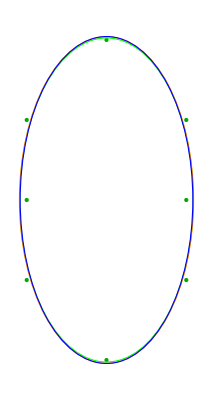
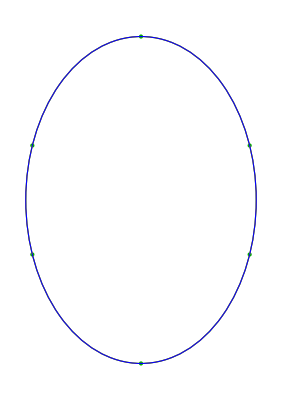
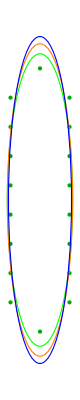
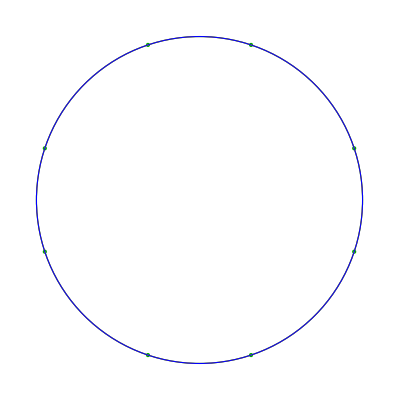
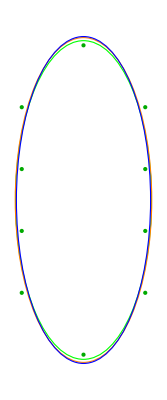
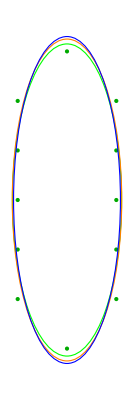
-Graphics-
 | OpenCV | Direct | AMS
x0 | 57. | 57. | 57.
y0 | 471. | 471. | 471.
a | 2.36376 | 2.36376 | 2.36376
b | 3.87378 | 3.87378 | 3.87378
θ | 115.67 | 115.67 | 115.67Ellipse ParametersData set : 4 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 67.3393 | 67.341 | 67.335
y0 | 470.661 | 470.659 | 470.665
a | 1.25812 | 1.23624 | 1.18487
b | 1.7608 | 1.69314 | 1.79163
θ | 135. | 135. | 135.Ellipse ParametersData set : 5 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 58.0446 | 58.0328 | 57.6845
y0 | 468.948 | 468.949 | 468.986
a | 1.22998 | 1.0599 | 0.813217
b | 4.07168 | 3.53983 | 6.46745
θ | 93.6242 | 92.5264 | 90.636Ellipse ParametersData set : 6 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 51.5 | 51.5 | 51.5
y0 | 457. | 457. | 457.
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 90. | 90. | 90.Ellipse ParametersData set : 14
-Graphics-
 | OpenCV | Direct | AMS
x0 | 53. | 53. | 53.
y0 | 453. | 453. | 453.
a | 1.09109 | 1.08766 | 1.0822
b | 2.04124 | 2.02437 | 2.04234
θ | 0. | 0. | 0.Ellipse ParametersData set : 20 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 42. | 42. | 42.
y0 | 444.5 | 444.5 | 444.5
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 0. | 0. | 0.Ellipse ParametersData set : 30 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 45. | 45. | 45.
y0 | 442.5 | 442.5 | 442.5
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 0. | 0. | 0.Ellipse ParametersData set : 32 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 48.7237 | 48.7237 | 48.7221
y0 | 441.5 | 441.5 | 441.5
a | 2.59904 | 2.57091 | 2.57067
b | 2.62419 | 2.59645 | 2.59685
θ | 0. | 0. | 180.Ellipse ParametersData set : 34
-Graphics-
 | OpenCV | Direct | AMS
x0 | 31.6367 | 31.7801 | 31.6367
y0 | 442.453 | 442.378 | 442.453
a | 2.24272 | 1.95743 | 2.24272
b | 3.53105 | 2.38034 | 3.53105
θ | 141.687 | 135.552 | 141.687Ellipse ParametersData set : 37 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 37.5799 | 37.4625 | 37.5799
y0 | 437.613 | 437.811 | 437.613
a | 1.49071 | 1.30265 | 1.49071
b | 2.76466 | 2.15056 | 2.76466
θ | 19.263 | 10.3804 | 19.263Ellipse ParametersData set : 39 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 41. | 41. | 41.
y0 | 427.5 | 427.5 | 427.5
a | 1.10696 | 1.10852 | 1.06848
b | 5.34287 | 5.00029 | 5.58942
θ | 0. | 0. | 0.Ellipse ParametersData set : 42 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 27.1957 | 27.1947 | 27.1996
y0 | 424.402 | 424.402 | 424.403
a | 1.50651 | 1.48609 | 1.46784
b | 2.0701 | 2.02945 | 2.06082
θ | 111.049 | 111.142 | 111.558Ellipse ParametersData set : 43
-Graphics-
 | OpenCV | Direct | AMS
x0 | 9. | 9. | 9.
y0 | 400.5 | 400.5 | 400.5
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 0. | 0. | 0.Ellipse ParametersData set : 48 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 3.5 | 3.5 | 3.5
y0 | 392. | 392. | 392.
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 90. | 90. | 90.Ellipse ParametersData set : 50 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 6.5 | 6.5 | 6.5
y0 | 390.5 | 390.5 | 390.5
a | 1.58114 | 1.58114 | 1.58114
b | 1.58114 | 1.58114 | 1.58114
θ | 0. | 0. | 0.Ellipse ParametersData set : 51 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 3.7977 | 3.79487 | 3.81121
y0 | 388.076 | 388.076 | 388.082
a | 2.22989 | 2.16345 | 2.11859
b | 2.69812 | 2.59556 | 2.66024
θ | 140.408 | 140.166 | 140.422Ellipse ParametersData set : 53
-Graphics-
 | OpenCV | Direct | AMS
x0 | 323.455 | 324.583 | 323.455
y0 | 335.64 | 335.117 | 335.64
a | 0.868221 | 0.89639 | 0.868221
b | 1.54276 | 1.49978 | 1.54276
θ | 62.1234 | 110.039 | 62.1234Ellipse ParametersData set : 56 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 333.21 | 331.706 | 333.21
y0 | 334.147 | 334.706 | 334.147
a | 9.31394 | 7.23013 | 9.31394
b | 19.1928 | 16.3346 | 19.1928
θ | 97.1002 | 102.741 | 97.1002Ellipse ParametersData set : 58 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 310.5 | 310.5 | 310.5
y0 | 242. | 242. | 242.
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 90. | 90. | 90.Ellipse ParametersData set : 59 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 315. | 315. | 315.
y0 | 236. | 236. | 236.
a | 1.09109 | 1.08766 | 1.0822
b | 2.04124 | 2.02437 | 2.04234
θ | 0. | 0. | 0.Ellipse ParametersData set : 60
-Graphics-
 | OpenCV | Direct | AMS
x0 | 172.576 | 180.119 | 161.368
y0 | 158.809 | 163.127 | 152.397
a | 6.1829 | 6.2396 | 5.90891
b | 185.338 | 159.737 | 213.666
θ | 119.798 | 119.798 | 119.796Ellipse ParametersData set : 70 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 232.025 | 231.998 | 232.243
y0 | 80.1429 | 80.1621 | 79.933
a | 1.60633 | 1.48456 | 1.29503
b | 2.54223 | 2.25817 | 3.07032
θ | 62.1143 | 66.5218 | 57.3Ellipse ParametersData set : 71 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 223.762 | 223.764 | 223.704
y0 | 80.098 | 80.1172 | 80.0162
a | 1.37641 | 1.28215 | 1.17418
b | 2.15565 | 1.91567 | 2.2887
θ | 145.161 | 148.724 | 140.216Ellipse ParametersData set : 72 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 216.922 | 216.8 | 216.922
y0 | 77.4368 | 77.3065 | 77.4368
a | 1.32677 | 0.918509 | 1.32677
b | 1.72916 | 1.58474 | 1.72916
θ | 4.44039 | 12.2728 | 4.44039Ellipse ParametersData set : 74
-Graphics-
 | OpenCV | Direct | AMS
x0 | 235.563 | 235.527 | 235.563
y0 | 70.0417 | 70.164 | 70.0417
a | 2.29127 | 1.83753 | 2.29127
b | 5.48529 | 4.93825 | 5.48529
θ | 162.24 | 163.53 | 162.24Ellipse ParametersData set : 78 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 195. | 195. | 195.
y0 | 63. | 63. | 63.
a | 1.09109 | 1.08766 | 1.0822
b | 2.04124 | 2.02437 | 2.04234
θ | 0. | 0. | 0.Ellipse ParametersData set : 82 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 199. | 199. | 199.
y0 | 58.5 | 58.5 | 58.5
a | 1.10527 | 1.10036 | 1.08651
b | 2.62488 | 2.57522 | 2.64207
θ | 0. | 0. | 0.Ellipse ParametersData set : 84 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 207. | 207. | 207.
y0 | 55. | 55. | 55.
a | 1.73205 | 1.73205 | 1.73205
b | 2.46021 | 2.46021 | 2.46021
θ | 90. | 90. | 90.Ellipse ParametersData set : 88
-Graphics-
 | OpenCV | Direct | AMS
x0 | 192.651 | 192.657 | 192.63
y0 | 51.0748 | 51.1212 | 50.9148
a | 1.61803 | 1.58862 | 1.4946
b | 6.59558 | 6.16998 | 7.03142
θ | 178.514 | 178.582 | 178.385Ellipse ParametersData set : 94 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 231.401 | 231.393 | 231.419
y0 | 46.6305 | 46.6266 | 46.6297
a | 1.68331 | 1.63971 | 1.54806
b | 2.66652 | 2.48831 | 2.74669
θ | 6.00318 | 7.08623 | 5.1905Ellipse ParametersData set : 96 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 197. | 197. | 197.
y0 | 42. | 42. | 42.
a | 1.11075 | 1.10622 | 1.08399
b | 3.24893 | 3.15062 | 3.2999
θ | 0. | 0. | 0.Ellipse ParametersData set : 98 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 194. | 194. | 194.
y0 | 41.5 | 41.5 | 41.5
a | 1.10527 | 1.10036 | 1.08651
b | 2.62488 | 2.57522 | 2.64207
θ | 0. | 0. | 0.Ellipse ParametersData set : 99
-Graphics-
 | OpenCV | Direct | AMS
x0 | 205. | 205. | 205.
y0 | 30.5 | 30.5 | 30.5
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 0. | 0. | 0.Ellipse ParametersData set : 105 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 203. | 203. | 203.
y0 | 30.5 | 30.5 | 30.5
a | 1.06066 | 1.06066 | 1.06066
b | 1.5 | 1.5 | 1.5
θ | 0. | 0. | 0.Ellipse ParametersData set : 106 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 230.45 | 230.454 | 230.468
y0 | 57.3667 | 57.3625 | 57.3756
a | 31.9916 | 31.867 | 31.7973
b | 36.9964 | 36.7593 | 36.8704
θ | 165.64 | 165.431 | 165.658Ellipse ParametersData set : 109 | -Graphics-
 | OpenCV | Direct | AMS
x0 | 321.169 | 321.157 | 321.743
y0 | 238.348 | 238.327 | 238.027
a | 276.104 | 271.992 | 264.477
b | 381.929 | 371.716 | 385.231
θ | 91.3741 | 91.0586 | 91.2957Ellipse ParametersData set : 110

```mathematica
Grid[ArrayReshape[Table[Panel[Column[{Show[{Graphics[{Opacity[1],Darker[Green],PointSize[Medium],Point[Symbol["points"<>ToString[n]<>"Cpp"]] }],showEllipse[ Symbol["ellipseDirect"<>ToString[n]<>"Cpp"]],showEllipse[ Symbol["ellipse"<>ToString[n]<>"Cpp"],Orange],showEllipse[ Symbol["ellipseAMS"<>ToString[n]<>"Cpp"],Blue]
}],
tableEllipse[{Symbol["ellipse"<>ToString[n]<>"Cpp"],Symbol["ellipseDirect"<>ToString[n]<>"Cpp"],Symbol["ellipseAMS"<>ToString[n]<>"Cpp"]},{"OpenCV","Direct","AMS"},{Orange,Green,Blue}]}],"Data set : "<>ToString[n]],
{n,dataSets}],{Ceiling[Length[dataSets]/4],4},""]]
```